# Work Code Samples

Peter Cullen Burbery

Abstract

## Section



```mathematica
CycleGraph[3]
```

```mathematica
{{-Graphics-, CodeEquivalentQ}}[CycleGraph[3,DirectedEdges->True],Graph[{1->2,2->3,3->1}]]
```

False


<|Timing→<|SameQ→0.001011,EqualQ→0.001011,ToCanonicalForm1→0.120989,ToCanonicalForm2→0.254013,Evaluate1→0.25899,Evaluate2→0.262989,SandboxEquivalentQ→0.4829889|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[CycleGraph[3,DirectedEdges→True]],2→HoldComplete[-Graphics-]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→False,EquivalentQ→False|>

```mathematica
{{-Graphics-, EquivalenceTestData}}[CycleGraph[3,DirectedEdges->True],Graph[{1->2,2->3,3->1}]]
```

```mathematica
CycleGraph[3,DirectedEdges->True]
```

-Graphics-

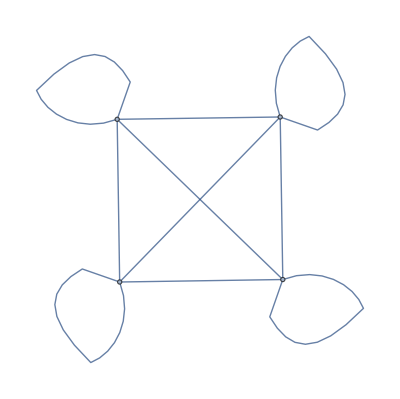

```mathematica
AdjacencyGraph[ConstantArray[1,{4,4}]]
```

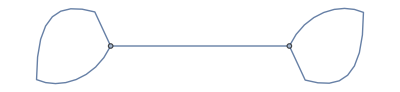
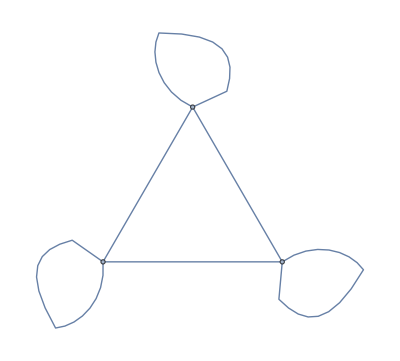
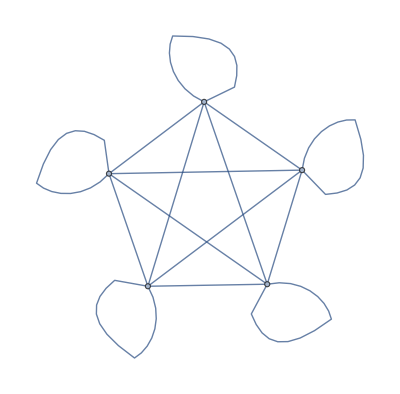
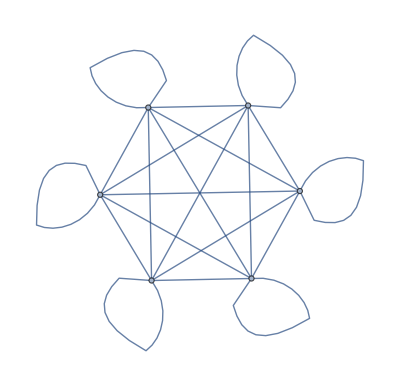
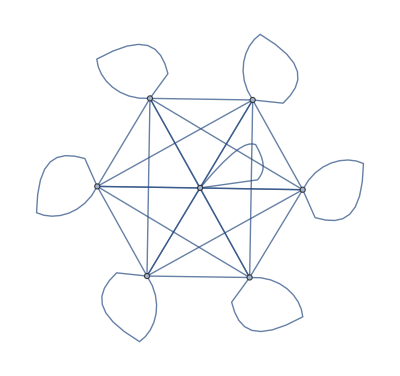
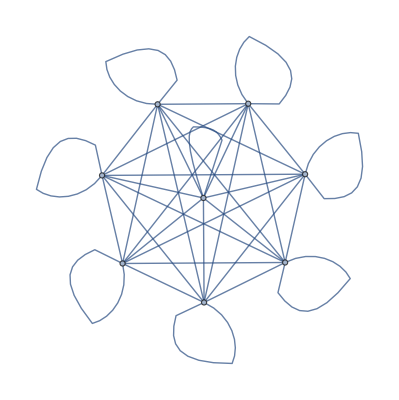
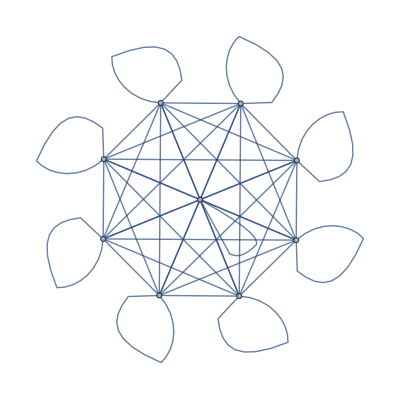
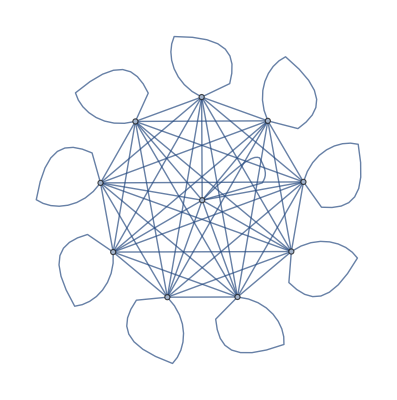
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[AdjacencyGraph[ConstantArray[1,{i,i}]],{i,2,10}]
```

```mathematica
Table[{1,2},3]
```

{{1,2},{1,2},{1,2}}

```mathematica
Flatten[Table[{1,2},3]]
```

{1,2,1,2,1,2}

```mathematica
IntegerDigits/@Range[100]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{1,0,0}}

```mathematica
Flatten[IntegerDigits/@Range[100]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,3,0,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,4,0,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,5,0,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,6,0,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,7,0,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,8,0,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,9,0,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,1,0,0}

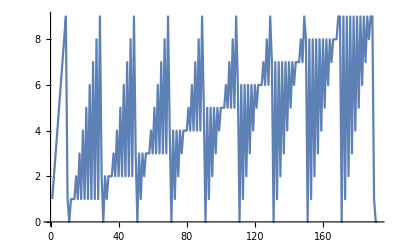

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[100]]]
```

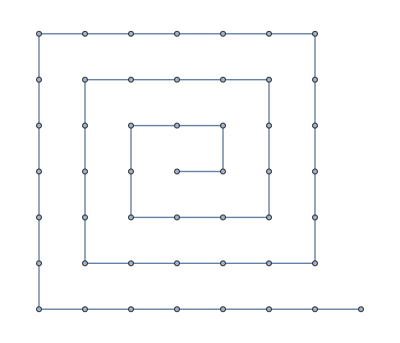

```mathematica
PathGraph[Range[50]]
```

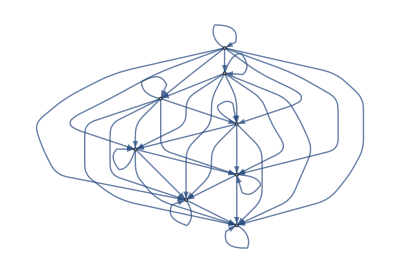

```mathematica
RelationGraph[#1==Max[{#1,#2}]&, {1,2,3,4,5,6,7,8}]
```

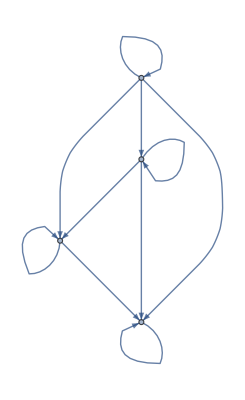

```mathematica
RelationGraph[#1==Max[{#1,#2}]&, Range[4]]
```

```mathematica
Table[i->j-i,{i,5},{j,5}]
```

{{1->0,1->1,1->2,1->3,1->4},{2->-1,2->0,2->1,2->2,2->3},{3->-2,3->-1,3->0,3->1,3->2},{4->-3,4->-2,4->-1,4->0,4->1},{5->-4,5->-3,5->-2,5->-1,5->0}}

```mathematica
Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

```mathematica
RandomInteger[{1,100},100]
```

{42,2,40,27,30,95,68,35,60,66,7,31,5,49,72,66,69,26,8,40,17,89,71,34,70,59,71,61,14,47,71,56,76,92,94,91,93,12,32,22,73,90,61,75,86,71,86,3,43,98,98,95,6,92,20,71,73,77,9,58,19,51,62,19,6,96,52,100,25,89,18,64,24,85,41,23,75,73,17,89,39,9,60,86,27,87,21,97,63,17,28,31,8,49,72,6,54,69,10,60}

```mathematica
Thread[Range[100]<->RandomInteger[{1,100},100]]
```

{1<->89,2<->77,3<->96,4<->24,5<->79,6<->88,7<->98,8<->38,9<->21,10<->64,11<->9,12<->13,13<->22,14<->64,15<->34,16<->99,17<->92,18<->72,19<->80,20<->99,21<->41,22<->62,23<->69,24<->43,25<->77,26<->28,27<->55,28<->59,29<->40,30<->6,31<->92,32<->77,33<->35,34<->84,35<->96,36<->62,37<->14,38<->55,39<->12,40<->24,41<->94,42<->86,43<->17,44<->25,45<->9,46<->42,47<->27,48<->6,49<->2,50<->60,51<->71,52<->99,53<->44,54<->50,55<->95,56<->73,57<->65,58<->50,59<->91,60<->72,61<->8,62<->37,63<->2,64<->14,65<->80,66<->82,67<->32,68<->21,69<->93,70<->8,71<->53,72<->62,73<->74,74<->58,75<->100,76<->42,77<->31,78<->66,79<->30,80<->87,81<->23,82<->65,83<->61,84<->1,85<->2,86<->53,87<->55,88<->97,89<->17,90<->9,91<->88,92<->8,93<->57,94<->33,95<->77,96<->12,97<->15,98<->2,99<->50,100<->57}

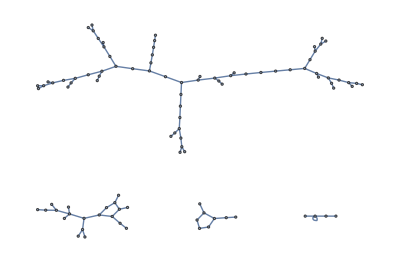

```mathematica
Graph[Thread[Range[100]<->RandomInteger[{1,100},100]]]
```

```mathematica
{{-Graphics-, CodeEquivalentQ}}[Graph[Thread[Range[100]<->RandomInteger[{1,100},100]]],Graph[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

False

```mathematica
{{-Graphics-, CodeEquivalentQ}}[Graph[Thread[Range[100]->RandomInteger[{1,100},100]]],Graph[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

True

```mathematica
{{-Graphics-, EquivalenceTestData}}[Graph[Thread[Range[100]->RandomInteger[{1,100},100]]],Graph[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

<|Timing→<|SameQ→0.,EqualQ→0.0009934,ToCanonicalForm1→0.8419975,ToCanonicalForm2→0.8419975,Evaluate1→0.8480005,Evaluate2→0.8529991,SandboxEquivalentQ→1.08699|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Graph[Thread[Table[S1∷ℤ,{S1∷ℤ,1,100,1}]->Table[ℛ[DiscreteUniformDistribution[{1,100}]],{S2∷ℤ,1,100,1}]]]],2→HoldComplete[Graph[Table[S1∷ℤ→ℛ[DiscreteUniformDistribution[{1,100}]],{S1∷ℤ,1,100,1}]]]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→True,EquivalentQ→True|>

```mathematica
{{-Graphics-, EquivalenceTestData}}[Graph[Thread[Range[100]<->RandomInteger[{1,100},100]]],Graph[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

<|Timing→<|SameQ→0.,EqualQ→0.001487,ToCanonicalForm1→0.9838405,ToCanonicalForm2→1.451929,Evaluate1→1.458907,Evaluate2→1.462901,SandboxEquivalentQ→1.674502,Raster1→2.056026,Raster2→2.261023,RasterError→2.293024|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Graph[Thread[Table[S1∷ℤ,{S1∷ℤ,1,100,1}]<->Table[ℛ[DiscreteUniformDistribution[{1,100}]],{S2∷ℤ,1,100,1}]]]],2→HoldComplete[Graph[Table[S1∷ℤ→ℛ[DiscreteUniformDistribution[{1,100}]],{S1∷ℤ,1,100,1}]]]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→False,RasterForms→<|1→-Graphics-,2→-Graphics-|>,RasterError→0.0714487,RasterEquivalentQ→False,EquivalentQ→False|>

```mathematica
{{-Graphics-, ToCanonicalForm}}[HoldForm@Graph[Thread[Range[100]<->RandomInteger[{1,100},100]]]]
```

Graph[Thread[Table[S1∷ℤ,{S1∷ℤ,1,100,1}]<->Table[ℛ[DiscreteUniformDistribution[{1,100}]],{S2∷ℤ,1,100,1}]]]

```mathematica
{{-Graphics-, ToCanonicalForm}}[HoldForm@Graph[Table[i->RandomInteger[{1,100}],{i,100}]]]
```

Graph[Table[S1∷ℤ→ℛ[DiscreteUniformDistribution[{1,100}]],{S1∷ℤ,1,100,1}]]

```mathematica
Table[Thread[{i,i}<->RandomInteger[{1,100},2]],{i,100}]
```

{{1<->29,1<->84},{2<->3,2<->27},{3<->83,3<->32},{4<->73,4<->13},{5<->70,5<->13},{6<->16,6<->26},{7<->19,7<->55},{8<->37,8<->54},{9<->95,9<->74},{10<->20,10<->24},{11<->59,11<->73},{12<->61,12<->48},{13<->71,13<->28},{14<->14,14<->17},{15<->28,15<->37},{16<->32,16<->70},{17<->35,17<->51},{18<->27,18<->63},{19<->51,19<->15},{20<->79,20<->84},{21<->5,21<->39},{22<->23,22<->45},{23<->76,23<->25},{24<->66,24<->16},{25<->38,25<->24},{26<->85,26<->37},{27<->55,27<->22},{28<->64,28<->8},{29<->26,29<->39},{30<->21,30<->11},{31<->100,31<->68},{32<->73,32<->64},{33<->78,33<->81},{34<->89,34<->88},{35<->82,35<->49},{36<->23,36<->83},{37<->69,37<->69},{38<->46,38<->39},{39<->74,39<->23},{40<->7,40<->83},{41<->49,41<->14},{42<->71,42<->11},{43<->14,43<->54},{44<->88,44<->91},{45<->78,45<->75},{46<->98,46<->96},{47<->46,47<->3},{48<->2,48<->100},{49<->51,49<->92},{50<->50,50<->41},{51<->65,51<->32},{52<->32,52<->68},{53<->68,53<->92},{54<->97,54<->87},{55<->26,55<->8},{56<->11,56<->60},{57<->91,57<->53},{58<->19,58<->98},{59<->46,59<->13},{60<->76,60<->43},{61<->22,61<->31},{62<->81,62<->80},{63<->92,63<->40},{64<->22,64<->48},{65<->62,65<->76},{66<->73,66<->62},{67<->97,67<->51},{68<->15,68<->63},{69<->27,69<->16},{70<->96,70<->5},{71<->4,71<->6},{72<->61,72<->30},{73<->85,73<->46},{74<->89,74<->16},{75<->79,75<->34},{76<->14,76<->25},{77<->92,77<->27},{78<->63,78<->97},{79<->35,79<->33},{80<->57,80<->88},{81<->97,81<->80},{82<->60,82<->30},{83<->72,83<->76},{84<->81,84<->71},{85<->19,85<->98},{86<->24,86<->7},{87<->88,87<->66},{88<->50,88<->5},{89<->43,89<->88},{90<->70,90<->66},{91<->62,91<->6},{92<->14,92<->87},{93<->23,93<->24},{94<->21,94<->7},{95<->54,95<->29},{96<->62,96<->2},{97<->90,97<->93},{98<->64,98<->20},{99<->92,99<->39},{100<->79,100<->46}}

```mathematica
Flatten[Table[Thread[{i,i}<->RandomInteger[{1,100},2]],{i,100}]]
```

{1<->76,1<->38,2<->14,2<->9,3<->45,3<->38,4<->55,4<->30,5<->51,5<->73,6<->25,6<->76,7<->63,7<->10,8<->55,8<->72,9<->86,9<->75,10<->36,10<->22,11<->28,11<->73,12<->30,12<->48,13<->95,13<->35,14<->11,14<->37,15<->18,15<->40,16<->8,16<->44,17<->63,17<->46,18<->35,18<->26,19<->1,19<->88,20<->4,20<->11,21<->86,21<->41,22<->24,22<->22,23<->26,23<->85,24<->99,24<->94,25<->82,25<->96,26<->36,26<->93,27<->82,27<->44,28<->52,28<->71,29<->68,29<->58,30<->62,30<->91,31<->95,31<->97,32<->45,32<->99,33<->82,33<->72,34<->24,34<->65,35<->47,35<->54,36<->22,36<->10,37<->11,37<->59,38<->33,38<->2,39<->90,39<->4,40<->94,40<->61,41<->13,41<->43,42<->54,42<->29,43<->15,43<->15,44<->42,44<->26,45<->50,45<->72,46<->78,46<->58,47<->60,47<->24,48<->53,48<->36,49<->73,49<->76,50<->37,50<->29,51<->68,51<->89,52<->74,52<->83,53<->73,53<->71,54<->17,54<->2,55<->6,55<->17,56<->97,56<->11,57<->98,57<->36,58<->92,58<->66,59<->95,59<->25,60<->60,60<->98,61<->91,61<->83,62<->76,62<->53,63<->66,63<->12,64<->90,64<->40,65<->54,65<->56,66<->6,66<->44,67<->63,67<->4,68<->22,68<->90,69<->1,69<->98,70<->82,70<->49,71<->4,71<->19,72<->94,72<->39,73<->40,73<->80,74<->36,74<->3,75<->9,75<->37,76<->12,76<->26,77<->66,77<->72,78<->66,78<->86,79<->15,79<->1,80<->59,80<->77,81<->41,81<->26,82<->10,82<->60,83<->69,83<->36,84<->43,84<->92,85<->96,85<->13,86<->59,86<->12,87<->85,87<->12,88<->75,88<->63,89<->52,89<->70,90<->77,90<->89,91<->46,91<->60,92<->30,92<->70,93<->94,93<->6,94<->93,94<->87,95<->29,95<->86,96<->41,96<->32,97<->74,97<->99,98<->35,98<->89,99<->46,99<->88,100<->59,100<->76}

```mathematica
Graph[Flatten[Table[Thread[{i,i}<->RandomInteger[{1,100},2]],{i,100}]]]
```

-Graphics-

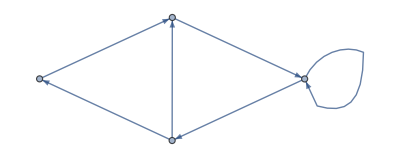

```mathematica
Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]
```

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]]
```

ShortestPathFunction[{All,All},«»]

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]]@@@Array[{#1,#2}&,{4,4}]
```

{ShortestPathFunction[{All,All},«»][{1,1},{1,2},{1,3},{1,4}],ShortestPathFunction[{All,All},«»][{2,1},{2,2},{2,3},{2,4}],ShortestPathFunction[{All,All},«»][{3,1},{3,2},{3,3},{3,4}],ShortestPathFunction[{All,All},«»][{4,1},{4,2},{4,3},{4,4}]}

```mathematica
Flatten[Table[{i,j},{i,4},{j,4}],{2}]
```

{{{1,1},{2,1},{3,1},{4,1}},{{1,2},{2,2},{3,2},{4,2}},{{1,3},{2,3},{3,3},{4,3}},{{1,4},{2,4},{3,4},{4,4}}}

```mathematica
Tuples[Range@4,2]
```

{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4}}

```mathematica
FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]]@@@Tuples[Range@4,2]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{2,3,1},{2},{2,3},{2,3,4},{3,1},{3,1,2},{3},{3,4},{4,1},{4,1,2},{4,1,2,3},{4}}

```mathematica
Partition[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]]@@@Tuples[Range@4,2],4]
```

{{{1},{1,2},{1,2,3},{1,2,3,4}},{{2,3,1},{2},{2,3},{2,3,4}},{{3,1},{3,1,2},{3},{3,4}},{{4,1},{4,1,2},{4,1,2,3},{4}}}

```mathematica
Grid@Partition[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}]]@@@Tuples[Range@4,2],4]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

```mathematica
DirectedGraph@AdjacencyGraph[ConstantArray[1,{4,4}],GraphLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
{{-Graphics-, EquivalenceTestData}}[Graph[Flatten[Table[i->j,{i,4},{j,4}]],GraphLayout->"RadialDrawing"],DirectedGraph@AdjacencyGraph[ConstantArray[1,{4,4}],GraphLayout->"RadialEmbedding"]]
```

<|Timing→<|SameQ→0.,EqualQ→0.0009986,ToCanonicalForm1→0.756975,ToCanonicalForm2→1.61151,Evaluate1→1.619508,Evaluate2→1.625514,SandboxEquivalentQ→1.844997|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Graph[Flatten[Table[Table[S1∷ℤ→S2∷ℤ,{S2∷ℤ,1,4,1}],{S1∷ℤ,1,4,1}]],GraphLayout→RadialDrawing]],2→HoldComplete[DirectedGraph[AdjacencyGraph[Table[Table[1,{S1∷ℤ,1,4,1}],{S2∷ℤ,1,4,1}],GraphLayout→RadialEmbedding]]]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→False,EquivalentQ→False|>

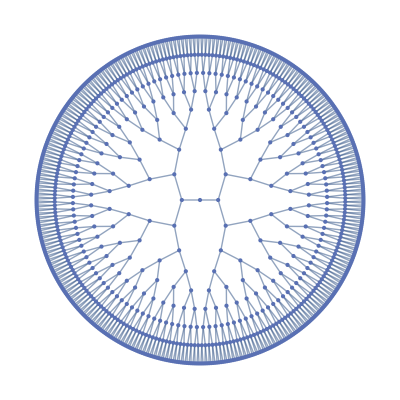

```mathematica
CompleteKaryTree[10,2]
```

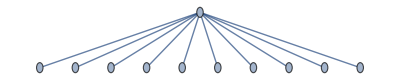

```mathematica
CompleteKaryTree[2,10]
```

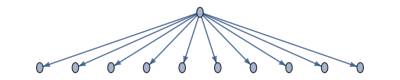

```mathematica
CompleteKaryTree[2,10,DirectedEdges->True]
```

```mathematica
Range[50]/.{r_?EvenQ->Style[r,Red]}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
Binarize[Rasterize["W"]]
```

-Graphics-

```mathematica
ImageData@Binarize[Rasterize["W"]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,1,1,1,1,1,1,1,1,0},{1,0,0,1,1,1,1,1,1,1,0,0},{1,0,0,1,1,1,1,1,1,1,0,0},{1,0,0,1,1,1,1,1,1,1,0,0},{1,0,0,1,1,1,1,1,1,1,0,0},{1,0,0,1,1,1,0,1,1,1,0,0},{1,0,0,1,1,1,0,0,1,1,0,0},{1,0,0,1,1,0,0,0,1,1,0,0},{1,0,0,1,1,0,0,0,1,1,0,0},{1,0,0,1,1,0,1,0,0,1,0,0},{1,1,0,0,0,0,1,0,0,1,0,0},{1,1,0,0,0,1,1,1,0,1,0,1},{1,1,0,0,0,1,1,1,0,0,0,1},{1,1,0,0,0,1,1,1,0,0,0,1},{1,1,0,0,1,1,1,1,1,0,0,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Flatten@ImageData@Binarize[Rasterize["W"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,0,0,1,1,1,0,0,1,1,0,0,1,0,0,1,1,0,0,0,1,1,0,0,1,0,0,1,1,0,0,0,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,1,1,1,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Total@Flatten@ImageData@Binarize[Rasterize["W"]]
```

233

```mathematica
Total@Flatten@ImageData@Binarize[Rasterize["W"]]
```

233

```mathematica
Sum[Total@IntegerDigits[k],{k,1000}]
```

13501

```mathematica
Sum[Total@IntegerDigits[k],{k,1000000}]//AbsoluteTiming
```

{0.0640157,27000001}

```mathematica
Total[Flatten[Table[IntegerDigits[n],{n,1000000}]]]//AbsoluteTiming
```

{1.53977,27000001}

```mathematica
Graph[DirectedEdge@@@RandomInteger[100,{200,2}]]
```

-Graphics-

```mathematica
EdgeCount[Graph[UndirectedEdge@@@RandomInteger[100,{200,2}]]]
```

200

```mathematica
CommunityGraphPlot[Graph[DirectedEdge@@@RandomInteger[100,{200,2}]]]
```

-Graphics-

```mathematica
CommunityGraphPlot[Graph[Table[RandomInteger[100]->RandomInteger[100],200]]]
```

-Graphics-

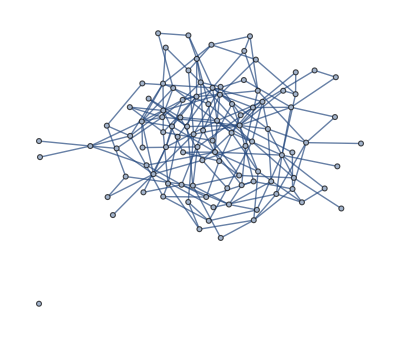

```mathematica
RandomGraph[{101,200}]
```

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
ImageIdentify[Entity["Species","Species:PantheraTigris"][EntityProperty["Species","Image"]]]
```

tiger

```mathematica
ImageIdentify[Blur[Entity["Species","Species:PantheraTigris"][EntityProperty["Species","Image"]],#]]&/@Range[5]
```

{tiger,tiger,tiger,spiny-finned fish,fish}

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
RandomInteger[1000,20]
```

{580,804,406,300,659,76,629,728,296,373,174,91,403,599,51,249,15,70,945,78}

```mathematica
Nearest[RandomInteger[1000,20],3]
```

{44}

```mathematica
Nearest[RandomInteger[1000,20],100]
```

{94}

```mathematica
Nearest[RandomInteger[1000,20],100,3]
```

{1,212,272}

```mathematica
RandomColor[10]
```

{RGBColor[0.009899434465258983, 0.23473960706213814, 0.9256269587097963],RGBColor[0.15598186121360613, 0.16472317654859792, 0.8760062734531799],RGBColor[0.33273883328561626, 0.5513320675962969, 0.1675906021329685],RGBColor[0.847787136241122, 0.9352080547862598, 0.629736582169115],RGBColor[0.3132783407266271, 0.26041078043502064, 0.5687963824016415],RGBColor[0.9653605708665347, 0.8194596129538589, 0.25428643289581654],RGBColor[0.35603878679287004, 0.8387101070766811, 0.15194114936847525],RGBColor[0.4130991019470185, 0.8598863891496928, 0.21610551713398984],RGBColor[0.90711522258069, 0.8661649247853909, 0.9627669002718819],RGBColor[0.3953211887413013, 0.4416408519673396, 0.07617644548598346]}

```mathematica
Nearest[RandomColor[10],Red]
```

{RGBColor[0.4991852438577238, 0.05423925845714117, 0.11989269038783079]}

```mathematica
Nearest[RandomColor[10],Red,5]
```

{RGBColor[0.4514496955704286, 0.3627922474089369, 0.30655109424213367],RGBColor[0.6277957232013662, 0.4815792070944285, 0.7893836444634093],RGBColor[0.03450882189621152, 0.2735726857062273, 0.18614207834963392],RGBColor[0.15070643512965698, 0.4884711635173793, 0.25140673646260425],RGBColor[0.6822684001716646, 0.4687584461700214, 0.9186257740174899]}

```mathematica
Nearest[Range[100]^2,2000]
```

{2025}

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]]]
```

{-Graphics-}

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

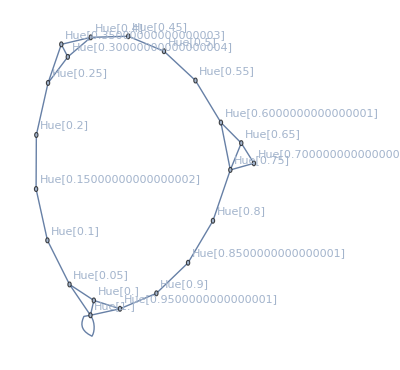

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2,VertexLabels->Automatic]
```

```mathematica
Table[Hue[h],{h,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

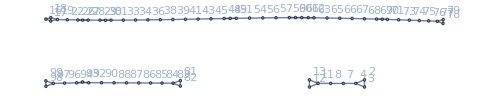

```mathematica
NearestNeighborGraph[RandomInteger[100,100],2,VertexLabels->Automatic]
```

```mathematica
?NearestNeighborGraph
```

```mathematica
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
N[√2,500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
RandomReal[1,10]
```

{0.747017,0.213704,0.627117,0.510969,0.782056,0.220974,0.666006,0.933626,0.952014,0.738435}

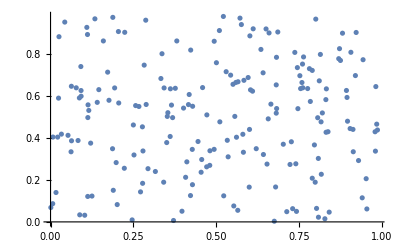

```mathematica
ListPlot[RandomReal[1,{200,2}]]
```

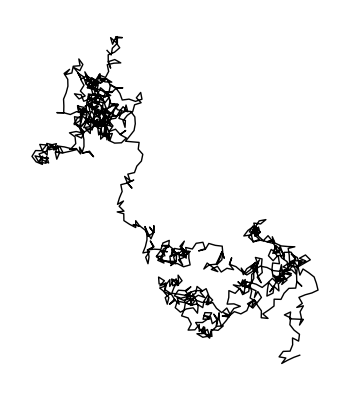

```mathematica
Graphics[Line@AnglePath[RandomReal[2π,1000]]]
```

```mathematica
Table[Mod[i^2,10],{i,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

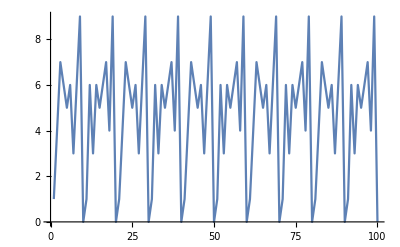

```mathematica
ListLinePlot[Table[Mod[i^i,10],{i,100}]]
```

```mathematica
Round[Pi^Range[10]]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

```mathematica
Thread[Range[0,99]<->Mod[Range[0,99]^2,100]]
```

{0<->0,1<->1,2<->4,3<->9,4<->16,5<->25,6<->36,7<->49,8<->64,9<->81,10<->0,11<->21,12<->44,13<->69,14<->96,15<->25,16<->56,17<->89,18<->24,19<->61,20<->0,21<->41,22<->84,23<->29,24<->76,25<->25,26<->76,27<->29,28<->84,29<->41,30<->0,31<->61,32<->24,33<->89,34<->56,35<->25,36<->96,37<->69,38<->44,39<->21,40<->0,41<->81,42<->64,43<->49,44<->36,45<->25,46<->16,47<->9,48<->4,49<->1,50<->0,51<->1,52<->4,53<->9,54<->16,55<->25,56<->36,57<->49,58<->64,59<->81,60<->0,61<->21,62<->44,63<->69,64<->96,65<->25,66<->56,67<->89,68<->24,69<->61,70<->0,71<->41,72<->84,73<->29,74<->76,75<->25,76<->76,77<->29,78<->84,79<->41,80<->0,81<->61,82<->24,83<->89,84<->56,85<->25,86<->96,87<->69,88<->44,89<->21,90<->0,91<->81,92<->64,93<->49,94<->36,95<->25,96<->16,97<->9,98<->4,99<->1}

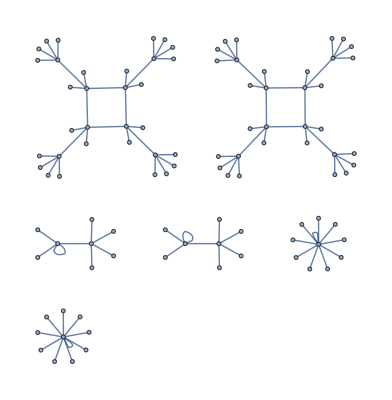

```mathematica
Graph[Thread[Range[0,99]<->Mod[Range[0,99]^2,100]]]
```

```mathematica
?Thread
```

```mathematica
Thread[List[RandomColor[50],RandomReal[10,50]]]
```

{{RGBColor[0.1915612596445473, 0.08980656801860776, 0.9120729792425082],3.71002},{RGBColor[0.5520032558794845, 0.3730756302792486, 0.6250138820240669],5.17186},{RGBColor[0.24490000491611363, 0.19388446877957244, 0.9889626203254636],9.12821},{RGBColor[0.2587230608515032, 0.30019588856491985, 0.6033846147325284],2.95807},{RGBColor[0.984658977285549, 0.7831007307883622, 0.622819194235924],4.33788},{RGBColor[0.044934498169583614, 0.3773878633237473, 0.8761325454278417],3.11757},{RGBColor[0.6390728982565452, 0.8115267632641618, 0.9759698055724182],9.77494},{RGBColor[0.06082549182114261, 0.7604449398616413, 0.7770132895438668],1.9803},{RGBColor[0.7939020282425042, 0.25136168719655405, 0.44317355508708944],7.89703},{RGBColor[0.6002793845767693, 0.7737364644177653, 0.47555573276437046],1.36424},{RGBColor[0.6422682011580108, 0.6323504672012987, 0.7407916301338027],7.68941},{RGBColor[0.04796159622284035, 0.558712910243244, 0.5415749295486654],4.16328},{RGBColor[0.20167923101940244, 0.48569244947826107, 0.5064984488817066],1.1423},{RGBColor[0.3215486935583469, 0.7961671817816711, 0.7607993127732537],6.18822},{RGBColor[0.18733160628282852, 0.3630090905190264, 0.7352717835826903],5.15376},{RGBColor[0.15807764673158142, 0.6820270476435186, 0.22734194052392231],1.9961},{RGBColor[0.16343807290152923, 0.21001499397333956, 0.8813363642175844],9.00339},{RGBColor[0.48737262621271715, 0.9684221666795763, 0.38044071901845533],0.94751},{RGBColor[0.04152461547881692, 0.8538099494120792, 0.37174623048171074],7.79879},{RGBColor[0.7465125175888456, 0.5462135920628233, 0.4021673192802455],7.05232},{RGBColor[0.60889007045881, 0.43052449032968987, 0.8853197894098732],7.73395},{RGBColor[0.5571747975963328, 0.6882202853693828, 0.8775418389949243],5.02322},{RGBColor[0.48470481374621444, 0.6047055227431886, 0.9059094979435849],8.72176},{RGBColor[0.28636223737543043, 0.6260381485473041, 0.5786887746510678],2.67141},{RGBColor[0.2748280664328804, 0.2985610255615052, 0.8513188396935427],7.14436},{RGBColor[0.5999305831437161, 0.15439009780953827, 0.618447873319319],4.71832},{RGBColor[0.2939840886056906, 0.7545943542069096, 0.15114683956491515],9.77676},{RGBColor[0.80446216193428, 0.7336520458407076, 0.42481606555953033],3.46134},{RGBColor[0.3814970844979144, 0.882455365242516, 0.2618088744488678],9.62082},{RGBColor[0.4030574703210643, 0.5387028562699243, 0.20392585610546332],2.77873},{RGBColor[0.15293825054014443, 0.015985269615670594, 0.041264524363452404],8.8251},{RGBColor[0.7103881925412534, 0.7383687935343408, 0.46695123902804214],8.66241},{RGBColor[0.049738209742309136, 0.06687184112229794, 0.13305562088842238],6.2431},{RGBColor[0.13793323444230476, 0.3310977022237547, 0.4438015560223645],2.73535},{RGBColor[0.4679593209007378, 0.5474498034280058, 0.04135253021628005],7.07991},{RGBColor[0.10736280220565697, 0.47110365969482504, 0.3539512728147127],2.8016},{RGBColor[0.8405256795506904, 0.042790731014614725, 0.15516722115979276],9.97566},{RGBColor[0.29369059320667446, 0.802168725501911, 0.3273896872727142],8.47607},{RGBColor[0.07634238416817962, 0.9361708767803216, 0.33267281897420786],8.06337},{RGBColor[0.19866257938928022, 0.8602301294422487, 0.2440219451636818],1.33024},{RGBColor[0.405773342317687, 0.6286915801587982, 0.9579617421509432],9.07121},{RGBColor[0.7473824010547081, 0.17735369099853515, 0.6322292953343367],4.55531},{RGBColor[0.8005658989193483, 0.13577619567568555, 0.6181713213908491],3.84759},{RGBColor[0.9791215738535712, 0.3581716268245201, 0.7985475654467766],6.18262},{RGBColor[0.5985833993961669, 0.6052359614621607, 0.5565865860729504],1.75024},{RGBColor[0.7839072655565291, 0.25393201041409963, 0.11185357520294548],7.32491},{RGBColor[0.8246723249340531, 0.36170778832543315, 0.5970208554865368],2.76029},{RGBColor[0.7901729432377584, 0.21316956251818175, 0.8159891580155849],7.63187},{RGBColor[0.151809427636177, 0.1457031812467786, 0.1871122582831486],4.42994},{RGBColor[0.9850148335005096, 0.8917592767197002, 0.8349399332132879],0.943722}}

```mathematica
Thread[List[RandomReal[10,50],RandomReal[2,50]]]
```

{{3.94308,1.0529},{5.83713,0.795515},{4.48937,1.85117},{7.18888,1.69485},{9.69791,0.481711},{6.82591,0.507704},{3.08517,1.33432},{3.53577,1.8161},{9.95608,1.1772},{7.96357,1.24292},{1.04173,1.62987},{9.86581,1.96775},{8.0094,1.5432},{4.95813,1.49415},{5.14616,0.822725},{9.74616,1.43119},{4.57795,1.43937},{0.469136,0.315129},{1.92065,0.396092},{1.63941,1.08097},{7.36776,1.14902},{2.15692,0.870048},{5.2184,1.27753},{3.05106,0.145612},{9.31598,0.602811},{6.10938,1.82081},{4.00991,1.07364},{0.260446,0.837109},{1.7714,1.00629},{3.86949,0.0615131},{0.285455,0.155982},{2.78492,1.11628},{8.81243,0.703864},{1.61384,0.468972},{7.47232,1.99648},{1.98929,0.707629},{3.97807,1.75774},{1.60552,0.00298171},{1.5969,1.49234},{8.50241,0.189439},{4.27282,0.452198},{6.35303,0.450002},{5.11668,1.49767},{4.87341,1.71603},{7.68083,1.35438},{0.0708717,0.493569},{3.65052,0.604886},{9.09098,0.219242},{8.00195,0.389502},{4.64071,1.67045}}

```mathematica
Thread[List[RandomReal[10,{50,2}],RandomReal[2,50]]]
```

{{{1.52891,2.93075},0.00517353},{{1.67449,9.09149},0.463789},{{7.43217,3.66704},1.90584},{{6.83412,5.53492},0.123728},{{5.03424,3.14336},1.7444},{{5.45417,4.53645},1.79555},{{8.53162,0.808312},1.01004},{{5.12538,7.03475},1.36517},{{0.611119,3.35811},1.36024},{{5.61646,5.08852},0.466037},{{1.76119,3.29748},0.926113},{{0.785978,0.497378},1.07574},{{0.958589,1.49306},0.0300766},{{2.71801,5.44732},0.434687},{{7.89978,5.76379},0.749834},{{9.60156,2.50606},1.51815},{{4.84404,2.86109},1.62765},{{0.228533,8.31026},1.829},{{8.63924,5.66745},1.32753},{{1.36509,0.569812},0.280433},{{2.78986,0.930967},1.02029},{{1.01646,3.2778},1.63957},{{9.72294,2.81692},1.04081},{{4.4224,5.0844},0.608645},{{4.22875,5.48912},1.14917},{{0.403913,2.16806},0.0971568},{{0.23197,8.027},1.73725},{{7.99806,3.25352},1.05018},{{0.380317,2.80705},0.68976},{{2.6859,9.4653},0.573962},{{3.21323,6.96033},1.92112},{{4.00499,0.194965},0.536932},{{2.35463,9.52069},0.738724},{{2.41621,1.39006},1.82922},{{4.80851,1.21342},1.03808},{{4.88936,5.35761},0.560054},{{1.00278,6.83354},0.404591},{{9.28089,9.67367},0.557989},{{6.82229,9.10369},0.364539},{{4.06344,7.06363},0.0375546},{{6.92103,0.159969},0.997757},{{4.44892,9.75087},1.93921},{{5.31523,1.46614},0.786599},{{5.73118,7.34689},0.915233},{{9.90001,1.30894},1.80005},{{7.22839,1.41789},0.816135},{{8.74396,2.04119},0.536788},{{7.77735,1.3945},1.38226},{{4.13185,8.48551},0.0338599},{{7.65282,6.44669},1.32974}}

```mathematica
Circle@@@Thread[List[RandomReal[10,{50,2}],RandomReal[2,50]]]
```

{Circle[{1.91784,8.77359},1.0508],Circle[{6.0318,5.00878},1.21133],Circle[{5.49887,6.41387},0.249705],Circle[{0.515666,4.82664},1.95103],Circle[{6.97236,3.53676},1.80392],Circle[{2.91852,7.44643},0.186886],Circle[{0.171816,2.44657},1.03943],Circle[{3.37344,5.96135},1.57328],Circle[{6.38206,5.82002},1.13877],Circle[{0.0800642,0.733181},0.649447],Circle[{0.128838,8.60715},1.67925],Circle[{7.19456,5.53438},1.92005],Circle[{2.72513,2.33281},0.989483],Circle[{6.86694,9.90469},1.94379],Circle[{5.02682,7.64515},1.03077],Circle[{8.88987,9.61246},0.205666],Circle[{0.865705,5.95},0.625298],Circle[{7.72403,8.11953},1.80598],Circle[{8.04905,9.00278},0.590666],Circle[{1.50135,2.64394},1.09563],Circle[{8.0957,2.95399},0.436801],Circle[{3.11214,0.600118},0.638814],Circle[{3.79183,9.23777},1.46736],Circle[{8.56584,7.34789},1.79695],Circle[{9.38187,0.51802},1.16373],Circle[{3.20051,8.80565},0.232713],Circle[{7.65729,7.50215},0.9283],Circle[{9.41607,9.86479},1.76981],Circle[{4.55448,1.76373},0.864741],Circle[{5.07663,2.10468},1.14072],Circle[{1.71553,0.010904},1.36879],Circle[{8.2443,8.35902},1.01927],Circle[{1.66808,0.299602},1.72817],Circle[{0.296202,9.18719},0.188468],Circle[{1.42214,8.31004},0.355267],Circle[{9.61583,3.63961},0.692823],Circle[{6.20448,4.58892},1.78878],Circle[{0.630653,3.21495},1.04837],Circle[{5.64525,2.71578},0.870734],Circle[{0.0138881,6.60421},1.0217],Circle[{7.90941,8.74996},0.899879],Circle[{9.45292,0.260161},0.96054],Circle[{9.821,3.17458},1.45722],Circle[{3.00768,6.6871},0.121204],Circle[{1.537,4.77131},1.13661],Circle[{6.79973,2.68528},1.70321],Circle[{1.67188,6.22218},0.0775048],Circle[{4.1964,5.33262},0.879439],Circle[{4.9614,9.12685},1.98827],Circle[{2.69144,2.69024},1.64961]}

```mathematica
Thread[{RandomColor[50],Circle@@@Thread[List[RandomReal[10,{50,2}],RandomReal[2,50]]]}]
```

{{RGBColor[0.6119538396424329, 0.4947771611905285, 0.4893086753612068],Circle[{7.9496,9.88705},1.27439]},{RGBColor[0.1913722286139341, 0.24276419822983608, 0.1250817309645167],Circle[{3.6901,9.09782},0.0635918]},{RGBColor[0.5787728646346848, 0.9114003515027289, 0.4096672360714746],Circle[{9.53757,0.695543},0.927293]},{RGBColor[0.9522740536529641, 0.6793135961914718, 0.7067477249556284],Circle[{1.28202,8.86567},1.57177]},{RGBColor[0.044856644107425625, 0.9202063031411467, 0.2368689796764858],Circle[{1.71332,9.81051},1.15976]},{RGBColor[0.2971249172434731, 0.9442165768354569, 0.051424291798607635],Circle[{9.06311,0.566609},1.32084]},{RGBColor[0.5721635391830329, 0.40959819305643563, 0.9799351958729892],Circle[{9.49992,1.73457},0.300245]},{RGBColor[0.42156945917342714, 0.037177468444438144, 0.026198813057393577],Circle[{5.64969,6.85034},1.54872]},{RGBColor[0.3848126388218631, 0.49297868183349336, 0.17754853655102587],Circle[{2.24248,9.04632},0.105273]},{RGBColor[0.6372636046568518, 0.3551477776083716, 0.3567319179563011],Circle[{1.56006,2.55048},1.71634]},{RGBColor[0.05603646491919623, 0.998544956057458, 0.10569294840885202],Circle[{8.12507,9.94515},1.83498]},{RGBColor[0.43164782055199535, 0.4071455903541392, 0.06195814842428393],Circle[{0.432721,0.0559461},0.163402]},{RGBColor[0.6009385808121317, 0.6495221310252415, 0.07192418587783478],Circle[{2.82225,0.784067},0.531499]},{RGBColor[0.6480538829816218, 0.26926859247760526, 0.9993409254402403],Circle[{3.70746,5.44413},0.784391]},{RGBColor[0.5408610183771076, 0.9547925171105844, 0.3945315494018873],Circle[{5.57536,1.117},0.584929]},{RGBColor[0.19825462010787587, 0.09252278222082255, 0.8339627131602878],Circle[{2.69849,6.93188},0.883441]},{RGBColor[0.7607163690554317, 0.5314472893335658, 0.9937332222591799],Circle[{9.10646,3.58152},1.55894]},{RGBColor[0.6226972332093139, 0.48777721890891335, 0.46471764473208754],Circle[{8.17432,2.55068},0.549266]},{RGBColor[0.41843266290133574, 0.8411609182284436, 0.1899895941226193],Circle[{6.52537,3.90427},0.523114]},{RGBColor[0.15644305226830357, 0.25921234486781897, 0.20622177790456853],Circle[{9.94534,9.01991},0.559424]},{RGBColor[0.28430406838300315, 0.012270590349659827, 0.03400013876658892],Circle[{6.98043,3.46942},0.418449]},{RGBColor[0.6591299720451815, 0.0191356803501308, 0.6566804819589851],Circle[{9.71126,2.00946},1.95556]},{RGBColor[0.8376011285744718, 0.8990468754870145, 0.2329106185458738],Circle[{8.72779,0.308319},0.136929]},{RGBColor[0.5976970556463157, 0.37439373607428883, 0.05424737247019529],Circle[{9.18521,3.0069},1.50476]},{RGBColor[0.7866190014502403, 0.7209818163586692, 0.19135511190567245],Circle[{3.34103,3.95563},0.747644]},{RGBColor[0.23463834780042614, 0.7367082063159691, 0.6849729491414702],Circle[{0.408107,0.542456},1.8214]},{RGBColor[0.24628492645350653, 0.7017545459715109, 0.2761956551682474],Circle[{0.571386,8.21021},1.79201]},{RGBColor[0.6320382138219547, 0.3542949358687624, 0.27854167864073487],Circle[{1.18571,3.39651},1.08201]},{RGBColor[0.8583239451247227, 0.31583579289980546, 0.5308667940075806],Circle[{1.59049,9.37591},1.58933]},{RGBColor[0.6238208021102174, 0.2630224150217204, 0.6733898011451271],Circle[{0.614606,0.2137},0.108572]},{RGBColor[0.7269703370478073, 0.5735989140001352, 0.830647771912661],Circle[{0.815903,4.71148},0.237965]},{RGBColor[0.8724154473497665, 0.9555044137464392, 0.1216826863564171],Circle[{1.25718,2.7704},0.902185]},{RGBColor[0.7499537539574177, 0.16926001624229592, 0.04940569833235875],Circle[{2.3007,8.34923},1.39627]},{RGBColor[0.9383138253342007, 0.02462764243098836, 0.705530873649816],Circle[{8.3483,6.96049},1.90886]},{RGBColor[0.40076886744685747, 0.20292248248385136, 0.771895250295257],Circle[{3.14531,7.95572},1.27493]},{RGBColor[0.6303864865013731, 0.3068071774767125, 0.13191188898565898],Circle[{0.359079,6.01121},0.301534]},{RGBColor[0.8488477745684475, 0.2568883096201666, 0.29510624643484906],Circle[{5.38833,4.92549},1.37194]},{RGBColor[0.04587942195609429, 0.9583793592464309, 0.9694273622321827],Circle[{1.16472,0.0229858},0.952811]},{RGBColor[0.2022442059374958, 0.6872564211214371, 0.3295364205789486],Circle[{8.47724,2.76573},1.7359]},{RGBColor[0.5552598457440292, 0.9992982828563732, 0.9540733054720703],Circle[{7.41705,8.54519},0.530902]},{RGBColor[0.43534124603125024, 0.15305572818532776, 0.16621008967864692],Circle[{4.16637,9.82772},0.21888]},{RGBColor[0.15535276224836214, 0.27279099908136617, 0.3551165824582394],Circle[{2.44344,9.24697},1.46579]},{RGBColor[0.17839106759162204, 0.12942713592985, 0.7176549034174018],Circle[{3.09207,1.6289},1.32289]},{RGBColor[0.3142008154729208, 0.4506794417327942, 0.41889942678984693],Circle[{1.29727,2.77538},1.8571]},{RGBColor[0.9903910734064316, 0.5033244826662568, 0.293478078251473],Circle[{0.36082,5.60749},1.38725]},{RGBColor[0.7094090230669077, 0.17778128878469013, 0.4984258840017197],Circle[{8.17131,5.92157},1.56453]},{RGBColor[0.08129159810257902, 0.5310058266698376, 0.2922035767483533],Circle[{6.96637,2.5283},0.650942]},{RGBColor[0.5715012572414482, 0.8730566713696652, 0.31851428718551444],Circle[{4.15113,1.45376},0.436506]},{RGBColor[0.3080366594165267, 0.29703032330635293, 0.49535661651299523],Circle[{0.484097,7.31998},0.0211446]},{RGBColor[0.4313142132787815, 0.9777387622534539, 0.5007713976186297],Circle[{6.13889,6.01523},0.623525]}}

```mathematica
MapThread[Circle,{RandomReal[10,{50,2}],RandomReal[2,50]}]
```

{Circle[{2.51566,2.17615},0.0998358],Circle[{3.94123,0.00183119},1.03265],Circle[{8.27358,1.23073},1.13074],Circle[{6.96152,1.54093},0.721411],Circle[{1.62696,9.84667},0.147171],Circle[{6.81014,3.0643},0.25652],Circle[{2.95743,5.38265},0.483541],Circle[{7.03653,3.61063},1.74215],Circle[{9.40369,9.98562},0.533488],Circle[{1.25711,2.85116},1.30455],Circle[{2.78207,5.09305},0.356812],Circle[{1.80457,6.05585},0.526519],Circle[{9.6718,1.53687},0.496743],Circle[{5.47976,8.06118},0.0923464],Circle[{9.39003,2.09814},0.801097],Circle[{7.28398,0.096596},1.93521],Circle[{5.2566,1.56062},0.616199],Circle[{2.97603,7.05005},0.110658],Circle[{5.3193,6.77445},1.08901],Circle[{3.43153,8.98132},0.543394],Circle[{6.01006,4.85104},0.00211508],Circle[{0.184975,1.06854},0.315942],Circle[{1.89974,6.23313},0.554928],Circle[{1.90806,9.85878},0.829582],Circle[{9.85496,5.8949},1.30597],Circle[{2.83217,8.78214},0.137209],Circle[{2.24771,4.26506},0.247062],Circle[{0.343777,2.3692},1.54233],Circle[{1.06552,1.12078},1.92748],Circle[{7.96668,1.25826},0.788717],Circle[{3.10153,5.89668},1.06761],Circle[{2.78566,6.92344},1.89723],Circle[{7.11737,3.63402},1.55193],Circle[{4.0136,6.7946},0.063562],Circle[{9.2828,0.697797},1.23196],Circle[{6.58681,2.41333},1.64727],Circle[{9.31795,2.6351},1.19639],Circle[{1.97806,0.0681723},1.77723],Circle[{0.133565,9.49269},0.118859],Circle[{2.34015,5.50378},1.62683],Circle[{7.17108,7.52636},1.12001],Circle[{6.93509,5.31931},0.882111],Circle[{8.34405,0.236854},1.9429],Circle[{6.01447,5.09362},1.56936],Circle[{7.89449,8.81512},0.369405],Circle[{1.18564,3.17391},0.518499],Circle[{7.05482,3.4422},0.621448],Circle[{3.32585,7.58806},0.996626],Circle[{7.89907,8.09198},0.841972],Circle[{2.00988,1.97064},1.84951]}

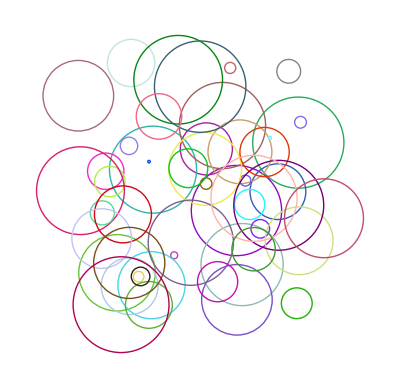

```mathematica
Graphics[Thread[{RandomColor[50],Circle@@@Thread[List[RandomReal[10,{50,2}],RandomReal[2,50]]]}]]
```

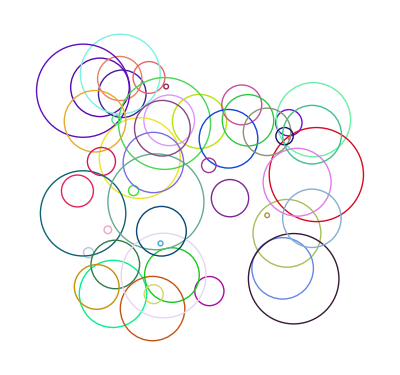

```mathematica
Graphics[Thread[{RandomColor[50],MapThread[Circle,{RandomReal[10,{50,2}],RandomReal[2,50]}]}]]
```

```mathematica
PacletInstall["Wolfram/CodeEquivalenceUtilities"]
```

PacletObject[…]

```mathematica
Needs["Wolfram`CodeEquivalenceUtilities`"]
```

```mathematica
CodeEquivalentQ[Graphics[Table[Style[Circle[RandomReal[10,2],RandomReal[2]],RandomColor[]],50]],Graphics[Thread[{RandomColor[50],MapThread[Circle,{RandomReal[10,{50,2}],RandomReal[2,50]}]}]]]
```

False

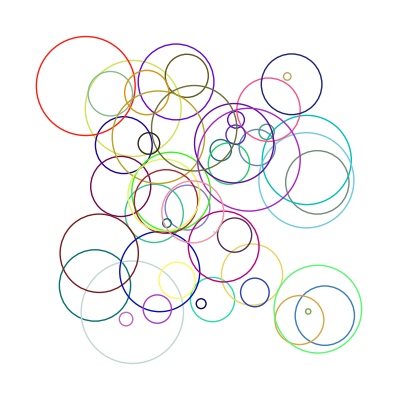
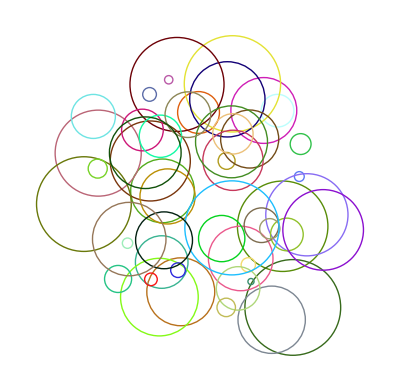
<|Timing→<|SameQ→0.,EqualQ→0.026613,ToCanonicalForm1→1.433109,ToCanonicalForm2→2.730294,Evaluate1→2.739288,Evaluate2→2.744288,SandboxEquivalentQ→2.940308,Raster1→3.235147,Raster2→3.346147,RasterError→3.37414|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[-Graphics-],2→HoldComplete[-Graphics-]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→False,RasterForms→<|1→-Graphics-,2→-Graphics-|>,RasterError→0.130605,RasterEquivalentQ→False,EquivalentQ→False|>

```mathematica
EquivalenceTestData[Graphics[Table[Style[Circle[RandomReal[10,2],RandomReal[2]],RandomColor[]],50]],Graphics[Thread[{RandomColor[50],MapThread[Circle,{RandomReal[10,{50,2}],RandomReal[2,50]}]}]]]
```

```mathematica
Table[Prime[i]/(i Log[i]),{i,2,1000}]
```

{3/(2 Log[2]),5/(3 Log[3]),7/(4 Log[4]),11/(5 Log[5]),13/(6 Log[6]),17/(7 Log[7]),19/(8 Log[8]),23/(9 Log[9]),29/(10 Log[10]),31/(11 Log[11]),37/(12 Log[12]),41/(13 Log[13]),43/(14 Log[14]),47/(15 Log[15]),53/(16 Log[16]),59/(17 Log[17]),61/(18 Log[18]),67/(19 Log[19]),71/(20 Log[20]),73/(21 Log[21]),79/(22 Log[22]),83/(23 Log[23]),89/(24 Log[24]),97/(25 Log[25]),101/(26 Log[26]),103/(27 Log[27]),107/(28 Log[28]),109/(29 Log[29]),113/(30 Log[30]),127/(31 Log[31]),131/(32 Log[32]),137/(33 Log[33]),139/(34 Log[34]),149/(35 Log[35]),151/(36 Log[36]),157/(37 Log[37]),163/(38 Log[38]),167/(39 Log[39]),173/(40 Log[40]),179/(41 Log[41]),181/(42 Log[42]),191/(43 Log[43]),193/(44 Log[44]),197/(45 Log[45]),199/(46 Log[46]),211/(47 Log[47]),223/(48 Log[48]),227/(49 Log[49]),229/(50 Log[50]),233/(51 Log[51]),239/(52 Log[52]),241/(53 Log[53]),251/(54 Log[54]),257/(55 Log[55]),263/(56 Log[56]),269/(57 Log[57]),271/(58 Log[58]),277/(59 Log[59]),281/(60 Log[60]),283/(61 Log[61]),293/(62 Log[62]),307/(63 Log[63]),311/(64 Log[64]),313/(65 Log[65]),317/(66 Log[66]),331/(67 Log[67]),337/(68 Log[68]),347/(69 Log[69]),349/(70 Log[70]),353/(71 Log[71]),359/(72 Log[72]),367/(73 Log[73]),373/(74 Log[74]),379/(75 Log[75]),383/(76 Log[76]),389/(77 Log[77]),397/(78 Log[78]),401/(79 Log[79]),409/(80 Log[80]),419/(81 Log[81]),421/(82 Log[82]),431/(83 Log[83]),433/(84 Log[84]),439/(85 Log[85]),443/(86 Log[86]),449/(87 Log[87]),457/(88 Log[88]),461/(89 Log[89]),463/(90 Log[90]),467/(91 Log[91]),479/(92 Log[92]),487/(93 Log[93]),491/(94 Log[94]),499/(95 Log[95]),503/(96 Log[96]),509/(97 Log[97]),521/(98 Log[98]),523/(99 Log[99]),541/(100 Log[100]),547/(101 Log[101]),557/(102 Log[102]),563/(103 Log[103]),569/(104 Log[104]),571/(105 Log[105]),577/(106 Log[106]),587/(107 Log[107]),593/(108 Log[108]),599/(109 Log[109]),601/(110 Log[110]),607/(111 Log[111]),613/(112 Log[112]),617/(113 Log[113]),619/(114 Log[114]),631/(115 Log[115]),641/(116 Log[116]),643/(117 Log[117]),647/(118 Log[118]),653/(119 Log[119]),659/(120 Log[120]),661/(121 Log[121]),673/(122 Log[122]),677/(123 Log[123]),683/(124 Log[124]),691/(125 Log[125]),701/(126 Log[126]),709/(127 Log[127]),719/(128 Log[128]),727/(129 Log[129]),733/(130 Log[130]),739/(131 Log[131]),743/(132 Log[132]),751/(133 Log[133]),757/(134 Log[134]),761/(135 Log[135]),769/(136 Log[136]),773/(137 Log[137]),787/(138 Log[138]),797/(139 Log[139]),809/(140 Log[140]),811/(141 Log[141]),821/(142 Log[142]),823/(143 Log[143]),827/(144 Log[144]),829/(145 Log[145]),839/(146 Log[146]),853/(147 Log[147]),857/(148 Log[148]),859/(149 Log[149]),863/(150 Log[150]),877/(151 Log[151]),881/(152 Log[152]),883/(153 Log[153]),887/(154 Log[154]),907/(155 Log[155]),911/(156 Log[156]),919/(157 Log[157]),929/(158 Log[158]),937/(159 Log[159]),941/(160 Log[160]),947/(161 Log[161]),953/(162 Log[162]),967/(163 Log[163]),971/(164 Log[164]),977/(165 Log[165]),983/(166 Log[166]),991/(167 Log[167]),997/(168 Log[168]),1009/(169 Log[169]),1013/(170 Log[170]),1019/(171 Log[171]),1021/(172 Log[172]),1031/(173 Log[173]),1033/(174 Log[174]),1039/(175 Log[175]),1049/(176 Log[176]),1051/(177 Log[177]),1061/(178 Log[178]),1063/(179 Log[179]),1069/(180 Log[180]),1087/(181 Log[181]),1091/(182 Log[182]),1093/(183 Log[183]),1097/(184 Log[184]),1103/(185 Log[185]),1109/(186 Log[186]),1117/(187 Log[187]),1123/(188 Log[188]),1129/(189 Log[189]),1151/(190 Log[190]),1153/(191 Log[191]),1163/(192 Log[192]),1171/(193 Log[193]),1181/(194 Log[194]),1187/(195 Log[195]),1193/(196 Log[196]),1201/(197 Log[197]),1213/(198 Log[198]),1217/(199 Log[199]),1223/(200 Log[200]),1229/(201 Log[201]),1231/(202 Log[202]),1237/(203 Log[203]),1249/(204 Log[204]),1259/(205 Log[205]),1277/(206 Log[206]),1279/(207 Log[207]),1283/(208 Log[208]),1289/(209 Log[209]),1291/(210 Log[210]),1297/(211 Log[211]),1301/(212 Log[212]),1303/(213 Log[213]),1307/(214 Log[214]),1319/(215 Log[215]),1321/(216 Log[216]),1327/(217 Log[217]),1361/(218 Log[218]),1367/(219 Log[219]),1373/(220 Log[220]),1381/(221 Log[221]),1399/(222 Log[222]),1409/(223 Log[223]),1423/(224 Log[224]),1427/(225 Log[225]),1429/(226 Log[226]),1433/(227 Log[227]),1439/(228 Log[228]),1447/(229 Log[229]),1451/(230 Log[230]),1453/(231 Log[231]),1459/(232 Log[232]),1471/(233 Log[233]),1481/(234 Log[234]),1483/(235 Log[235]),1487/(236 Log[236]),1489/(237 Log[237]),1493/(238 Log[238]),1499/(239 Log[239]),1511/(240 Log[240]),1523/(241 Log[241]),1531/(242 Log[242]),1543/(243 Log[243]),1549/(244 Log[244]),1553/(245 Log[245]),1559/(246 Log[246]),1567/(247 Log[247]),1571/(248 Log[248]),1579/(249 Log[249]),1583/(250 Log[250]),1597/(251 Log[251]),1601/(252 Log[252]),1607/(253 Log[253]),1609/(254 Log[254]),1613/(255 Log[255]),1619/(256 Log[256]),1621/(257 Log[257]),1627/(258 Log[258]),1637/(259 Log[259]),1657/(260 Log[260]),1663/(261 Log[261]),1667/(262 Log[262]),1669/(263 Log[263]),1693/(264 Log[264]),1697/(265 Log[265]),1699/(266 Log[266]),1709/(267 Log[267]),1721/(268 Log[268]),1723/(269 Log[269]),1733/(270 Log[270]),1741/(271 Log[271]),1747/(272 Log[272]),1753/(273 Log[273]),1759/(274 Log[274]),1777/(275 Log[275]),1783/(276 Log[276]),1787/(277 Log[277]),1789/(278 Log[278]),1801/(279 Log[279]),1811/(280 Log[280]),1823/(281 Log[281]),1831/(282 Log[282]),1847/(283 Log[283]),1861/(284 Log[284]),1867/(285 Log[285]),1871/(286 Log[286]),1873/(287 Log[287]),1877/(288 Log[288]),1879/(289 Log[289]),1889/(290 Log[290]),1901/(291 Log[291]),1907/(292 Log[292]),1913/(293 Log[293]),1931/(294 Log[294]),1933/(295 Log[295]),1949/(296 Log[296]),1951/(297 Log[297]),1973/(298 Log[298]),1979/(299 Log[299]),1987/(300 Log[300]),1993/(301 Log[301]),1997/(302 Log[302]),1999/(303 Log[303]),2003/(304 Log[304]),2011/(305 Log[305]),2017/(306 Log[306]),2027/(307 Log[307]),2029/(308 Log[308]),2039/(309 Log[309]),2053/(310 Log[310]),2063/(311 Log[311]),2069/(312 Log[312]),2081/(313 Log[313]),2083/(314 Log[314]),2087/(315 Log[315]),2089/(316 Log[316]),2099/(317 Log[317]),2111/(318 Log[318]),2113/(319 Log[319]),2129/(320 Log[320]),2131/(321 Log[321]),2137/(322 Log[322]),2141/(323 Log[323]),2143/(324 Log[324]),2153/(325 Log[325]),2161/(326 Log[326]),2179/(327 Log[327]),2203/(328 Log[328]),2207/(329 Log[329]),2213/(330 Log[330]),2221/(331 Log[331]),2237/(332 Log[332]),2239/(333 Log[333]),2243/(334 Log[334]),2251/(335 Log[335]),2267/(336 Log[336]),2269/(337 Log[337]),2273/(338 Log[338]),2281/(339 Log[339]),2287/(340 Log[340]),2293/(341 Log[341]),2297/(342 Log[342]),2309/(343 Log[343]),2311/(344 Log[344]),2333/(345 Log[345]),2339/(346 Log[346]),2341/(347 Log[347]),2347/(348 Log[348]),2351/(349 Log[349]),2357/(350 Log[350]),2371/(351 Log[351]),2377/(352 Log[352]),2381/(353 Log[353]),2383/(354 Log[354]),2389/(355 Log[355]),2393/(356 Log[356]),2399/(357 Log[357]),2411/(358 Log[358]),2417/(359 Log[359]),2423/(360 Log[360]),2437/(361 Log[361]),2441/(362 Log[362]),2447/(363 Log[363]),2459/(364 Log[364]),2467/(365 Log[365]),2473/(366 Log[366]),2477/(367 Log[367]),2503/(368 Log[368]),2521/(369 Log[369]),2531/(370 Log[370]),2539/(371 Log[371]),2543/(372 Log[372]),2549/(373 Log[373]),2551/(374 Log[374]),2557/(375 Log[375]),2579/(376 Log[376]),2591/(377 Log[377]),2593/(378 Log[378]),2609/(379 Log[379]),2617/(380 Log[380]),2621/(381 Log[381]),2633/(382 Log[382]),2647/(383 Log[383]),2657/(384 Log[384]),2659/(385 Log[385]),2663/(386 Log[386]),2671/(387 Log[387]),2677/(388 Log[388]),2683/(389 Log[389]),2687/(390 Log[390]),2689/(391 Log[391]),2693/(392 Log[392]),2699/(393 Log[393]),2707/(394 Log[394]),2711/(395 Log[395]),2713/(396 Log[396]),2719/(397 Log[397]),2729/(398 Log[398]),2731/(399 Log[399]),2741/(400 Log[400]),2749/(401 Log[401]),2753/(402 Log[402]),2767/(403 Log[403]),2777/(404 Log[404]),2789/(405 Log[405]),2791/(406 Log[406]),2797/(407 Log[407]),2801/(408 Log[408]),2803/(409 Log[409]),2819/(410 Log[410]),2833/(411 Log[411]),2837/(412 Log[412]),2843/(413 Log[413]),2851/(414 Log[414]),2857/(415 Log[415]),2861/(416 Log[416]),2879/(417 Log[417]),2887/(418 Log[418]),2897/(419 Log[419]),2903/(420 Log[420]),2909/(421 Log[421]),2917/(422 Log[422]),2927/(423 Log[423]),2939/(424 Log[424]),2953/(425 Log[425]),2957/(426 Log[426]),2963/(427 Log[427]),2969/(428 Log[428]),2971/(429 Log[429]),2999/(430 Log[430]),3001/(431 Log[431]),3011/(432 Log[432]),3019/(433 Log[433]),3023/(434 Log[434]),3037/(435 Log[435]),3041/(436 Log[436]),3049/(437 Log[437]),3061/(438 Log[438]),3067/(439 Log[439]),3079/(440 Log[440]),3083/(441 Log[441]),3089/(442 Log[442]),3109/(443 Log[443]),3119/(444 Log[444]),3121/(445 Log[445]),3137/(446 Log[446]),3163/(447 Log[447]),3167/(448 Log[448]),3169/(449 Log[449]),3181/(450 Log[450]),3187/(451 Log[451]),3191/(452 Log[452]),3203/(453 Log[453]),3209/(454 Log[454]),3217/(455 Log[455]),3221/(456 Log[456]),3229/(457 Log[457]),3251/(458 Log[458]),3253/(459 Log[459]),3257/(460 Log[460]),3259/(461 Log[461]),3271/(462 Log[462]),3299/(463 Log[463]),3301/(464 Log[464]),3307/(465 Log[465]),3313/(466 Log[466]),3319/(467 Log[467]),3323/(468 Log[468]),3329/(469 Log[469]),3331/(470 Log[470]),3343/(471 Log[471]),3347/(472 Log[472]),3359/(473 Log[473]),3361/(474 Log[474]),3371/(475 Log[475]),3373/(476 Log[476]),3389/(477 Log[477]),3391/(478 Log[478]),3407/(479 Log[479]),3413/(480 Log[480]),3433/(481 Log[481]),3449/(482 Log[482]),3457/(483 Log[483]),3461/(484 Log[484]),3463/(485 Log[485]),3467/(486 Log[486]),3469/(487 Log[487]),3491/(488 Log[488]),3499/(489 Log[489]),3511/(490 Log[490]),3517/(491 Log[491]),3527/(492 Log[492]),3529/(493 Log[493]),3533/(494 Log[494]),3539/(495 Log[495]),3541/(496 Log[496]),3547/(497 Log[497]),3557/(498 Log[498]),3559/(499 Log[499]),3571/(500 Log[500]),3581/(501 Log[501]),3583/(502 Log[502]),3593/(503 Log[503]),3607/(504 Log[504]),3613/(505 Log[505]),3617/(506 Log[506]),3623/(507 Log[507]),3631/(508 Log[508]),3637/(509 Log[509]),3643/(510 Log[510]),3659/(511 Log[511]),3671/(512 Log[512]),3673/(513 Log[513]),3677/(514 Log[514]),3691/(515 Log[515]),3697/(516 Log[516]),3701/(517 Log[517]),3709/(518 Log[518]),3719/(519 Log[519]),3727/(520 Log[520]),3733/(521 Log[521]),3739/(522 Log[522]),3761/(523 Log[523]),3767/(524 Log[524]),3769/(525 Log[525]),3779/(526 Log[526]),3793/(527 Log[527]),3797/(528 Log[528]),3803/(529 Log[529]),3821/(530 Log[530]),3823/(531 Log[531]),3833/(532 Log[532]),3847/(533 Log[533]),3851/(534 Log[534]),3853/(535 Log[535]),3863/(536 Log[536]),3877/(537 Log[537]),3881/(538 Log[538]),3889/(539 Log[539]),3907/(540 Log[540]),3911/(541 Log[541]),3917/(542 Log[542]),3919/(543 Log[543]),3923/(544 Log[544]),3929/(545 Log[545]),3931/(546 Log[546]),3943/(547 Log[547]),3947/(548 Log[548]),3967/(549 Log[549]),3989/(550 Log[550]),4001/(551 Log[551]),4003/(552 Log[552]),4007/(553 Log[553]),4013/(554 Log[554]),4019/(555 Log[555]),4021/(556 Log[556]),4027/(557 Log[557]),4049/(558 Log[558]),4051/(559 Log[559]),4057/(560 Log[560]),4073/(561 Log[561]),4079/(562 Log[562]),4091/(563 Log[563]),4093/(564 Log[564]),4099/(565 Log[565]),4111/(566 Log[566]),4127/(567 Log[567]),4129/(568 Log[568]),4133/(569 Log[569]),4139/(570 Log[570]),4153/(571 Log[571]),4157/(572 Log[572]),4159/(573 Log[573]),4177/(574 Log[574]),4201/(575 Log[575]),4211/(576 Log[576]),4217/(577 Log[577]),4219/(578 Log[578]),4229/(579 Log[579]),4231/(580 Log[580]),4241/(581 Log[581]),4243/(582 Log[582]),4253/(583 Log[583]),4259/(584 Log[584]),4261/(585 Log[585]),4271/(586 Log[586]),4273/(587 Log[587]),4283/(588 Log[588]),4289/(589 Log[589]),4297/(590 Log[590]),4327/(591 Log[591]),4337/(592 Log[592]),4339/(593 Log[593]),4349/(594 Log[594]),4357/(595 Log[595]),4363/(596 Log[596]),4373/(597 Log[597]),4391/(598 Log[598]),4397/(599 Log[599]),4409/(600 Log[600]),4421/(601 Log[601]),4423/(602 Log[602]),4441/(603 Log[603]),4447/(604 Log[604]),4451/(605 Log[605]),4457/(606 Log[606]),4463/(607 Log[607]),4481/(608 Log[608]),4483/(609 Log[609]),4493/(610 Log[610]),4507/(611 Log[611]),4513/(612 Log[612]),4517/(613 Log[613]),4519/(614 Log[614]),4523/(615 Log[615]),4547/(616 Log[616]),4549/(617 Log[617]),4561/(618 Log[618]),4567/(619 Log[619]),4583/(620 Log[620]),4591/(621 Log[621]),4597/(622 Log[622]),4603/(623 Log[623]),4621/(624 Log[624]),4637/(625 Log[625]),4639/(626 Log[626]),4643/(627 Log[627]),4649/(628 Log[628]),4651/(629 Log[629]),4657/(630 Log[630]),4663/(631 Log[631]),4673/(632 Log[632]),4679/(633 Log[633]),4691/(634 Log[634]),4703/(635 Log[635]),4721/(636 Log[636]),4723/(637 Log[637]),4729/(638 Log[638]),4733/(639 Log[639]),4751/(640 Log[640]),4759/(641 Log[641]),4783/(642 Log[642]),4787/(643 Log[643]),4789/(644 Log[644]),4793/(645 Log[645]),4799/(646 Log[646]),4801/(647 Log[647]),4813/(648 Log[648]),4817/(649 Log[649]),4831/(650 Log[650]),4861/(651 Log[651]),4871/(652 Log[652]),4877/(653 Log[653]),4889/(654 Log[654]),4903/(655 Log[655]),4909/(656 Log[656]),4919/(657 Log[657]),4931/(658 Log[658]),4933/(659 Log[659]),4937/(660 Log[660]),4943/(661 Log[661]),4951/(662 Log[662]),4957/(663 Log[663]),4967/(664 Log[664]),4969/(665 Log[665]),4973/(666 Log[666]),4987/(667 Log[667]),4993/(668 Log[668]),4999/(669 Log[669]),5003/(670 Log[670]),5009/(671 Log[671]),5011/(672 Log[672]),5021/(673 Log[673]),5023/(674 Log[674]),5039/(675 Log[675]),5051/(676 Log[676]),5059/(677 Log[677]),5077/(678 Log[678]),5081/(679 Log[679]),5087/(680 Log[680]),5099/(681 Log[681]),5101/(682 Log[682]),5107/(683 Log[683]),5113/(684 Log[684]),5119/(685 Log[685]),5147/(686 Log[686]),5153/(687 Log[687]),5167/(688 Log[688]),5171/(689 Log[689]),5179/(690 Log[690]),5189/(691 Log[691]),5197/(692 Log[692]),5209/(693 Log[693]),5227/(694 Log[694]),5231/(695 Log[695]),5233/(696 Log[696]),5237/(697 Log[697]),5261/(698 Log[698]),5273/(699 Log[699]),5279/(700 Log[700]),5281/(701 Log[701]),5297/(702 Log[702]),5303/(703 Log[703]),5309/(704 Log[704]),5323/(705 Log[705]),5333/(706 Log[706]),5347/(707 Log[707]),5351/(708 Log[708]),5381/(709 Log[709]),5387/(710 Log[710]),5393/(711 Log[711]),5399/(712 Log[712]),5407/(713 Log[713]),5413/(714 Log[714]),5417/(715 Log[715]),5419/(716 Log[716]),5431/(717 Log[717]),5437/(718 Log[718]),5441/(719 Log[719]),5443/(720 Log[720]),5449/(721 Log[721]),5471/(722 Log[722]),5477/(723 Log[723]),5479/(724 Log[724]),5483/(725 Log[725]),5501/(726 Log[726]),5503/(727 Log[727]),5507/(728 Log[728]),5519/(729 Log[729]),5521/(730 Log[730]),5527/(731 Log[731]),5531/(732 Log[732]),5557/(733 Log[733]),5563/(734 Log[734]),5569/(735 Log[735]),5573/(736 Log[736]),5581/(737 Log[737]),5591/(738 Log[738]),5623/(739 Log[739]),5639/(740 Log[740]),5641/(741 Log[741]),5647/(742 Log[742]),5651/(743 Log[743]),5653/(744 Log[744]),5657/(745 Log[745]),5659/(746 Log[746]),5669/(747 Log[747]),5683/(748 Log[748]),5689/(749 Log[749]),5693/(750 Log[750]),5701/(751 Log[751]),5711/(752 Log[752]),5717/(753 Log[753]),5737/(754 Log[754]),5741/(755 Log[755]),5743/(756 Log[756]),5749/(757 Log[757]),5779/(758 Log[758]),5783/(759 Log[759]),5791/(760 Log[760]),5801/(761 Log[761]),5807/(762 Log[762]),5813/(763 Log[763]),5821/(764 Log[764]),5827/(765 Log[765]),5839/(766 Log[766]),5843/(767 Log[767]),5849/(768 Log[768]),5851/(769 Log[769]),5857/(770 Log[770]),5861/(771 Log[771]),5867/(772 Log[772]),5869/(773 Log[773]),5879/(774 Log[774]),5881/(775 Log[775]),5897/(776 Log[776]),5903/(777 Log[777]),5923/(778 Log[778]),5927/(779 Log[779]),5939/(780 Log[780]),5953/(781 Log[781]),5981/(782 Log[782]),5987/(783 Log[783]),6007/(784 Log[784]),6011/(785 Log[785]),6029/(786 Log[786]),6037/(787 Log[787]),6043/(788 Log[788]),6047/(789 Log[789]),6053/(790 Log[790]),6067/(791 Log[791]),6073/(792 Log[792]),6079/(793 Log[793]),6089/(794 Log[794]),6091/(795 Log[795]),6101/(796 Log[796]),6113/(797 Log[797]),6121/(798 Log[798]),6131/(799 Log[799]),6133/(800 Log[800]),6143/(801 Log[801]),6151/(802 Log[802]),6163/(803 Log[803]),6173/(804 Log[804]),6197/(805 Log[805]),6199/(806 Log[806]),6203/(807 Log[807]),6211/(808 Log[808]),6217/(809 Log[809]),6221/(810 Log[810]),6229/(811 Log[811]),6247/(812 Log[812]),6257/(813 Log[813]),6263/(814 Log[814]),6269/(815 Log[815]),6271/(816 Log[816]),6277/(817 Log[817]),6287/(818 Log[818]),6299/(819 Log[819]),6301/(820 Log[820]),6311/(821 Log[821]),6317/(822 Log[822]),6323/(823 Log[823]),6329/(824 Log[824]),6337/(825 Log[825]),6343/(826 Log[826]),6353/(827 Log[827]),6359/(828 Log[828]),6361/(829 Log[829]),6367/(830 Log[830]),6373/(831 Log[831]),6379/(832 Log[832]),6389/(833 Log[833]),6397/(834 Log[834]),6421/(835 Log[835]),6427/(836 Log[836]),6449/(837 Log[837]),6451/(838 Log[838]),6469/(839 Log[839]),6473/(840 Log[840]),6481/(841 Log[841]),6491/(842 Log[842]),6521/(843 Log[843]),6529/(844 Log[844]),6547/(845 Log[845]),6551/(846 Log[846]),6553/(847 Log[847]),6563/(848 Log[848]),6569/(849 Log[849]),6571/(850 Log[850]),6577/(851 Log[851]),6581/(852 Log[852]),6599/(853 Log[853]),6607/(854 Log[854]),6619/(855 Log[855]),6637/(856 Log[856]),6653/(857 Log[857]),6659/(858 Log[858]),6661/(859 Log[859]),6673/(860 Log[860]),6679/(861 Log[861]),6689/(862 Log[862]),6691/(863 Log[863]),6701/(864 Log[864]),6703/(865 Log[865]),6709/(866 Log[866]),6719/(867 Log[867]),6733/(868 Log[868]),6737/(869 Log[869]),6761/(870 Log[870]),6763/(871 Log[871]),6779/(872 Log[872]),6781/(873 Log[873]),6791/(874 Log[874]),6793/(875 Log[875]),6803/(876 Log[876]),6823/(877 Log[877]),6827/(878 Log[878]),6829/(879 Log[879]),6833/(880 Log[880]),6841/(881 Log[881]),6857/(882 Log[882]),6863/(883 Log[883]),6869/(884 Log[884]),6871/(885 Log[885]),6883/(886 Log[886]),6899/(887 Log[887]),6907/(888 Log[888]),6911/(889 Log[889]),6917/(890 Log[890]),6947/(891 Log[891]),6949/(892 Log[892]),6959/(893 Log[893]),6961/(894 Log[894]),6967/(895 Log[895]),6971/(896 Log[896]),6977/(897 Log[897]),6983/(898 Log[898]),6991/(899 Log[899]),6997/(900 Log[900]),7001/(901 Log[901]),7013/(902 Log[902]),7019/(903 Log[903]),7027/(904 Log[904]),7039/(905 Log[905]),7043/(906 Log[906]),7057/(907 Log[907]),7069/(908 Log[908]),7079/(909 Log[909]),7103/(910 Log[910]),7109/(911 Log[911]),7121/(912 Log[912]),7127/(913 Log[913]),7129/(914 Log[914]),7151/(915 Log[915]),7159/(916 Log[916]),7177/(917 Log[917]),7187/(918 Log[918]),7193/(919 Log[919]),7207/(920 Log[920]),7211/(921 Log[921]),7213/(922 Log[922]),7219/(923 Log[923]),7229/(924 Log[924]),7237/(925 Log[925]),7243/(926 Log[926]),7247/(927 Log[927]),7253/(928 Log[928]),7283/(929 Log[929]),7297/(930 Log[930]),7307/(931 Log[931]),7309/(932 Log[932]),7321/(933 Log[933]),7331/(934 Log[934]),7333/(935 Log[935]),7349/(936 Log[936]),7351/(937 Log[937]),7369/(938 Log[938]),7393/(939 Log[939]),7411/(940 Log[940]),7417/(941 Log[941]),7433/(942 Log[942]),7451/(943 Log[943]),7457/(944 Log[944]),7459/(945 Log[945]),7477/(946 Log[946]),7481/(947 Log[947]),7487/(948 Log[948]),7489/(949 Log[949]),7499/(950 Log[950]),7507/(951 Log[951]),7517/(952 Log[952]),7523/(953 Log[953]),7529/(954 Log[954]),7537/(955 Log[955]),7541/(956 Log[956]),7547/(957 Log[957]),7549/(958 Log[958]),7559/(959 Log[959]),7561/(960 Log[960]),7573/(961 Log[961]),7577/(962 Log[962]),7583/(963 Log[963]),7589/(964 Log[964]),7591/(965 Log[965]),7603/(966 Log[966]),7607/(967 Log[967]),7621/(968 Log[968]),7639/(969 Log[969]),7643/(970 Log[970]),7649/(971 Log[971]),7669/(972 Log[972]),7673/(973 Log[973]),7681/(974 Log[974]),7687/(975 Log[975]),7691/(976 Log[976]),7699/(977 Log[977]),7703/(978 Log[978]),7717/(979 Log[979]),7723/(980 Log[980]),7727/(981 Log[981]),7741/(982 Log[982]),7753/(983 Log[983]),7757/(984 Log[984]),7759/(985 Log[985]),7789/(986 Log[986]),7793/(987 Log[987]),7817/(988 Log[988]),7823/(989 Log[989]),7829/(990 Log[990]),7841/(991 Log[991]),7853/(992 Log[992]),7867/(993 Log[993]),7873/(994 Log[994]),7877/(995 Log[995]),7879/(996 Log[996]),7883/(997 Log[997]),7901/(998 Log[998]),7907/(999 Log[999]),7919/(1000 Log[1000])}

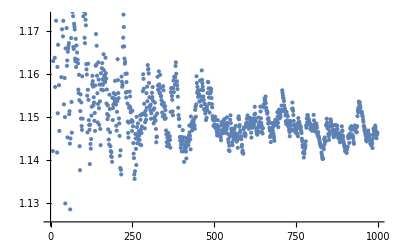

```mathematica
ListPlot[Table[Prime[i]/(i Log[i]),{i,2,1000}]]
```

```mathematica
Prime[Range[100]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Differences[Prime[Range[100]]]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

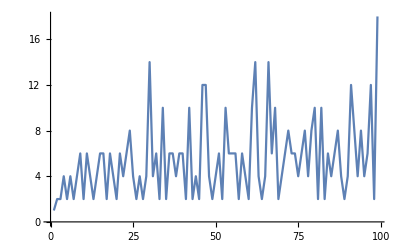

```mathematica
ListLinePlot[Differences[Prime[Range[100]]]]
```

```mathematica
?SoundNote
```

```mathematica
Thread[SoundNote[ConstantArray[0,20],RandomReal[0.5,20]]]
```

{SoundNote[0,0.0637697],SoundNote[0,0.228784],SoundNote[0,0.321372],SoundNote[0,0.377825],SoundNote[0,0.0626728],SoundNote[0,0.0592032],SoundNote[0,0.152241],SoundNote[0,0.407929],SoundNote[0,0.473853],SoundNote[0,0.104116],SoundNote[0,0.0817328],SoundNote[0,0.456962],SoundNote[0,0.399194],SoundNote[0,0.291807],SoundNote[0,0.499861],SoundNote[0,0.197969],SoundNote[0,0.498409],SoundNote[0,0.0164393],SoundNote[0,0.0615986],SoundNote[0,0.382221]}

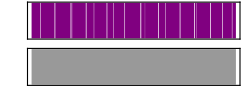

```mathematica
Sound[Thread[SoundNote[ConstantArray[0,20],RandomReal[0.5,20]]]]
```

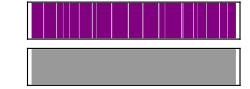
<|Timing→<|SameQ→0.,EqualQ→0.00101,ToCanonicalForm1→0.5000474,ToCanonicalForm2→1.347099,Evaluate1→1.353087,Evaluate2→1.357087,SandboxEquivalentQ→1.549114|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Sound[Table[SoundNote[C,ℛ[UniformDistribution[{0,0.5}]]],{S1∷ℤ,1,20,1}]]],2→HoldComplete[Sound[Thread[SoundNote[Table[0,{S1∷ℤ,1,20,1}],Table[ℛ[UniformDistribution[{0,0.5}]],{S2∷ℤ,1,20,1}]]]]]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→False,EquivalentQ→False|>

```mathematica
EquivalenceTestData[Sound[Table[SoundNote["C",RandomReal[0.5]],20]],Sound[Thread[SoundNote[ConstantArray[0,20],RandomReal[0.5,20]]]]]
```

```mathematica
EquivalenceTestData[Sound[Table[SoundNote["C",RandomReal[0.5]],20]],Sound[Thread[SoundNote[ConstantArray["C",20],RandomReal[0.5,20]]]]]
```

<|Timing→<|SameQ→0.,EqualQ→0.0009819,ToCanonicalForm1→0.0009819,ToCanonicalForm2→0.8229378,Evaluate1→0.8289478,Evaluate2→0.83296,SandboxEquivalentQ→1.020956|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Sound[Table[SoundNote[C,ℛ[UniformDistribution[{0,0.5}]]],{S1∷ℤ,1,20,1}]]],2→HoldComplete[Sound[Thread[SoundNote[Table[C,{S1∷ℤ,1,20,1}],Table[ℛ[UniformDistribution[{0,0.5}]],{S2∷ℤ,1,20,1}]]]]]|>,CanonicalEquivalentQ→False,SandboxForms→<|1→-Graphics-,2→-Graphics-|>,SandboxEquivalentQ→True,EquivalentQ→True|>

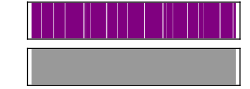

```mathematica
Sound[Thread[SoundNote[ConstantArray["C",20],RandomReal[0.5,20]]]]
```

```mathematica
ArrayPlot[Array[Mod,{50,50}]]
```

-Graphics-

```mathematica
ArrayPlot[Array[Mod[#1^#2,2]&,{50,50}]]
```

-Graphics-

```mathematica
Table[ArrayPlot[Array[Mod[#1^#2,i]&,{50,50}]],{i,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
N[Pi,50]-Round[Pi]
```

0.141592653589793238462643383279502884197169399375

```mathematica
FractionalPart[Pi]
```

-3+π

```mathematica
N[FractionalPart[Pi],50]
```

0.14159265358979323846264338327950288419716939937511

```mathematica
Sum[Prime[i],{i,1000}]
```

3682913

```mathematica
Mod[Prime[Range[100]],4]
```

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

```mathematica
Mod[Prime[Range[10000]],4] 90°
```

```mathematica
AnglePath[Mod[Prime[Range[10000]],4] 90°]
```

```mathematica
Line[AnglePath[Mod[Prime[Range[10000]],4] 90°]]
```

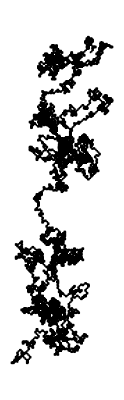

```mathematica
Graphics[Line[AnglePath[Mod[Prime[Range[10000]],4] 90°]]]
```

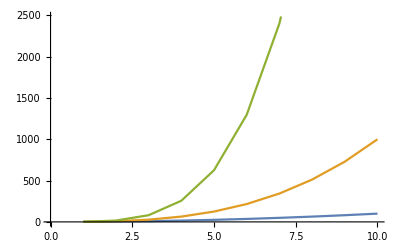

```mathematica
ListLinePlot[Table[Range[10]^i,{i,2,4}]]
```

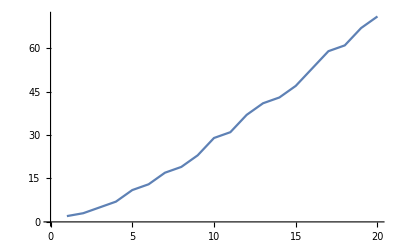

```mathematica
ListLinePlot[Prime[Range[20]]]
```

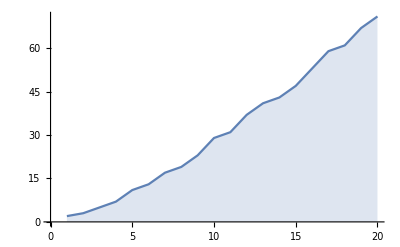

```mathematica
ListLinePlot[Prime[Range[20]],Filling->Bottom]
```

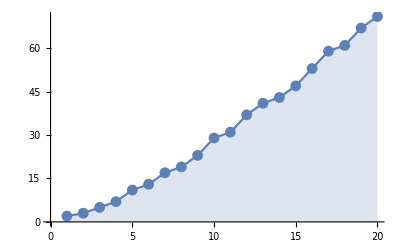

```mathematica
ListLinePlot[Prime[Range[20]],Filling->Bottom,Mesh->All]
```

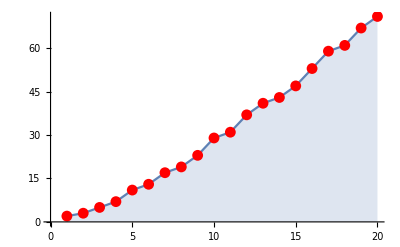

```mathematica
ListLinePlot[Prime[Range[20]],Filling->Bottom,Mesh->All,MeshStyle->Red]
```

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[,Quantity[20, "Miles"]]]]
```

-Graphics-

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[20, "Miles"]]]]
```

-Graphics3D-

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[,Quantity[100, "Miles"]]]]
```

-Graphics-

```mathematica
Table[{i,j,Mod[i,j]},{i,100},{j,100}]
```

```mathematica
ArrayPlot3D[Table[{i,j,Mod[i,j]},{i,100},{j,100}]]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[Table[{i,j,Mod[i,j]},{i,100},{j,100}]]
```

-Graphics3D-

```mathematica
Table[{i,j,Mod[i,j]},{i,100},{j,100}]
```

```mathematica
Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1]
```

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1]]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Web",ViewPoint->Automatic]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,ViewPoint->Automatic]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,ViewPoint->Automatic,PlotTheme->"Minimal"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Marketing"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Monochrome"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->"Default"]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"Business","ZMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"ZMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"DarkMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"GrayMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"LightMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"Business","LightMesh"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"Business","ThickSurface"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[Table[{i,j,Mod[i,j]},{i,100},{j,100}],1],Mesh->All,PlotTheme->{"Business","FilledSurface"}]
```

-Graphics3D-

```mathematica
Differences[Prime[Range[10000]]]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6,6,2,6,12,10,18,2,4,6,2,6,4,2,4,12,2,6,34,6,6,8,18,10,14,4,2,4,6,8,4,2,6,12,10,2,4,2,4,6,12,12,8,12,6,4,6,8,4,8,4,14,4,6,2,4,6,2,6,10,20,6,4,2,24,4,2,10,12,2,10,8,6,6,6,18,6,4,2,12,10,12,8,16,14,6,4,2,4,2,10,12,6,6,18,2,16,2,22,6,8,6,4,2,4,8,6,10,2,10,14,10,6,12,2,4,2,10,12,2,16,2,6,4,2,10,8,18,24,4,6,8,16,2,4,8,16,2,4,8,6,6,4,12,2,22,6,2,6,4,6,14,6,4,2,6,4,6,12,6,6,14,4,6,12,8,6,4,26,18,10,8,4,6,2,6,22,12,2,16,8,4,12,14,10,2,4,8,6,6,4,2,4,6,8,4,2,6,10,2,10,8,4,14,10,12,2,6,4,2,16,14,4,6,8,6,4,18,8,10,6,6,8,10,12,14,4,6,6,2,28,2,10,8,4,14,4,8,12,6,12,4,6,20,10,2,16,26,4,2,12,6,4,12,6,8,4,8,22,2,4,2,12,28,2,6,6,6,4,6,2,12,4,12,2,10,2,16,2,16,6,20,16,8,4,2,4,2,22,8,12,6,10,2,4,6,2,6,10,2,12,10,2,10,14,6,4,6,8,6,6,16,12,2,4,14,6,4,8,10,8,6,6,22,6,2,10,14,4,6,18,2,10,14,4,2,10,14,4,8,18,4,6,2,4,6,2,12,4,20,22,12,2,4,6,6,2,6,22,2,6,16,6,12,2,6,12,16,2,4,6,14,4,2,18,24,10,6,2,10,2,10,2,10,6,2,10,2,10,6,8,30,10,2,10,8,6,10,18,6,12,12,2,18,6,4,6,6,18,2,10,14,6,4,2,4,24,2,12,6,16,8,6,6,18,16,2,4,6,2,6,6,10,6,12,12,18,2,6,4,18,8,24,4,2,4,6,2,12,4,14,30,10,6,12,14,6,10,12,2,4,6,8,6,10,2,4,14,6,6,4,6,2,10,2,16,12,8,18,4,6,12,2,6,6,6,28,6,14,4,8,10,8,12,18,4,2,4,24,12,6,2,16,6,6,14,10,14,4,30,6,6,6,8,6,4,2,12,6,4,2,6,22,6,2,4,18,2,4,12,2,6,4,26,6,6,4,8,10,32,16,2,6,4,2,4,2,10,14,6,4,8,10,6,20,4,2,6,30,4,8,10,6,6,8,6,12,4,6,2,6,4,6,2,10,2,16,6,20,4,12,14,28,6,20,4,18,8,6,4,6,14,6,6,10,2,10,12,8,10,2,10,8,12,10,24,2,4,8,6,4,8,18,10,6,6,2,6,10,12,2,10,6,6,6,8,6,10,6,2,6,6,6,10,8,24,6,22,2,18,4,8,10,30,8,18,4,2,10,6,2,6,4,18,8,12,18,16,6,2,12,6,10,2,10,2,6,10,14,4,24,2,16,2,10,2,10,20,4,2,4,8,16,6,6,2,12,16,8,4,6,30,2,10,2,6,4,6,6,8,6,4,12,6,8,12,4,14,12,10,24,6,12,6,2,22,8,18,10,6,14,4,2,6,10,8,6,4,6,30,14,10,2,12,10,2,16,2,18,24,18,6,16,18,6,2,18,4,6,2,10,8,10,6,6,8,4,6,2,10,2,12,4,6,6,2,12,4,14,18,4,6,20,4,8,6,4,8,4,14,6,4,14,12,4,2,30,4,24,6,6,12,12,14,6,4,2,4,18,6,12,8,6,4,12,2,12,30,16,2,6,22,14,6,10,12,6,2,4,8,10,6,6,24,14,6,4,8,12,18,10,2,10,2,4,6,20,6,4,14,4,2,4,14,6,12,24,10,6,8,10,2,30,4,6,2,12,4,14,6,34,12,8,6,10,2,4,20,10,8,16,2,10,14,4,2,12,6,16,6,8,4,8,4,6,8,6,6,12,6,4,6,6,8,18,4,20,4,12,2,10,6,2,10,12,2,4,20,6,30,6,4,8,10,12,6,2,28,2,6,4,2,16,12,2,6,10,8,24,12,6,18,6,4,14,6,4,12,8,6,12,4,6,12,6,12,2,16,20,4,2,10,18,8,4,14,4,2,6,22,6,14,6,6,10,6,2,10,2,4,2,22,2,4,6,6,12,6,14,10,12,6,8,4,36,14,12,6,4,6,2,12,6,12,16,2,10,8,22,2,12,6,4,6,18,2,12,6,4,12,8,6,12,4,6,12,6,2,12,12,4,14,6,16,6,2,10,8,18,6,34,2,28,2,22,6,2,10,12,2,6,4,8,22,6,2,10,8,4,6,8,4,12,18,12,20,4,6,6,8,4,2,16,12,2,10,8,10,2,4,6,14,12,22,8,28,2,4,20,4,2,4,14,10,12,2,12,16,2,28,8,22,8,4,6,6,14,4,8,12,6,6,4,20,4,18,2,12,6,4,6,14,18,10,8,10,32,6,10,6,6,2,6,16,6,2,12,6,28,2,10,8,16,6,8,6,10,24,20,10,2,10,2,12,4,6,20,4,2,12,18,10,2,10,2,4,20,16,26,4,8,6,4,12,6,8,12,12,6,4,8,22,2,16,14,10,6,12,12,14,6,4,20,4,12,6,2,6,6,16,8,22,2,28,8,6,4,20,4,12,24,20,4,8,10,2,16,2,12,12,34,2,4,6,12,6,6,8,6,4,2,6,24,4,20,10,6,6,14,4,6,6,2,12,6,10,2,10,6,20,4,26,4,2,6,22,2,24,4,6,2,4,6,24,6,8,4,2,34,6,8,16,12,2,10,2,10,6,8,4,8,12,22,6,14,4,26,4,2,12,10,8,4,8,12,4,14,6,16,6,8,4,6,6,8,6,10,12,2,6,6,16,8,6,6,12,10,2,6,18,4,6,6,6,12,18,8,6,10,8,18,4,14,6,18,10,8,10,12,2,6,12,12,36,4,6,8,4,6,2,4,18,12,6,8,6,6,4,18,2,4,2,24,4,6,6,14,30,6,4,6,12,6,20,4,8,4,8,6,6,4,30,2,10,12,8,10,8,24,6,12,4,14,4,6,2,28,14,16,2,12,6,4,20,10,6,6,6,8,10,12,14,10,14,16,14,10,14,6,16,6,8,6,16,20,10,2,6,4,2,4,12,2,10,2,6,22,6,2,4,18,8,10,8,22,2,10,18,14,4,2,4,18,2,4,6,8,10,2,30,4,30,2,10,2,18,4,18,6,14,10,2,4,20,36,6,4,6,14,4,20,10,14,22,6,2,30,12,10,18,2,4,14,6,22,18,2,12,6,4,8,4,8,6,10,2,12,18,10,14,16,14,4,6,6,2,6,4,2,28,2,28,6,2,4,6,14,4,12,14,16,14,4,6,8,6,4,6,6,6,8,4,8,4,14,16,8,6,4,12,8,16,2,10,8,4,6,26,6,10,8,4,6,12,14,30,4,14,22,8,12,4,6,8,10,6,14,10,6,2,10,12,12,14,6,6,18,10,6,8,18,4,6,2,6,10,2,10,8,6,6,10,2,18,10,2,12,4,6,8,10,12,14,12,4,8,10,6,6,20,4,14,16,14,10,8,10,12,2,18,6,12,10,12,2,4,2,12,6,4,8,4,44,4,2,4,2,10,12,6,6,14,4,6,6,6,8,6,36,18,4,6,2,12,6,6,6,4,14,22,12,2,18,10,6,26,24,4,2,4,2,4,14,4,6,6,8,16,12,2,42,4,2,4,24,6,6,2,18,4,14,6,28,18,14,6,10,12,2,6,12,30,6,4,6,6,14,4,2,24,4,6,6,26,10,18,6,8,6,6,30,4,12,12,2,16,2,6,4,12,18,2,6,4,26,12,6,12,4,24,24,12,6,2,12,28,8,4,6,12,2,18,6,4,6,6,20,16,2,6,6,18,10,6,2,4,8,6,6,24,16,6,8,10,6,14,22,8,16,6,2,12,4,2,22,8,18,34,2,6,18,4,6,6,8,10,8,18,6,4,2,4,8,16,2,12,12,6,18,4,6,6,6,2,6,12,10,20,12,18,4,6,2,16,2,10,14,4,30,2,10,12,2,24,6,16,8,10,2,12,22,6,2,16,20,10,2,12,12,18,10,12,6,2,10,2,6,10,18,2,12,6,4,6,2,24,28,2,4,2,10,2,16,12,8,22,2,6,4,2,10,6,20,12,10,8,12,6,6,6,4,18,2,4,12,18,2,12,6,4,2,16,12,12,14,4,8,18,4,12,14,6,6,4,8,6,4,20,12,10,14,4,2,16,2,12,30,4,6,24,20,24,10,8,12,10,12,6,12,12,6,8,16,14,6,4,6,36,20,10,30,12,2,4,2,28,12,14,6,22,8,4,18,6,14,18,4,6,2,6,34,18,2,16,6,18,2,24,4,2,6,12,6,12,10,8,6,16,12,8,10,14,40,6,2,6,4,12,14,4,2,4,2,4,8,6,10,6,6,2,6,6,6,12,6,24,10,2,10,6,12,6,6,14,6,6,52,20,6,10,2,10,8,10,12,12,2,6,4,14,16,8,12,6,22,2,10,8,6,22,2,22,6,8,10,12,12,2,10,6,12,2,4,14,10,2,6,18,4,12,8,18,12,6,6,4,6,6,14,4,2,12,12,4,6,18,18,12,2,16,12,8,18,10,26,4,6,8,6,6,4,2,10,20,4,6,8,4,20,10,2,34,2,4,24,2,12,12,10,6,2,12,30,6,12,16,12,2,22,18,12,14,10,2,12,12,4,2,4,6,12,2,16,18,2,40,8,16,6,8,10,2,4,18,8,10,8,12,4,18,2,18,10,2,4,2,4,8,28,2,6,22,12,6,14,18,4,6,8,6,6,10,8,4,2,18,10,6,20,22,8,6,30,4,2,4,18,6,30,2,4,8,6,4,6,12,14,34,14,6,4,2,6,4,14,4,2,6,28,2,4,6,8,10,2,10,2,10,2,4,30,2,12,12,10,18,12,14,10,2,12,6,10,6,14,12,4,14,4,18,2,10,8,4,8,10,12,18,18,8,6,18,16,14,6,6,10,14,4,6,2,12,12,4,6,6,12,2,16,2,12,6,4,14,6,4,2,12,18,4,36,18,12,12,2,4,2,4,8,12,4,36,6,18,2,12,10,6,12,24,8,6,6,16,12,2,18,10,20,10,2,6,18,4,2,40,6,2,16,2,4,8,18,10,12,6,2,10,8,4,6,12,2,10,18,8,6,4,20,4,6,36,6,2,10,6,24,6,14,16,6,18,2,10,20,10,8,6,4,6,2,10,2,12,4,2,4,8,10,6,12,18,14,12,16,8,6,16,8,4,2,6,18,24,18,10,12,2,4,14,10,6,6,6,18,12,2,28,18,14,16,12,14,24,12,22,6,2,10,8,4,2,4,14,12,6,4,6,14,4,2,4,30,6,2,6,10,2,30,22,2,4,6,8,6,6,16,12,12,6,8,4,2,24,12,4,6,8,6,6,10,2,6,12,28,14,6,4,12,8,6,12,4,6,14,6,12,10,6,6,8,6,6,4,2,4,8,12,4,14,18,10,2,16,6,20,6,10,8,4,30,36,12,8,22,12,2,6,12,16,6,6,2,18,4,26,4,8,18,10,8,10,6,14,4,20,22,18,12,8,28,12,6,6,8,6,12,24,16,14,4,14,12,6,10,12,20,6,4,8,18,12,18,10,2,4,20,10,14,4,6,2,10,24,18,2,4,20,16,14,10,14,6,4,6,20,6,10,6,2,12,6,30,10,8,6,4,6,8,40,2,4,2,12,18,4,6,8,10,6,18,18,2,12,16,8,6,4,6,6,2,52,14,4,20,16,2,4,6,12,2,6,12,12,6,4,14,10,6,6,14,10,14,16,8,6,12,4,8,22,6,2,18,22,6,2,18,6,16,14,10,6,12,2,6,4,8,18,12,16,2,4,14,4,8,12,12,30,16,8,4,2,6,22,12,8,10,6,6,6,14,6,18,10,12,2,10,2,4,26,4,12,8,4,18,8,10,14,16,6,6,8,10,6,8,6,12,10,20,10,8,4,12,26,18,4,12,18,6,30,6,8,6,22,12,2,4,6,6,2,10,2,4,6,6,2,6,22,18,6,18,12,8,12,6,10,12,2,16,2,10,2,10,18,6,20,4,2,6,22,6,6,18,6,14,12,16,2,6,6,4,14,12,4,2,18,16,36,12,6,14,28,2,12,6,12,6,4,2,16,30,8,24,6,30,10,2,18,4,6,12,8,22,2,6,22,18,2,10,2,10,30,2,28,6,14,16,6,20,16,2,6,4,32,4,2,4,6,2,12,4,6,6,12,2,6,4,6,8,6,4,20,4,32,10,8,16,2,22,2,4,6,8,6,16,14,4,18,8,4,20,6,12,12,6,10,2,10,2,12,28,12,18,2,18,10,8,10,48,2,4,6,8,10,2,10,30,2,36,6,10,6,2,18,4,6,8,16,14,16,6,14,4,20,4,6,2,10,12,2,6,12,6,6,4,12,2,6,4,12,6,8,4,2,6,18,10,6,8,12,6,22,2,6,12,18,4,14,6,4,20,6,16,8,4,8,22,8,12,6,6,16,12,18,30,8,4,2,4,6,26,4,14,24,22,6,2,6,10,6,14,6,6,12,10,6,2,12,10,12,8,18,18,10,6,8,16,6,6,8,16,20,4,2,10,2,10,12,6,8,6,10,20,10,18,26,4,6,30,2,4,8,6,12,12,18,4,8,22,6,2,12,34,6,18,12,6,2,28,14,16,14,4,14,12,4,6,6,2,36,4,6,20,12,24,6,22,2,16,18,12,12,18,2,6,6,6,4,6,14,4,2,22,8,12,6,10,6,8,12,18,12,6,10,2,22,14,6,6,4,18,6,20,22,2,12,24,4,18,18,2,22,2,4,12,8,12,10,14,4,2,18,16,38,6,6,6,12,10,6,12,8,6,4,6,14,30,6,10,8,22,6,8,12,10,2,10,2,6,10,2,10,12,18,20,6,4,8,22,6,6,30,6,14,6,12,12,6,10,2,10,30,2,16,8,4,2,6,18,4,2,6,4,26,4,8,6,10,2,4,6,8,4,6,30,12,2,6,6,4,20,22,8,4,2,4,72,8,4,8,22,2,4,14,10,2,4,20,6,10,18,6,20,16,6,8,6,4,20,12,22,2,4,2,12,10,18,2,22,6,18,30,2,10,14,10,8,16,50,6,10,8,10,12,6,18,2,22,6,2,4,6,8,6,6,10,18,2,22,2,16,14,10,6,2,12,10,20,4,14,6,4,36,2,4,6,12,2,4,14,12,6,4,6,2,6,4,20,10,2,10,6,12,2,24,12,12,6,6,4,24,2,4,24,2,6,4,6,8,16,6,2,10,12,14,6,34,6,14,6,4,2,30,22,8,4,6,8,4,2,28,2,6,4,26,18,22,2,6,16,6,2,16,12,2,12,4,6,6,14,10,6,8,12,4,18,2,10,8,16,6,6,30,2,10,18,2,10,8,4,8,12,24,40,2,12,10,6,12,2,12,4,2,4,6,18,14,12,6,4,14,30,4,8,10,8,6,10,18,8,4,14,16,6,8,4,6,2,10,2,12,4,2,4,6,8,4,6,32,24,10,8,18,10,2,6,10,2,4,18,6,12,2,16,2,22,6,6,8,18,4,18,12,8,6,4,20,6,30,22,12,2,6,18,4,62,4,2,12,6,10,2,12,12,28,2,4,14,22,6,2,6,6,10,14,4,2,10,6,8,10,14,10,6,2,12,22,18,8,10,18,12,2,12,4,12,2,10,2,6,18,6,6,34,6,2,12,4,6,18,18,2,16,6,6,8,6,10,18,8,10,8,10,2,4,18,26,12,22,2,4,2,22,6,6,14,16,6,20,10,12,2,18,42,4,24,2,6,10,12,2,6,10,8,4,6,12,12,8,4,6,12,30,20,6,24,6,10,12,2,10,20,6,6,4,12,14,10,18,12,8,6,12,4,14,10,2,12,30,16,2,12,6,4,2,4,6,26,4,18,2,4,6,14,54,6,52,2,16,6,6,12,26,4,2,6,22,6,2,12,12,6,10,18,2,12,12,10,18,12,6,8,6,10,6,8,4,2,4,20,24,6,6,10,14,10,2,22,6,14,10,26,4,18,8,12,12,10,12,6,8,16,6,8,6,6,22,2,10,20,10,6,44,18,6,10,2,4,6,14,4,26,4,2,12,10,8,4,8,12,4,12,8,22,8,6,10,18,6,6,8,6,12,4,8,18,10,12,6,12,2,6,4,2,16,12,12,14,10,14,6,10,12,2,12,6,4,6,2,12,4,26,6,18,6,10,6,2,18,10,8,4,26,10,20,6,16,20,12,10,8,10,2,16,6,20,10,20,4,30,2,4,8,16,2,18,4,2,6,10,18,12,14,18,6,16,20,6,4,8,6,4,6,12,8,10,2,12,6,4,2,6,10,2,16,12,14,10,6,8,6,28,2,6,18,30,34,2,16,12,2,18,16,6,8,10,8,10,8,10,44,6,6,4,20,4,2,4,14,28,8,6,16,14,30,6,30,4,14,10,6,6,8,4,18,12,6,2,22,12,8,6,12,4,14,4,6,2,4,18,20,6,16,38,16,2,4,6,2,40,42,14,4,6,2,24,10,6,2,18,10,12,2,16,2,6,16,6,8,4,2,10,6,8,10,2,18,16,8,12,18,12,6,12,10,6,6,18,12,14,4,2,10,20,6,12,6,16,26,4,18,2,4,32,10,8,6,4,6,6,14,6,18,4,2,18,10,8,10,8,10,2,4,6,2,10,42,8,12,4,6,18,2,16,8,4,2,10,14,12,10,20,4,8,10,38,4,6,2,10,20,10,12,6,12,26,12,4,8,28,8,4,8,24,6,10,8,6,16,12,8,10,12,8,22,6,2,10,2,6,10,6,6,8,6,4,14,28,8,16,18,8,4,6,20,4,18,6,2,24,24,6,6,12,12,4,2,22,2,10,6,8,12,4,20,18,6,4,12,24,6,6,54,8,6,4,26,36,4,2,4,26,12,12,4,6,6,8,12,10,2,12,16,18,6,8,6,12,18,10,2,54,4,2,10,30,12,8,4,8,16,14,12,6,4,6,12,6,2,4,14,12,4,14,6,24,6,6,10,12,12,20,18,6,6,16,8,4,6,20,4,32,4,14,10,2,6,12,16,2,4,6,12,2,10,8,6,4,2,10,14,6,6,12,18,34,8,10,6,24,6,2,10,12,2,30,10,14,12,12,16,6,6,2,18,4,6,30,14,4,6,6,2,6,4,6,14,6,4,8,10,12,6,32,10,8,22,2,10,6,24,8,4,30,6,2,12,16,8,6,4,6,8,16,14,6,6,4,2,10,12,2,16,14,4,2,4,20,18,10,2,10,6,12,30,8,18,12,10,2,6,6,4,12,12,2,4,12,18,24,2,10,6,8,16,8,6,12,10,14,6,12,6,6,4,2,24,4,6,8,6,4,2,4,6,14,4,8,10,24,24,12,2,6,12,22,30,2,6,18,10,6,6,8,4,2,6,10,8,10,6,8,16,6,14,6,4,24,8,10,2,12,6,4,36,2,22,6,8,6,10,8,6,12,10,14,10,6,18,12,2,12,4,26,10,14,16,18,8,18,12,12,6,16,14,24,10,12,8,22,6,2,10,60,6,2,4,8,16,14,10,6,24,6,12,18,24,2,30,4,2,12,6,10,2,4,14,6,16,2,10,8,22,20,6,4,32,6,18,4,2,4,2,4,8,52,14,22,2,22,20,10,8,10,2,6,4,14,4,6,20,4,6,2,12,12,6,12,16,2,12,10,8,4,6,2,28,12,8,10,12,2,4,14,28,8,6,4,2,4,6,2,12,58,6,14,10,2,6,28,32,4,30,8,6,4,6,12,12,2,4,6,6,14,16,8,30,4,2,10,8,6,4,6,26,4,12,2,10,18,12,12,18,2,4,12,8,12,10,20,4,8,16,12,8,6,16,8,10,12,14,6,4,8,12,4,20,6,40,8,16,6,36,2,6,4,6,2,22,18,2,10,6,36,14,12,4,18,8,4,14,10,2,10,8,4,2,18,16,12,14,10,14,6,6,42,10,6,6,20,10,8,12,4,12,18,2,10,14,18,10,18,8,6,4,14,6,10,30,14,6,6,4,12,38,4,2,4,6,8,12,10,6,18,6,50,6,4,6,12,8,10,32,6,22,2,10,12,18,2,6,4,30,8,6,6,18,10,2,4,12,20,10,8,24,10,2,6,22,6,2,18,10,12,2,30,18,12,28,2,6,4,6,14,6,12,10,8,4,12,26,10,8,6,16,2,10,18,14,6,4,6,14,16,2,6,4,12,20,4,20,4,6,12,2,36,4,6,2,10,2,22,8,6,10,12,12,18,14,24,36,4,20,24,10,6,2,28,6,18,8,4,6,8,6,4,2,12,28,18,14,16,14,18,10,8,6,4,6,6,8,22,12,2,10,18,6,2,18,10,2,12,10,18,32,6,4,6,6,8,6,6,10,20,6,12,10,8,10,14,6,10,14,4,2,22,18,2,10,2,4,20,4,2,34,2,12,6,10,2,10,18,6,14,12,12,22,8,6,16,6,8,4,12,6,8,4,36,6,6,20,24,6,12,18,10,2,10,26,6,16,8,6,4,24,18,8,12,12,10,18,12,2,24,4,12,18,12,14,10,2,4,24,12,14,10,6,2,6,4,6,26,4,6,6,2,22,8,18,4,18,8,4,24,2,12,12,4,2,52,2,18,6,4,6,12,2,6,12,10,8,4,2,24,10,2,10,2,12,6,18,40,6,20,16,2,12,6,10,12,2,4,6,14,12,12,22,6,8,4,2,16,18,12,2,6,16,6,2,6,4,12,30,8,16,2,18,10,24,2,6,24,4,2,22,2,16,2,6,12,4,18,8,4,14,4,18,24,6,2,6,10,2,10,38,6,10,14,6,6,24,4,2,12,16,14,16,12,2,6,10,26,4,2,12,6,4,12,8,12,10,18,6,14,28,2,6,10,2,4,14,34,2,6,22,2,10,14,4,2,16,8,10,6,8,10,8,4,6,2,16,6,6,18,30,14,6,4,30,2,10,14,4,20,10,8,4,8,18,4,14,6,4,24,6,6,18,18,2,36,6,10,14,12,4,6,2,30,6,4,2,6,28,20,4,20,12,24,16,18,12,14,6,4,12,32,12,6,10,8,10,6,18,2,16,14,6,22,6,12,2,18,4,8,30,12,4,12,2,10,38,22,2,4,14,6,12,24,4,2,4,14,12,10,2,16,6,20,4,20,22,12,2,4,2,12,22,24,6,6,2,6,4,6,2,10,12,12,6,2,6,16,8,6,4,18,12,12,14,4,12,6,8,6,18,6,10,12,14,6,4,8,22,6,2,28,18,2,18,10,6,14,10,2,10,14,6,10,2,22,6,8,6,16,12,8,22,2,4,14,18,12,6,24,6,10,2,12,22,18,6,20,6,10,14,4,2,6,12,22,14,12,4,6,8,22,2,10,12,8,40,2,6,10,8,4,42,20,4,32,12,10,6,12,12,2,10,8,6,4,8,4,26,18,4,8,28,6,18,6,12,2,10,6,6,14,10,12,14,24,6,4,20,22,2,18,4,6,12,2,16,18,14,6,6,4,6,8,18,4,14,30,4,18,8,10,2,4,8,12,4,12,18,2,12,10,2,16,8,4,30,2,6,28,2,10,2,18,10,14,4,26,6,18,4,20,6,4,8,18,4,12,26,24,4,20,22,2,18,22,2,4,12,2,6,6,6,4,6,14,4,24,12,6,18,2,12,28,14,4,6,8,22,6,12,18,8,4,20,6,4,6,2,18,6,4,12,12,8,28,6,8,10,2,24,12,10,24,8,10,20,12,6,12,12,4,14,12,24,34,18,8,10,6,18,8,4,8,16,14,6,4,6,24,2,6,4,6,2,16,6,6,20,24,4,2,4,14,4,18,2,6,12,4,14,4,2,18,16,6,6,2,16,20,6,6,30,4,8,6,24,16,6,6,8,12,30,4,18,18,8,4,26,10,2,22,8,10,14,6,4,18,8,12,28,2,6,4,12,6,24,6,8,10,20,16,8,30,6,6,4,2,10,14,6,10,32,22,18,2,4,2,4,8,22,8,18,12,28,2,16,12,18,14,10,18,12,6,32,10,14,6,10,2,10,2,6,22,2,4,6,8,10,6,14,6,4,12,30,24,6,6,8,6,4,2,4,6,8,6,6,22,18,8,4,2,18,6,4,2,16,18,20,10,6,6,30,2,12,28,6,6,6,2,12,10,8,18,18,4,8,18,10,2,28,2,10,14,4,2,30,12,22,26,10,8,6,10,8,16,14,6,6,10,14,6,4,2,10,12,2,6,10,8,4,2,10,26,22,6,2,12,18,4,26,4,8,10,6,14,10,2,18,6,10,20,6,6,4,24,2,4,8,6,16,14,16,18,2,4,12,2,10,2,6,12,10,6,6,20,6,4,6,38,4,6,12,14,4,12,8,10,12,12,8,4,6,14,10,6,12,2,10,18,2,18,10,8,10,2,12,4,14,28,2,16,2,18,6,10,6,8,16,14,30,10,20,6,10,24,2,28,2,12,16,6,8,36,4,8,4,14,12,10,8,12,4,6,8,4,6,14,22,8,6,4,2,10,6,20,10,8,6,6,22,18,2,16,6,20,4,26,4,14,22,14,4,12,6,8,4,6,6,26,10,2,18,18,4,2,16,2,18,4,6,8,4,6,12,2,6,6,28,38,4,8,16,26,4,2,10,12,2,10,8,6,10,12,2,10,2,24,4,30,26,6,6,18,6,6,22,2,10,18,26,4,18,8,6,6,12,16,6,8,16,6,8,16,2,42,58,8,4,6,2,4,8,16,6,20,4,12,12,6,12,2,10,2,6,22,2,10,6,8,6,10,14,6,6,4,18,8,10,8,16,14,10,2,10,2,12,6,4,20,10,8,52,8,10,6,2,10,8,10,6,6,8,10,2,22,2,4,6,14,4,2,24,12,4,26,18,4,6,14,30,6,4,6,2,22,8,4,6,2,22,6,8,16,6,14,4,6,18,8,12,6,12,24,30,16,8,34,8,22,6,14,10,18,14,4,12,8,4,36,6,6,2,10,2,4,20,6,6,10,12,6,2,40,8,6,28,6,2,12,18,4,24,14,6,6,10,20,10,14,16,14,16,6,8,36,4,12,12,6,12,50,12,6,4,6,6,8,6,10,2,10,2,18,10,14,16,8,6,4,20,4,2,10,6,14,18,10,38,10,18,2,10,2,12,4,2,4,14,6,10,8,40,6,20,4,12,8,6,34,8,22,8,12,10,2,16,42,12,8,22,8,22,8,6,34,2,6,4,14,6,16,2,22,6,8,24,22,6,2,12,4,6,14,4,8,24,4,6,6,2,22,20,6,4,14,4,6,6,8,6,10,6,8,6,16,14,6,6,22,6,24,32,6,18,6,18,10,8,30,18,6,16,12,6,12,2,6,4,12,8,6,22,8,6,4,14,10,18,20,10,2,6,4,2,28,18,2,10,6,6,6,14,40,24,2,4,8,12,4,20,4,32,18,16,6,36,8,6,4,6,14,4,6,26,6,10,14,18,10,6,6,14,10,6,6,14,6,24,4,14,22,8,12,10,8,12,18,10,18,8,24,10,8,4,24,6,18,6,2,10,30,2,10,2,4,2,40,2,28,8,6,6,18,6,10,14,4,18,30,18,2,12,30,6,30,4,18,12,2,4,14,6,10,6,8,6,10,12,2,6,12,10,2,18,4,20,4,6,14,6,6,22,6,6,8,18,18,10,2,10,2,6,4,6,12,18,2,10,8,4,18,2,6,6,6,10,8,10,6,18,12,8,12,6,4,6,14,16,2,12,4,6,38,6,6,16,20,28,20,10,6,6,14,4,26,4,14,10,18,14,28,2,4,14,16,2,28,6,8,6,34,8,4,18,2,16,8,6,40,8,18,4,30,6,12,2,30,6,10,14,40,14,10,2,12,10,8,4,8,6,6,28,2,4,12,14,16,8,30,16,18,2,10,18,6,32,4,18,6,2,12,10,18,2,6,10,14,18,28,6,8,16,2,4,20,10,8,18,10,2,10,8,4,6,12,6,20,4,2,6,4,20,10,26,18,10,2,18,6,16,14,4,26,4,14,10,12,14,6,6,4,14,10,2,30,18,22,2,16,2,4,8,6,6,16,2,6,12,10,8,12,4,14,4,6,20,10,12,2,6,6,4,2,10,2,30,16,12,20,18,4,6,2,4,8,16,14,18,22,6,2,22,6,6,18,2,10,36,8,4,6,20,4,12,6,14,4,2,28,24,8,4,6,12,30,18,32,22,8,36,6,4,12,2,12,4,6,20,10,18,18,8,6,4,24,8,10,14,6,4,8,12,16,2,16,6,8,16,12,14,10,30,14,4,12,8,12,6,10,2,12,28,6,12,12,20,10,2,10,14,6,6,30,4,8,12,4,2,10,14,4,26,18,12,10,6,8,4,12,6,24,18,8,10,2,12,4,12,12,6,2,22,2,4,2,12,16,14,10,2,16,18,32,4,6,20,22,8,10,2,10,6,2,4,14,6,24,4,8,4,6,12,12,8,6,10,12,8,10,2,10,12,6,12,12,20,28,20,10,14,10,8,10,6,2,4,14,6,6,12,6,12,10,14,10,14,16,8,10,26,4,2,6,4,14,4,6,12,8,6,30,18,12,6,12,16,12,12,2,28,6,14,10,36,2,4,6,8,12,22,18,2,30,18,22,20,18,10,38,6,4,2,24,4,6,6,2,10,6,14,10,8,4,24,14,16,14,22,6,20,10,14,4,12,12,2,16,8,6,6,18,4,6,14,22,6,2,42,16,2,10,6,2,4,6,8,10,20,16,30,8,10,8,10,2,30,6,6,36,10,8,16,6,2,12,28,2,4,6,18,12,6,8,10,2,4,50,4,20,4,30,8,4,6,12,2,24,4,8,18,6,4,6,8,10,2,4,2,40,18,36,30,30,8,16,14,6,12,28,2,22,2,4,12,30,12,6,2,4,14,10,2,18,22,12,18,2,10,18,32,6,4,2,6,10,20,12,10,6,12,20,12,6,4,2,16,2,16,6,14,4,2,16,2,6,16,6,8,4,8,22,18,8,12,4,8,6,24,22,6,2,12,30,6,10,12,6,2,22,6,2,12,6,22,8,12,22,2,10,6,18,12,2,6,12,18,6,4,20,22,8,12,24,16,14,10,30,18,2,6,4,14,10,2,12,10,12,6,2,16,12,2,6,12,10,2,10,6,2,12,12,16,20,10,12,8,30,10,14,4,6,8,6,4,20,18,24,4,12,8,4,2,24,6,24,10,2,4,6,2,6,6,6,4,24,2,10,12,2,6,10,8,6,10,18,2,6,4,20,24,10,12,2,12,6,24,4,36,14,16,8,22,6,8,4,2,6,22,20,16,12,18,2,12,16,6,6,12,6,12,2,6,12,10,8,16,8,6,16,8,12,4,6,6,20,12,12,4,6,20,4,12,2,10,2,6,30,22,6,2,4,38,10,2,4,2,22,2,16,2,6,10,20,6,24,4,12,14,12,4,38,10,30,6,2,12,12,4,6,30,14,4,8,18,36,4,6,20,4,2,12,10,2,6,10,12,6,12,8,6,6,24,4,30,20,6,36,10,2,12,6,4,8,6,4,12,8,6,12,4,6,14,4,20,12,4,6,18,2,4,18,2,16,12,30,6,6,8,40,8,48,6,16,18,14,12,6,18,4,20,10,2,6,10,8,30,4,12,20,6,12,6,6,34,6,6,18,6,8,10,12,6,8,10,2,4,24,6,8,22,6,2,12,6,10,12,6,24,6,14,12,36,4,24,2,10,8,10,6,14,10,32,4,8,10,12,26,18,4,6,20,4,20,6,16,6,2,30,12,6,10,2,6,10,12,8,4,2,6,10,12,26,22,8,6,4,14,6,6,30,4,6,14,4,2,28,2,6,22,8,4,18,18,18,2,12,6,4,20,10,6,6,14,10,12,2,12,30,34,12,8,6,4,2,10,2,16,12,2,10,8,18,24,6,4,12,14,4,8,4,14,4,6,6,20,6,4,8,18,52,2,4,12,8,4,38,4,26,24,16,12,6,2,12,12,16,2,6,6,4,12,14,16,8,12,18,16,6,8,10,6,14,10,12,2,10,2,4,24,6,42,24,8,10,6,6,6,2,12,4,14,6,6,28,6,2,10,12,12,6,20,4,6,14,4,2,12,10,12,24,6,8,6,6,4,24,12,20,16,14,30,18,6,4,26,12,4,6,2,6,4,2,28,8,40,2,10,8,4,20,6,18,10,2,4,44,6,18,12,6,4,6,2,22,6,14,30,10,24,2,10,8,16,18,2,18,22,8,10,6,6,14,4,8,18,4,2,18,18,18,6,4,24,18,2,16,6,6,18,20,16,20,4,14,6,4,20,18,10,2,6,10,24,2,10,24,6,6,24,6,12,2,28,12,14,6,6,12,6,22,12,12,8,36,4,12,14,4,20,10,12,24,2,4,6,12,2,4,2,10,12,26,6,16,8,4,8,10,8,6,34,2,12,16,24,6,2,10,2,18,4,8,6,16,6,2,6,6,6,4,14,4,20,6,4,20,6,12,22,6,2,10,12,2,6,4,8,12,4,14,12,10,14,4,12,26,10,14,4,26,6,30,4,18,18,8,6,16,8,10,14,10,8,10,20,22,20,16,2,18,6,4,6,6,12,2,10,26,4,8,18,18,6,18,6,4,6,24,6,20,34,26,10,2,28,12,8,10,12,2,6,22,2,12,16,2,6,6,10,14,16,20,6,4,38,6,10,6,8,16,42,2,6,4,6,6,6,14,16,14,4,20,10,2,4,8,18,10,12,36,2,10,42,8,4,20,24,16,8,22,6,8,4,2,6,22,6,6,8,28,2,10,18,14,6,4,18,8,10,14,4,12,8,10,12,14,4,2,12,12,4,6,18,30,12,38,6,12,10,2,18,10,12,8,4,8,6,4,2,24,12,18,4,2,4,2,58,12,8,24,10,2,4,6,6,12,2,4,14,6,6,16,12,2,4,32,4,24,6,6,8,10,2,22,18,12,20,6,30,4,30,6,2,4,14,6,4,14,16,2,12,10,2,6,12,12,10,6,8,22,8,12,12,6,16,6,18,20,22,18,2,22,2,16,2,22,14,10,20,10,32,4,8,10,6,2,22,6,12,2,6,4,2,4,14,12,24,10,2,12,16,2,4,6,14,6,10,12,2,16,14,34,12,2,6,6,6,4,20,10,26,12,12,4,2,4,8,10,2,4,2,22,6,6,14,4,18,12,26,6,10,8,16,2,4,20,10,6,42,2,10,6,8,24,12,6,4,6,12,2,28,8,12,18,18,6,46,8,10,6,14,4,2,6,4,6,42,8,10,8,10,2,18,4,6,12,12,2,4,20,10,12,12,8,4,26,18,22,8,6,16,14,16,2,18,10,2,6,6,10,14,4,2,30,4,2,4,8,10,6,2,12,16,6,56,10,2,12,10,8,12,6,4,14,10,2,4,8,6,4,20,6,12,22,6,32,10,2,10,12,14,6,28,36,6,6,2,12,4,6,6,8,22,2,18,10,2,6,4,20,10,8,4,6,14,18,6,42,22,2,4,2,28,2,4,18,6,6,6,12,2,24,10,36,6,2,12,10,26,24,18,16,6,6,14,24,12,4,8,6,12,4,8,16,20,40,26,4,12,2,6,4,2,10,14,10,2,4,26,12,28,2,16,26,6,10,2,6,10,6,8,6,6,6,10,12,6,20,40,20,4,2,16,12,6,12,8,4,18,2,12,10,26,12,16,2,18,24,12,4,14,22,20,10,14,12,4,18,12,8,10,12,6,30,14,4,24,6,30,6,6,2,6,22,32,6,4,6,6,20,16,2,10,8,12,10,2,6,10,8,16,36,8,6,4,2,28,2,28,12,2,10,6,14,10,6,6,6,8,6,4,14,18,4,6,12,2,10,18,8,30,40,2,18,4,6,14,18,6,4,12,6,12,6,14,10,26,6,16,2,16,30,2,10,2,42,6,28,14,6,10,2,12,18,12,6,10,12,12,20,6,4,2,10,6,12,12,14,12,34,6,2,12,10,6,8,6,4,12,38,6,10,18,2,28,2,6,12,30,16,2,10,8,4,2,16,18,26,4,6,8,18,22,6,20,4,6,12,2,6,12,4,18,6,2,22,12,8,6,16,18,30,12,24,2,10,2,6,6,4,6,36,14,6,22,2,58,8,12,6,10,2,40,8,6,28,2,4,14,6,6,18,10,8,4,14,4,8,30,4,6,8,6,6,18,4,2,4,14,12,18,10,2,4,12,2,10,8,10,14,10,18,12,8,6,10,14,10,8,22,2,6,22,12,6,8,12,28,2,48,12,4,18,8,10,14,10,14,4,12,30,24,6,8,6,4,8,54,4,2,10,12,8,10,12,12,18,2,24,4,8,22,12,20,4,12,2,12,16,2,28,2,6,24,10,2,28,2,4,20,4,12,6,14,4,6,14,22,24,20,4,14,6,6,10,30,8,10,18,2,6,6,16,2,6,6,4,2,24,4,2,24,10,6,2,10,2,6,22,8,4,8,6,4,18,2,18,4,8,16,26,4,6,8,22,20,16,8,4,6,24,6,14,12,16,2,12,4,14,10,2,4,12,18,32,10,14,24,12,40,8,34,12,14,4,18,2,28,12,20,6,10,2,40,18,14,12,4,36,6,2,22,6,14,10,24,42,2,16,2,34,8,6,4,2,4,14,40,8,12,6,24,18,4,6,2,6,4,2,4,2,24,10,8,6,6,10,14,6,16,18,14,18,24,4,6,6,8,4,20,10,6,12,2,12,4,14,6,6,6,4,14,16,36,14,6,4,14,4,6,24,8,4,20,10,14,12,34,8,10,6,6,6,14,4,14,12,6,10,18,14,10,12,6,2,6,6,28,2,4,24,6,2,4,8,16,6,20,4,2,10,2,10,8,64,6,8,12,4,14,12,10,2,12,6,10,18,24,6,2,10,8,6,16,20,4,14,6,6,12,6,4,6,2,4,8,22,6,8,4,2,16,18,14,6,22,14,10,14,4,6,2,4,14,10,12,8,16,8,10,8,24,40,6,12,2,6,18,4,2,4,30,2,30,4,8,18,12,12,4,2,4,14,36,16,18,2,12,10,6,12,18,2,18,6,6,22,18,38,6,10,18,2,10,8,6,16,24,14,6,4,6,14,16,24,6,12,8,12,10,14,46,2,16,2,22,6,2,10,2,10,2,6,4,20,10,6,30,8,6,6,4,30,8,6,6,6,22,36,2,4,8,6,6,4,14,12,10,20,4,2,4,30,6,14,16,12,30,2,4,6,8,30,10,8,34,18,12,8,22,20,4,14,10,20,6,4,2,10,14,4,26,6,36,12,18,4,8,6,4,6,2,28,6,6,24,8,10,26,6,24,4,8,24,10,20,4,2,10,14,16,2,6,6,4,6,8,18,28,14,6,16,14,6,4,6,6,8,4,2,4,12,2,12,6,12,28,2,6,12,10,14,4,44,6,10,2,12,12,30,4,12,2,6,10,12,2,10,2,10,6,8,10,6,14,16,8,6,12,10,2,10,8,12,10,18,8,4,2,4,26,6,22,6,14,10,6,2,28,6,8,46,6,6,18,6,6,8,6,10,18,2,6,12,18,10,8,12,30,10,2,10,2,4,6,18,2,4,20,12,4,6,8,34,6,6,24,12,8,36,16,2,6,4,2,4,6,20,6,24,4,2,4,18,20,6,22,8,46,18,2,16,20,22,2,24,22,2,16,24,20,16,2,4,8,10,2,10,14,4,8,18,4,8,4,14,10,2,24,16,8,6,16,20,10,2,6,4,30,2,16,32,6,12,10,24,8,12,18,16,2,12,6,4,12,6,2,28,18,2,22,6,6,6,2,6,16,14,6,30,16,2,10,2,4,12,2,12,10,14,6,10,8,28,2,36,6,16,14,4,20,24,6,4,8,4,18,8,4,14,4,6,2,24,16,14,4,26,16,2,10,32,6,4,6,12,6,36,8,12,4,2,4,8,6,4,20,12,10,24,12,2,12,10,6,12,2,6,18,4,6,6,6,8,24,6,10,12,30,14,10,8,12,6,10,12,2,18,6,4,8,4,24,20,4,8,10,12,8,12,16,6,14,4,8,4,18,50,6,6,4,6,8,6,10,26,10,6,2,10,2,10,6,38,12,4,8,10,20,6,6,6,18,10,2,12,16,2,12,12,4,26,10,6,20,18,40,12,8,10,12,2,18,12,10,2,10,26,4,6,12,8,4,30,6,2,6,16,24,24,18,12,12,8,6,4,8,10,8,6,4,20,10,26,4,24,6,2,12,42,18,6,4,26,6,28,6,2,10,8,6,6,10,8,10,2,22,2,4,20,4,6,36,14,4,20,22,6,14,6,10,8,4,2,4,14,18,34,8,22,14,10,24,6,2,10,2,6,10,26,18,10,18,24,18,2,24,40,2,4,6,2,6,10,26,6,12,12,6,4,36,2,10,12,24,2,4,8,10,6,2,4,24,2,4,36,2,22,14,24,18,42,6,10,2,24,16,12,2,4,2,10,2,10,8,4,36,8,4,12,18,6,6,14,22,2,6,24,6,10,24,20,22,6,14,36,28,6,8,6,24,6,12,28,2,18,4,2,4,20,22,8,10,2,18,4,8,10,14,10,6,8,6,6,12,16,12,14,10,18,2,10,24,24,6,12,2,22,6,20,22,2,4,12,2,6,36,6,22,6,2,28,12,18,2,4,14,6,4,2,10,2,16,2,10,8,6,10,18,12,6,14,4,6,18,12,26,4,6,14,6,10,12,2,4,2,10,24,8,10,32,10,8,10,6,2,18,12,28,30,2,18,4,6,14,6,4,8,22,8,30,18,10,26,4,2,22,8,4,8,6,4,26,4,12,20,18,6,12,10,18,2,4,6,2,12,28,6,20,6,16,8,6,6,4,6,20,12,6,4,20,6,16,6,32,10,18,2,12,16,24,6,8,12,34,6,20,22,2,16,14,6,4,14,6,24,30,4,8,12,6,16,20,10,14,4,2,16,12,2,10,8,6,30,12,10,14,10,8,10,6,2,4,14,10,2,10,32,18,4,8,28,20,4,20,6,4,30,8,6,22,18,12,2,10,12,6,18,6,54,6,14,4,6,6,14,24,6,12,10,12,6,24,12,18,8,18,4,2,4,2,22,8,10,2,12,10,14,6,4,2,12,46,6,6,2,6,6,30,10,8,6,12,4,14,6,16,12,8,10,20,18,10,6,6,12,2,10,14,4,2,4,24,12,8,18,4,8,16,14,12,10,18,12,8,18,4,14,4,6,2,22,18,8,10,26,4,2,24,6,4,6,12,26,4,8,10,18,6,14,10,12,2,12,6,4,8,12,16,2,10,6,2,22,2,4,14,18,10,12,20,10,6,2,4,14,12,4,8,10,2,6,34,6,2,16,12,8,22,8,30,10,2,24,4,14,10,20,16,2,4,20,10,6,8,4,8,4,24,6,14,4,32,4,6,14,6,4,2,22,60,2,6,24,4,14,18,12,18,12,6,4,30,2,16,2,22,14,16,18,6,36,6,18,2,10,8,4,2,6,24,18,30,6,6,34,14,6,52,2,16,12,14,16,8,30,4,2,6,10,12,2,28,6,14,12,28,18,20,4,8,6,6,4,6,8,22,6,24,8,6,12,12,6,12,4,20,46,18,14,10,2,24,4,2,24,22,14,10,6,32,12,4,2,10,2,10,2,4,6,6,12,12,14,6,6,28,2,18,6,6,4,24,2,12,12,6,4,24,24,2,6,4,38,6,10,12,2,12,4,20,22,12,2,10,6,18,42,12,2,6,12,22,14,10,6,6,2,10,18,14,4,26,16,12,8,18,4,2,10,8,6,4,6,6,6}

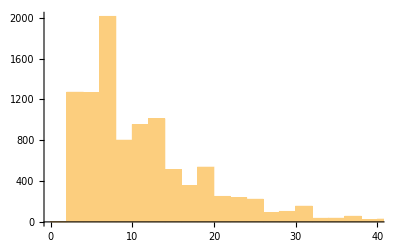

```mathematica
Histogram[Differences[Prime[Range[10000]]]]
```

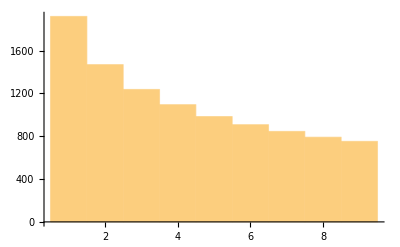

```mathematica
Histogram[First[IntegerDigits[#]]&/@(Range[10000]^2)]
```

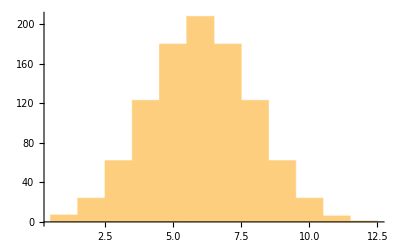

```mathematica
Histogram[StringLength[RomanNumeral[Range[1000]]]]
```

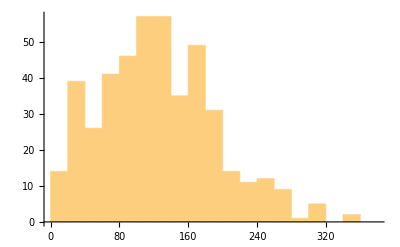

```mathematica
Histogram@StringLength@TextSentences[WikipediaData["computers"]]
```

```mathematica
RandomReal[100,{1,10}]
```

{{37.6103,18.395,50.9089,49.8949,35.8857,99.5978,77.5502,27.2117,31.2335,98.138}}

```mathematica
Total/@RandomReal[100,{1,10}]
```

{520.934}

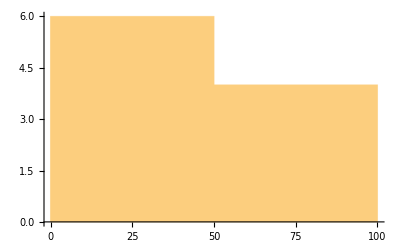

```mathematica
Histogram[Total/@RandomReal[100,{10,1}]]
```

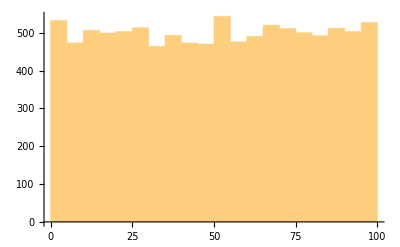

```mathematica
Histogram[Total/@RandomReal[100,{10000,1}]]
```

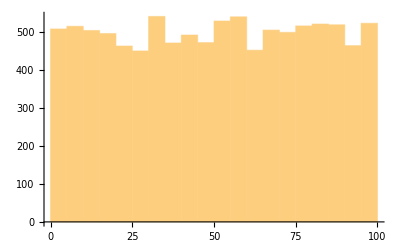
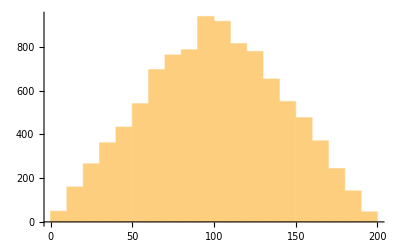
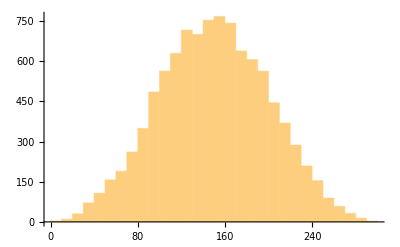
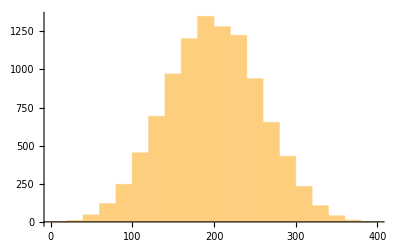
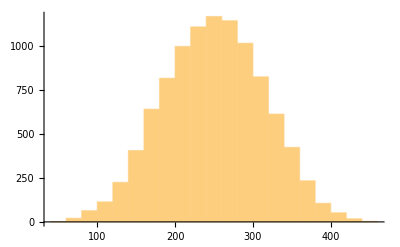

```mathematica
Histogram[Total/@RandomReal[100,{10000,#}]]&/@Range[5]
```

```mathematica
ImageData[Binarize[Rasterize[Style["W",200]]]]
```

```mathematica
ListPlot3D[ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

```mathematica
ListPlot3D[1-ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

```mathematica
TextWords[WikipediaData["computers"]]
```

{A,computer,is,a,digital,electronic,machine,that,can,be,programmed,to,carry,out,sequences,of,arithmetic,or,logical,operations,computation,automatically,Modern,computers,can,perform,generic,sets,of,operations,known,as,programs,These,programs,enable,computers,to,perform,a,wide,range,of,tasks,A,computer,system,is,a,complete,computer,that,includes,the,hardware,operating,system,main,software,and,peripheral,equipment,needed,and,used,for,full,operation,This,term,may,also,refer,to,a,group,of,computers,that,are,linked,and,function,together,such,as,a,computer,network,or,computer,cluster,A,broad,range,of,industrial,and,consumer,products,use,computers,as,control,systems,Simple,special-purpose,devices,like,microwave,ovens,and,remote,controls,are,included,as,are,factory,devices,like,industrial,robots,and,computer-aided,design,as,well,as,general-purpose,devices,like,personal,computers,and,mobile,devices,like,smartphones,Computers,power,the,Internet,which,links,billions,of,other,computers,and,users,Early,computers,were,meant,to,be,used,only,for,calculations,Simple,manual,instruments,like,the,abacus,have,aided,people,in,doing,calculations,since,ancient,times,Early,in,the,Industrial,Revolution,some,mechanical,devices,were,built,to,automate,long,tedious,tasks,such,as,guiding,patterns,for,looms,More,sophisticated,electrical,machines,did,specialized,analog,calculations,in,the,early,20th,century,The,first,digital,electronic,calculating,machines,were,developed,during,World,War,II,The,first,semiconductor,transistors,in,the,late,1940s,were,followed,by,the,silicon-based,MOSFET,MOS,transistor,and,monolithic,integrated,circuit,IC,chip,technologies,in,the,late,1950s,leading,to,the,microprocessor,and,the,microcomputer,revolution,in,the,1970s,The,speed,power,and,versatility,of,computers,have,been,increasing,dramatically,ever,since,then,with,transistor,counts,increasing,at,a,rapid,pace,as,predicted,by,Moore's,law,leading,to,the,Digital,Revolution,during,the,late,20th,to,early,21st,centuries,Conventionally,a,modern,computer,consists,of,at,least,one,processing,element,typically,a,central,processing,unit,CPU,in,the,form,of,a,microprocessor,along,with,some,type,of,computer,memory,typically,semiconductor,memory,chips,The,processing,element,carries,out,arithmetic,and,logical,operations,and,a,sequencing,and,control,unit,can,change,the,order,of,operations,in,response,to,stored,information,Peripheral,devices,include,input,devices,keyboards,mice,joystick,etc.,output,devices,monitor,screens,printers,etc.,and,input,output,devices,that,perform,both,functions,e.g.,the,2000s-era,touchscreen,Peripheral,devices,allow,information,to,be,retrieved,from,an,external,source,and,they,enable,the,result,of,operations,to,be,saved,and,retrieved,Etymology,According,to,the,Oxford,English,Dictionary,the,first,known,use,of,computer,was,in,a,1613,book,called,The,Yong,Mans,Gleanings,by,the,English,writer,Richard,Brathwait,I,haue,sic,read,the,truest,computer,of,Times,and,the,best,Arithmetician,that,euer,sic,breathed,and,he,reduceth,thy,dayes,into,a,short,number,This,usage,of,the,term,referred,to,a,human,computer,a,person,who,carried,out,calculations,or,computations,The,word,continued,with,the,same,meaning,until,the,middle,of,the,20th,century,During,the,latter,part,of,this,period,women,were,often,hired,as,computers,because,they,could,be,paid,less,than,their,male,counterparts,By,1943,most,human,computers,were,women.The,Online,Etymology,Dictionary,gives,the,first,attested,use,of,computer,in,the,1640s,meaning,one,who,calculates,this,is,an,agent,noun,from,compute,v.,The,Online,Etymology,Dictionary,states,that,the,use,of,the,term,to,mean,calculating,machine,of,any,type,is,from,1897,The,Online,Etymology,Dictionary,indicates,that,the,modern,use,of,the,term,to,mean,programmable,digital,electronic,computer,dates,from,1945,under,this,name,in,a,theoretical,sense,from,1937,as,Turing,machine,History,Pre-20th,century,Devices,have,been,used,to,aid,computation,for,thousands,of,years,mostly,using,one-to-one,correspondence,with,fingers,The,earliest,counting,device,was,probably,a,form,of,tally,stick,Later,record,keeping,aids,throughout,the,Fertile,Crescent,included,calculi,clay,spheres,cones,etc.,which,represented,counts,of,items,probably,livestock,or,grains,sealed,in,hollow,unbaked,clay,containers,The,use,of,counting,rods,is,one,example,The,abacus,was,initially,used,for,arithmetic,tasks,The,Roman,abacus,was,developed,from,devices,used,in,Babylonia,as,early,as,2400,BC,Since,then,many,other,forms,of,reckoning,boards,or,tables,have,been,invented,In,a,medieval,European,counting,house,a,checkered,cloth,would,be,placed,on,a,table,and,markers,moved,around,on,it,according,to,certain,rules,as,an,aid,to,calculating,sums,of,money,The,Antikythera,mechanism,is,believed,to,be,the,earliest,known,mechanical,analog,computer,according,to,Derek,J.,de,Solla,Price,It,was,designed,to,calculate,astronomical,positions,It,was,discovered,in,1901,in,the,Antikythera,wreck,off,the,Greek,island,of,Antikythera,between,Kythera,and,Crete,and,has,been,dated,to,approximately,c.,100,BC,Devices,of,comparable,complexity,to,the,Antikythera,mechanism,would,not,reappear,until,the,fourteenth,century.Many,mechanical,aids,to,calculation,and,measurement,were,constructed,for,astronomical,and,navigation,use,The,planisphere,was,a,star,chart,invented,by,Abū,Rayhān,al-Bīrūnī,in,the,early,11th,century,The,astrolabe,was,invented,in,the,Hellenistic,world,in,either,the,1st,or,2nd,centuries,BC,and,is,often,attributed,to,Hipparchus,A,combination,of,the,planisphere,and,dioptra,the,astrolabe,was,effectively,an,analog,computer,capable,of,working,out,several,different,kinds,of,problems,in,spherical,astronomy,An,astrolabe,incorporating,a,mechanical,calendar,computer,and,gear-wheels,was,invented,by,Abi,Bakr,of,Isfahan,Persia,in,1235,Abū,Rayhān,al-Bīrūnī,invented,the,first,mechanical,geared,lunisolar,calendar,astrolabe,an,early,fixed-wired,knowledge,processing,machine,with,a,gear,train,and,gear-wheels,c.,1000,AD,The,sector,a,calculating,instrument,used,for,solving,problems,in,proportion,trigonometry,multiplication,and,division,and,for,various,functions,such,as,squares,and,cube,roots,was,developed,in,the,late,16th,century,and,found,application,in,gunnery,surveying,and,navigation,The,planimeter,was,a,manual,instrument,to,calculate,the,area,of,a,closed,figure,by,tracing,over,it,with,a,mechanical,linkage,The,slide,rule,was,invented,around,1620,1630,by,the,English,clergyman,William,Oughtred,shortly,after,the,publication,of,the,concept,of,the,logarithm,It,is,a,hand-operated,analog,computer,for,doing,multiplication,and,division,As,slide,rule,development,progressed,added,scales,provided,reciprocals,squares,and,square,roots,cubes,and,cube,roots,as,well,as,transcendental,functions,such,as,logarithms,and,exponentials,circular,and,hyperbolic,trigonometry,and,other,functions,Slide,rules,with,special,scales,are,still,used,for,quick,performance,of,routine,calculations,such,as,the,E6B,circular,slide,rule,used,for,time,and,distance,calculations,on,light,aircraft,In,the,1770s,Pierre,Jaquet-Droz,a,Swiss,watchmaker,built,a,mechanical,doll,automaton,that,could,write,holding,a,quill,pen,By,switching,the,number,and,order,of,its,internal,wheels,different,letters,and,hence,different,messages,could,be,produced,In,effect,it,could,be,mechanically,programmed,to,read,instructions,Along,with,two,other,complex,machines,the,doll,is,at,the,Musée,d'Art,et,d'Histoire,of,Neuchâtel,Switzerland,and,still,operates.In,1831,1835,mathematician,and,engineer,Giovanni,Plana,devised,a,Perpetual,Calendar,machine,which,through,a,system,of,pulleys,and,cylinders,and,over,could,predict,the,perpetual,calendar,for,every,year,from,AD,0,that,is,1,BC,to,AD,4000,keeping,track,of,leap,years,and,varying,day,length,The,tide-predicting,machine,invented,by,the,Scottish,scientist,Sir,William,Thomson,in,1872,was,of,great,utility,to,navigation,in,shallow,waters,It,used,a,system,of,pulleys,and,wires,to,automatically,calculate,predicted,tide,levels,for,a,set,period,at,a,particular,location,The,differential,analyser,a,mechanical,analog,computer,designed,to,solve,differential,equations,by,integration,used,wheel-and-disc,mechanisms,to,perform,the,integration,In,1876,Sir,William,Thomson,had,already,discussed,the,possible,construction,of,such,calculators,but,he,had,been,stymied,by,the,limited,output,torque,of,the,ball-and-disk,integrators,In,a,differential,analyzer,the,output,of,one,integrator,drove,the,input,of,the,next,integrator,or,a,graphing,output,The,torque,amplifier,was,the,advance,that,allowed,these,machines,to,work,Starting,in,the,1920s,Vannevar,Bush,and,others,developed,mechanical,differential,analyzers,First,computer,Charles,Babbage,an,English,mechanical,engineer,and,polymath,originated,the,concept,of,a,programmable,computer,Considered,the,father,of,the,computer,he,conceptualized,and,invented,the,first,mechanical,computer,in,the,early,19th,century,After,working,on,his,revolutionary,difference,engine,designed,to,aid,in,navigational,calculations,in,1833,he,realized,that,a,much,more,general,design,an,Analytical,Engine,was,possible,The,input,of,programs,and,data,was,to,be,provided,to,the,machine,via,punched,cards,a,method,being,used,at,the,time,to,direct,mechanical,looms,such,as,the,Jacquard,loom,For,output,the,machine,would,have,a,printer,a,curve,plotter,and,a,bell,The,machine,would,also,be,able,to,punch,numbers,onto,cards,to,be,read,in,later,The,Engine,incorporated,an,arithmetic,logic,unit,control,flow,in,the,form,of,conditional,branching,and,loops,and,integrated,memory,making,it,the,first,design,for,a,general-purpose,computer,that,could,be,described,in,modern,terms,as,Turing-complete,The,machine,was,about,a,century,ahead,of,its,time,All,the,parts,for,his,machine,had,to,be,made,by,hand,this,was,a,major,problem,for,a,device,with,thousands,of,parts,Eventually,the,project,was,dissolved,with,the,decision,of,the,British,Government,to,cease,funding,Babbage's,failure,to,complete,the,analytical,engine,can,be,chiefly,attributed,to,political,and,financial,difficulties,as,well,as,his,desire,to,develop,an,increasingly,sophisticated,computer,and,to,move,ahead,faster,than,anyone,else,could,follow,Nevertheless,his,son,Henry,Babbage,completed,a,simplified,version,of,the,analytical,engine's,computing,unit,the,mill,in,1888,He,gave,a,successful,demonstration,of,its,use,in,computing,tables,in,1906,Analog,computers,During,the,first,half,of,the,20th,century,many,scientific,computing,needs,were,met,by,increasingly,sophisticated,analog,computers,which,used,a,direct,mechanical,or,electrical,model,of,the,problem,as,a,basis,for,computation,However,these,were,not,programmable,and,generally,lacked,the,versatility,and,accuracy,of,modern,digital,computers,The,first,modern,analog,computer,was,a,tide-predicting,machine,invented,by,Sir,William,Thomson,later,to,become,Lord,Kelvin,in,1872,The,differential,analyser,a,mechanical,analog,computer,designed,to,solve,differential,equations,by,integration,using,wheel-and-disc,mechanisms,was,conceptualized,in,1876,by,James,Thomson,the,elder,brother,of,the,more,famous,Sir,William,Thomson.The,art,of,mechanical,analog,computing,reached,its,zenith,with,the,differential,analyzer,built,by,H.,L.,Hazen,and,Vannevar,Bush,at,MIT,starting,in,1927,This,built,on,the,mechanical,integrators,of,James,Thomson,and,the,torque,amplifiers,invented,by,H.,W.,Nieman,A,dozen,of,these,devices,were,built,before,their,obsolescence,became,obvious,By,the,1950s,the,success,of,digital,electronic,computers,had,spelled,the,end,for,most,analog,computing,machines,but,analog,computers,remained,in,use,during,the,1950s,in,some,specialized,applications,such,as,education,slide,rule,and,aircraft,control,systems,Digital,computers,Electromechanical,By,1938,the,United,States,Navy,had,developed,an,electromechanical,analog,computer,small,enough,to,use,aboard,a,submarine,This,was,the,Torpedo,Data,Computer,which,used,trigonometry,to,solve,the,problem,of,firing,a,torpedo,at,a,moving,target,During,World,War,II,similar,devices,were,developed,in,other,countries,as,well,Early,digital,computers,were,electromechanical,electric,switches,drove,mechanical,relays,to,perform,the,calculation,These,devices,had,a,low,operating,speed,and,were,eventually,superseded,by,much,faster,all-electric,computers,originally,using,vacuum,tubes,The,Z2,created,by,German,engineer,Konrad,Zuse,in,1939,was,one,of,the,earliest,examples,of,an,electromechanical,relay,computer.In,1941,Zuse,followed,his,earlier,machine,up,with,the,Z3,the,world's,first,working,electromechanical,programmable,fully,automatic,digital,computer,The,Z3,was,built,with,2000,relays,implementing,a,22,bit,word,length,that,operated,at,a,clock,frequency,of,about,5,10,Hz,Program,code,was,supplied,on,punched,film,while,data,could,be,stored,in,64,words,of,memory,or,supplied,from,the,keyboard,It,was,quite,similar,to,modern,machines,in,some,respects,pioneering,numerous,advances,such,as,floating-point,numbers,Rather,than,the,harder-to-implement,decimal,system,used,in,Charles,Babbage's,earlier,design,using,a,binary,system,meant,that,Zuse's,machines,were,easier,to,build,and,potentially,more,reliable,given,the,technologies,available,at,that,time,The,Z3,was,not,itself,a,universal,computer,but,could,be,extended,to,be,Turing,Zuse's,next,computer,the,Z4,became,the,world's,first,commercial,computer,after,initial,delay,due,to,the,Second,World,War,it,was,completed,in,1950,and,delivered,to,the,ETH,Zurich,The,computer,was,manufactured,by,Zuse's,own,company,Zuse,KG,which,was,founded,in,1941,as,the,first,company,with,the,sole,purpose,of,developing,computers,Vacuum,tubes,and,digital,electronic,circuits,Purely,electronic,circuit,elements,soon,replaced,their,mechanical,and,electromechanical,equivalents,at,the,same,time,that,digital,calculation,replaced,analog,The,engineer,Tommy,Flowers,working,at,the,Post,Office,Research,Station,in,London,in,the,1930s,began,to,explore,the,possible,use,of,electronics,for,the,telephone,exchange,Experimental,equipment,that,he,built,in,1934,went,into,operation,five,years,later,converting,a,portion,of,the,telephone,exchange,network,into,an,electronic,data,processing,system,using,thousands,of,vacuum,tubes,In,the,US,John,Vincent,Atanasoff,and,Clifford,E.,Berry,of,Iowa,State,University,developed,and,tested,the,Atanasoff,Berry,Computer,ABC,in,1942,the,first,automatic,electronic,digital,computer,This,design,was,also,all-electronic,and,used,about,300,vacuum,tubes,with,capacitors,fixed,in,a,mechanically,rotating,drum,for,memory,During,World,War,II,the,British,code-breakers,at,Bletchley,Park,achieved,a,number,of,successes,at,breaking,encrypted,German,military,communications,The,German,encryption,machine,Enigma,was,first,attacked,with,the,help,of,the,electro-mechanical,bombes,which,were,often,run,by,women,To,crack,the,more,sophisticated,German,Lorenz,SZ,40/42,machine,used,for,high-level,Army,communications,Max,Newman,and,his,colleagues,commissioned,Flowers,to,build,the,Colossus,He,spent,eleven,months,from,early,February,1943,designing,and,building,the,first,Colossus,After,a,functional,test,in,December,1943,Colossus,was,shipped,to,Bletchley,Park,where,it,was,delivered,on,18,January,1944,and,attacked,its,first,message,on,5,February.Colossus,was,the,world's,first,electronic,digital,programmable,computer,It,used,a,large,number,of,valves,vacuum,tubes,It,had,paper-tape,input,and,was,capable,of,being,configured,to,perform,a,variety,of,boolean,logical,operations,on,its,data,but,it,was,not,Turing-complete,Nine,Mk,II,Colossi,were,built,The,Mk,I,was,converted,to,a,Mk,II,making,ten,machines,in,total,Colossus,Mark,I,contained,1,500,thermionic,valves,tubes,but,Mark,II,with,2,400,valves,was,both,five,times,faster,and,simpler,to,operate,than,Mark,I,greatly,speeding,the,decoding,process,The,ENIAC,Electronic,Numerical,Integrator,and,Computer,was,the,first,electronic,programmable,computer,built,in,the,U.S,Although,the,ENIAC,was,similar,to,the,Colossus,it,was,much,faster,more,flexible,and,it,was,Turing-complete,Like,the,Colossus,a,program,on,the,ENIAC,was,defined,by,the,states,of,its,patch,cables,and,switches,a,far,cry,from,the,stored,program,electronic,machines,that,came,later,Once,a,program,was,written,it,had,to,be,mechanically,set,into,the,machine,with,manual,resetting,of,plugs,and,switches,The,programmers,of,the,ENIAC,were,six,women,often,known,collectively,as,the,ENIAC,girls,It,combined,the,high,speed,of,electronics,with,the,ability,to,be,programmed,for,many,complex,problems,It,could,add,or,subtract,5000,times,a,second,a,thousand,times,faster,than,any,other,machine,It,also,had,modules,to,multiply,divide,and,square,root,High,speed,memory,was,limited,to,20,words,about,80,bytes,Built,under,the,direction,of,John,Mauchly,and,J.,Presper,Eckert,at,the,University,of,Pennsylvania,ENIAC's,development,and,construction,lasted,from,1943,to,full,operation,at,the,end,of,1945,The,machine,was,huge,weighing,30,tons,using,200,kilowatts,of,electric,power,and,contained,over,18,000,vacuum,tubes,1,500,relays,and,hundreds,of,thousands,of,resistors,capacitors,and,inductors,Modern,computers,Concept,of,modern,computer,The,principle,of,the,modern,computer,was,proposed,by,Alan,Turing,in,his,seminal,1936,paper,On,Computable,Numbers,Turing,proposed,a,simple,device,that,he,called,Universal,Computing,machine,and,that,is,now,known,as,a,universal,Turing,machine,He,proved,that,such,a,machine,is,capable,of,computing,anything,that,is,computable,by,executing,instructions,program,stored,on,tape,allowing,the,machine,to,be,programmable,The,fundamental,concept,of,Turing's,design,is,the,stored,program,where,all,the,instructions,for,computing,are,stored,in,memory,Von,Neumann,acknowledged,that,the,central,concept,of,the,modern,computer,was,due,to,this,paper,Turing,machines,are,to,this,day,a,central,object,of,study,in,theory,of,computation,Except,for,the,limitations,imposed,by,their,finite,memory,stores,modern,computers,are,said,to,be,Turing-complete,which,is,to,say,they,have,algorithm,execution,capability,equivalent,to,a,universal,Turing,machine,Stored,programs,Early,computing,machines,had,fixed,programs,Changing,its,function,required,the,re-wiring,and,re-structuring,of,the,machine,With,the,proposal,of,the,stored-program,computer,this,changed,A,stored-program,computer,includes,by,design,an,instruction,set,and,can,store,in,memory,a,set,of,instructions,a,program,that,details,the,computation,The,theoretical,basis,for,the,stored-program,computer,was,laid,out,by,Alan,Turing,in,his,1936,paper,In,1945,Turing,joined,the,National,Physical,Laboratory,and,began,work,on,developing,an,electronic,stored-program,digital,computer,His,1945,report,Proposed,Electronic,Calculator,was,the,first,specification,for,such,a,device,John,von,Neumann,at,the,University,of,Pennsylvania,also,circulated,his,First,Draft,of,a,Report,on,the,EDVAC,in,1945,The,Manchester,Baby,was,the,world's,first,stored-program,computer,It,was,built,at,the,University,of,Manchester,in,England,by,Frederic,C.,Williams,Tom,Kilburn,and,Geoff,Tootill,and,ran,its,first,program,on,21,June,1948,It,was,designed,as,a,testbed,for,the,Williams,tube,the,first,random-access,digital,storage,device,Although,the,computer,was,described,as,small,and,primitive,by,a,1998,retrospective,it,was,the,first,working,machine,to,contain,all,of,the,elements,essential,to,a,modern,electronic,computer,As,soon,as,the,Baby,had,demonstrated,the,feasibility,of,its,design,a,project,began,at,the,university,to,develop,it,into,a,practically,useful,computer,the,Manchester,Mark,1,The,Mark,1,in,turn,quickly,became,the,prototype,for,the,Ferranti,Mark,1,the,world's,first,commercially,available,general-purpose,computer,Built,by,Ferranti,it,was,delivered,to,the,University,of,Manchester,in,February,1951,At,least,seven,of,these,later,machines,were,delivered,between,1953,and,1957,one,of,them,to,Shell,labs,in,Amsterdam,In,October,1947,the,directors,of,British,catering,company,J.,Lyons,Company,decided,to,take,an,active,role,in,promoting,the,commercial,development,of,computers,Lyons's,LEO,I,computer,modelled,closely,on,the,Cambridge,EDSAC,of,1949,became,operational,in,April,1951,and,ran,the,world's,first,routine,office,computer,job,Grace,Hopper,was,the,first,to,develop,a,compiler,for,a,programming,language,Transistors,The,concept,of,a,field-effect,transistor,was,proposed,by,Julius,Edgar,Lilienfeld,in,1925,John,Bardeen,and,Walter,Brattain,while,working,under,William,Shockley,at,Bell,Labs,built,the,first,working,transistor,the,point-contact,transistor,in,1947,which,was,followed,by,Shockley's,bipolar,junction,transistor,in,1948,From,1955,onwards,transistors,replaced,vacuum,tubes,in,computer,designs,giving,rise,to,the,second,generation,of,computers,Compared,to,vacuum,tubes,transistors,have,many,advantages,they,are,smaller,and,require,less,power,than,vacuum,tubes,so,give,off,less,heat,Junction,transistors,were,much,more,reliable,than,vacuum,tubes,and,had,longer,indefinite,service,life,Transistorized,computers,could,contain,tens,of,thousands,of,binary,logic,circuits,in,a,relatively,compact,space,However,early,junction,transistors,were,relatively,bulky,devices,that,were,difficult,to,manufacture,on,a,mass-production,basis,which,limited,them,to,a,number,of,specialised,applications.At,the,University,of,Manchester,a,team,under,the,leadership,of,Tom,Kilburn,designed,and,built,a,machine,using,the,newly,developed,transistors,instead,of,valves,Their,first,transistorised,computer,and,the,first,in,the,world,was,operational,by,1953,and,a,second,version,was,completed,there,in,April,1955,However,the,machine,did,make,use,of,valves,to,generate,its,125,kHz,clock,waveforms,and,in,the,circuitry,to,read,and,write,on,its,magnetic,drum,memory,so,it,was,not,the,first,completely,transistorized,computer,That,distinction,goes,to,the,Harwell,CADET,of,1955,built,by,the,electronics,division,of,the,Atomic,Energy,Research,Establishment,at,Harwell,The,metal,oxide,silicon,field-effect,transistor,MOSFET,also,known,as,the,MOS,transistor,was,invented,by,Mohamed,M.,Atalla,and,Dawon,Kahng,at,Bell,Labs,in,1959,It,was,the,first,truly,compact,transistor,that,could,be,miniaturised,and,mass-produced,for,a,wide,range,of,uses,With,its,high,scalability,and,much,lower,power,consumption,and,higher,density,than,bipolar,junction,transistors,the,MOSFET,made,it,possible,to,build,high-density,integrated,circuits,In,addition,to,data,processing,it,also,enabled,the,practical,use,of,MOS,transistors,as,memory,cell,storage,elements,leading,to,the,development,of,MOS,semiconductor,memory,which,replaced,earlier,magnetic-core,memory,in,computers,The,MOSFET,led,to,the,microcomputer,revolution,and,became,the,driving,force,behind,the,computer,revolution,The,MOSFET,is,the,most,widely,used,transistor,in,computers,and,is,the,fundamental,building,block,of,digital,electronics,Integrated,circuits,The,next,great,advance,in,computing,power,came,with,the,advent,of,the,integrated,circuit,IC,The,idea,of,the,integrated,circuit,was,first,conceived,by,a,radar,scientist,working,for,the,Royal,Radar,Establishment,of,the,Ministry,of,Defence,Geoffrey,W.A.,Dummer,Dummer,presented,the,first,public,description,of,an,integrated,circuit,at,the,Symposium,on,Progress,in,Quality,Electronic,Components,in,Washington,D.C.,on,7,May,1952,The,first,working,ICs,were,invented,by,Jack,Kilby,at,Texas,Instruments,and,Robert,Noyce,at,Fairchild,Semiconductor,Kilby,recorded,his,initial,ideas,concerning,the,integrated,circuit,in,July,1958,successfully,demonstrating,the,first,working,integrated,example,on,12,September,1958,In,his,patent,application,of,6,February,1959,Kilby,described,his,new,device,as,a,body,of,semiconductor,material,wherein,all,the,components,of,the,electronic,circuit,are,completely,integrated,However,Kilby's,invention,was,a,hybrid,integrated,circuit,hybrid,IC,rather,than,a,monolithic,integrated,circuit,IC,chip,Kilby's,IC,had,external,wire,connections,which,made,it,difficult,to,mass-produce,Noyce,also,came,up,with,his,own,idea,of,an,integrated,circuit,half,a,year,later,than,Kilby,Noyce's,invention,was,the,first,true,monolithic,IC,chip,His,chip,solved,many,practical,problems,that,Kilby's,had,not,Produced,at,Fairchild,Semiconductor,it,was,made,of,silicon,whereas,Kilby's,chip,was,made,of,germanium,Noyce's,monolithic,IC,was,fabricated,using,the,planar,process,developed,by,his,colleague,Jean,Hoerni,in,early,1959,In,turn,the,planar,process,was,based,on,Mohamed,M.,Atalla's,work,on,semiconductor,surface,passivation,by,silicon,dioxide,in,the,late,1950s,Modern,monolithic,ICs,are,predominantly,MOS,metal-oxide-semiconductor,integrated,circuits,built,from,MOSFETs,MOS,transistors,The,earliest,experimental,MOS,IC,to,be,fabricated,was,a,16-transistor,chip,built,by,Fred,Heiman,and,Steven,Hofstein,at,RCA,in,1962,General,Microelectronics,later,introduced,the,first,commercial,MOS,IC,in,1964,developed,by,Robert,Norman,Following,the,development,of,the,self-aligned,gate,silicon-gate,MOS,transistor,by,Robert,Kerwin,Donald,Klein,and,John,Sarace,at,Bell,Labs,in,1967,the,first,silicon-gate,MOS,IC,with,self-aligned,gates,was,developed,by,Federico,Faggin,at,Fairchild,Semiconductor,in,1968,The,MOSFET,has,since,become,the,most,critical,device,component,in,modern,ICs.The,development,of,the,MOS,integrated,circuit,led,to,the,invention,of,the,microprocessor,and,heralded,an,explosion,in,the,commercial,and,personal,use,of,computers,While,the,subject,of,exactly,which,device,was,the,first,microprocessor,is,contentious,partly,due,to,lack,of,agreement,on,the,exact,definition,of,the,term,microprocessor,it,is,largely,undisputed,that,the,first,single-chip,microprocessor,was,the,Intel,4004,designed,and,realized,by,Federico,Faggin,with,his,silicon-gate,MOS,IC,technology,along,with,Ted,Hoff,Masatoshi,Shima,and,Stanley,Mazor,at,Intel,In,the,early,1970s,MOS,IC,technology,enabled,the,integration,of,more,than,10,000,transistors,on,a,single,chip.System,on,a,Chip,SoCs,are,complete,computers,on,a,microchip,or,chip,the,size,of,a,coin,They,may,or,may,not,have,integrated,RAM,and,flash,memory,If,not,integrated,the,RAM,is,usually,placed,directly,above,known,as,Package,on,package,or,below,on,the,opposite,side,of,the,circuit,board,the,SoC,and,the,flash,memory,is,usually,placed,right,next,to,the,SoC,this,all,done,to,improve,data,transfer,speeds,as,the,data,signals,don't,have,to,travel,long,distances,Since,ENIAC,in,1945,computers,have,advanced,enormously,with,modern,SoCs,Such,as,the,Snapdragon,865,being,the,size,of,a,coin,while,also,being,hundreds,of,thousands,of,times,more,powerful,than,ENIAC,integrating,billions,of,transistors,and,consuming,only,a,few,watts,of,power,Mobile,computers,The,first,mobile,computers,were,heavy,and,ran,from,mains,power,The,50,lb,23,kg,IBM,5100,was,an,early,example,Later,portables,such,as,the,Osborne,1,and,Compaq,Portable,were,considerably,lighter,but,still,needed,to,be,plugged,in,The,first,laptops,such,as,the,Grid,Compass,removed,this,requirement,by,incorporating,batteries,and,with,the,continued,miniaturization,of,computing,resources,and,advancements,in,portable,battery,life,portable,computers,grew,in,popularity,in,the,2000s,The,same,developments,allowed,manufacturers,to,integrate,computing,resources,into,cellular,mobile,phones,by,the,early,2000s,These,smartphones,and,tablets,run,on,a,variety,of,operating,systems,and,recently,became,the,dominant,computing,device,on,the,market,These,are,powered,by,System,on,a,Chip,SoCs,which,are,complete,computers,on,a,microchip,the,size,of,a,coin,Types,Computers,can,be,classified,in,a,number,of,different,ways,including,By,architecture,Analog,computer,Digital,computer,Hybrid,computer,Harvard,architecture,Von,Neumann,architecture,Complex,instruction,set,computer,Reduced,instruction,set,computer,By,size,form-factor,and,purpose,Supercomputer,Mainframe,computer,Minicomputer,term,no,longer,used,Server,Rackmount,server,Blade,server,Tower,server,Personal,computer,Workstation,Microcomputer,term,no,longer,used,Home,computer,term,fallen,into,disuse,Desktop,computer,Tower,desktop,Slimline,desktop,Multimedia,computer,non-linear,editing,system,computers,video,editing,PCs,and,the,like,this,term,is,no,longer,used,Gaming,computer,All-in-one,PC,Nettop,Small,form,factor,PCs,Mini,PCs,Home,theater,PC,Keyboard,computer,Portable,computer,Thin,client,Internet,appliance,Laptop,Desktop,replacement,computer,Gaming,laptop,Rugged,laptop,2-in-1,PC,Ultrabook,Chromebook,Subnotebook,Netbook,Mobile,computers,Tablet,computer,Smartphone,Ultra-mobile,PC,Pocket,PC,Palmtop,PC,Handheld,PC,Wearable,computer,Smartwatch,Smartglasses,Single-board,computer,Plug,computer,Stick,PC,Programmable,logic,controller,Computer-on-module,System,on,module,System,in,a,package,System-on-chip,Also,known,as,an,Application,Processor,or,AP,if,it,lacks,circuitry,such,as,radio,circuitry,Microcontroller,Hardware,The,term,hardware,covers,all,of,those,parts,of,a,computer,that,are,tangible,physical,objects,Circuits,computer,chips,graphic,cards,sound,cards,memory,RAM,motherboard,displays,power,supplies,cables,keyboards,printers,and,mice,input,devices,are,all,hardware,History,of,computing,hardware,Other,hardware,topics,A,general-purpose,computer,has,four,main,components,the,arithmetic,logic,unit,ALU,the,control,unit,the,memory,and,the,input,and,output,devices,collectively,termed,I,O,These,parts,are,interconnected,by,buses,often,made,of,groups,of,wires,Inside,each,of,these,parts,are,thousands,to,trillions,of,small,electrical,circuits,which,can,be,turned,off,or,on,by,means,of,an,electronic,switch,Each,circuit,represents,a,bit,binary,digit,of,information,so,that,when,the,circuit,is,on,it,represents,a,1,and,when,off,it,represents,a,0,in,positive,logic,representation,The,circuits,are,arranged,in,logic,gates,so,that,one,or,more,of,the,circuits,may,control,the,state,of,one,or,more,of,the,other,circuits,Input,devices,When,unprocessed,data,is,sent,to,the,computer,with,the,help,of,input,devices,the,data,is,processed,and,sent,to,output,devices,The,input,devices,may,be,hand-operated,or,automated,The,act,of,processing,is,mainly,regulated,by,the,CPU,Some,examples,of,input,devices,are,Computer,keyboard,Digital,camera,Digital,video,Graphics,tablet,Image,scanner,Joystick,Microphone,Mouse,Overlay,keyboard,Real-time,clock,Trackball,Touchscreen,Light,pen,Output,devices,The,means,through,which,computer,gives,output,are,known,as,output,devices,Some,examples,of,output,devices,are,Computer,monitor,Printer,PC,speaker,Projector,Sound,card,Video,card,Control,unit,The,control,unit,often,called,a,control,system,or,central,controller,manages,the,computer's,various,components,it,reads,and,interprets,decodes,the,program,instructions,transforming,them,into,control,signals,that,activate,other,parts,of,the,computer,Control,systems,in,advanced,computers,may,change,the,order,of,execution,of,some,instructions,to,improve,performance,A,key,component,common,to,all,CPUs,is,the,program,counter,a,special,memory,cell,a,register,that,keeps,track,of,which,location,in,memory,the,next,instruction,is,to,be,read,from.The,control,system's,function,is,as,follows,this,is,a,simplified,description,and,some,of,these,steps,may,be,performed,concurrently,or,in,a,different,order,depending,on,the,type,of,CPU,Read,the,code,for,the,next,instruction,from,the,cell,indicated,by,the,program,counter,Decode,the,numerical,code,for,the,instruction,into,a,set,of,commands,or,signals,for,each,of,the,other,systems,Increment,the,program,counter,so,it,points,to,the,next,instruction,Read,whatever,data,the,instruction,requires,from,cells,in,memory,or,perhaps,from,an,input,device,The,location,of,this,required,data,is,typically,stored,within,the,instruction,code,Provide,the,necessary,data,to,an,ALU,or,register,If,the,instruction,requires,an,ALU,or,specialized,hardware,to,complete,instruct,the,hardware,to,perform,the,requested,operation,Write,the,result,from,the,ALU,back,to,a,memory,location,or,to,a,register,or,perhaps,an,output,device,Jump,back,to,step,1,Since,the,program,counter,is,conceptually,just,another,set,of,memory,cells,it,can,be,changed,by,calculations,done,in,the,ALU,Adding,100,to,the,program,counter,would,cause,the,next,instruction,to,be,read,from,a,place,100,locations,further,down,the,program,Instructions,that,modify,the,program,counter,are,often,known,as,jumps,and,allow,for,loops,instructions,that,are,repeated,by,the,computer,and,often,conditional,instruction,execution,both,examples,of,control,flow,The,sequence,of,operations,that,the,control,unit,goes,through,to,process,an,instruction,is,in,itself,like,a,short,computer,program,and,indeed,in,some,more,complex,CPU,designs,there,is,another,yet,smaller,computer,called,a,microsequencer,which,runs,a,microcode,program,that,causes,all,of,these,events,to,happen,Central,processing,unit,CPU,The,control,unit,ALU,and,registers,are,collectively,known,as,a,central,processing,unit,CPU,Early,CPUs,were,composed,of,many,separate,components,Since,the,1970s,CPUs,have,typically,been,constructed,on,a,single,MOS,integrated,circuit,chip,called,a,microprocessor,Arithmetic,logic,unit,ALU,The,ALU,is,capable,of,performing,two,classes,of,operations,arithmetic,and,logic,The,set,of,arithmetic,operations,that,a,particular,ALU,supports,may,be,limited,to,addition,and,subtraction,or,might,include,multiplication,division,trigonometry,functions,such,as,sine,cosine,etc.,and,square,roots,Some,can,operate,only,on,whole,numbers,integers,while,others,use,floating,point,to,represent,real,numbers,albeit,with,limited,precision,However,any,computer,that,is,capable,of,performing,just,the,simplest,operations,can,be,programmed,to,break,down,the,more,complex,operations,into,simple,steps,that,it,can,perform,Therefore,any,computer,can,be,programmed,to,perform,any,arithmetic,operation,although,it,will,take,more,time,to,do,so,if,its,ALU,does,not,directly,support,the,operation,An,ALU,may,also,compare,numbers,and,return,Boolean,truth,values,true,or,false,depending,on,whether,one,is,equal,to,greater,than,or,less,than,the,other,is,64,greater,than,65,Logic,operations,involve,Boolean,logic,AND,OR,XOR,and,NOT,These,can,be,useful,for,creating,complicated,conditional,statements,and,processing,Boolean,logic,Superscalar,computers,may,contain,multiple,ALUs,allowing,them,to,process,several,instructions,simultaneously,Graphics,processors,and,computers,with,SIMD,and,MIMD,features,often,contain,ALUs,that,can,perform,arithmetic,on,vectors,and,matrices,Memory,A,computer's,memory,can,be,viewed,as,a,list,of,cells,into,which,numbers,can,be,placed,or,read,Each,cell,has,a,numbered,address,and,can,store,a,single,number,The,computer,can,be,instructed,to,put,the,number,123,into,the,cell,numbered,1357,or,to,add,the,number,that,is,in,cell,1357,to,the,number,that,is,in,cell,2468,and,put,the,answer,into,cell,1595,The,information,stored,in,memory,may,represent,practically,anything,Letters,numbers,even,computer,instructions,can,be,placed,into,memory,with,equal,ease,Since,the,CPU,does,not,differentiate,between,different,types,of,information,it,is,the,software's,responsibility,to,give,significance,to,what,the,memory,sees,as,nothing,but,a,series,of,numbers,In,almost,all,modern,computers,each,memory,cell,is,set,up,to,store,binary,numbers,in,groups,of,eight,bits,called,a,byte,Each,byte,is,able,to,represent,256,different,numbers,28,256,either,from,0,to,255,or,−128,to,+127,To,store,larger,numbers,several,consecutive,bytes,may,be,used,typically,two,four,or,eight,When,negative,numbers,are,required,they,are,usually,stored,in,two's,complement,notation,Other,arrangements,are,possible,but,are,usually,not,seen,outside,of,specialized,applications,or,historical,contexts,A,computer,can,store,any,kind,of,information,in,memory,if,it,can,be,represented,numerically,Modern,computers,have,billions,or,even,trillions,of,bytes,of,memory,The,CPU,contains,a,special,set,of,memory,cells,called,registers,that,can,be,read,and,written,to,much,more,rapidly,than,the,main,memory,area,There,are,typically,between,two,and,one,hundred,registers,depending,on,the,type,of,CPU,Registers,are,used,for,the,most,frequently,needed,data,items,to,avoid,having,to,access,main,memory,every,time,data,is,needed,As,data,is,constantly,being,worked,on,reducing,the,need,to,access,main,memory,which,is,often,slow,compared,to,the,ALU,and,control,units,greatly,increases,the,computer's,speed,Computer,main,memory,comes,in,two,principal,varieties,random-access,memory,or,RAM,read-only,memory,or,ROMRAM,can,be,read,and,written,to,anytime,the,CPU,commands,it,but,ROM,is,preloaded,with,data,and,software,that,never,changes,therefore,the,CPU,can,only,read,from,it,ROM,is,typically,used,to,store,the,computer's,initial,start-up,instructions,In,general,the,contents,of,RAM,are,erased,when,the,power,to,the,computer,is,turned,off,but,ROM,retains,its,data,indefinitely,In,a,PC,the,ROM,contains,a,specialized,program,called,the,BIOS,that,orchestrates,loading,the,computer's,operating,system,from,the,hard,disk,drive,into,RAM,whenever,the,computer,is,turned,on,or,reset,In,embedded,computers,which,frequently,do,not,have,disk,drives,all,of,the,required,software,may,be,stored,in,ROM,Software,stored,in,ROM,is,often,called,firmware,because,it,is,notionally,more,like,hardware,than,software,Flash,memory,blurs,the,distinction,between,ROM,and,RAM,as,it,retains,its,data,when,turned,off,but,is,also,rewritable,It,is,typically,much,slower,than,conventional,ROM,and,RAM,however,so,its,use,is,restricted,to,applications,where,high,speed,is,unnecessary.In,more,sophisticated,computers,there,may,be,one,or,more,RAM,cache,memories,which,are,slower,than,registers,but,faster,than,main,memory,Generally,computers,with,this,sort,of,cache,are,designed,to,move,frequently,needed,data,into,the,cache,automatically,often,without,the,need,for,any,intervention,on,the,programmer's,part,Input,output,I,O,I,O,is,the,means,by,which,a,computer,exchanges,information,with,the,outside,world,Devices,that,provide,input,or,output,to,the,computer,are,called,peripherals,On,a,typical,personal,computer,peripherals,include,input,devices,like,the,keyboard,and,mouse,and,output,devices,such,as,the,display,and,printer,Hard,disk,drives,floppy,disk,drives,and,optical,disc,drives,serve,as,both,input,and,output,devices,Computer,networking,is,another,form,of,I,O.,I,O,devices,are,often,complex,computers,in,their,own,right,with,their,own,CPU,and,memory,A,graphics,processing,unit,might,contain,fifty,or,more,tiny,computers,that,perform,the,calculations,necessary,to,display,3D,graphics,Modern,desktop,computers,contain,many,smaller,computers,that,assist,the,main,CPU,in,performing,I,O,A,2016-era,flat,screen,display,contains,its,own,computer,circuitry,Multitasking,While,a,computer,may,be,viewed,as,running,one,gigantic,program,stored,in,its,main,memory,in,some,systems,it,is,necessary,to,give,the,appearance,of,running,several,programs,simultaneously,This,is,achieved,by,multitasking,i.e.,having,the,computer,switch,rapidly,between,running,each,program,in,turn,One,means,by,which,this,is,done,is,with,a,special,signal,called,an,interrupt,which,can,periodically,cause,the,computer,to,stop,executing,instructions,where,it,was,and,do,something,else,instead,By,remembering,where,it,was,executing,prior,to,the,interrupt,the,computer,can,return,to,that,task,later,If,several,programs,are,running,at,the,same,time,then,the,interrupt,generator,might,be,causing,several,hundred,interrupts,per,second,causing,a,program,switch,each,time,Since,modern,computers,typically,execute,instructions,several,orders,of,magnitude,faster,than,human,perception,it,may,appear,that,many,programs,are,running,at,the,same,time,even,though,only,one,is,ever,executing,in,any,given,instant,This,method,of,multitasking,is,sometimes,termed,time-sharing,since,each,program,is,allocated,a,slice,of,time,in,turn.Before,the,era,of,inexpensive,computers,the,principal,use,for,multitasking,was,to,allow,many,people,to,share,the,same,computer,Seemingly,multitasking,would,cause,a,computer,that,is,switching,between,several,programs,to,run,more,slowly,in,direct,proportion,to,the,number,of,programs,it,is,running,but,most,programs,spend,much,of,their,time,waiting,for,slow,input,output,devices,to,complete,their,tasks,If,a,program,is,waiting,for,the,user,to,click,on,the,mouse,or,press,a,key,on,the,keyboard,then,it,will,not,take,a,time,slice,until,the,event,it,is,waiting,for,has,occurred,This,frees,up,time,for,other,programs,to,execute,so,that,many,programs,may,be,run,simultaneously,without,unacceptable,speed,loss,Multiprocessing,Some,computers,are,designed,to,distribute,their,work,across,several,CPUs,in,a,multiprocessing,configuration,a,technique,once,employed,in,only,large,and,powerful,machines,such,as,supercomputers,mainframe,computers,and,servers,Multiprocessor,and,multi-core,multiple,CPUs,on,a,single,integrated,circuit,personal,and,laptop,computers,are,now,widely,available,and,are,being,increasingly,used,in,lower-end,markets,as,a,result,Supercomputers,in,particular,often,have,highly,unique,architectures,that,differ,significantly,from,the,basic,stored-program,architecture,and,from,general-purpose,computers,They,often,feature,thousands,of,CPUs,customized,high-speed,interconnects,and,specialized,computing,hardware,Such,designs,tend,to,be,useful,for,only,specialized,tasks,due,to,the,large,scale,of,program,organization,required,to,successfully,utilize,most,of,the,available,resources,at,once,Supercomputers,usually,see,usage,in,large-scale,simulation,graphics,rendering,and,cryptography,applications,as,well,as,with,other,so-called,embarrassingly,parallel,tasks,Software,Software,refers,to,parts,of,the,computer,which,do,not,have,a,material,form,such,as,programs,data,protocols,etc,Software,is,that,part,of,a,computer,system,that,consists,of,encoded,information,or,computer,instructions,in,contrast,to,the,physical,hardware,from,which,the,system,is,built,Computer,software,includes,computer,programs,libraries,and,related,non-executable,data,such,as,online,documentation,or,digital,media,It,is,often,divided,into,system,software,and,application,software,Computer,hardware,and,software,require,each,other,and,neither,can,be,realistically,used,on,its,own,When,software,is,stored,in,hardware,that,cannot,easily,be,modified,such,as,with,BIOS,ROM,in,an,IBM,PC,compatible,computer,it,is,sometimes,called,firmware,Languages,There,are,thousands,of,different,programming,languages,some,intended,for,general,purpose,others,useful,for,only,highly,specialized,applications,Programs,The,defining,feature,of,modern,computers,which,distinguishes,them,from,all,other,machines,is,that,they,can,be,programmed,That,is,to,say,that,some,type,of,instructions,the,program,can,be,given,to,the,computer,and,it,will,process,them,Modern,computers,based,on,the,von,Neumann,architecture,often,have,machine,code,in,the,form,of,an,imperative,programming,language,In,practical,terms,a,computer,program,may,be,just,a,few,instructions,or,extend,to,many,millions,of,instructions,as,do,the,programs,for,word,processors,and,web,browsers,for,example,A,typical,modern,computer,can,execute,billions,of,instructions,per,second,gigaflops,and,rarely,makes,a,mistake,over,many,years,of,operation,Large,computer,programs,consisting,of,several,million,instructions,may,take,teams,of,programmers,years,to,write,and,due,to,the,complexity,of,the,task,almost,certainly,contain,errors,Stored,program,architecture,This,section,applies,to,most,common,RAM,machine,based,computers,In,most,cases,computer,instructions,are,simple,add,one,number,to,another,move,some,data,from,one,location,to,another,send,a,message,to,some,external,device,etc,These,instructions,are,read,from,the,computer's,memory,and,are,generally,carried,out,executed,in,the,order,they,were,given,However,there,are,usually,specialized,instructions,to,tell,the,computer,to,jump,ahead,or,backwards,to,some,other,place,in,the,program,and,to,carry,on,executing,from,there,These,are,called,jump,instructions,or,branches,Furthermore,jump,instructions,may,be,made,to,happen,conditionally,so,that,different,sequences,of,instructions,may,be,used,depending,on,the,result,of,some,previous,calculation,or,some,external,event,Many,computers,directly,support,subroutines,by,providing,a,type,of,jump,that,remembers,the,location,it,jumped,from,and,another,instruction,to,return,to,the,instruction,following,that,jump,instruction,Program,execution,might,be,likened,to,reading,a,book,While,a,person,will,normally,read,each,word,and,line,in,sequence,they,may,at,times,jump,back,to,an,earlier,place,in,the,text,or,skip,sections,that,are,not,of,interest,Similarly,a,computer,may,sometimes,go,back,and,repeat,the,instructions,in,some,section,of,the,program,over,and,over,again,until,some,internal,condition,is,met,This,is,called,the,flow,of,control,within,the,program,and,it,is,what,allows,the,computer,to,perform,tasks,repeatedly,without,human,intervention,Comparatively,a,person,using,a,pocket,calculator,can,perform,a,basic,arithmetic,operation,such,as,adding,two,numbers,with,just,a,few,button,presses,But,to,add,together,all,of,the,numbers,from,1,to,1,000,would,take,thousands,of,button,presses,and,a,lot,of,time,with,a,near,certainty,of,making,a,mistake,On,the,other,hand,a,computer,may,be,programmed,to,do,this,with,just,a,few,simple,instructions,The,following,example,is,written,in,the,MIPS,assembly,language,Once,told,to,run,this,program,the,computer,will,perform,the,repetitive,addition,task,without,further,human,intervention,It,will,almost,never,make,a,mistake,and,a,modern,PC,can,complete,the,task,in,a,fraction,of,a,second,Machine,code,In,most,computers,individual,instructions,are,stored,as,machine,code,with,each,instruction,being,given,a,unique,number,its,operation,code,or,opcode,for,short,The,command,to,add,two,numbers,together,would,have,one,opcode,the,command,to,multiply,them,would,have,a,different,opcode,and,so,on,The,simplest,computers,are,able,to,perform,any,of,a,handful,of,different,instructions,the,more,complex,computers,have,several,hundred,to,choose,from,each,with,a,unique,numerical,code,Since,the,computer's,memory,is,able,to,store,numbers,it,can,also,store,the,instruction,codes,This,leads,to,the,important,fact,that,entire,programs,which,are,just,lists,of,these,instructions,can,be,represented,as,lists,of,numbers,and,can,themselves,be,manipulated,inside,the,computer,in,the,same,way,as,numeric,data,The,fundamental,concept,of,storing,programs,in,the,computer's,memory,alongside,the,data,they,operate,on,is,the,crux,of,the,von,Neumann,or,stored,program,architecture,In,some,cases,a,computer,might,store,some,or,all,of,its,program,in,memory,that,is,kept,separate,from,the,data,it,operates,on,This,is,called,the,Harvard,architecture,after,the,Harvard,Mark,I,computer,Modern,von,Neumann,computers,display,some,traits,of,the,Harvard,architecture,in,their,designs,such,as,in,CPU,caches,While,it,is,possible,to,write,computer,programs,as,long,lists,of,numbers,machine,language,and,while,this,technique,was,used,with,many,early,computers,it,is,extremely,tedious,and,potentially,error-prone,to,do,so,in,practice,especially,for,complicated,programs,Instead,each,basic,instruction,can,be,given,a,short,name,that,is,indicative,of,its,function,and,easy,to,remember,a,mnemonic,such,as,ADD,SUB,MULT,or,JUMP,These,mnemonics,are,collectively,known,as,a,computer's,assembly,language,Converting,programs,written,in,assembly,language,into,something,the,computer,can,actually,understand,machine,language,is,usually,done,by,a,computer,program,called,an,assembler,Programming,language,Programming,languages,provide,various,ways,of,specifying,programs,for,computers,to,run,Unlike,natural,languages,programming,languages,are,designed,to,permit,no,ambiguity,and,to,be,concise,They,are,purely,written,languages,and,are,often,difficult,to,read,aloud,They,are,generally,either,translated,into,machine,code,by,a,compiler,or,an,assembler,before,being,run,or,translated,directly,at,run,time,by,an,interpreter,Sometimes,programs,are,executed,by,a,hybrid,method,of,the,two,techniques,Low-level,languages,Machine,languages,and,the,assembly,languages,that,represent,them,collectively,termed,low-level,programming,languages,are,generally,unique,to,the,particular,architecture,of,a,computer's,central,processing,unit,CPU,For,instance,an,ARM,architecture,CPU,such,as,may,be,found,in,a,smartphone,or,a,hand-held,videogame,cannot,understand,the,machine,language,of,an,x86,CPU,that,might,be,in,a,PC,Historically,a,significant,number,of,other,cpu,architectures,were,created,and,saw,extensive,use,notably,including,the,MOS,Technology,6502,and,6510,in,addition,to,the,Zilog,Z80,High-level,languages,Although,considerably,easier,than,in,machine,language,writing,long,programs,in,assembly,language,is,often,difficult,and,is,also,error,prone,Therefore,most,practical,programs,are,written,in,more,abstract,high-level,programming,languages,that,are,able,to,express,the,needs,of,the,programmer,more,conveniently,and,thereby,help,reduce,programmer,error,High,level,languages,are,usually,compiled,into,machine,language,or,sometimes,into,assembly,language,and,then,into,machine,language,using,another,computer,program,called,a,compiler,High,level,languages,are,less,related,to,the,workings,of,the,target,computer,than,assembly,language,and,more,related,to,the,language,and,structure,of,the,problem,s,to,be,solved,by,the,final,program,It,is,therefore,often,possible,to,use,different,compilers,to,translate,the,same,high,level,language,program,into,the,machine,language,of,many,different,types,of,computer,This,is,part,of,the,means,by,which,software,like,video,games,may,be,made,available,for,different,computer,architectures,such,as,personal,computers,and,various,video,game,consoles,Program,design,Program,design,of,small,programs,is,relatively,simple,and,involves,the,analysis,of,the,problem,collection,of,inputs,using,the,programming,constructs,within,languages,devising,or,using,established,procedures,and,algorithms,providing,data,for,output,devices,and,solutions,to,the,problem,as,applicable,As,problems,become,larger,and,more,complex,features,such,as,subprograms,modules,formal,documentation,and,new,paradigms,such,as,object-oriented,programming,are,encountered,Large,programs,involving,thousands,of,line,of,code,and,more,require,formal,software,methodologies,The,task,of,developing,large,software,systems,presents,a,significant,intellectual,challenge,Producing,software,with,an,acceptably,high,reliability,within,a,predictable,schedule,and,budget,has,historically,been,difficult,the,academic,and,professional,discipline,of,software,engineering,concentrates,specifically,on,this,challenge,Bugs,Errors,in,computer,programs,are,called,bugs,They,may,be,benign,and,not,affect,the,usefulness,of,the,program,or,have,only,subtle,effects,But,in,some,cases,they,may,cause,the,program,or,the,entire,system,to,hang,becoming,unresponsive,to,input,such,as,mouse,clicks,or,keystrokes,to,completely,fail,or,to,crash,Otherwise,benign,bugs,may,sometimes,be,harnessed,for,malicious,intent,by,an,unscrupulous,user,writing,an,exploit,code,designed,to,take,advantage,of,a,bug,and,disrupt,a,computer's,proper,execution,Bugs,are,usually,not,the,fault,of,the,computer,Since,computers,merely,execute,the,instructions,they,are,given,bugs,are,nearly,always,the,result,of,programmer,error,or,an,oversight,made,in,the,program's,design,Admiral,Grace,Hopper,an,American,computer,scientist,and,developer,of,the,first,compiler,is,credited,for,having,first,used,the,term,bugs,in,computing,after,a,dead,moth,was,found,shorting,a,relay,in,the,Harvard,Mark,II,computer,in,September,1947,Networking,and,the,Internet,Computers,have,been,used,to,coordinate,information,between,multiple,locations,since,the,1950s,The,U.S.,military's,SAGE,system,was,the,first,large-scale,example,of,such,a,system,which,led,to,a,number,of,special-purpose,commercial,systems,such,as,Sabre,In,the,1970s,computer,engineers,at,research,institutions,throughout,the,United,States,began,to,link,their,computers,together,using,telecommunications,technology,The,effort,was,funded,by,ARPA,now,DARPA,and,the,computer,network,that,resulted,was,called,the,ARPANET,The,technologies,that,made,the,Arpanet,possible,spread,and,evolved,In,time,the,network,spread,beyond,academic,and,military,institutions,and,became,known,as,the,Internet,The,emergence,of,networking,involved,a,redefinition,of,the,nature,and,boundaries,of,the,computer,Computer,operating,systems,and,applications,were,modified,to,include,the,ability,to,define,and,access,the,resources,of,other,computers,on,the,network,such,as,peripheral,devices,stored,information,and,the,like,as,extensions,of,the,resources,of,an,individual,computer,Initially,these,facilities,were,available,primarily,to,people,working,in,high-tech,environments,but,in,the,1990s,the,spread,of,applications,like,e-mail,and,the,World,Wide,Web,combined,with,the,development,of,cheap,fast,networking,technologies,like,Ethernet,and,ADSL,saw,computer,networking,become,almost,ubiquitous,In,fact,the,number,of,computers,that,are,networked,is,growing,phenomenally,A,very,large,proportion,of,personal,computers,regularly,connect,to,the,Internet,to,communicate,and,receive,information,Wireless,networking,often,utilizing,mobile,phone,networks,has,meant,networking,is,becoming,increasingly,ubiquitous,even,in,mobile,computing,environments,Unconventional,computers,A,computer,does,not,need,to,be,electronic,nor,even,have,a,processor,nor,RAM,nor,even,a,hard,disk,While,popular,usage,of,the,word,computer,is,synonymous,with,a,personal,electronic,computer,the,modern,definition,of,a,computer,is,literally,A,device,that,computes,especially,a,programmable,usually,electronic,machine,that,performs,high-speed,mathematical,or,logical,operations,or,that,assembles,stores,correlates,or,otherwise,processes,information,Any,device,which,processes,information,qualifies,as,a,computer,especially,if,the,processing,is,purposeful,Future,There,is,active,research,to,make,computers,out,of,many,promising,new,types,of,technology,such,as,optical,computers,DNA,computers,neural,computers,and,quantum,computers,Most,computers,are,universal,and,are,able,to,calculate,any,computable,function,and,are,limited,only,by,their,memory,capacity,and,operating,speed,However,different,designs,of,computers,can,give,very,different,performance,for,particular,problems,for,example,quantum,computers,can,potentially,break,some,modern,encryption,algorithms,by,quantum,factoring,very,quickly,Computer,architecture,paradigms,There,are,many,types,of,computer,architectures,Quantum,computer,vs.,Chemical,computer,Scalar,processor,vs.,Vector,processor,Non-Uniform,Memory,Access,NUMA,computers,Register,machine,vs.,Stack,machine,Harvard,architecture,vs.,von,Neumann,architecture,Cellular,architectureOf,all,these,abstract,machines,a,quantum,computer,holds,the,most,promise,for,revolutionizing,computing,Logic,gates,are,a,common,abstraction,which,can,apply,to,most,of,the,above,digital,or,analog,paradigms,The,ability,to,store,and,execute,lists,of,instructions,called,programs,makes,computers,extremely,versatile,distinguishing,them,from,calculators,The,Church,Turing,thesis,is,a,mathematical,statement,of,this,versatility,any,computer,with,a,minimum,capability,being,Turing-complete,is,in,principle,capable,of,performing,the,same,tasks,that,any,other,computer,can,perform,Therefore,any,type,of,computer,netbook,supercomputer,cellular,automaton,etc.,is,able,to,perform,the,same,computational,tasks,given,enough,time,and,storage,capacity,Artificial,intelligence,A,computer,will,solve,problems,in,exactly,the,way,it,is,programmed,to,without,regard,to,efficiency,alternative,solutions,possible,shortcuts,or,possible,errors,in,the,code,Computer,programs,that,learn,and,adapt,are,part,of,the,emerging,field,of,artificial,intelligence,and,machine,learning,Artificial,intelligence,based,products,generally,fall,into,two,major,categories,rule-based,systems,and,pattern,recognition,systems,Rule-based,systems,attempt,to,represent,the,rules,used,by,human,experts,and,tend,to,be,expensive,to,develop,Pattern-based,systems,use,data,about,a,problem,to,generate,conclusions,Examples,of,pattern-based,systems,include,voice,recognition,font,recognition,translation,and,the,emerging,field,of,on-line,marketing,Professions,and,organizations,As,the,use,of,computers,has,spread,throughout,society,there,are,an,increasing,number,of,careers,involving,computers,The,need,for,computers,to,work,well,together,and,to,be,able,to,exchange,information,has,spawned,the,need,for,many,standards,organizations,clubs,and,societies,of,both,a,formal,and,informal,nature,See,also,Notes,References,Sources,External,links,Media,related,to,Computers,at,Wikimedia,Commons,Wikiversity,has,a,quiz,on,this,article,Warhol,The,Computer,by,Chris,Garcia,at,CHM}

```mathematica
StringLength[TextWords[WikipediaData["computers"]]]
```

{1,8,2,1,7,10,7,4,3,2,10,2,5,3,9,2,10,2,7,10,11,13,6,9,3,7,7,4,2,10,5,2,8,5,8,6,9,2,7,1,4,5,2,5,1,8,6,2,1,8,8,4,8,3,8,9,6,4,8,3,10,9,6,3,4,3,4,9,4,4,3,4,5,2,1,5,2,9,4,3,6,3,8,8,4,2,1,8,7,2,8,7,1,5,5,2,10,3,8,8,3,9,2,7,7,6,15,7,4,9,5,3,6,8,3,8,2,3,7,7,4,10,6,3,14,6,2,4,2,15,7,4,8,9,3,6,7,4,11,9,5,3,8,5,5,8,2,5,9,3,5,5,9,4,5,2,2,4,4,3,12,6,6,11,4,3,6,4,5,6,2,5,12,5,7,5,5,2,3,10,10,4,10,7,4,5,2,8,4,7,5,4,2,7,8,3,5,4,13,10,8,3,11,6,12,2,3,5,4,7,3,5,7,10,11,8,4,9,6,5,3,2,3,5,13,11,2,3,4,5,4,8,2,3,13,6,3,10,3,10,10,7,2,4,12,2,3,4,5,7,2,3,14,3,3,13,10,2,3,5,3,5,5,3,11,2,9,4,4,10,12,4,5,4,4,10,6,10,2,1,5,4,2,9,2,7,3,7,2,3,7,10,6,3,4,4,2,5,4,9,14,1,6,8,8,2,2,5,3,10,7,9,1,7,10,4,3,2,3,4,2,1,14,5,4,4,4,2,8,6,9,13,6,5,3,10,7,7,3,10,3,7,10,3,1,10,3,7,4,3,6,3,5,2,10,2,8,2,6,11,10,7,7,5,7,9,4,8,4,6,7,7,7,8,4,3,5,6,7,4,7,4,9,4,3,9,11,10,7,5,11,2,2,9,4,2,8,6,3,4,6,3,6,2,10,2,2,5,3,9,9,9,2,3,6,7,10,3,5,5,3,2,8,3,2,1,4,4,6,3,4,4,9,2,3,7,6,7,9,1,4,3,4,3,6,8,2,5,3,3,4,13,4,4,3,8,3,2,8,3,5,4,1,5,6,4,5,2,3,4,8,2,1,5,8,1,6,3,7,3,12,2,12,3,4,9,4,3,4,7,5,3,6,2,3,4,7,6,3,6,4,2,4,6,5,4,5,5,2,9,7,4,5,2,4,4,4,5,4,12,2,4,4,5,9,4,9,6,9,10,5,3,5,8,3,2,8,2,3,5,7,3,3,10,4,2,2,5,4,4,7,2,3,6,9,10,6,4,3,3,2,3,4,2,4,11,7,2,3,4,2,4,4,3,6,9,10,9,4,3,6,3,2,3,4,2,4,12,7,10,8,5,4,4,5,4,4,2,1,11,5,4,4,2,6,7,7,8,7,7,4,4,4,2,3,11,3,9,2,5,6,5,10,14,4,7,3,8,8,6,3,8,1,4,2,5,5,5,6,7,4,10,3,7,8,8,7,4,7,5,4,5,11,6,2,5,8,9,2,6,6,2,6,7,4,10,3,3,2,8,4,2,3,7,3,6,3,9,4,3,10,5,3,5,6,3,9,4,7,4,2,9,2,5,2,4,2,5,4,4,5,5,2,9,6,2,6,4,4,8,2,1,8,8,8,5,1,9,5,5,2,6,2,1,5,3,7,5,6,2,2,9,2,7,5,2,2,3,2,11,4,2,5,3,11,9,2,8,2,2,3,8,5,10,6,8,9,2,5,2,2,5,5,2,3,8,2,9,12,9,2,3,10,2,4,2,3,11,5,3,3,5,6,2,11,7,7,3,5,3,3,4,5,2,13,2,3,2,7,2,10,10,2,3,11,9,5,3,8,5,3,10,12,10,4,2,11,3,11,4,11,3,12,3,10,3,3,11,3,1,4,5,8,2,3,6,9,2,3,5,4,7,3,9,3,8,2,3,11,5,2,6,3,3,2,3,9,2,3,2,5,10,2,10,1,11,2,3,11,3,7,3,9,3,11,2,6,8,7,2,7,3,7,9,5,2,8,2,9,9,2,9,13,1,10,8,8,3,11,3,8,2,3,4,2,7,6,2,4,3,6,9,8,3,5,10,6,9,8,9,2,5,11,9,10,7,4,1,4,5,3,11,2,4,2,3,6,1,11,10,4,3,7,8,2,10,12,14,3,8,3,3,7,9,4,2,7,3,4,5,3,9,2,3,4,4,7,3,5,11,2,7,9,3,10,3,10,3,1,6,10,2,9,3,4,2,1,6,6,2,7,4,2,4,1,10,7,3,5,4,3,8,6,4,4,2,3,7,9,7,8,7,5,3,11,2,3,7,2,3,9,2,2,1,13,6,8,3,5,14,3,8,2,5,4,11,10,5,6,8,11,7,3,6,5,5,3,4,5,2,4,2,14,9,4,2,10,3,12,8,3,10,12,3,5,9,5,5,4,7,6,3,5,4,3,5,11,2,7,12,4,2,3,3,8,5,4,4,3,4,3,8,12,2,5,8,2,3,5,6,11,1,5,10,5,1,10,4,9,4,5,5,7,1,5,3,2,9,3,6,3,5,2,3,8,6,9,7,3,5,9,8,5,2,8,2,6,2,5,2,12,10,2,4,12,5,4,3,5,7,8,3,4,2,2,3,5,5,2,10,2,9,11,3,5,11,4,4,13,3,8,8,5,7,1,9,8,7,5,7,1,6,2,7,3,9,3,4,5,7,3,9,8,3,5,4,4,2,1,4,2,1,2,2,2,4,7,5,2,4,5,3,7,3,6,3,15,7,8,2,3,8,9,3,7,7,2,4,3,2,5,7,2,10,2,7,6,2,4,1,6,2,7,3,5,2,13,9,9,4,6,3,1,3,6,2,1,10,8,3,12,8,1,10,6,8,8,2,5,12,9,2,11,4,14,10,2,7,3,11,2,4,3,7,7,3,7,9,3,8,12,2,4,11,3,2,3,4,7,2,3,7,6,6,2,3,13,11,2,1,12,8,3,6,2,3,10,5,3,5,2,3,4,10,2,1,8,6,3,6,9,3,3,7,4,7,5,8,2,4,8,2,3,5,8,4,3,6,9,10,12,9,5,8,7,7,2,7,10,8,3,8,10,3,7,2,1,12,8,10,3,6,2,3,8,2,14,3,8,3,5,10,8,2,3,5,4,7,5,7,2,3,13,10,6,8,2,3,2,12,12,2,4,2,8,4,1,4,4,7,6,2,10,6,3,8,3,5,2,8,3,4,3,2,2,8,2,3,7,3,7,5,1,6,5,4,2,3,4,2,6,10,5,4,2,3,8,4,3,6,3,7,5,4,1,7,1,5,7,3,1,4,3,7,5,4,2,4,2,5,7,4,5,2,2,4,2,5,3,6,12,2,10,5,4,7,4,2,3,4,2,11,9,3,5,3,10,6,6,2,3,5,6,3,1,15,8,4,5,2,9,2,6,5,2,15,3,7,3,5,1,7,5,2,3,4,3,3,5,3,3,7,3,2,2,4,2,4,4,3,1,5,7,3,1,6,4,9,2,5,10,3,7,3,9,4,3,8,2,3,7,10,2,5,7,9,7,2,8,3,10,6,3,2,7,10,2,9,3,9,12,2,4,2,3,6,2,7,2,12,13,8,3,2,4,5,6,4,6,4,5,6,12,3,3,5,7,9,1,10,7,2,3,10,8,9,4,3,4,2,4,2,4,1,10,13,2,3,3,2,9,6,2,4,6,9,6,3,5,4,2,3,4,7,4,10,9,5,4,3,2,12,13,6,9,5,4,1,6,10,2,10,5,2,3,7,2,1,5,3,11,7,5,4,3,12,3,9,6,3,11,3,8,2,6,7,9,3,5,6,6,8,3,1,15,7,8,2,3,7,7,5,2,6,4,6,2,4,3,12,8,1,10,6,8,8,2,5,12,9,2,11,5,14,10,3,14,2,4,2,5,7,3,5,7,2,3,4,6,3,7,11,3,2,10,6,9,7,3,6,4,3,12,8,5,2,2,2,5,3,8,4,2,3,8,2,4,4,5,2,3,10,11,2,5,7,3,3,6,10,8,2,2,2,6,1,5,2,5,7,4,5,6,5,12,6,7,2,3,5,3,7,2,7,10,9,3,7,3,3,3,4,6,9,8,3,6,9,8,2,3,6,3,5,2,4,11,12,4,2,9,5,4,3,8,7,7,7,9,17,2,4,3,6,6,4,3,9,2,17,6,8,5,6,2,3,6,1,9,4,3,3,7,4,8,5,4,12,2,5,3,7,2,6,1,7,2,1,6,6,6,5,3,2,7,7,4,9,2,5,9,2,4,5,7,9,4,17,8,8,5,10,6,2,7,3,11,5,7,3,1,3,9,5,3,4,10,10,2,4,6,12,9,10,5,6,5,3,2,7,2,6,8,6,4,2,4,3,3,2,3,8,8,2,2,17,5,11,4,4,8,3,7,7,2,4,3,2,3,7,5,7,17,12,5,9,7,8,3,2,3,5,4,4,6,12,1,2,3,4,6,4,8,2,1,5,9,2,5,1,2,2,7,4,3,8,2,7,4,5,4,5,2,6,2,2,5,2,6,2,8,4,3,8,2,3,5,7,2,6,8,2,4,8,10,8,8,4,2,14,7,6,4,3,19,7,6,4,2,7,9,7,6,5,1,6,6,5,4,6,8,4,6,2,5,3,11,4,8,5,3,12,9,2,4,4,3,2,3,3,6,1,9,8,3,5,2,8,2,2,6,6,4,8,3,2,6,3,7,5,10,8,5,7,5,3,2,3,6,5,3,2,3,9,2,4,3,9,2,3,3,6,3,8,3,12,2,6,3,7,4,2,5,3,7,2,4,2,3,5,7,4,3,4,7,2,10,9,6,5,3,7,10,8,6,10,7,8,4,8,5,10,3,17,11,2,3,4,4,4,7,11,8,6,3,8,5,7,7,2,3,4,6,8,7,2,6,2,3,5,5,2,7,3,8,3,2,11,3,3,9,8,12,9,4,2,5,2,4,4,4,9,4,5,5,10,1,7,2,3,9,8,7,4,2,10,4,10,6,5,9,2,6,5,2,3,2,4,7,9,3,8,2,5,2,4,5,10,9,3,6,3,9,5,8,3,2,4,3,5,9,10,7,8,4,6,3,4,14,3,4,5,3,6,5,4,10,5,2,1,12,8,4,3,6,6,5,3,2,3,7,13,2,9,4,8,1,6,2,9,2,8,9,6,8,14,3,6,10,7,6,3,5,8,4,3,4,2,3,18,6,5,4,5,3,2,5,2,5,3,4,13,6,6,2,5,7,4,3,10,4,14,3,6,3,3,10,12,7,2,5,3,8,2,5,6,6,4,5,8,4,9,3,8,3,5,8,5,1,10,4,2,8,4,8,3,7,2,9,4,5,2,3,9,2,2,7,4,3,8,3,5,7,2,1,17,3,3,7,5,10,7,12,8,2,4,1,5,6,2,6,6,5,2,3,10,5,3,3,7,2,5,10,2,7,1,7,2,7,7,10,2,3,4,3,2,3,3,15,4,2,2,7,4,5,3,2,1,3,9,2,1,2,2,6,3,8,2,5,8,4,1,9,5,10,6,5,3,4,2,4,5,6,3,4,4,5,6,3,7,2,7,4,4,1,7,8,3,8,7,3,5,10,9,10,3,8,3,3,5,10,12,8,5,2,3,3,8,3,5,3,7,2,3,8,2,3,4,6,4,8,3,2,3,15,4,3,8,1,7,2,3,5,3,7,2,3,6,2,3,5,6,3,8,1,3,3,4,3,6,7,10,8,4,4,5,4,1,7,3,7,2,3,2,2,12,3,4,3,7,4,6,9,2,5,3,8,3,11,2,3,5,4,3,5,5,5,12,2,3,5,5,2,8,3,4,5,2,11,4,3,7,2,2,10,3,4,7,8,2,5,3,2,8,4,5,1,6,1,8,5,6,4,3,5,7,2,4,3,7,2,8,6,3,6,4,4,5,6,3,7,2,2,5,5,2,5,5,5,3,9,2,4,7,3,2,7,6,2,3,10,2,12,7,11,3,12,6,4,4,2,4,9,2,3,3,2,4,3,7,3,4,8,2,4,5,3,9,2,8,5,3,9,4,6,6,5,5,6,3,8,2,9,2,9,10,3,9,6,9,7,2,6,8,3,9,2,3,6,8,3,8,2,4,6,2,3,7,4,5,2,10,7,6,8,1,6,6,4,2,6,9,9,7,3,4,2,3,5,2,1,9,6,7,2,6,4,4,1,7,2,7,2,9,8,4,2,10,2,9,12,7,6,2,4,8,3,7,2,2,12,3,11,7,2,8,6,2,3,6,7,5,3,3,12,3,9,3,6,2,6,3,7,12,4,3,7,7,2,3,6,8,3,3,2,4,5,6,8,3,2,4,3,1,7,6,2,5,2,6,2,11,6,3,3,11,7,2,5,6,6,6,6,9,3,4,2,2,15,5,2,2,3,4,4,9,9,10,10,2,1,9,6,7,6,8,5,9,8,3,5,8,8,3,8,8,3,9,3,14,2,3,7,4,3,8,2,3,14,8,4,7,1,14,8,8,2,6,2,11,3,3,3,5,2,6,1,3,2,12,1,7,4,7,3,11,3,11,5,3,3,14,8,3,4,3,2,4,6,2,3,4,5,2,4,6,6,3,8,8,10,3,5,4,2,10,2,10,14,7,8,3,4,6,8,10,10,3,3,5,13,3,4,1,6,4,3,7,2,3,10,2,12,4,10,3,5,5,2,1,6,2,3,5,2,4,3,10,4,3,3,7,5,14,8,2,3,5,2,3,10,2,10,2,7,2,8,2,8,3,7,3,5,7,3,3,3,5,7,2,2,4,4,2,3,8,2,1,7,3,3,8,4,3,5,13,7,7,6,8,3,8,3,9,2,5,3,9,2,1,4,13,2,3,3,5,7,7,2,7,3,2,3,8,9,2,1,6,10,8,2,4,2,3,4,3,12,3,11,2,3,6,1,7,5,2,3,10,2,7,2,4,1,11,6,8,3,10,4,1,3,4,1,2,4,7,6,3,9,3,3,8,4,1,3,7,5,12,9,15,8,5,2,8,2,3,9,2,3,10,2,10,2,8,4,2,5,5,2,5,5,8,4,9,7,4,3,4,3,2,4,2,5,4,2,9,2,7,4,3,9,2,7,8,7,2,5,7,7,2,4,2,6,4,2,9,3,10,11,2,9,7,3,1,8,8,7,2,3,9,5,2,4,6,11,2,5,4,3,3,3,7,5,7,6,8,3,5,6,3,3,5,2,7,1,8,3,1,11,8,11,3,7,2,1,12,10,3,8,2,6,5,10,2,4,4,7,3,6,8,5,7,5,7,8,2,4,4,5,3,5,7,10,3,13,10,2,4,5,3,8,2,10,7,8,10,2,4,4,4,7,11,8,6,5,2,8,7,6,4,2,3,6,10,2,9,8,2,6,5,11,4,4,10,4,3,7,3,7,4,5,4,6,5,2,4,3,4,4,8,11,4,4,4,8,4,6,5,3,3,6,10,7,4,14,9,5,7,4,2,9,2,6,5,8,2,1,10,7,5,7,5,8,11,4,10,5,7,4,4,9,2,11,2,1,15,5,5,7,4,2,1,6,2,11,15,3,10,2,10,1,4,5,3,10,2,3,7,8,3,5,1,7,5,3,5,9,11,7,2,6,5,5,14,8,3,3,5,2,3,5,3,11,2,4,3,1,6,7,3,9,5,2,5,4,7,3,7,3,4,3,2,6,2,8,3,3,3,5,9,3,2,3,9,2,4,3,5,2,3,8,4,6,2,2,3,3,3,5,10,14,8,4,11,4,2,3,7,5,2,4,5,2,3,11,8,2,3,6,6,8,13,2,7,3,5,5,7,12,10,6,4,5,2,3,3,10,3,8,2,7,2,6,3,5,5,2,4,4,2,4,2,3,3,5,5,7,10,4,5,2,12,3,13,3,1,4,5,2,4,4,3,4,11,3,4,5,5,11,3,6,7,4,7,8,11,3,6,4,2,8,2,5,12,10,8,2,8,2,4,10,2,4,7,3,9,3,2,3,11,2,6,4,7,8,7,2,3,11,2,3,13,6,5,8,7,13,6,2,9,3,6,3,2,3,13,10,3,6,3,7,5,6,3,8,10,3,6,2,3,4,6,4,10,2,9,3,2,3,11,8,5,2,7,11,10,8,3,4,5,7,2,9,5,4,4,3,6,2,3,10,7,2,3,4,2,3,10,7,3,5,9,2,1,5,9,7,3,3,5,5,13,2,3,8,2,7,8,4,6,6,9,3,5,6,11,2,2,10,7,2,3,9,2,8,2,7,10,10,2,10,4,2,1,3,4,3,5,7,3,4,8,2,4,5,2,5,11,3,6,5,2,9,13,5,8,3,7,5,10,3,10,7,2,4,4,12,13,3,5,7,10,7,2,2,9,4,2,3,6,11,2,1,8,4,5,9,3,3,6,2,1,4,2,13,8,7,3,3,10,2,3,10,7,3,10,10,7,7,9,3,1,6,10,7,6,2,6,4,1,10,10,7,2,4,7,2,3,8,4,11,5,4,2,9,2,12,5,4,4,2,4,3,3,4,2,2,10,7,4,1,4,5,4,5,7,9,3,3,5,4,10,2,4,3,4,6,4,9,8,4,7,3,3,8,2,9,13,2,3,4,2,7,7,7,4,3,4,2,9,7,10,2,3,10,5,3,6,7,9,2,3,9,4,6,2,5,4,2,4,3,6,7,3,5,2,7,2,8,4,2,13,7,11,2,7,7,2,3,4,5,6,10,3,3,13,3,25,10,8,5,4,7,3,11,3,8,12,3,2,2,2,10,3,1,13,4,5,2,4,6,3,6,8,2,3,2,4,7,16,5,10,3,5,10,3,2,2,4,9,2,6,6,9,3,11,2,3,12,4,12,3,10,2,6,6,6,5,3,4,6,2,4,4,2,4,3,5,12,3,2,4,12,5,3,9,2,8,6,2,9,13,2,4,3,6,3,5,6,3,4,8,6,9,2,6,7,11,2,3,3,10,7,3,2,3,9,2,3,14,3,8,2,9,2,3,10,3,8,3,2,9,5,3,7,2,7,5,6,3,3,5,14,2,11,6,3,2,4,2,9,2,3,5,10,2,3,4,14,2,2,7,10,4,3,5,11,14,3,3,5,4,8,3,8,2,8,6,4,3,12,3,2,10,5,4,3,4,9,5,3,7,5,2,5,2,3,5,5,3,2,10,7,3,11,2,4,4,6,11,2,1,6,11,2,1,4,4,3,8,9,2,1,9,2,4,3,4,2,1,4,4,3,2,3,3,4,10,3,3,5,6,2,3,10,3,3,2,7,6,8,5,5,2,7,2,7,2,5,2,3,8,4,2,3,7,5,3,3,3,3,5,6,2,7,6,5,4,2,3,3,4,3,4,2,7,4,8,6,2,3,4,7,5,4,2,6,4,9,5,5,2,4,9,4,8,10,4,6,4,4,2,3,10,3,5,3,4,2,1,4,5,4,5,8,2,9,2,5,4,8,4,5,11,8,2,11,3,9,4,1,3,5,2,5,6,9,3,5,6,9,4,5,3,3,4,5,5,3,2,2,2,2,3,4,3,2,5,7,5,9,4,2,3,7,1,3,6,8,4,12,7,3,5,6,2,2,7,2,3,5,7,4,2,3,4,7,7,4,11,2,13,9,3,4,3,9,15,2,9,9,3,12,2,8,7,4,8,9,4,2,10,2,3,5,3,4,12,7,13,2,9,9,9,4,8,6,6,2,3,5,5,5,11,3,7,3,2,1,7,2,9,7,3,8,6,3,8,9,6,2,3,6,5,3,7,2,6,2,1,4,4,5,3,8,9,2,1,9,3,4,2,1,4,5,9,3,2,10,2,1,6,2,9,4,9,2,12,6,8,7,8,6,8,7,12,3,7,12,7,11,3,8,7,11,3,8,2,4,11,3,7,13,9,8,12,4,2,6,4,6,9,6,5,6,5,6,8,8,11,13,4,2,6,4,4,8,4,6,4,6,7,8,5,7,8,7,10,8,10,7,6,9,5,7,3,3,3,4,4,4,2,2,6,4,6,8,10,2,6,5,4,6,3,4,3,4,7,2,8,8,8,8,4,6,8,9,6,7,11,8,6,6,6,6,6,2,9,10,11,7,6,9,6,8,10,12,2,6,2,7,2,8,2,8,8,10,12,12,8,4,8,5,2,12,5,10,18,6,2,6,6,2,1,7,14,4,5,2,2,11,9,2,2,2,2,5,9,4,2,5,9,15,8,3,4,8,6,3,2,5,5,2,1,8,4,3,8,8,7,8,8,5,7,5,5,5,6,3,11,8,5,8,6,9,8,3,4,5,7,3,3,8,7,2,9,8,5,8,6,1,15,8,3,4,4,10,3,10,5,4,3,3,7,4,3,6,3,3,5,3,6,7,12,6,1,1,5,5,3,14,2,5,5,4,2,6,2,5,6,4,2,5,5,3,9,2,9,2,5,10,8,5,3,2,6,3,2,2,2,5,2,2,10,6,4,7,10,1,3,6,5,2,11,2,4,4,3,7,2,2,2,10,1,1,3,4,3,2,10,1,1,2,8,5,14,3,8,3,8,2,5,5,2,4,3,2,4,2,3,8,3,7,3,5,2,3,2,4,2,3,5,8,5,7,4,11,4,2,4,2,3,8,4,3,4,2,5,7,3,4,2,9,3,4,2,6,7,3,5,7,3,2,13,2,9,3,3,2,10,2,6,9,2,3,3,4,8,2,5,7,3,8,8,7,6,7,5,8,6,5,7,8,10,5,7,8,9,5,9,11,5,3,6,7,3,5,7,5,8,5,6,3,5,2,6,7,4,8,2,6,7,3,8,7,7,2,7,9,5,4,5,4,7,4,3,7,4,5,6,1,7,6,2,7,10,7,3,10,7,10,2,5,3,10,7,3,7,12,12,4,4,7,7,4,8,5,5,2,3,8,7,7,2,8,9,3,6,3,5,2,9,2,4,12,2,7,11,1,3,9,6,2,3,4,2,3,7,7,1,7,6,4,1,8,4,5,5,2,5,8,2,6,3,4,11,2,2,2,4,8,7,8,8,2,2,7,4,2,1,10,11,3,4,2,5,5,3,2,9,12,2,2,1,9,5,9,2,3,4,2,3,4,3,4,3,3,4,11,4,3,4,9,2,3,7,7,6,3,9,4,3,3,11,4,1,3,2,8,2,7,3,4,2,3,5,7,9,3,7,7,2,2,6,2,3,4,11,4,8,4,3,11,8,4,5,2,6,2,7,4,2,5,6,3,8,2,4,8,4,2,9,6,6,3,11,4,7,3,9,4,2,2,3,2,8,2,3,11,8,2,3,2,11,8,2,8,8,3,8,2,7,3,9,9,5,3,6,4,3,3,4,2,1,6,8,2,2,1,8,2,7,2,6,6,4,4,2,4,1,5,3,7,7,2,12,4,7,3,2,6,5,2,3,2,7,2,12,4,2,3,3,6,3,2,3,7,7,5,5,3,4,11,2,2,4,4,1,5,3,9,7,4,3,7,12,4,6,3,7,7,3,5,5,2,5,3,5,3,5,12,4,3,8,2,3,8,3,5,11,11,9,4,8,2,7,4,3,8,2,10,4,3,7,4,4,7,2,7,2,11,2,2,6,4,1,5,8,7,3,6,2,4,4,7,3,7,5,2,7,3,7,8,6,1,14,5,4,1,9,7,4,6,3,2,5,6,2,6,7,10,4,3,3,7,4,3,3,9,3,12,5,2,1,7,10,4,3,5,4,4,8,2,4,8,10,5,3,5,4,4,9,4,11,2,1,6,3,10,7,4,6,1,14,10,5,4,3,3,3,2,7,2,10,3,7,2,10,10,3,5,3,3,2,10,10,4,1,10,3,8,3,2,7,2,8,3,11,2,5,7,14,8,12,9,4,2,4,6,4,3,6,5,4,3,7,4,2,5,7,8,5,6,3,8,5,2,9,4,7,6,4,7,9,7,3,8,4,2,7,2,10,4,3,8,10,3,2,10,2,5,4,3,4,7,10,4,6,5,4,2,3,7,9,3,8,3,2,10,2,7,3,10,9,8,2,4,4,4,4,2,2,2,2,3,3,4,3,8,7,3,9,2,3,3,4,7,7,3,6,7,5,6,4,2,5,9,2,7,3,2,5,2,7,4,2,4,4,3,5,2,2,7,4,2,5,10,7,7,5,3,2,3,3,3,5,3,2,6,3,8,11,11,10,3,10,7,5,11,9,3,7,8,4,8,4,2,7,7,12,14,8,10,3,9,4,4,3,4,8,5,7,4,4,3,7,10,2,7,3,8,6,1,10,6,3,2,6,2,1,4,2,5,4,5,7,3,2,6,2,4,4,4,3,1,8,7,3,3,5,1,6,6,3,8,3,2,10,2,3,3,6,3,4,3,4,8,4,2,2,3,3,6,4,2,2,4,4,2,3,6,4,2,2,4,4,3,3,3,6,4,4,4,3,11,6,2,6,3,9,11,8,7,7,4,8,12,3,2,6,4,6,4,5,4,5,3,3,4,3,13,7,9,5,2,11,2,2,3,10,14,2,4,12,2,4,3,6,4,2,7,3,1,6,2,7,2,6,3,6,9,4,6,4,2,3,2,2,5,6,7,2,6,2,5,4,6,1,4,4,4,2,4,2,9,3,9,7,2,3,6,4,1,2,3,2,4,2,4,2,5,6,7,7,11,5,3,2,4,9,3,4,2,5,4,8,7,3,8,4,3,7,6,2,5,10,8,5,12,3,8,3,3,7,3,4,7,2,11,12,2,10,8,1,8,3,5,3,4,2,11,2,6,2,2,3,2,11,11,6,9,4,8,2,4,9,2,5,2,6,3,3,8,1,7,3,2,6,5,6,9,4,3,2,4,3,7,2,4,4,7,4,3,4,6,4,5,3,9,7,3,3,3,7,9,9,2,3,4,2,3,9,3,4,3,3,4,10,6,4,5,2,5,6,2,6,4,6,5,4,4,2,6,2,4,2,10,5,6,2,8,3,4,2,6,4,6,5,2,5,4,8,2,3,3,3,7,5,7,9,3,10,5,8,4,6,5,2,3,9,9,13,6,2,3,9,6,2,6,3,2,4,3,7,2,7,3,3,8,2,3,3,2,9,4,4,3,8,4,5,7,9,3,3,3,4,4,4,2,3,2,9,4,2,5,3,10,7,8,12,2,7,3,8,2,3,3,6,4,3,5,2,3,8,2,6,3,3,3,7,3,4,12,2,1,2,3,3,8,1,11,7,6,3,4,4,12,7,3,10,9,6,4,3,4,4,5,4,3,8,3,8,2,6,2,2,5,2,8,9,5,10,2,3,4,4,6,3,2,3,8,8,3,2,6,2,3,8,6,2,3,2,5,6,8,7,2,2,10,4,4,8,4,8,5,6,5,3,11,7,3,3,3,2,2,7,3,4,4,6,3,3,2,4,10,2,2,9,4,6,4,12,3,3,3,7,2,3,3,2,10,2,12,5,4,5,2,14,4,13,9,5,3,2,3,2,4,3,5,8,5,3,6,4,9,3,6,4,4,6,9,9,4,4,4,2,5,3,8,2,4,10,6,4,4,3,5,13,5,7,3,4,3,3,12,2,3,12,4,5,6,1,1,1,1,2,3,5,2,5,1,8,9,11,4,3,7,5,7,4,7,5,2,6,2,3,8,3,6,11,2,1,7,8,8,11,7,5,7,4,3,8,3,5,3,6,7,4,2,3,7,3,7,4,4,6,6,4,6,3,7,4,6,5,2,4,5,3,6,7,8,10,2,7,4,2,1,2,1,1,7,3,5,7,9,2,5,3,5,4,5,3,3,3,6,1,8,10,4,5,7,5,2,4,4,9,4,7,3,12,9,2,7,2,8,6,7,9,7,4,7,9,4,6,3,4,3,2,10,1,1,1,8,4,6,7,8,3,3,8,9,12,5,1,8,3,2,6,2,7,3,8,7,6,2,3,4,6,2,4,7,2,2,9,2,4,3,10,2,7,7,8,14,4,2,8,2,12,4,6,3,8,6,7,7,7,4,7,2,4,3,5,2,5,4,2,4,2,4,1,7,6,6,2,9,5,3,12,5,3,8,2,4,9,12,5,2,3,3,2,9,4,7,2,11,5,2,3,9,5,2,3,9,3,8,3,6,2,4,4,5,2,7,8,3,7,2,3,4,4,4,3,9,9,5,2,7,7,7,10,3,6,7,1,7,6,4,4,5,6,9,9,7,12,7,6,2,9,6,4,5,10,2,3,6,4,4,8,3,7,2,3,4,4,4,6,4,3,2,4,9,2,3,5,7,4,6,2,12,2,9,6,12,5,4,7,2,9,1,5,2,4,2,11,3,3,2,11,9,3,9,3,3,12,3,2,5,4,6,2,5,3,4,8,9,12,5,5,1,8,4,2,9,7,7,8,2,3,4,6,2,6,10,2,3,6,2,8,2,2,7,3,4,8,5,4,2,5,4,7,3,4,5,6,7,2,8,5,5,2,1,7,2,7,3,3,4,2,5,2,3,5,2,5,1,3,2,3,8,4,2,4,3,4,1,4,5,5,3,5,2,2,7,3,3,8,4,5,2,4,3,5,8,2,7,2,4,4,8,3,2,3,14,7,12,5,4,15,4,9,3,8,2,10,5,4,6,7,4,2,1,15,13,1,9,4,8,2,4,5,3,8,8,4,2,14,9,9,3,7,14,3,10,8,4,2,1,6,10,7,8,3,6,9,3,3,6,9,3,3,5,12,4,2,9,7,2,1,6,14,2,10,5,4,6,6,13,4,6,13,4,3,5,14,12,3,4,15,9,4,5,7,9,2,4,10,10,13,3,11,9,8,4,7,4,2,2,6,3,4,11,5,3,2,3,5,5,2,7,12,8,2,12,7,4,2,3,9,9,2,4,14,7,3,5,2,11,10,8,9,3,12,12,2,4,2,4,5,9,14,8,5,8,8,6,2,5,2,3,8,5,2,3,4,1,8,4,4,2,8,4,9,3,8,2,4,4,2,1,8,6,4,8,2,7,11,2,8,12,2,8,2,3,8,8,4,5,3,6,2,5,8,8,8,8,8,9,3,7,14,4,4,2,6,13,2,7,5,2,2,5,7,4,6,8,3,11,8,8,8,3,8,7,4,5,3,7,3,2,13,4,2,3,3,4,8,2,6,2,8,4,6,6,2,8,4,2,4,4,3,2,2,3,2,10,8,2,2,9,6,8,9,5,3,9,2,9,11,9,4,8,3,7,7,6,6,3,4,6,11,12,8,3,8,7,2,6,9,5,13,4,4,3,5,8,2,4,4,3,2,10,4,2,2,3,4,4,4,2,12,3,7,3,2,5,2,3,8,3,2,4,7,4,6,9,5,2,3,3,7,12,5,4,7,4,2,3,4,2,2,10,11,8,2,9,5,1,8,7,3,2,4,1,3,12,2,6,2,4,8,2,12,2,2,3,8,3,4,10,3,3,8,3,7,1,7,6,8,3,7,8,2,12,3,6,9,3,6,5,1,7,4,4,5,2,9,5,8,8,10,2,7,7,12,3,4,5,2,11,5,2,5,3,3,2,3,10,2,3,4,6,9,7,6,6,7,12,4,7,7,2,4,6,3,7,5,9,2,4,5,8,12,3,6,3,3,6,2,7,4,4,4,4,3,8,2,7,4,1,7,2,4,8,6,3,5,12,3,4,4,3,10,6,3,3,9,7,3,8,2,3,5,4,4,5,7,5,3,7,11,12,2,4,3,8,2,4,5,2,9,2,4,5,5,2,3,7,3,2,5,2,9,4,5,5,3,6,4,12,2,8,11,4,12,3,2,4,2,6,13,2,4,9,9,2,12,3,2,4,9,2,3,6,2,4,8,11,2,4,8,5,4,9,8,7,11,2,9,1,4,2,4,4,9,3,8,2,6,4,3,7,11,2,6,2,3,11,9,4,4,11,7,9,5,2,7,2,7,1,4,5,1,6,4,8,4,4,4,3,4,2,8,4,3,2,5,4,4,2,2,7,5,2,3,4,2,4,8,4,3,3,2,8,9,1,8,3,9,2,4,3,6,3,12,2,4,7,2,3,7,4,3,4,5,5,4,8,9,2,3,4,2,6,3,4,2,7,6,3,7,3,2,2,4,6,3,8,2,7,5,10,7,5,12,13,1,6,5,1,6,10,3,7,1,5,10,9,4,2,6,3,7,4,4,1,3,6,7,3,2,3,8,3,2,3,7,4,1,2,5,5,4,9,2,6,7,3,1,3,2,4,4,1,4,9,2,6,1,7,2,3,5,4,1,8,3,2,10,2,2,4,4,4,1,3,6,12,3,9,7,2,7,2,3,4,8,8,4,4,2,3,4,7,3,8,4,7,3,10,8,4,7,7,5,12,2,4,6,5,4,1,7,3,1,6,2,3,8,3,4,2,1,8,2,1,6,7,4,2,4,9,10,12,3,6,2,7,4,4,4,11,5,5,1,6,6,3,9,4,2,6,3,5,3,7,2,3,3,7,8,5,4,3,6,3,7,2,8,4,5,4,1,9,6,3,2,2,3,8,9,3,4,2,7,3,2,1,7,2,9,12,3,4,7,9,4,7,7,2,6,4,4,4,1,6,9,4,5,3,10,6,2,4,2,5,7,2,3,4,5,3,11,5,4,5,2,3,9,4,4,6,8,5,3,4,5,2,5,12,3,2,11,2,5,2,7,3,3,10,2,11,6,3,8,2,3,4,3,2,7,4,3,11,7,2,7,8,2,3,10,6,9,3,4,4,7,2,2,3,4,2,3,3,7,2,6,7,12,2,4,5,1,8,5,5,4,2,3,2,3,7,2,6,4,2,4,8,4,3,4,2,8,2,4,2,6,3,7,12,5,3,7,4,1,8,6,3,7,9,7,4,6,2,3,7,12,2,5,7,4,2,2,3,6,5,2,2,8,2,5,8,8,2,4,5,2,7,7,8,3,5,4,9,3,4,4,4,5,9,2,2,9,7,3,11,11,2,2,2,2,8,10,3,11,8,7,4,5,11,3,2,5,1,5,4,4,2,10,2,3,8,3,4,2,8,1,8,4,2,3,3,4,2,4,5,9,3,12,5,2,1,10,8,8,10,8,7,2,8,8,4,9,3,8,3,8,10,7,8,2,7,4,2,1,8,7,6,2,9,11,8,11,9,7,7,4,2,10,8,3,9,2,3,6,7,9,11,9,3,8,2,6,2,9,3,2,2,7,4,3,6,7,9,3,3,5,9,2,4,5,4,3,9,6,10,4,7,4,2,1,8,2,2,9,6,5,3,2,10,8,2,3,4,2,2,11,9,8,3,8,2,1,6,6,2,3,3,10,9,9,7,9,3,3,8,9,4,9,4,12,6,9,11,9,3,9,6,2,3,10,12,2,1,10,7,10,4,3,3,8,2,3,12,3,4,2,3,2,5,2,1,10,2,1,9,9,6,10,3,7,8,2,2,3,3,4,5,2,2,1,2,12,1,11,6,2,5,3,13,4,7,3,3,9,3,7,9,3,3,10,4,3,4,2,8,2,3,5,3,10,9,8,12,6,4,2,7,8,7,4,8,2,8,8,2,5,9,3,2,4,5,5,9,4,9,8,3,7,2,4,8,10,11,9,4,3,4,2,7,3,5,2,3,10,4,12,3,7,4,6,10,5,4,5,9,3,7,8,4,7,8,2,9,4,8,8,3,4,4,7,8,5,7,8,7,6,1,8,4,5,9,3,4,7,2,3,8,2,3,6,8,4,8,8,3,4,7,2,3,8,3,9,2,3,7,1,2,2,6,2,3,5,7,2,2,9,5,8,2,3,9,9,2,9,3,4,4,5,8,7,4,3,7,8,2,4,9,5,2,8,4,2,4,2,3,5,2,5,8,4,5,5,3,2,4,9,3,9,8,13,4,2,8,9,3,7,5,4,8,7,6,7,6,2,5,8,2,10,6,3,8,3,8,2,3,7,10,2,6,5,3,11,10,6,9,8,2,5,11,10,3,10,9,4,3,6,7,3,9,2,3,7,2,10,2,8,6,6,3,4,7,8,4,2,11,7,6,13,3,3,9,4,2,15,11,3,11,5,8,9,9,2,4,2,4,3,4,7,6,8,13,3,4,2,10,5,8,7,8,1,11,12,9,9,8,4,2,10,4,11,6,1,11,8,3,6,3,12,4,9,3,8,3,12,10,2,8,11,12,12,2,4,9,4,6,2,8,8,3,6,4,4,3,2,6,3,3,6,3,10,2,3,7,2,4,4,6,7,3,2,4,5,4,3,5,3,7,2,3,6,6,2,4,8,12,2,5,4,2,5,6,2,10,2,10,4,2,2,5,9,6,4,3,9,2,9,3,9,6,2,2,12,4,7,2,7,4,8,2,4,9,2,1,3,3,7,1,10,6,9,4,3,7,3,3,5,2,3,8,5,9,6,7,3,12,4,3,5,4,3,6,6,3,6,2,10,5,2,2,9,4,2,3,9,6,7,5,6,2,8,8,9,3,9,2,3,5,8,2,8,3,6,5,4,3,4,4,2,9,5,1,4,4,3,5,8,1,5,2,3,7,4,2,8,2,9,4,10,3,3,8,9,4,4,4,2,10,11,7,8,9,5,3,5,3,4,10,4,6,3,3,5,11,7,2,4,1,6,5,3,2,1,6,2,15,10,7,4,2,5,2,3,5,8,9,2,8,12,10,3,6,6,5,2,4,5,9,8,5,18,10,3,6,3,6,2,4,3,5,3,3,8,7,4,8,3,6,3,7,3,12,4,4,3,7,8,6,3,7,2,4,3,7,6,6,8,3,8,12,3,6,5,2,3,8,3,9,2,10,8,1,12,2,3,6,3,10,2,3,8,8,9,7,3,12,4,8,2,7,3,7,2,6,3,6,3,9,2,5,9,2,3,7,4,2,10,7,6,11,3,3,4,2,10,2,3,9,2,2,10,8,9,5,10,4,9,9,2,6,7,2,9,12,3,2,3,5,3,6,2,12,4,6,3,3,5,4,3,8,4,3,11,2,5,4,10,12,4,8,3,4,3,8,10,6,6,10,2,4,3,6,2,9,4,3,9,2,7,12,1,4,5,10,2,8,9,9,7,2,3,8,2,11,3,7,11,8,10,5,9,6,5,8,3,5,10,2,8,12,10,4,2,6,9,12,14,9,1,8,4,3,4,2,2,10,3,4,4,1,9,3,3,3,4,1,4,4,5,7,5,2,3,4,8,2,10,4,1,8,10,8,3,6,10,2,1,8,2,9,1,6,4,8,10,1,12,7,10,7,4,8,10,12,2,7,10,2,4,9,6,10,2,9,9,11,3,6,5,9,11,9,2,1,8,10,2,3,10,2,10,6,5,2,6,8,2,4,9,3,2,4,9,3,5,2,10,4,2,7,9,3,9,6,9,3,7,9,4,9,3,9,3,3,4,2,9,3,10,8,3,3,7,4,2,5,6,8,3,9,5,7,9,7,2,9,3,4,4,9,11,3,10,8,3,7,7,9,3,11,5,4,6,10,10,2,7,9,4,7,8,12,9,5,3,4,5,2,8,13,7,8,3,8,8,6,9,3,6,9,11,6,6,4,9,8,7,3,5,7,7,12,3,3,7,12,8,14,3,5,8,8,1,7,8,5,3,4,7,3,15,9,5,5,3,1,6,11,5,3,5,2,4,2,3,5,7,2,6,9,3,7,2,5,3,7,5,2,12,6,8,5,9,9,9,14,4,4,11,3,6,6,6,2,1,12,9,2,4,11,3,8,4,1,7,10,5,15,2,2,9,7,2,10,3,4,5,4,3,5,8,3,7,9,3,4,2,8,7,13,8,9,4,2,4,2,7,3,4,13,5,5,6,4,3,7,8,10,12,1,8,4,5,8,2,7,3,3,2,2,10,2,7,6,2,10,11,9,8,9,2,8,6,2,3,4,8,8,4,5,3,5,3,4,2,3,8,5,2,10,12,3,7,8,10,12,5,8,9,4,4,3,5,10,10,7,3,7,11,7,10,7,7,2,9,3,5,4,2,5,7,3,4,2,2,9,2,7,13,7,3,4,5,1,7,2,8,11,8,2,13,7,7,5,11,4,11,11,3,3,8,5,2,7,9,11,3,13,2,3,3,2,9,3,6,10,7,5,3,2,10,6,2,7,9,9,3,4,3,9,2,4,4,8,3,2,2,4,2,8,11,3,7,3,4,3,4,9,13,5,3,9,2,4,1,6,3,8,6,3,4,5,10,7,8,5,5,7,2,9,2,9,7,11,3,1,4,2,4,7,6,3,8,2,5,6,2,3}

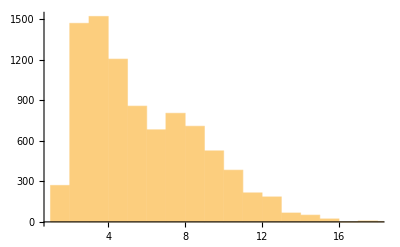

```mathematica
Histogram[StringLength[TextWords[WikipediaData["computers"]]]]
```

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
f@*g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
x//a//b//c//d
```

d[c[b[a[x]]]]

```mathematica
x//d//c//b//a
```

a[b[c[d[x]]]]

```mathematica
Framed/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
ColorNegate/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoGraphics/@EntityList@EntityClass["Country","GroupOf5"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

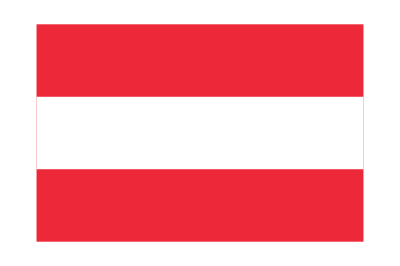
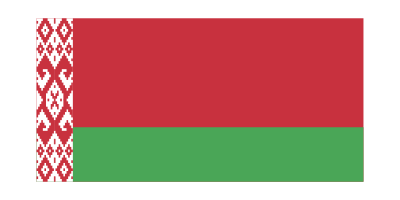
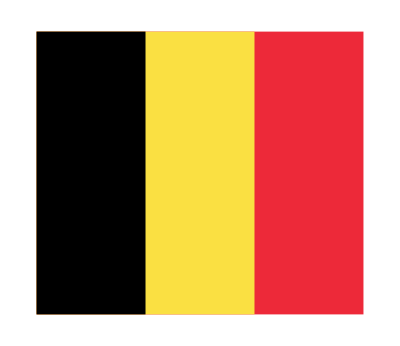
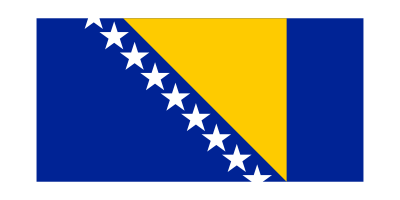
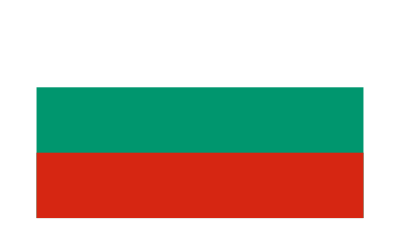
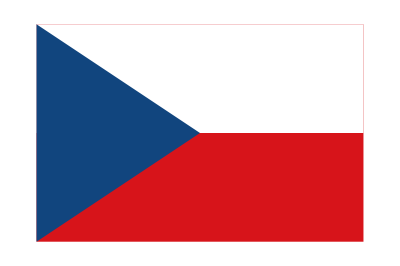
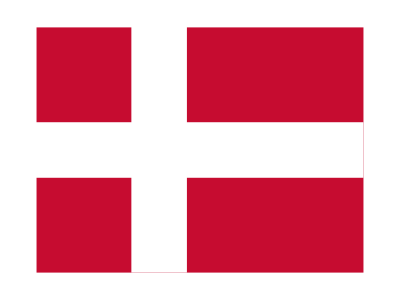
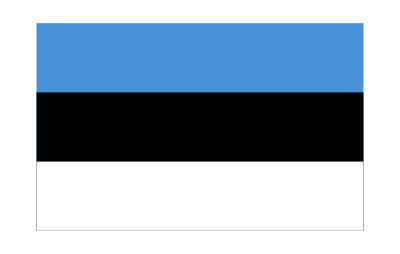


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityClass["Country","Europe"][EntityProperty["Country","Flag"]]
```

```mathematica
Binarize/@EntityClass["Country","Europe"][EntityProperty["Country","Flag"]]//ImageCollage
```

-Graphics-

```mathematica
Column/@DominantColors/@EntityClass["Planet",All][EntityProperty["Planet","Image"]]
```

{GrayLevel[0.0003583326349482438]
GrayLevel[0.5809817026568795]
GrayLevel[0.2568999517211182],RGBColor[0.8853258435338224, 0.6847277936008838, 0.4256700400270567]
RGBColor[0.000642064098966206, 0.0014037306334321756, 0.000741076745930836],RGBColor[0.0024606914773152946, 0.0024097879200276097, 0.0039673926952988985]
RGBColor[0.38137481545229607, 0.40751891622899705, 0.48787187010084493]
RGBColor[0.709369586353396, 0.7271479029748487, 0.8068003802783188]
RGBColor[0.9792341683643001, 0.9822919853218711, 0.9938424909149209]
RGBColor[0.6354966448798469, 0.547993401540665, 0.5436090454839879],RGBColor[0.0012177112422530026, 0.0015444400900931803, 0.002282633031318643]
RGBColor[0.5556976430545663, 0.4531266040635173, 0.3330454215920823]
RGBColor[0.9766143421803483, 0.6748004340563882, 0.36945365634477967]
RGBColor[0.2479853695341303, 0.28139542539507234, 0.26899239922440077]
RGBColor[0.49662186211636067, 0.5143298694495971, 0.5023898427059187]
RGBColor[0.6400489109534753, 0.7400325106312161, 0.8829327113481882],RGBColor[0.0007307443638727919, 0.0007454981889383991, 0.0016562190320313643]
RGBColor[0.6782699732325107, 0.6320729750699731, 0.5998391370238426]
RGBColor[0.8542680796980542, 0.708030218110517, 0.5495188353805759]
RGBColor[0.5603508590091927, 0.4463794024248931, 0.3598178308880452],RGBColor[0.0008759690380522743, 0.000616761123413929, 0.0013660526470624804]
RGBColor[0.3645501164755359, 0.3474409021418892, 0.3008581988199233]
RGBColor[0.6925168887922426, 0.608767018411482, 0.4578034667819321]
RGBColor[0.9019996092281926, 0.7638467049048333, 0.4927253941562712],RGBColor[0.5487856264665472, 0.615474780101897, 0.6457820763462186]
RGBColor[0.002625174628613325, 0.002077245768923338, 0.002466785942829536]
RGBColor[0.2274835700706535, 0.24605670217787023, 0.25518636783414006],RGBColor[0.2377611505192651, 0.3679773297549179, 0.5706318896002792]
RGBColor[0.0007109939277543467, 0.0009022108781584738, 0.0018019525931844001]
RGBColor[0.5017443423181572, 0.5645929303767465, 0.642298675029846]}

```mathematica
LetterNumber["wolfram"]
```

{23,15,12,6,18,1,13}

```mathematica
Total[LetterNumber["wolfram"]]
```

88

```mathematica
#^2&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Blend[{#,Red}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
Framed[Column@{ToUpperCase[#],#}]
```

ToUpperCase[#1]
#1

```mathematica
Framed[Column@{ToUpperCase[#],#}]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
Framed[Column@{ToUpperCase[#],#},Background->RandomColor[]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Table[{i,i["Flag"]},{i,//EntityList}]
```

{{France,-Graphics-},{Germany,-Graphics-},{Japan,-Graphics-},{United Kingdom,-Graphics-},{United States,-Graphics-}}

```mathematica
Grid[Table[{i,i["Flag"]},{i,//EntityList}]]
```

France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
Grid[Table[{i,i["Flag"]},{i,EntityClass["Country","GroupOf5"]//EntityList}],Frame->All]
```

France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
WordCloud@*TextWords@*WikipediaData/@{"apple","peach","pear"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WordCloud@*WikipediaData/@{"apple","peach","pear"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram@*StringLength@*TextWords@*WikipediaData/@{"apple","peach","pear"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoGraphics/@EntityList[EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoListPlot[#,GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
NestList[f[#,#]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

```mathematica
NestList[f[#,#]&,x,4]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]],f[f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]]}

```mathematica
NestList[Framed[f[#,#]]&,x,4]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]],f[f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]]}

```mathematica
NestList[Framed[Column[{#,#}]]&,x,4]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x,x
x
x
x
x
x
x
x
x
x
x
x
x
x
x
x}

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,4]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

```mathematica
NestList[Framed[Grid[{{0,#},{#,#}}]]&,x,4]
```

{x,0 | x
x | x,0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x}

```mathematica
NestList[Flatten[{#,Rotate[#,90°],Rotate[#,270°]}]&,"R",4]
```

{R,{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}}}}

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},5]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1}}

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},9]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1},{1,6,15,20,15,6,1},{1,7,21,35,35,21,7,1},{1,8,28,56,70,56,28,8,1},{1,9,36,84,126,126,84,36,9,1}}

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},9]//Grid
```

1 |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1

```mathematica
NestList[{f[#],g[#]}&,x,4]
```

{x,{f[x],g[x]},{f[{f[x],g[x]}],g[{f[x],g[x]}]},{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]},{f[{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]}],g[{f[{f[{f[x],g[x]}],g[{f[x],g[x]}]}],g[{f[{f[x],g[x]}],g[{f[x],g[x]}]}]}]}}

```mathematica
NestList[Column@{f[#],g[#]}&,x,4]
```

{x,f[x]
g[x],f[f[x]
g[x]]
g[f[x]
g[x]],f[f[f[x]
g[x]]
g[f[x]
g[x]]]
g[f[f[x]
g[x]]
g[f[x]
g[x]]],f[f[f[f[x]
g[x]]
g[f[x]
g[x]]]
g[f[f[x]
g[x]]
g[f[x]
g[x]]]]
g[f[f[f[x]
g[x]]
g[f[x]
g[x]]]
g[f[f[x]
g[x]]
g[f[x]
g[x]]]]}

```mathematica
NestGraph[{f[#],g[#]}&,x,3,VertexLabels->All]
```

-Graphics-

```mathematica
NestGraph[{2#,2#+1}&,0,4,VertexLabels->All]
```

-Graphics-

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->All]
```

-Graphics-

```mathematica
NestGraph[Nearest[WordList[],#,3]&,"hello",4,VertexLabels->Automatic]
```

-Graphics-

```mathematica
NestList[Blur,Rasterize[Style["X",30]],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Framed,Rasterize@Style["A",50],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[Rotate[#,RandomReal[2Pi]]]&,Rasterize@Style["A",50],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[Rotate[Framed[#],RandomReal[2Pi]]]&,Rasterize@Style["A",50],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Rotate[Framed[#],RandomReal[2Pi]]&,Rasterize@Style["A",50],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[4#(1-#)&,0.2,100]
```

{0.2,0.64,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961563,0.147837,0.503924,0.999938,0.000246305,0.000984976,0.00393603,0.0156821,0.0617448,0.23173,0.712124,0.820014,0.590364,0.967337,0.126384,0.441645,0.986379,0.053742,0.203415,0.64815,0.912207,0.320342,0.870893,0.449755,0.989902,0.0399856,0.153547,0.519882,0.998419,0.00631451,0.0250985,0.0978744,0.35318,0.913776,0.315159,0.863335,0.47195,0.996853,0.0125495,0.0495681,0.188445,0.611733,0.950063,0.189772,0.615035,0.947067,0.200523,0.641254,0.920189,0.293764,0.829868,0.56475,0.98323,0.0659554,0.246421,0.742791,0.76421,0.720773,0.805037,0.62781,0.934659,0.244287,0.738444,0.772578,0.702804,0.835482,0.549808,0.990077,0.0393,0.151022,0.512857,0.999339,0.00264312,0.0105445,0.0417334,0.159967,0.53751,0.994372,0.0223857,0.0875383,0.319501,0.869681,0.453344,0.991293,0.0345245,0.13333,0.462213,0.994289,0.0227147,0.088795,0.323642,0.875591}

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

-Graphics-

```mathematica
Nest[1+1/#&,1,30]
```

2178309/1346269

```mathematica
N[Nest[1+1/#&,1,30]]
```

1.61803

```mathematica
NestList[3#&,1,10]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
NestList[(#+2/#)/2&,1.0,5]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421}

```mathematica
NestList[(#+2/#)/2&,1.0,5]-√2
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

```mathematica
NestList[RandomReal[{-1,1},2]+#&,{0,0},1000]
```

{{0.,0.},{0.131878,0.230227},{0.725321,-0.492176},{0.662068,-0.77477},{-0.172866,-0.768709},{-0.162762,-1.56715},{0.456507,-1.30826},{0.00781572,-0.592886},{0.518532,-0.51826},{0.761122,0.355211},{0.557668,0.900018},{0.200366,1.06189},{1.19496,0.0801612},{2.06165,-0.486295},{2.51409,-1.00349},{3.14138,-0.467347},{3.57543,-0.608975},{3.83639,-0.385217},{4.29394,-0.728276},{5.00118,-0.921287},{4.87542,-0.49611},{5.23639,-0.769054},{4.67925,-0.0236463},{4.39561,0.869525},{5.03395,0.0483858},{5.68002,0.430544},{4.78773,-0.497668},{4.46508,0.292937},{4.22465,0.833182},{4.70003,1.60036},{3.81329,2.1562},{4.3479,2.31162},{4.09849,2.77512},{3.80877,1.96155},{4.19599,1.84853},{3.25087,1.1028},{3.29847,0.394189},{3.8763,0.393486},{4.53534,0.186439},{4.19237,0.720617},{4.91376,1.01511},{4.73244,1.14809},{5.11943,1.38225},{4.2945,1.49665},{4.41227,0.566822},{4.57952,0.481822},{5.17713,-0.455055},{4.36808,-0.107353},{5.3366,-0.33255},{5.69218,-1.17872},{6.3413,-1.6991},{7.07733,-2.62087},{7.81661,-2.97185},{8.22844,-2.73434},{8.81212,-2.64358},{7.98446,-3.4438},{7.14258,-2.66418},{6.93517,-3.12256},{7.43305,-2.4127},{7.04285,-2.79424},{7.91435,-3.18565},{8.06893,-2.43152},{7.37877,-2.25776},{6.50005,-1.5971},{7.32504,-1.3541},{6.49111,-0.38591},{5.73065,-0.186969},{5.13441,0.198318},{4.72664,0.488583},{4.00806,1.1321},{3.67823,1.42359},{3.21133,1.85},{3.85593,2.49892},{3.02887,2.92455},{2.37791,3.57397},{2.14329,2.62096},{1.89245,1.81542},{2.36189,2.4547},{3.27834,2.36153},{3.82094,3.00964},{3.87052,2.52732},{3.52906,1.9156},{3.45738,1.77608},{2.60338,1.07287},{1.62372,0.211774},{1.44295,0.0337885},{2.12023,-0.186944},{2.28745,0.434845},{1.7046,-0.0838262},{0.712339,0.873829},{0.817024,0.805257},{0.486105,1.49924},{0.339804,1.28096},{-0.290774,1.36881},{0.352491,0.679172},{-0.0486024,0.315248},{-0.753402,0.978084},{0.0950363,1.84832},{-0.332099,2.20161},{0.162328,1.78916},{-0.273566,1.18514},{0.130367,2.05889},{-0.286496,2.91572},{-0.0949768,3.51878},{-0.226927,4.11978},{0.122228,4.49767},{0.181757,3.98514},{1.04624,3.12935},{0.453977,3.72939},{0.509743,2.79317},{0.8567,2.98132},{1.28243,2.77253},{0.57474,1.8937},{0.721056,1.29868},{1.47739,1.38594},{0.7156,1.11866},{1.18152,0.854269},{1.76543,1.16864},{2.43356,1.22062},{1.4876,0.87553},{1.57453,1.34178},{2.43499,1.99171},{3.15934,1.62872},{3.03279,1.786},{3.8808,2.5759},{4.39619,2.69037},{4.48696,2.62905},{4.52962,1.79016},{5.44417,0.811743},{5.16575,1.48172},{6.01354,0.904378},{6.72725,1.21696},{6.52486,1.35932},{6.84636,0.502134},{7.44586,0.102951},{7.50574,0.212267},{7.16285,-0.00628587},{7.87144,-0.631909},{8.74139,-0.796427},{8.80579,-0.123925},{9.34721,0.433141},{8.78576,0.269217},{8.27767,0.216738},{7.64024,0.678635},{7.81593,-0.286464},{7.42118,-0.032743},{8.22952,-0.528817},{9.08655,-0.728823},{10.0071,0.133712},{10.2488,0.422841},{11.0268,-0.0639183},{11.8555,0.655874},{11.1737,1.18},{11.1298,1.70778},{11.305,1.15446},{11.8575,1.14648},{10.8886,0.87664},{11.7253,1.42624},{11.2665,0.6966},{10.7147,0.00386593},{10.7872,-0.49841},{10.1472,0.329057},{10.9428,-0.558243},{10.6428,-0.384354},{9.96251,-0.575621},{10.2762,-0.665984},{9.63096,-1.00538},{9.52695,-0.284531},{9.22682,-0.424524},{9.33327,-0.755291},{10.111,-1.33183},{9.28917,-1.08774},{8.34159,-0.739831},{8.09866,0.109406},{8.55731,0.0253532},{8.67392,0.784545},{9.25275,-0.1718},{9.03894,-0.976606},{8.98194,-1.8152},{8.25877,-2.79753},{7.39324,-3.62716},{8.28894,-2.75857},{8.16677,-2.69351},{8.11562,-1.72378},{7.39519,-1.09128},{6.59205,-1.6633},{6.35476,-1.97152},{6.44114,-1.61447},{7.30683,-1.84551},{8.28922,-2.831},{7.31778,-2.92677},{6.3377,-3.26045},{6.9939,-4.20565},{6.76496,-5.11932},{6.61118,-5.89044},{6.77957,-5.70271},{6.25997,-6.6983},{5.60592,-5.99275},{4.78702,-6.098},{4.0885,-5.36233},{4.60325,-5.55394},{3.85669,-4.93893},{4.47323,-4.81925},{4.22442,-5.02653},{5.02396,-5.00631},{4.84566,-5.91783},{4.05395,-5.64569},{3.87174,-6.40117},{4.05341,-6.61699},{4.51136,-6.10397},{4.73073,-5.4112},{5.4612,-5.62839},{4.97997,-6.40562},{4.15191,-5.80166},{3.98165,-6.38148},{3.71623,-5.46128},{3.35438,-5.39636},{3.86201,-4.60212},{4.10708,-5.24487},{3.43401,-5.75825},{3.80487,-4.84378},{4.21803,-5.77521},{4.44858,-5.577},{3.92428,-6.18242},{3.66213,-5.4455},{3.1369,-4.76966},{2.76294,-3.96279},{1.94075,-4.77837},{0.999698,-4.36133},{1.66091,-4.62592},{2.45594,-4.62899},{3.19528,-4.45786},{3.46926,-5.07199},{3.8049,-4.76537},{4.31683,-4.67616},{3.55217,-3.73754},{3.00192,-3.58176},{2.68581,-4.10408},{2.75871,-3.99347},{2.31473,-4.338},{1.70236,-5.17011},{2.10707,-5.05722},{2.34733,-5.05492},{1.71923,-4.98969},{1.03458,-5.24094},{1.25041,-5.72101},{2.15102,-6.565},{2.76824,-6.8152},{2.53627,-6.1906},{2.54802,-6.52118},{3.20816,-5.99123},{4.10174,-6.31362},{4.18923,-6.5803},{5.03549,-7.26002},{4.05132,-6.70742},{4.9045,-6.5501},{4.54644,-5.89219},{4.25861,-5.60464},{4.91062,-6.0213},{4.76307,-5.75187},{4.75189,-5.39131},{5.12439,-4.85969},{5.76574,-4.0371},{5.98122,-3.52088},{5.52451,-4.07419},{5.90895,-3.81061},{6.40921,-4.78209},{5.68746,-4.1603},{6.25901,-3.73532},{6.73334,-4.70888},{5.80297,-5.65406},{6.22382,-6.01547},{7.13978,-5.60393},{7.41937,-4.92272},{7.49729,-5.82364},{7.95794,-6.29335},{7.82271,-6.94774},{6.84031,-6.35818},{6.92492,-6.61793},{7.74857,-6.02861},{8.28121,-5.99818},{8.54233,-5.37842},{9.42739,-5.71872},{10.2755,-5.06072},{9.30846,-4.84852},{10.3016,-4.6259},{11.0268,-5.15529},{10.8203,-5.06255},{10.6686,-5.39275},{11.5805,-4.84755},{12.0343,-4.30924},{12.2311,-5.0691},{13.0869,-5.80079},{13.4573,-4.89862},{13.0463,-4.26717},{13.1352,-5.08278},{12.3921,-4.25041},{12.9917,-4.80862},{13.1339,-4.05602},{14.0117,-4.68356},{13.1445,-5.47352},{13.6982,-6.15874},{12.7305,-6.72103},{13.4276,-7.23931},{14.2043,-7.24324},{13.5595,-6.56662},{13.9733,-7.1926},{14.6042,-8.16874},{15.5357,-7.25798},{15.8239,-7.82604},{16.5383,-7.85863},{17.1062,-8.85565},{16.7457,-9.52934},{17.2786,-10.0935},{18.2617,-10.4983},{18.011,-11.2129},{17.6377,-11.7416},{16.6728,-11.2123},{15.6989,-10.5873},{16.0669,-10.5416},{16.8776,-11.3791},{17.1093,-11.8743},{17.9336,-12.1995},{18.3043,-11.6006},{17.8038,-12.4732},{17.1285,-12.8173},{17.942,-12.6355},{18.7949,-12.3341},{19.6163,-13.298},{20.3873,-12.5602},{20.0226,-12.4949},{19.408,-13.2013},{19.5631,-13.8125},{19.917,-13.6403},{19.1994,-14.2366},{19.3482,-14.7963},{18.5904,-15.2394},{18.5177,-14.9299},{17.9799,-14.5936},{18.8032,-15.2633},{18.7844,-14.7054},{18.6269,-14.6949},{18.3292,-15.1647},{18.7415,-14.4057},{18.398,-13.5435},{18.8486,-13.3114},{18.9555,-13.1454},{19.7696,-13.2938},{20.4588,-13.5393},{20.4169,-13.0648},{20.7372,-13.1986},{21.3007,-13.0159},{21.3578,-12.8377},{21.9614,-12.4663},{21.1949,-11.7428},{22.0002,-12.551},{22.7272,-12.3924},{22.4717,-12.1146},{22.1166,-11.8764},{21.4082,-10.9945},{21.7504,-10.8508},{22.1424,-11.7793},{22.1757,-12.5833},{21.2091,-11.9161},{20.7607,-12.1589},{20.0594,-11.9256},{21.0515,-12.1795},{20.9695,-12.2981},{21.947,-11.9742},{22.1901,-12.0227},{21.4573,-12.6778},{20.5274,-12.0684},{19.6589,-11.9398},{19.2164,-11.3843},{20.196,-11.7786},{20.8906,-10.8679},{20.1081,-11.7912},{21.0347,-11.3893},{20.4993,-10.8027},{20.6264,-10.7151},{20.6042,-11.4902},{20.2545,-11.7461},{19.4549,-10.8628},{19.5683,-11.4251},{19.355,-11.8627},{18.825,-12.3834},{18.1272,-13.1011},{18.542,-13.8229},{19.2858,-13.3458},{18.9633,-13.8309},{19.3514,-13.9091},{18.4427,-13.3631},{18.3006,-13.7889},{19.0776,-14.02},{18.9626,-13.93},{19.2766,-14.5838},{18.3955,-14.1418},{17.6954,-14.5681},{17.1239,-15.0305},{16.2961,-14.1912},{17.078,-14.6351},{17.2265,-14.1222},{16.5458,-14.0369},{17.5215,-14.741},{17.7651,-14.2563},{17.312,-14.3904},{16.7225,-14.0809},{17.3245,-14.2445},{18.3054,-14.4621},{18.1874,-15.2255},{18.3045,-15.4645},{19.0105,-15.291},{18.4503,-15.7978},{18.9985,-16.5452},{19.8587,-16.3261},{19.4543,-17.1918},{18.6321,-17.2398},{19.5884,-16.9367},{18.7696,-16.0181},{18.0644,-15.937},{17.5709,-15.2984},{16.9684,-15.167},{17.7816,-14.6133},{18.4944,-14.2839},{18.8394,-13.8209},{19.3405,-13.2521},{20.0036,-13.5857},{20.8194,-13.4095},{20.47,-13.2124},{20.4057,-13.718},{21.2944,-14.3949},{21.3981,-13.7805},{20.5907,-13.2191},{21.1877,-12.6843},{20.5775,-13.5221},{20.8088,-13.2983},{19.9807,-13.7636},{19.3565,-13.5855},{18.9473,-14.5759},{18.5098,-14.2579},{18.8799,-13.8471},{18.1876,-14.4586},{17.7862,-14.6815},{18.0298,-14.078},{18.4913,-15.0189},{18.1631,-14.1205},{18.9182,-14.364},{18.2204,-13.6915},{18.3871,-13.4575},{18.712,-12.6834},{19.0586,-12.3407},{19.8691,-12.1947},{20.5839,-11.67},{21.289,-12.3779},{21.7566,-13.2344},{22.3279,-13.1804},{22.5538,-12.61},{23.2947,-13.5586},{22.589,-13.9259},{22.2867,-13.3558},{22.1995,-13.4796},{22.1231,-14.0883},{22.6486,-14.0385},{23.3074,-14.6888},{22.9411,-15.2866},{23.3795,-16.0366},{23.3676,-15.4639},{22.7238,-16.13},{22.001,-15.1518},{22.2578,-14.392},{21.7919,-14.664},{21.2311,-14.0599},{20.4865,-14.3446},{20.3886,-15.2133},{20.9801,-15.4074},{21.1226,-15.6892},{20.4022,-15.9591},{20.367,-15.8831},{20.1651,-15.2051},{20.2977,-14.3545},{20.5667,-14.1797},{21.4123,-14.7365},{22.1987,-15.0925},{22.0322,-14.8314},{22.1182,-13.9555},{22.6226,-14.7242},{23.0418,-15.1723},{23.7602,-14.2352},{22.9819,-13.9079},{23.5617,-13.2801},{23.8212,-12.9842},{23.8777,-13.8906},{23.1948,-14.1097},{22.9522,-13.936},{22.1639,-14.7285},{22.9546,-15.2088},{22.2286,-15.0332},{22.4664,-15.0384},{21.8319,-15.7706},{20.8734,-14.8644},{20.2489,-13.8879},{19.7623,-13.532},{20.7256,-14.0007},{20.7468,-14.0808},{21.2147,-13.4429},{21.0412,-14.2703},{21.6425,-14.143},{21.9603,-13.7762},{22.0875,-13.2266},{22.1721,-12.5115},{22.7769,-12.88},{22.3488,-11.9894},{21.3658,-12.8848},{21.1206,-12.1168},{21.5962,-11.7879},{20.8192,-11.3435},{21.4599,-10.3766},{20.4957,-10.7392},{21.0384,-10.4042},{21.3976,-9.65803},{21.949,-9.92105},{22.0007,-10.6505},{22.2973,-11.2308},{22.8976,-12.1436},{21.9914,-12.3862},{21.4192,-11.5181},{22.257,-11.7432},{22.4026,-12.6257},{23.0132,-12.111},{22.2873,-11.515},{22.3024,-12.4737},{21.8726,-11.9827},{21.2177,-11.3893},{20.2245,-11.7156},{20.6057,-12.4787},{20.6373,-13.3809},{20.4605,-12.9007},{19.5049,-13.4981},{18.9074,-13.1935},{19.3514,-13.008},{19.3354,-12.9028},{20.305,-11.9993},{20.8646,-12.7286},{21.8392,-13.3516},{20.9596,-13.2822},{21.5595,-12.6853},{21.8702,-12.0373},{21.6291,-11.1376},{21.5271,-11.5153},{21.8494,-11.2733},{20.9585,-11.6587},{21.3581,-11.1314},{21.2196,-11.8434},{21.4413,-11.5323},{22.153,-11.8465},{21.4164,-11.457},{22.0993,-11.5095},{22.93,-10.9827},{22.2291,-10.469},{23.2242,-9.49559},{23.8505,-9.38314},{23.7934,-10.3163},{22.8622,-11.0781},{23.5623,-10.9062},{23.9488,-11.2833},{23.7614,-12.1735},{23.2813,-13.1348},{23.2359,-13.7814},{22.7022,-14.1859},{22.771,-14.5647},{22.7981,-13.7451},{23.132,-13.6258},{22.4318,-13.3804},{22.5986,-13.4491},{23.4379,-12.811},{22.4799,-11.8707},{23.2075,-11.1397},{23.0543,-11.6406},{22.259,-10.8907},{22.5202,-10.0705},{23.4598,-10.2352},{22.6716,-10.5242},{22.1119,-10.3167},{23.0775,-9.37856},{23.0247,-8.42355},{22.344,-8.58624},{22.7717,-7.66779},{22.4667,-8.44021},{22.1704,-8.16556},{23.0629,-7.92252},{23.9247,-6.99973},{24.1274,-7.96341},{23.3439,-7.29623},{23.0193,-7.07907},{23.6277,-6.66671},{22.845,-6.86212},{22.7653,-6.23023},{22.2315,-5.66474},{21.6241,-5.64379},{20.8344,-5.05678},{20.2071,-5.47085},{19.835,-4.62871},{19.7268,-5.24601},{18.7694,-5.76714},{19.121,-5.31904},{18.3356,-5.55426},{17.635,-6.5283},{17.556,-6.30172},{16.8581,-6.53792},{17.4214,-5.76186},{17.5249,-5.03831},{17.8852,-4.90915},{17.0621,-5.19042},{16.2287,-5.15135},{16.3927,-4.96122},{15.4595,-5.13141},{14.4729,-4.528},{15.0314,-4.19766},{15.3796,-3.38319},{15.1828,-3.02145},{14.6786,-3.52209},{14.9215,-3.62575},{14.9933,-4.06239},{15.9545,-3.95386},{16.7133,-3.09773},{17.1252,-2.69756},{16.3192,-2.63389},{15.3617,-1.73935},{15.8845,-1.19258},{16.2147,-2.15949},{16.921,-2.95599},{17.26,-3.92597},{17.3391,-3.16861},{16.7519,-3.06815},{16.248,-2.21856},{16.6484,-1.32749},{15.8211,-1.55131},{16.5138,-1.62307},{17.0588,-1.82509},{17.6567,-1.82182},{18.2441,-0.976101},{17.5078,-0.868099},{17.6618,-1.52234},{18.4821,-2.09707},{17.7522,-1.31332},{16.8654,-0.933946},{17.1676,-0.969212},{16.5884,-1.42346},{16.0129,-0.565039},{15.6674,-0.144402},{15.8094,-0.817972},{15.0359,-0.184},{15.1786,-0.986161},{15.064,-0.866671},{14.8451,0.00868149},{15.2186,0.561511},{15.1402,-0.213896},{14.3334,0.566398},{14.4275,-0.177817},{15.2889,-0.716874},{14.3435,-0.562143},{14.5046,-0.468713},{14.9201,0.279132},{15.7947,0.890407},{16.3988,1.36278},{16.0255,1.70742},{15.8089,0.944664},{15.4408,0.244411},{15.6487,1.14266},{14.9435,1.25194},{15.832,1.69251},{16.7005,1.12868},{16.8103,0.159859},{16.3285,-0.421505},{15.3947,-1.2502},{15.742,-0.494938},{16.4879,0.127926},{17.1329,1.11872},{17.51,1.19158},{17.7452,0.942256},{18.1169,0.183575},{17.9127,-0.782575},{17.0645,-0.706604},{16.5077,-1.48662},{15.5738,-1.3586},{16.5374,-2.20079},{17.1428,-1.39439},{16.8516,-0.791696},{16.3563,-1.51208},{15.7253,-1.3233},{16.395,-0.993446},{16.8066,-1.49731},{16.8929,-0.502747},{16.2727,0.293832},{15.5145,-0.391935},{16.4451,-0.611109},{15.8254,-0.595499},{16.759,-1.09463},{17.7011,-2.08104},{18.2313,-1.46898},{17.9779,-1.50727},{17.9308,-2.39172},{17.9155,-1.57135},{18.2347,-1.68432},{18.8901,-2.26514},{18.9808,-2.60733},{19.1403,-2.22658},{18.1592,-1.52603},{17.4863,-1.83626},{18.0596,-2.54656},{17.4559,-1.74518},{17.2275,-1.0327},{16.3905,-0.766832},{15.8149,-1.52246},{16.1847,-1.25272},{16.6593,-1.72825},{17.6274,-1.51578},{17.9219,-0.655696},{17.5729,-1.41863},{17.3754,-1.07846},{17.3614,-0.176416},{17.2457,0.396357},{17.3238,1.2226},{17.6412,1.71601},{17.2349,2.71042},{18.0284,3.12411},{17.55,4.00408},{17.5433,4.62855},{18.5004,5.61234},{19.1137,5.5125},{18.8633,6.32082},{18.4889,6.26887},{19.2834,6.77097},{19.1837,6.22664},{19.6304,5.68594},{18.7956,5.59563},{18.0409,5.94432},{17.3369,6.20188},{16.725,6.55894},{16.508,7.46816},{15.8745,7.07646},{15.4367,7.52432},{14.9564,7.11848},{15.9015,6.3343},{16.1397,7.31318},{15.5639,7.03838},{14.8476,6.37189},{15.4112,6.05981},{14.6547,6.25818},{15.5694,5.31292},{15.9249,4.91762},{15.9266,4.83171},{16.9071,3.87232},{16.4205,3.77894},{16.3261,4.43425},{17.0301,4.12676},{17.6635,4.83958},{16.7083,5.37686},{17.3993,5.7484},{16.6184,6.39118},{16.1992,6.16088},{15.6247,6.25364},{14.8908,6.9094},{13.9443,7.58023},{14.192,6.68785},{13.9974,6.95186},{13.1463,7.41613},{13.7392,8.11526},{14.0006,9.02721},{13.0322,9.4088},{13.2432,9.19972},{13.2688,10.0773},{13.5177,10.6598},{14.2252,10.4344},{14.631,9.53294},{14.6819,8.63129},{13.9773,8.86982},{13.311,9.01634},{12.9347,9.66447},{13.2835,10.3376},{13.5529,9.49354},{14.2629,8.55286},{14.65,7.84426},{14.379,7.00126},{14.5301,7.17138},{15.3942,7.30112},{14.7237,7.00478},{15.544,6.44873},{15.4165,6.49713},{14.9696,6.83104},{14.8748,7.1089},{14.6601,6.12329},{14.3583,6.5168},{13.6793,5.99452},{14.4573,6.90026},{14.8493,6.24478},{14.8617,5.48158},{15.4692,5.84244},{16.1514,6.70336},{15.4713,7.26875},{14.6975,6.69518},{14.9472,7.50073},{15.8461,7.8866},{16.1638,8.62533},{16.5422,9.48735},{16.5527,8.5951},{16.6978,8.36996},{17.0319,8.93683},{16.6381,8.00426},{16.5003,7.72349},{16.9829,7.00646},{16.3983,7.10111},{16.0013,7.85811},{16.1749,8.29309},{16.8679,9.05772},{16.7899,9.15187},{17.1547,9.82729},{17.1376,10.6134},{18.0772,10.4197},{18.5008,9.53631},{18.0145,9.0332},{18.0551,8.25256},{18.4485,8.93537},{18.729,8.41685},{17.7508,8.73885},{16.8882,8.2966},{17.1701,8.64858},{16.663,8.53075},{16.2541,8.84328},{15.762,8.30807},{15.1375,7.3269},{14.9159,6.86691},{14.0908,7.77214},{14.1235,8.21231},{13.7909,8.6992},{14.4667,8.53108},{15.2955,9.00164},{16.1598,8.97791},{15.5943,8.17336},{16.5416,8.46663},{16.9759,9.21802},{16.84,8.4509},{16.4615,8.269},{15.8001,8.10058},{15.3634,9.09041},{15.8989,9.77029},{16.2075,9.23848},{15.6375,8.30113},{16.4929,8.45103},{15.647,8.95931},{14.9146,8.60106},{15.9032,8.68047},{15.5392,8.11238},{16.1479,8.8542},{15.6276,8.50637},{15.4101,8.96001},{15.6106,8.0905},{15.9565,8.41751},{16.1265,8.00428},{15.928,7.80904},{15.0807,7.16201},{14.5092,6.90253},{14.9553,6.35492},{14.3691,5.98594},{14.2215,6.72317},{14.0719,6.34439},{13.5712,6.93684},{12.825,6.10796},{13.0305,6.23993},{13.785,6.24573},{13.495,5.66167},{13.7256,6.57462},{13.5294,6.31857},{13.3799,5.56296},{13.2907,6.42997},{13.043,5.47395},{12.0809,4.9857},{12.6529,4.07362},{13.4789,3.67763},{13.6702,3.08418},{14.3393,3.33418},{15.1628,3.44317},{16.0067,4.09818},{16.2242,4.02985},{16.1444,3.26174},{15.8981,3.04217},{16.5331,3.3983},{15.8848,3.75737},{15.7072,2.89568},{14.8962,2.99733},{14.4178,2.42745},{13.4304,2.72381},{13.131,3.6712},{12.4205,2.7121},{11.4377,2.11494},{11.8088,2.56848},{12.5125,3.23209},{13.1489,2.93462},{12.421,3.84467},{13.3623,3.24247},{12.7545,3.93428},{11.9938,3.01964},{11.4077,3.72221},{12.2632,4.21079},{11.9372,4.71814},{12.4264,5.18993},{11.5059,4.44382},{10.933,4.16703},{11.9203,4.09552},{12.5042,4.68079},{12.9235,5.40354},{12.5225,4.78565},{11.5692,4.50286},{11.3817,4.85962},{10.415,4.07176},{10.4097,4.93805},{9.63156,5.72606},{9.33535,5.02714},{10.2242,5.78331},{9.59046,6.09679},{8.81028,5.68705},{8.0782,4.8729},{8.22159,5.85822},{8.61895,6.02821},{9.36526,5.4004},{8.79973,5.28534},{9.42348,6.26875},{9.17947,6.96976},{10.1196,6.00882},{9.63656,5.97328},{9.41381,5.4358},{10.1814,4.98144},{10.3918,5.17295},{10.6457,5.75908},{10.4082,6.51161},{10.8807,6.40284},{10.3661,5.6901},{10.2305,5.57154},{9.77446,5.12556},{10.5901,5.10726},{10.6819,4.62243},{10.9472,3.81466},{10.9689,4.1321},{10.7925,3.90022},{9.88238,3.04601},{10.2061,2.38457},{10.8642,1.59651},{10.1531,1.56238},{10.0131,1.11493},{10.864,1.94711},{11.7683,1.2817},{11.0593,1.19373},{10.3947,0.821864},{11.0268,1.56056},{10.9064,0.778474},{11.0491,0.309202},{10.3768,-0.624498},{10.3798,-0.976577},{11.0792,-0.615522},{10.7095,-1.55728},{9.9094,-1.92946},{10.7776,-2.07291},{11.3372,-3.00226},{11.9947,-3.68331},{12.2358,-3.46109},{12.8532,-4.37414},{13.2874,-3.48084},{13.1672,-3.99064},{12.3982,-3.9099},{11.9977,-3.67859},{11.0387,-3.62348},{10.6569,-4.5578},{10.0075,-4.38568},{9.73242,-5.09011},{10.5598,-5.42656},{10.7938,-5.84604},{10.8906,-5.05629},{11.5787,-4.37398},{10.8826,-4.17804},{10.5179,-3.65477},{10.0801,-4.20966},{10.7252,-3.76447},{9.93924,-3.96638},{10.93,-3.69984},{10.7192,-3.7642},{10.1586,-3.46034},{10.7046,-2.78616},{10.327,-1.92933},{10.4607,-2.02662},{10.7379,-1.09927},{11.2694,-2.03091},{11.0157,-2.72179},{10.0546,-3.55492},{10.9321,-4.06414},{11.9146,-4.43124},{12.165,-3.96387},{11.247,-3.56568},{10.2763,-3.83822},{10.2702,-3.98348},{9.44071,-3.31324},{9.15055,-3.44485}}

```mathematica
Line[NestList[RandomReal[{-1,1},2]+#&,{0,0},1000]]
```

Line[{{0.,0.},{-0.512575,0.391921},{-0.719351,-0.0426833},{-0.134892,0.260383},{0.312797,-0.726453},{-0.299133,-0.587986},{-1.23586,-1.23969},{-1.41632,-1.43254},{-1.52423,-2.32748},{-1.8798,-3.24426},{-1.62684,-2.88792},{-2.40676,-3.88082},{-2.47365,-3.27999},{-2.79201,-4.12768},{-2.39956,-4.13045},{-3.1862,-4.4804},{-3.31348,-3.59372},{-2.92411,-3.3385},{-2.07797,-4.04161},{-2.08262,-4.78962},{-1.65516,-5.379},{-1.1008,-5.12123},{-1.76814,-4.12789},{-1.29738,-3.43281},{-1.39318,-3.12399},{-1.42062,-3.27385},{-1.07323,-2.76723},{-1.654,-2.86956},{-1.28034,-2.34621},{-1.30004,-2.22432},{-0.849863,-1.32261},{-0.147569,-1.48535},{-0.900108,-2.47066},{-0.941246,-3.04717},{-1.10973,-3.07513},{-1.30909,-2.89617},{-1.18929,-2.3894},{-1.12461,-1.69182},{-0.39741,-1.96946},{-1.34201,-1.54986},{-1.65344,-1.93083},{-0.655807,-2.71357},{-0.0377893,-2.24089},{0.452101,-1.92435},{-0.357501,-1.94576},{-0.31447,-1.1195},{-0.833089,-1.22099},{-0.871316,-2.07562},{-0.702993,-2.55677},{-1.06651,-2.21941},{-0.577752,-2.7104},{0.308155,-1.8645},{-0.265291,-1.69914},{-0.558285,-2.017},{-0.759717,-1.21097},{-0.708064,-1.89932},{-0.0202003,-1.70732},{-0.185512,-1.48196},{0.3033,-0.871943},{0.929768,-1.39245},{0.324765,-1.75799},{1.14677,-1.9734},{1.53155,-2.56246},{2.35157,-3.35512},{3.0244,-2.50383},{3.69772,-2.59927},{3.55358,-3.25118},{3.2679,-3.54871},{3.59868,-4.4034},{3.86301,-4.60146},{4.779,-4.32905},{4.02547,-4.40633},{3.60515,-3.70061},{4.30437,-3.11096},{4.61426,-2.43488},{4.94881,-1.8406},{5.36135,-1.08221},{6.05307,-1.16392},{6.01217,-1.49475},{6.62927,-0.522547},{6.80173,-1.15672},{6.11571,-0.759425},{5.57949,0.146633},{6.06957,0.0879266},{5.51294,0.0999176},{5.22735,0.0150664},{4.59891,-0.321723},{4.20816,-1.09085},{4.655,-0.642386},{3.75764,-1.4271},{3.07815,-2.30217},{2.64653,-2.03742},{2.33793,-2.8409},{2.50977,-2.99824},{2.89118,-3.38805},{2.17157,-3.12277},{2.1659,-3.8044},{1.59015,-3.92999},{0.939057,-2.956},{1.75794,-2.94686},{1.95206,-3.43362},{2.61478,-2.58036},{3.41514,-2.60107},{4.23169,-2.51785},{4.20488,-2.67471},{4.2107,-2.03946},{5.05726,-2.77382},{5.1443,-3.49966},{4.15244,-2.5904},{4.86682,-2.13157},{4.13596,-2.18735},{3.48231,-2.8856},{2.75607,-1.89393},{3.13935,-2.80224},{2.28641,-1.83101},{2.67665,-0.956603},{3.33533,-1.44308},{4.16427,-0.938976},{4.44753,-1.42428},{3.5498,-1.52954},{3.68082,-2.52911},{4.38445,-1.79677},{5.29399,-2.71467},{5.21004,-2.15839},{6.02446,-2.03054},{5.65398,-2.22894},{5.84205,-2.2873},{6.46958,-2.7485},{7.39729,-2.11944},{7.77424,-1.2117},{8.3568,-1.53778},{9.19277,-1.45442},{8.59749,-0.85068},{8.98895,-1.58739},{8.56902,-0.884115},{8.45068,-1.62825},{8.85367,-1.11608},{8.01567,-1.56464},{7.81204,-1.878},{8.67704,-1.4272},{8.31718,-1.4126},{8.22517,-2.07498},{8.94291,-1.46194},{9.01726,-0.739197},{8.60094,-0.807198},{9.05489,0.144437},{8.34072,0.348949},{8.46349,0.65214},{8.83596,0.184868},{8.01808,-0.0272885},{7.73093,0.947285},{8.4875,1.73378},{9.30708,1.67603},{8.77911,1.92215},{8.18064,2.32358},{8.80498,1.5074},{9.18956,1.72697},{9.15252,0.832789},{8.87813,0.723219},{8.06277,0.938521},{8.33614,0.209118},{9.30049,0.803077},{8.87876,1.77035},{9.20951,2.7049},{8.30272,3.33795},{9.30052,3.35161},{9.0689,2.61392},{8.87459,3.43245},{7.89542,2.46358},{8.77437,3.04172},{8.54795,3.89113},{9.00942,4.53445},{8.48709,5.12579},{7.78978,4.85875},{7.28189,5.63876},{6.29477,5.46489},{6.59424,5.378},{7.06606,6.04749},{7.15827,5.52581},{7.40284,6.3579},{6.6137,5.67593},{5.91187,6.57117},{5.24199,5.76301},{4.49318,6.17092},{4.71664,5.36031},{5.43832,5.64158},{6.27077,5.78186},{6.33633,5.25149},{6.47938,4.68902},{6.7736,4.53949},{6.28244,4.1043},{5.67607,3.44772},{6.17939,3.35145},{5.65766,3.60144},{5.61003,3.22879},{5.79179,2.28687},{5.65448,3.20834},{5.4785,3.66303},{4.67925,3.24266},{4.64538,2.31841},{5.58529,2.86832},{5.18575,1.87269},{5.05509,2.21239},{5.20822,2.55272},{4.52504,2.96913},{3.68194,2.58982},{4.05365,3.24527},{4.37633,2.66209},{4.3925,2.42416},{4.69362,2.96677},{4.71386,2.64099},{5.65429,1.90857},{5.64371,2.16218},{5.49073,2.41975},{5.69256,1.5541},{5.87298,1.91759},{5.54871,2.07587},{6.10376,1.92851},{6.89575,1.1654},{6.74986,1.74757},{7.50694,0.989139},{6.87374,1.90735},{6.79229,2.02512},{6.04268,1.59416},{6.54147,1.0333},{7.48451,1.6355},{8.36562,2.27065},{7.7148,1.2866},{7.84431,1.93723},{7.60172,2.52032},{7.62485,3.22234},{8.49833,2.46079},{8.25729,3.10036},{7.31281,2.31015},{6.9782,1.74868},{7.72981,1.23875},{7.21366,2.00247},{6.25782,2.06685},{5.44483,2.10838},{6.13384,3.06889},{5.69771,4.02683},{6.67505,4.17727},{6.30122,3.66239},{5.89369,2.84258},{5.56209,3.10181},{6.08535,3.59574},{6.31923,4.12105},{6.19999,4.01133},{6.37356,3.244},{5.88006,4.19543},{6.61107,4.0464},{7.35875,4.44585},{7.47328,4.79292},{7.19987,5.26054},{7.41114,5.10442},{7.50573,5.95688},{7.98399,5.79792},{8.06255,6.10814},{7.63917,5.92939},{7.26405,5.62541},{6.31806,6.05633},{6.72699,5.22184},{7.72577,4.22534},{8.54483,3.32776},{7.60812,3.67427},{7.45339,4.41858},{8.11543,4.86638},{8.59987,5.62184},{7.78546,6.19041},{7.88431,6.14791},{7.73272,5.1627},{8.08263,4.67432},{8.74812,3.75152},{8.71187,2.79459},{9.38488,2.79864},{9.2084,1.97632},{9.97574,1.26743},{9.10973,1.18399},{9.32179,0.588528},{8.52014,0.655128},{7.57236,1.48778},{7.49165,1.97971},{7.42183,1.05418},{7.72329,0.710945},{8.18408,-0.215085},{7.32468,0.19695},{7.28043,-0.0425625},{7.90828,0.551459},{6.92028,-0.318652},{6.04799,-1.28504},{5.49723,-1.15917},{5.30692,-2.00186},{4.4903,-2.51794},{3.58547,-2.37217},{4.22911,-2.95337},{4.54461,-3.47256},{3.90068,-2.87375},{3.00104,-1.9697},{3.48565,-2.54801},{2.52465,-2.3718},{1.66375,-1.47837},{1.69785,-1.99039},{2.00479,-1.58277},{2.0892,-1.01206},{1.28833,-0.796946},{1.12611,-0.442848},{1.39354,-1.08119},{0.630874,-1.0547},{0.599884,-0.683063},{0.0241538,-1.15636},{-0.0841597,-0.363207},{0.912151,-0.0239307},{1.37493,-0.637836},{1.93448,-0.565274},{1.46087,-0.640131},{1.36915,-1.18347},{1.258,-0.281908},{0.298478,-0.891797},{0.204089,0.0685943},{-0.112021,-0.590365},{-0.721179,-0.928514},{-0.762977,-0.595047},{-0.191899,-0.0123341},{-1.13494,0.921527},{-1.81409,0.365871},{-2.45171,1.27651},{-1.50555,0.930256},{-1.81625,0.0363691},{-1.49614,0.806146},{-1.687,-0.05371},{-1.66067,-0.246472},{-0.724718,-1.03812},{-0.223416,-1.46784},{-1.07625,-1.81259},{-1.00785,-2.2921},{-1.07012,-2.55213},{-0.912084,-3.07785},{-0.666545,-3.9014},{-1.46271,-3.81964},{-2.38528,-3.12425},{-1.9096,-3.19652},{-0.919687,-3.4365},{-1.86636,-2.84922},{-2.8021,-3.76899},{-3.2043,-4.24181},{-2.42952,-4.30452},{-2.86937,-4.16479},{-2.7678,-3.61813},{-2.5084,-3.65369},{-3.47353,-3.35458},{-3.67676,-2.60209},{-2.94302,-2.85033},{-3.73478,-2.81456},{-3.66847,-2.1982},{-4.1856,-1.5089},{-3.88185,-2.26702},{-4.50692,-2.58161},{-3.51306,-2.60792},{-3.65103,-2.29866},{-3.31399,-3.08856},{-3.96684,-2.10883},{-3.14594,-2.00528},{-3.98425,-2.89356},{-3.98668,-2.49298},{-3.37449,-2.80214},{-3.96933,-2.85534},{-3.47453,-3.70879},{-4.07466,-4.02523},{-4.64188,-3.20694},{-4.31619,-3.0309},{-4.77118,-3.20701},{-4.528,-3.3406},{-3.98219,-3.58001},{-4.6405,-3.56782},{-4.7662,-3.22449},{-5.43738,-2.73673},{-5.93246,-3.05207},{-5.74327,-2.26005},{-4.84196,-2.19035},{-5.40728,-2.03814},{-4.98197,-2.72827},{-4.75433,-1.77592},{-4.61341,-2.75696},{-5.31057,-2.87595},{-6.01645,-2.8552},{-6.64652,-2.75622},{-6.14732,-2.71556},{-6.89045,-1.99209},{-7.15857,-2.18886},{-6.92686,-1.90074},{-7.85236,-1.92873},{-6.86415,-0.931011},{-7.16495,-1.19405},{-7.62711,-0.681408},{-7.61154,0.19653},{-8.2557,-0.689787},{-9.1565,-1.10665},{-10.0523,-2.01966},{-10.1568,-2.73091},{-9.26486,-3.07441},{-8.85929,-3.54585},{-9.73607,-3.81785},{-9.98244,-3.90148},{-9.48526,-3.45764},{-8.60593,-3.25049},{-8.07296,-2.48059},{-9.01741,-2.30659},{-9.06479,-2.20563},{-9.74202,-2.32681},{-9.11171,-1.95198},{-9.3884,-2.61861},{-8.99651,-2.93483},{-8.75209,-3.75947},{-7.83357,-3.98244},{-8.01379,-3.91237},{-7.06221,-3.94786},{-6.49742,-4.19041},{-6.09225,-4.88501},{-6.75674,-4.42362},{-6.08277,-4.08298},{-7.00613,-4.07887},{-7.28407,-3.67733},{-7.41,-2.97532},{-7.11309,-3.27205},{-6.3592,-2.75567},{-5.81096,-3.34793},{-5.81643,-3.36077},{-6.08615,-3.795},{-6.42206,-3.24702},{-7.13554,-2.43958},{-6.62831,-1.46212},{-5.94866,-2.15229},{-6.27479,-1.82974},{-7.26228,-1.11064},{-6.39263,-0.250318},{-6.3261,-0.226996},{-5.6172,-0.146647},{-5.95962,0.422954},{-5.70059,0.623679},{-4.84482,0.0303908},{-4.42481,-0.0101025},{-4.23027,0.0808852},{-3.75504,1.02442},{-4.31172,0.736699},{-3.92437,1.22921},{-4.16797,1.77311},{-3.44173,2.43873},{-4.30465,2.72472},{-5.27796,1.99267},{-4.58802,1.09872},{-4.61425,0.530204},{-4.45451,0.657596},{-4.58386,-0.0381971},{-4.13376,-0.571689},{-4.48637,-0.186574},{-4.16337,-0.89385},{-4.93696,-1.46432},{-5.90978,-2.42772},{-5.67838,-1.7685},{-5.13289,-1.17909},{-4.36961,-1.1849},{-3.8108,-1.26185},{-3.08066,-1.7207},{-2.51879,-2.49169},{-2.57305,-3.30784},{-2.86804,-2.77445},{-2.31077,-2.42032},{-2.36407,-2.58213},{-2.08612,-1.94073},{-2.04623,-1.08317},{-2.6466,-0.919537},{-1.71467,-0.370729},{-2.11639,-1.25771},{-3.07021,-1.77551},{-3.57614,-0.956618},{-4.05283,-0.161208},{-4.64956,-0.690786},{-4.44222,-0.868361},{-4.36773,-1.84172},{-5.14799,-2.81996},{-5.64675,-2.5561},{-5.60554,-3.40956},{-5.69646,-2.90572},{-6.53481,-2.31817},{-6.66699,-2.49571},{-7.0949,-2.01929},{-7.52444,-3.01214},{-7.47359,-3.71175},{-6.57845,-2.81686},{-6.93835,-2.23176},{-7.5701,-1.58283},{-7.27738,-1.61339},{-7.5211,-1.05464},{-6.85467,-0.135476},{-7.6067,-0.395658},{-8.49392,0.462202},{-8.99952,0.583984},{-8.37899,-0.0975647},{-8.91008,-0.684084},{-9.07341,-0.328016},{-9.92107,0.263333},{-10.6379,0.770591},{-10.0077,1.35877},{-9.32121,1.31083},{-8.32496,0.855974},{-8.78698,1.1995},{-8.14319,1.07626},{-9.04022,1.93079},{-9.15307,2.1946},{-9.67389,2.07829},{-9.73809,2.44017},{-10.0207,2.73348},{-10.75,2.15172},{-11.5444,3.03563},{-11.2635,2.14894},{-11.2419,1.30932},{-11.4962,1.61541},{-10.9025,2.61134},{-10.3322,3.37999},{-10.962,3.54544},{-9.97372,2.90484},{-10.8101,2.5608},{-11.6932,3.43372},{-11.311,4.29167},{-11.9262,3.95031},{-12.2741,3.12577},{-11.4505,3.6395},{-10.4635,3.83759},{-10.5895,3.668},{-11.0657,3.01799},{-11.2042,2.0333},{-12.0912,1.26259},{-11.2225,1.26952},{-12.2201,1.25537},{-11.8438,1.05312},{-12.1935,1.29098},{-12.3624,1.63343},{-11.7005,1.87917},{-11.4541,2.8518},{-11.8208,1.91696},{-12.6206,1.50017},{-12.8111,1.26661},{-13.1513,1.58352},{-12.9647,0.817081},{-12.6511,1.41855},{-12.8984,1.22159},{-13.6293,0.828497},{-14.4927,0.392178},{-15.3,-0.319667},{-15.9808,0.462166},{-15.1843,-0.0538314},{-15.2221,-0.954303},{-14.5876,-1.87419},{-14.3885,-2.0936},{-13.7538,-2.45604},{-14.3796,-1.72707},{-14.3501,-2.18182},{-15.096,-1.89182},{-15.3936,-1.85643},{-14.6254,-1.91798},{-15.589,-0.929167},{-14.7403,-1.48241},{-14.2169,-0.863167},{-13.766,-0.760789},{-13.2427,-1.06541},{-12.9107,-1.32428},{-12.2681,-0.851808},{-12.1686,-1.35022},{-12.4477,-2.20611},{-12.2986,-2.32609},{-12.9055,-1.41837},{-13.2394,-1.45317},{-14.1252,-1.65721},{-13.1564,-0.969378},{-12.9114,-1.51014},{-13.5186,-2.45578},{-12.8337,-2.57989},{-13.6571,-2.90129},{-14.0859,-3.17795},{-14.9953,-4.15846},{-14.5353,-3.81119},{-14.492,-2.92748},{-14.542,-2.11629},{-14.4794,-1.21617},{-13.5416,-0.38152},{-12.7125,0.409605},{-12.0816,-0.071497},{-11.3572,-0.384009},{-11.5916,0.599462},{-12.0966,1.0601},{-12.0659,1.76962},{-12.6678,1.76309},{-13.6009,2.56626},{-13.8985,2.46759},{-13.7234,2.63622},{-13.0108,2.19559},{-12.6378,2.59875},{-12.4715,2.01114},{-12.7375,1.65449},{-12.8018,1.6445},{-13.6016,1.00033},{-14.2215,0.88993},{-13.4029,0.223901},{-12.8208,0.410933},{-12.0943,0.0246569},{-13.0928,-0.48604},{-12.6494,0.000924551},{-12.2452,-0.750095},{-11.5712,-0.254587},{-11.9501,-1.25088},{-11.4799,-1.33859},{-11.3416,-1.11708},{-11.305,-1.27037},{-10.3486,-1.75314},{-10.0802,-1.87666},{-10.5817,-1.11885},{-11.0917,-0.386455},{-11.8481,0.462188},{-12.3198,1.30853},{-13.2252,2.21303},{-14.0815,2.23204},{-13.7066,1.67286},{-13.1926,2.35625},{-12.2764,2.06689},{-11.6093,3.03131},{-11.1703,2.83536},{-11.986,2.02643},{-11.4798,2.58041},{-10.8359,1.88983},{-10.2869,0.971183},{-10.1867,0.757681},{-9.84699,1.1759},{-10.2612,0.490268},{-9.71672,0.660394},{-10.274,0.216639},{-11.0625,-0.577749},{-10.2664,-0.109976},{-10.2466,0.116778},{-9.79542,-0.817882},{-9.05856,-0.902054},{-8.86781,-0.94055},{-8.01203,-0.024033},{-8.80806,0.766728},{-9.25935,1.1209},{-8.91094,2.07174},{-8.70913,2.12482},{-9.51466,1.28108},{-9.67085,0.475437},{-10.233,0.406313},{-10.3448,0.393087},{-9.84058,1.05748},{-9.30773,1.9335},{-9.73136,2.04858},{-9.98187,1.2549},{-10.3702,2.13863},{-10.4228,1.64317},{-10.785,1.38108},{-9.8781,1.93366},{-9.74585,1.91791},{-9.00072,2.82622},{-9.03312,2.189},{-9.11921,2.96337},{-8.50951,2.04829},{-9.49697,1.23496},{-9.07894,1.65643},{-8.9489,1.13427},{-8.90034,1.54648},{-9.66915,2.23972},{-10.1341,2.05057},{-9.76755,1.78209},{-9.21248,1.12256},{-9.26001,1.49034},{-10.216,2.34669},{-9.69691,2.84139},{-9.73116,2.96148},{-8.88577,2.18695},{-9.04364,2.26328},{-8.58166,3.24184},{-9.17701,2.91092},{-9.60273,2.26593},{-9.07133,2.87999},{-9.53123,2.54267},{-8.83922,3.26962},{-8.38824,3.3792},{-9.24809,4.30876},{-8.70371,4.4459},{-8.95885,5.0181},{-8.0844,4.83013},{-7.09045,4.85561},{-7.85678,4.13647},{-8.21421,3.38063},{-7.60797,3.21002},{-7.75263,3.85496},{-8.07045,4.65366},{-8.39588,4.30155},{-7.94696,3.8004},{-7.11566,3.43},{-6.87341,2.65967},{-6.28538,2.13123},{-7.17853,2.82282},{-6.24183,2.28739},{-6.25089,2.7689},{-7.14132,3.72089},{-8.06995,4.34844},{-8.40039,4.67419},{-8.54757,4.95098},{-7.74159,4.69508},{-7.88533,5.62385},{-7.5701,5.98501},{-8.08288,6.26583},{-7.46071,6.12245},{-7.95015,5.42519},{-8.25618,6.15992},{-7.40346,6.06852},{-7.77627,6.36859},{-7.86149,7.12568},{-7.47712,6.94926},{-6.60223,7.57632},{-5.94282,6.90892},{-5.88029,7.0091},{-6.26914,6.14562},{-5.50664,5.25852},{-4.50693,5.85384},{-5.38623,5.85321},{-6.22549,4.90216},{-5.50434,4.66309},{-5.88572,3.78494},{-6.06838,4.45462},{-5.90556,4.76548},{-6.02116,5.46549},{-5.61423,4.65633},{-6.07466,4.56835},{-6.28459,5.02521},{-7.26793,4.24749},{-6.66792,3.84009},{-6.1815,3.82693},{-6.05727,3.50671},{-5.26786,3.13407},{-5.66689,2.57019},{-6.56575,2.34407},{-6.75667,2.51628},{-7.01625,3.12581},{-6.12557,3.8566},{-7.05748,3.30913},{-6.31452,3.9259},{-6.8151,3.54476},{-6.2853,4.04787},{-6.10951,3.96245},{-6.36088,3.5025},{-7.02166,2.84989},{-7.91496,2.23332},{-8.24976,1.32795},{-8.18323,1.58018},{-8.34985,2.17199},{-7.86102,2.51742},{-8.00125,2.21014},{-8.24275,2.83959},{-7.52149,3.37811},{-7.14139,2.70677},{-8.11176,2.98412},{-8.91034,3.43801},{-9.68544,2.60535},{-9.05318,1.8427},{-9.05186,1.0517},{-10.0217,1.13101},{-9.41285,1.48337},{-9.32139,1.25921},{-8.51379,0.59556},{-8.0062,1.04402},{-9.0019,0.510592},{-9.83871,1.18221},{-10.3448,0.290026},{-11.2948,0.568156},{-11.739,0.745058},{-11.3593,0.52546},{-12.2309,0.255049},{-11.8743,0.125592},{-11.2706,-0.252088},{-11.4686,0.686195},{-11.9894,1.47321},{-12.3368,2.12582},{-11.4119,1.1802},{-11.4142,0.949405},{-12.2336,1.49647},{-12.4614,0.658116},{-12.846,-0.0292513},{-13.0504,-0.444858},{-12.7645,-0.112373},{-13.5498,0.457005},{-14.4881,0.630077},{-15.2571,-0.339064},{-16.0492,0.266551},{-16.8205,0.522345},{-16.8658,0.674246},{-16.6,1.07193},{-17.2992,2.04065},{-16.4256,2.45284},{-15.6605,3.43357},{-15.2724,3.02121},{-15.6254,2.28135},{-15.1288,1.42029},{-16.0367,2.30571},{-15.6904,2.7374},{-15.7698,2.63872},{-16.255,3.51222},{-16.5613,2.85794},{-17.0899,3.10995},{-16.4625,2.36431},{-16.5984,3.01587},{-17.0282,2.0892},{-17.8826,1.8515},{-18.1411,1.2908},{-19.0137,0.937553},{-19.2451,0.446661},{-19.2074,1.42515},{-19.5175,1.33668},{-19.5671,1.75933},{-19.2083,1.86936},{-19.7449,1.04588},{-19.7723,0.86325},{-19.0117,1.26273},{-19.0849,0.54115},{-19.5341,0.0268381},{-18.6353,0.338907},{-18.1672,-0.516773},{-17.936,0.386434},{-18.7192,-0.269231},{-19.1367,-0.982558},{-19.5842,-1.50129},{-19.508,-0.8721},{-19.5977,-1.26657},{-20.1253,-1.91279},{-20.2368,-1.26647},{-21.0209,-1.85755},{-20.5436,-1.31277},{-21.4706,-1.84197},{-20.6495,-2.71596},{-21.2417,-3.33194},{-20.9327,-4.143},{-20.3087,-4.35205},{-19.7509,-4.25939},{-20.5541,-4.67758},{-20.4151,-5.38982},{-19.8398,-5.29371},{-19.7395,-5.55176},{-20.2277,-5.27769},{-20.9936,-6.12748},{-21.1219,-6.97047},{-20.9552,-6.25479},{-20.661,-6.49524},{-21.5099,-5.73786},{-21.0732,-5.56848},{-20.535,-6.53512},{-20.6174,-6.16114},{-19.7437,-6.60485},{-19.1986,-7.00627},{-19.9376,-7.15071},{-20.6245,-7.31895},{-20.9352,-6.87376},{-20.4776,-7.40639},{-20.4592,-7.90567},{-19.616,-8.39455},{-18.6729,-8.5358},{-19.1055,-8.62256},{-19.9022,-8.88567},{-20.1025,-8.87565},{-20.9075,-8.61198},{-21.65,-8.02041},{-20.8056,-8.03465},{-19.8627,-7.54152},{-19.7509,-7.38473},{-20.5034,-8.33202},{-21.3653,-7.93703},{-20.7761,-8.24756},{-20.1198,-9.11204},{-20.8637,-9.42115},{-20.3888,-9.39953},{-20.9808,-9.74865},{-21.9691,-10.1032},{-22.7053,-9.79567},{-23.3463,-9.14404},{-23.0332,-9.78229},{-22.51,-8.91309},{-21.8208,-9.14714},{-20.9232,-9.25281},{-20.4058,-9.48949},{-21.347,-8.77114},{-21.6851,-8.53643},{-20.8067,-8.447},{-19.8974,-7.54228},{-19.0024,-7.05171},{-19.5843,-7.16022},{-19.9522,-6.75175},{-19.074,-7.00961},{-18.704,-7.91866},{-18.8918,-6.9861},{-18.0481,-7.85688},{-18.4007,-8.48724},{-17.4747,-8.3494},{-17.793,-7.52641},{-17.6455,-8.03308},{-18.1537,-8.27924},{-17.8061,-8.8628},{-17.2567,-8.28944},{-17.2136,-9.24328},{-16.9209,-8.6681},{-16.2876,-8.76653},{-16.6831,-8.93333},{-16.789,-8.92337},{-17.0019,-8.01256},{-16.0878,-7.53472},{-15.3152,-8.30761},{-14.9572,-8.46055},{-14.5545,-9.2979},{-14.8511,-10.0433},{-14.2135,-9.71178},{-14.541,-9.25671},{-13.6457,-8.34368},{-14.2275,-8.17101},{-14.8177,-8.29484},{-14.0906,-9.23384},{-13.3406,-8.44844},{-14.2525,-8.56394},{-13.8967,-9.09714},{-13.5747,-8.99173},{-14.2347,-9.86641},{-14.3161,-9.43265},{-13.8717,-8.50648},{-13.2853,-9.31502},{-14.0511,-8.59273},{-14.3132,-8.42775},{-14.9736,-9.01088},{-15.557,-8.4115},{-16.3863,-9.36995},{-16.8264,-9.62872},{-17.2977,-9.98183},{-17.1986,-9.47851},{-17.1913,-8.57539},{-16.2864,-8.13416},{-16.6707,-8.32695},{-16.9778,-7.72495},{-16.1063,-7.60436},{-16.7099,-8.4237},{-16.7842,-8.80271},{-17.1692,-9.77999},{-16.3991,-10.2831},{-16.7393,-9.98538},{-16.2266,-9.059},{-15.8766,-8.21109},{-15.6376,-8.75478},{-16.0944,-8.5827},{-15.803,-8.05131},{-15.8032,-7.46762},{-15.5524,-7.78694},{-15.3932,-7.36736},{-15.2616,-6.55642},{-14.3764,-5.76491},{-14.8498,-6.67023},{-14.4242,-6.10938},{-14.8754,-6.16198},{-15.1118,-6.20779},{-14.8448,-6.61385},{-15.6388,-6.33499},{-16.0863,-6.33446},{-16.9604,-5.45424},{-16.9892,-4.71944},{-17.7463,-3.85555},{-17.4364,-4.37096},{-17.7655,-4.32755},{-17.6716,-5.15815},{-17.9322,-4.16484},{-18.091,-4.94295},{-19.0097,-4.42892},{-18.1538,-3.93132},{-17.4127,-3.8276},{-16.6946,-3.444},{-16.5915,-4.05487},{-16.0163,-4.05149},{-16.3547,-3.95143},{-16.05,-3.90762},{-16.5922,-3.73628},{-16.9354,-2.97005},{-17.5693,-3.74567},{-18.2638,-3.83205},{-19.1208,-3.68488},{-18.3401,-4.62604},{-19.2924,-4.50457},{-20.0458,-3.99986},{-20.5747,-4.31835},{-19.9953,-3.86921},{-19.479,-4.35665},{-19.5083,-5.24438},{-18.6381,-5.30782},{-19.31,-4.87663},{-20.0551,-5.72915},{-21.0223,-5.28321},{-21.3535,-4.78944},{-20.7259,-5.72295},{-19.9404,-5.2463},{-19.0142,-6.11314},{-18.228,-6.70696}}]

```mathematica
Graphics[Line[NestList[RandomReal[{-1,1},2]+#&,{0,0},1000]]]
```

-Graphics-

```mathematica
NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]
```

{{1},{1,1},{1,0,1},{1,1,1,1},{1,0,0,0,1},{1,1,0,0,1,1},{1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,1,0,1},{1,1,1,1,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,1,0,0,0,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}}

```mathematica
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

-Graphics-

```mathematica
NestGraph[#+1&,0,10]
```

-Graphics-

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

-Graphics-

```mathematica
EntityClassList["Country"]
```

{Africa,African Caribbean and Pacific Group,African Development Bank,African Union,Agency for the Prohibition of Nuclear Weapons in Latin America and the Caribbean,Agency of Cultural and Technical Cooperation,Alliance of Small Island States,The Americas,Andean Community of Nations,Antarctica,Antarctic Nations,Arab Bank for Economic Development in Africa,Arab Fund for Economic and Social Development,Arabia,Arabic speaking countries,Arab League,Arab Maghreb Union,Arab Monetary Fund,Arctic Council,ASEAN Plus 3,ASEAN Regional Forum,Asia,Asia Cooperation Dialogue,Asian Development Bank,Asia-Pacific,Asia Pacific Economic Cooperation,Asia Pacific Telecommunity,Asia without the Middle East,Association of Caribbean States,Association of Southeast Asian Nations,australasian,australia extended,Australia Group,Australia New Zealand United States Security Treaty,Balkans,Baltic Assembly,Baltic States,Bank for International Settlements,Bay of Bengal Initiative for Multisectoral Technical and Economic Cooperation,Benelux Economic Union,Bicontinental,Black Sea countries,Black Sea Economic Cooperation Zone,BRICS countries,British Overseas Territories,Caribbean Community and Common Market,Caribbean Development Bank,Caribbean Development Bank Regional Members,Caribbean,Caucasus,Central Africa,Central African States Development Bank,Central America,Central America with Mexico,Central American Bank for Economic Integration,Central American Common Market,Central American Integration System,Central American Parliament,Central Asia,Central Asian Cooperation Organization,Central and Eastern Europe,Central Europe,Central European Initiative,China with Special Administrative Regions,China with Hong Kong,China with Hong Kong and Macau,China with Macau,Collective Security Treaty Organization,Colombo Plan,Common Market for Eastern and Southern Africa,British Commonwealth,Commonwealth of Independent States,Community of Latin American and Caribbean States,Community of Portuguese Language,Compact of Free Association,Conference of Interaction and Confidence Building Measures in Asia,Convention of the Southeast European Law Enforcement Center,International Confederation of Free Trade Unions,Conseil de l'Entente,Council of Arab Economic Unity,Council of Europe,Council of the Baltic Sea States,all countries, dependencies, and territories,Danish Dependencies,Danish speaking countries,Denmark with Autonomous Countries,Developing 8,Developing countries,doubly landlocked countries,Dutch speaking countries,East Africa,East African Community,East African Development Bank,East Asia,East Asia Summit,East Caribbean,Eastern Europe,Eastern Hemisphere,Economic and Monetary Community of Central Africa,European Economic and Monetary Union,Economic and Social Commission for Asia and the Pacific,Economic Community of the Great Lakes Countries,Economic Community of West African States,Economic Cooperation Organization,English speaking countries,Equatorial Africa,Eurasia,Eurasian Economic Community,Euro Atlantic Partnership Council,Eurozone,Europe,Europe with Russia and Turkey,Europe, the Middle East, and Africa,Europe with Russia,sovereign states in Europe,European Bank for Reconstruction and Development,European Free Trade Association,European Investment Bank,European Microstates,European Organization for Nuclear Research,European Space Agency,European Union,Financial Action Task Force,Finno Ugric speaking countries,First World countries,Food and Agriculture Organization,former Belgian colonies,former British colonies,former Czechoslovakia members,former Ethiopia members,former Netherlands Antilles members,former Italian colonies,former Portuguese colonies,former Soviet Union,former Spanish colonies,former Yugoslavia members,France with Overseas Departments and Collectivities,Franc Zone,French speaking countries,general confederation of trade unions,German speaking countries,Greater Antilles,Group of 10,Group of 11,Group of 15,Group of 20, total membership,Group of 20, seated countries,group of 20 through european union seat,Group of 24,Group of 3,Group of 5,Groupe des Six Sur le Desarmement,Group of 6,Group of 7,Group of 77,Group of 8,Group of 9,Gulf Cooperation Council,Horn of Africa,Iberian peninsula,Indian Ocean Commission,Indian Ocean Rim Association,Inter-American Development Bank,Inter Governmental Authority on Development,International Atomic Energy Agency,International Bank for Reconstruction and Development,International Chamber of Commerce,International Civil Aviation Organization,International Criminal Court,International Development Association,International Energy Agency,International Federation of Red Cross and Red Crescent Societies,International Finance Corporation,International Fund for Agricultural Development,International Hydrographic Organization,International Labour Organization,International Maritime Organization,International Mobile Satellite Organization,International Monetary Fund,International Olympic Committee,International Organization for Migration,International Organization for Standardization,International Organization of the French Speaking World,International Telecommunications Satellite Organization,International Telecommunication Union,International Trade Union Confederation,Inter Parliamentary Union,International Criminal Police Organization,Islamic Development Bank,Islamic Republics,island nations,Italian speaking countries,ITER participants,Kingdom of the Netherlands,Korea,landlocked countries,land masses,Latin America,Latin America and the Caribbean,Latin American Economic System,Latin American Integration Association,Latin Union,least developed countries,Lesser Antilles,Levant,Maghreb,Mashriq,Mediterranean countries,Melanesia,Mercosur,Metagea,Middle East,Multilateral Investment Geographic Agency,Near East,Nearctic,Neotropical,Netherlands with Overseas Territories,New Zealand with Territories and Free Association States,Norway with Svalbard,Non Aligned Movement,Nordic countries,Nordic Council,Nordic Investment Bank,North Africa,North America,North American Free Trade Agreement,North Atlantic Islands,North Atlantic Treaty Organization,Northern Asia,Northern Europe,Northern Hemisphere,Northwestern Europe,Nuclear Armed States,Nuclear Energy Agency,Nuclear Suppliers Group,Oceania,Oceanic Dependencies,GUAM Organization for Democracy and Economic Development,Oriental,Organization for Economic Cooperation and Development,Organization for Security and Cooperation in Europe,Organization for the Prohibition of Chemical Weapons,Organization of American States,Organization of Arab Petroleum Exporting Countries,Organization of Eastern Caribbean States,Organization of Ibero American States,Organization of Petroleum Exporting Countries,Organization of the Islamic Conference,Pacific Islands Forum,Pacific Alliance,Pacific rim countries,Palaearctic,Palestinian territories,Paris Club,Partnership for Peace,Permanent Court of Arbitration,Persian Gulf,Petrocaribe,Portuguese speaking countries,Rio Group,Scandinavia,Schengen Convention,Secretariat of the Pacific Community,Shanghai Cooperation Organization,South and Central Asia,South America,South American Community of Nations,South Asia,South Asia Cooperative Environment Program,South Asian Association for Regional Cooperation,Southeast Asia,Southeast European Cooperative Initiative,Southern Africa,Southern African Customs Union,Southern African Development Community,Southern Europe,Southern Hemisphere,South Pacific Regional Trade and Economic Cooperation Agreement,Southwest Asia,all sovereign countries,Spanish speaking countries,Sub-Saharan Africa,UN African Union Mission in Darfur,UN Conference on Trade and Development,UN Disengagement Observer Force,UN Educational Scientific and Cultural Organization,UN Framework Convention on Climate Change (Annex I),UN High Commissioner for Refugees,UN Industrial Development Organization,UN Institute for Training and Research,UN Integrated Mission in East Timor,UN Interim Force in Lebanon,UN Interim Security Force in Abyei,Union of South American Nations,United Nations,United Kingdom with Dependencies and Overseas Territories,United States with Overseas Territories,Universal Postal Union,UN Military Observer Group in India and Pakistan,UN Mission for the Referendum in Western Sahara,UN Mission in the Central African Republic and Chad,UN Mission in Ethiopia and Eritrea,UN Mission in Liberia,UN Mission in Sierra Leone,UN Mission in the South Sudan,UN Mission in the Sudan,UN Monitoring and Verification Commission,UN Multidimensional Integrated Stabilization Mission in Mali,UN Observer Mission in Georgia,UN Operation in Burundi,UN Operation in Ivory Coast,UN Organization Mission in the Democratic Republic of the Congo,UN Peace Keeping Force in Cyprus,UN Relief and Works Agency,UN Security Council,Permanent Members of the UN Security Council,UN Stabilization Mission in Haiti,UN Truce Supervision Organization,Visegrad Group,Weimar Triangle,West Africa,West African Development Bank,West African Economic and Monetary Union,Western Asia,Western Europe,Western European Union,Western Hemisphere,World Confederation of Labor,World Customs Organization,World Federation of Trade Unions,World Health Organization,World Intellectual Property Organization,World Meteorological Organization,World Tourism Organization,World Trade Organization,Zangger Committee,countries}

```mathematica
NearestNeighborGraph[CountryData["Americas"]]
```

-Graphics-

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[NestList[Mod[59#,101]&,1,100]]
```

-Graphics-

```mathematica
NestList[2^#&,0,5]
```

{0,1,2,4,16,65536}

```mathematica
NestList[2^(#+1)&,0,4]
```

{0,2,8,512,26815615859885194199148049996411692254958731641184786755447122887443528060147093953603748596333806855380063716372972101707507765623893139892867298012168192}

```mathematica
NestList[2^(#-1)&,0,4]
```

{0,1/2,1/(√2),2^(-1+1/(√2)),2^(-1+2^(-1+1/(√2)))}

```mathematica
NestList[1.2^#&,0,19]
```

{0,1.,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773}

```mathematica
NestList[Sqrt[1+#]&,0,10]
```

{0,1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2)))),√(1+√(1+√(1+√(1+√(1+√2))))),√(1+√(1+√(1+√(1+√(1+√(1+√2)))))),√(1+√(1+√(1+√(1+√(1+√(1+√(1+√2))))))),√(1+√(1+√(1+√(1+√(1+√(1+√(1+√(1+√2))))))))}

```mathematica
N[NestList[Sqrt[1+#]&,0,10]]
```

{0.,1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802}

```mathematica
Graphics3D[Line[AnglePath[Mod[Prime[Range[1000]],4] 90°]]]
```

```mathematica
Graphics3D[Line[NestList[RandomReal[{-1,1},3]+#&,{0,0,000},1000]]]
```

-Graphics3D-

## Test and conditionals

```mathematica
123^321>456^123
```

True

```mathematica
Select[Total[IntegerDigits[#]]<5&][Range[100]]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

```mathematica
Range[20]/.{n_?PrimeQ->Style[n,Red]}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
StringMatchQ["pip","p"~~_~~"p"]
```

True

```mathematica
Select[StringMatchQ[#,"p"~~_~~"p"]&][WordList[]]
```

{pap,pep,pip,pop,pup}

```mathematica
Select[Last[IntegerDigits[#]]<3&][Prime[Range[100]]]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[StringContainsQ[#,"I"]==False&][RomanNumeral@Range[100]]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[PalindromeQ][RomanNumeral@Range[100]]
```

{I,II,III,V,X,XIX,XX,XXX,L,C}

```mathematica
Select[StringPart[#,1]==StringPart[#,-1]&][RomanNumeral@Range[100]]
```

{I,II,III,V,X,XIX,XX,XXIX,XXX,XXXIX,XLIX,L,XCIX,C}

```mathematica
Select[StringPart[#,1]==StringPart[#,-1]&][IntegerName@Range[100]]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[StringLength[#]>15&][TextWords@WikipediaData["words"]]
```

{morphemes.Dictionaries,yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

```mathematica
TextWords@WikipediaData["computer"]
```

{A,computer,is,a,digital,electronic,machine,that,can,be,programmed,to,carry,out,sequences,of,arithmetic,or,logical,operations,computation,automatically,Modern,computers,can,perform,generic,sets,of,operations,known,as,programs,These,programs,enable,computers,to,perform,a,wide,range,of,tasks,A,computer,system,is,a,complete,computer,that,includes,the,hardware,operating,system,main,software,and,peripheral,equipment,needed,and,used,for,full,operation,This,term,may,also,refer,to,a,group,of,computers,that,are,linked,and,function,together,such,as,a,computer,network,or,computer,cluster,A,broad,range,of,industrial,and,consumer,products,use,computers,as,control,systems,Simple,special-purpose,devices,like,microwave,ovens,and,remote,controls,are,included,as,are,factory,devices,like,industrial,robots,and,computer-aided,design,as,well,as,general-purpose,devices,like,personal,computers,and,mobile,devices,like,smartphones,Computers,power,the,Internet,which,links,billions,of,other,computers,and,users,Early,computers,were,meant,to,be,used,only,for,calculations,Simple,manual,instruments,like,the,abacus,have,aided,people,in,doing,calculations,since,ancient,times,Early,in,the,Industrial,Revolution,some,mechanical,devices,were,built,to,automate,long,tedious,tasks,such,as,guiding,patterns,for,looms,More,sophisticated,electrical,machines,did,specialized,analog,calculations,in,the,early,20th,century,The,first,digital,electronic,calculating,machines,were,developed,during,World,War,II,The,first,semiconductor,transistors,in,the,late,1940s,were,followed,by,the,silicon-based,MOSFET,MOS,transistor,and,monolithic,integrated,circuit,IC,chip,technologies,in,the,late,1950s,leading,to,the,microprocessor,and,the,microcomputer,revolution,in,the,1970s,The,speed,power,and,versatility,of,computers,have,been,increasing,dramatically,ever,since,then,with,transistor,counts,increasing,at,a,rapid,pace,as,predicted,by,Moore's,law,leading,to,the,Digital,Revolution,during,the,late,20th,to,early,21st,centuries,Conventionally,a,modern,computer,consists,of,at,least,one,processing,element,typically,a,central,processing,unit,CPU,in,the,form,of,a,microprocessor,along,with,some,type,of,computer,memory,typically,semiconductor,memory,chips,The,processing,element,carries,out,arithmetic,and,logical,operations,and,a,sequencing,and,control,unit,can,change,the,order,of,operations,in,response,to,stored,information,Peripheral,devices,include,input,devices,keyboards,mice,joystick,etc.,output,devices,monitor,screens,printers,etc.,and,input,output,devices,that,perform,both,functions,e.g.,the,2000s-era,touchscreen,Peripheral,devices,allow,information,to,be,retrieved,from,an,external,source,and,they,enable,the,result,of,operations,to,be,saved,and,retrieved,Etymology,According,to,the,Oxford,English,Dictionary,the,first,known,use,of,computer,was,in,a,1613,book,called,The,Yong,Mans,Gleanings,by,the,English,writer,Richard,Brathwait,I,haue,sic,read,the,truest,computer,of,Times,and,the,best,Arithmetician,that,euer,sic,breathed,and,he,reduceth,thy,dayes,into,a,short,number,This,usage,of,the,term,referred,to,a,human,computer,a,person,who,carried,out,calculations,or,computations,The,word,continued,with,the,same,meaning,until,the,middle,of,the,20th,century,During,the,latter,part,of,this,period,women,were,often,hired,as,computers,because,they,could,be,paid,less,than,their,male,counterparts,By,1943,most,human,computers,were,women.The,Online,Etymology,Dictionary,gives,the,first,attested,use,of,computer,in,the,1640s,meaning,one,who,calculates,this,is,an,agent,noun,from,compute,v.,The,Online,Etymology,Dictionary,states,that,the,use,of,the,term,to,mean,calculating,machine,of,any,type,is,from,1897,The,Online,Etymology,Dictionary,indicates,that,the,modern,use,of,the,term,to,mean,programmable,digital,electronic,computer,dates,from,1945,under,this,name,in,a,theoretical,sense,from,1937,as,Turing,machine,History,Pre-20th,century,Devices,have,been,used,to,aid,computation,for,thousands,of,years,mostly,using,one-to-one,correspondence,with,fingers,The,earliest,counting,device,was,probably,a,form,of,tally,stick,Later,record,keeping,aids,throughout,the,Fertile,Crescent,included,calculi,clay,spheres,cones,etc.,which,represented,counts,of,items,probably,livestock,or,grains,sealed,in,hollow,unbaked,clay,containers,The,use,of,counting,rods,is,one,example,The,abacus,was,initially,used,for,arithmetic,tasks,The,Roman,abacus,was,developed,from,devices,used,in,Babylonia,as,early,as,2400,BC,Since,then,many,other,forms,of,reckoning,boards,or,tables,have,been,invented,In,a,medieval,European,counting,house,a,checkered,cloth,would,be,placed,on,a,table,and,markers,moved,around,on,it,according,to,certain,rules,as,an,aid,to,calculating,sums,of,money,The,Antikythera,mechanism,is,believed,to,be,the,earliest,known,mechanical,analog,computer,according,to,Derek,J.,de,Solla,Price,It,was,designed,to,calculate,astronomical,positions,It,was,discovered,in,1901,in,the,Antikythera,wreck,off,the,Greek,island,of,Antikythera,between,Kythera,and,Crete,and,has,been,dated,to,approximately,c.,100,BC,Devices,of,comparable,complexity,to,the,Antikythera,mechanism,would,not,reappear,until,the,fourteenth,century.Many,mechanical,aids,to,calculation,and,measurement,were,constructed,for,astronomical,and,navigation,use,The,planisphere,was,a,star,chart,invented,by,Abū,Rayhān,al-Bīrūnī,in,the,early,11th,century,The,astrolabe,was,invented,in,the,Hellenistic,world,in,either,the,1st,or,2nd,centuries,BC,and,is,often,attributed,to,Hipparchus,A,combination,of,the,planisphere,and,dioptra,the,astrolabe,was,effectively,an,analog,computer,capable,of,working,out,several,different,kinds,of,problems,in,spherical,astronomy,An,astrolabe,incorporating,a,mechanical,calendar,computer,and,gear-wheels,was,invented,by,Abi,Bakr,of,Isfahan,Persia,in,1235,Abū,Rayhān,al-Bīrūnī,invented,the,first,mechanical,geared,lunisolar,calendar,astrolabe,an,early,fixed-wired,knowledge,processing,machine,with,a,gear,train,and,gear-wheels,c.,1000,AD,The,sector,a,calculating,instrument,used,for,solving,problems,in,proportion,trigonometry,multiplication,and,division,and,for,various,functions,such,as,squares,and,cube,roots,was,developed,in,the,late,16th,century,and,found,application,in,gunnery,surveying,and,navigation,The,planimeter,was,a,manual,instrument,to,calculate,the,area,of,a,closed,figure,by,tracing,over,it,with,a,mechanical,linkage,The,slide,rule,was,invented,around,1620,1630,by,the,English,clergyman,William,Oughtred,shortly,after,the,publication,of,the,concept,of,the,logarithm,It,is,a,hand-operated,analog,computer,for,doing,multiplication,and,division,As,slide,rule,development,progressed,added,scales,provided,reciprocals,squares,and,square,roots,cubes,and,cube,roots,as,well,as,transcendental,functions,such,as,logarithms,and,exponentials,circular,and,hyperbolic,trigonometry,and,other,functions,Slide,rules,with,special,scales,are,still,used,for,quick,performance,of,routine,calculations,such,as,the,E6B,circular,slide,rule,used,for,time,and,distance,calculations,on,light,aircraft,In,the,1770s,Pierre,Jaquet-Droz,a,Swiss,watchmaker,built,a,mechanical,doll,automaton,that,could,write,holding,a,quill,pen,By,switching,the,number,and,order,of,its,internal,wheels,different,letters,and,hence,different,messages,could,be,produced,In,effect,it,could,be,mechanically,programmed,to,read,instructions,Along,with,two,other,complex,machines,the,doll,is,at,the,Musée,d'Art,et,d'Histoire,of,Neuchâtel,Switzerland,and,still,operates.In,1831,1835,mathematician,and,engineer,Giovanni,Plana,devised,a,Perpetual,Calendar,machine,which,through,a,system,of,pulleys,and,cylinders,and,over,could,predict,the,perpetual,calendar,for,every,year,from,AD,0,that,is,1,BC,to,AD,4000,keeping,track,of,leap,years,and,varying,day,length,The,tide-predicting,machine,invented,by,the,Scottish,scientist,Sir,William,Thomson,in,1872,was,of,great,utility,to,navigation,in,shallow,waters,It,used,a,system,of,pulleys,and,wires,to,automatically,calculate,predicted,tide,levels,for,a,set,period,at,a,particular,location,The,differential,analyser,a,mechanical,analog,computer,designed,to,solve,differential,equations,by,integration,used,wheel-and-disc,mechanisms,to,perform,the,integration,In,1876,Sir,William,Thomson,had,already,discussed,the,possible,construction,of,such,calculators,but,he,had,been,stymied,by,the,limited,output,torque,of,the,ball-and-disk,integrators,In,a,differential,analyzer,the,output,of,one,integrator,drove,the,input,of,the,next,integrator,or,a,graphing,output,The,torque,amplifier,was,the,advance,that,allowed,these,machines,to,work,Starting,in,the,1920s,Vannevar,Bush,and,others,developed,mechanical,differential,analyzers,First,computer,Charles,Babbage,an,English,mechanical,engineer,and,polymath,originated,the,concept,of,a,programmable,computer,Considered,the,father,of,the,computer,he,conceptualized,and,invented,the,first,mechanical,computer,in,the,early,19th,century,After,working,on,his,revolutionary,difference,engine,designed,to,aid,in,navigational,calculations,in,1833,he,realized,that,a,much,more,general,design,an,Analytical,Engine,was,possible,The,input,of,programs,and,data,was,to,be,provided,to,the,machine,via,punched,cards,a,method,being,used,at,the,time,to,direct,mechanical,looms,such,as,the,Jacquard,loom,For,output,the,machine,would,have,a,printer,a,curve,plotter,and,a,bell,The,machine,would,also,be,able,to,punch,numbers,onto,cards,to,be,read,in,later,The,Engine,incorporated,an,arithmetic,logic,unit,control,flow,in,the,form,of,conditional,branching,and,loops,and,integrated,memory,making,it,the,first,design,for,a,general-purpose,computer,that,could,be,described,in,modern,terms,as,Turing-complete,The,machine,was,about,a,century,ahead,of,its,time,All,the,parts,for,his,machine,had,to,be,made,by,hand,this,was,a,major,problem,for,a,device,with,thousands,of,parts,Eventually,the,project,was,dissolved,with,the,decision,of,the,British,Government,to,cease,funding,Babbage's,failure,to,complete,the,analytical,engine,can,be,chiefly,attributed,to,political,and,financial,difficulties,as,well,as,his,desire,to,develop,an,increasingly,sophisticated,computer,and,to,move,ahead,faster,than,anyone,else,could,follow,Nevertheless,his,son,Henry,Babbage,completed,a,simplified,version,of,the,analytical,engine's,computing,unit,the,mill,in,1888,He,gave,a,successful,demonstration,of,its,use,in,computing,tables,in,1906,Analog,computers,During,the,first,half,of,the,20th,century,many,scientific,computing,needs,were,met,by,increasingly,sophisticated,analog,computers,which,used,a,direct,mechanical,or,electrical,model,of,the,problem,as,a,basis,for,computation,However,these,were,not,programmable,and,generally,lacked,the,versatility,and,accuracy,of,modern,digital,computers,The,first,modern,analog,computer,was,a,tide-predicting,machine,invented,by,Sir,William,Thomson,later,to,become,Lord,Kelvin,in,1872,The,differential,analyser,a,mechanical,analog,computer,designed,to,solve,differential,equations,by,integration,using,wheel-and-disc,mechanisms,was,conceptualized,in,1876,by,James,Thomson,the,elder,brother,of,the,more,famous,Sir,William,Thomson.The,art,of,mechanical,analog,computing,reached,its,zenith,with,the,differential,analyzer,built,by,H.,L.,Hazen,and,Vannevar,Bush,at,MIT,starting,in,1927,This,built,on,the,mechanical,integrators,of,James,Thomson,and,the,torque,amplifiers,invented,by,H.,W.,Nieman,A,dozen,of,these,devices,were,built,before,their,obsolescence,became,obvious,By,the,1950s,the,success,of,digital,electronic,computers,had,spelled,the,end,for,most,analog,computing,machines,but,analog,computers,remained,in,use,during,the,1950s,in,some,specialized,applications,such,as,education,slide,rule,and,aircraft,control,systems,Digital,computers,Electromechanical,By,1938,the,United,States,Navy,had,developed,an,electromechanical,analog,computer,small,enough,to,use,aboard,a,submarine,This,was,the,Torpedo,Data,Computer,which,used,trigonometry,to,solve,the,problem,of,firing,a,torpedo,at,a,moving,target,During,World,War,II,similar,devices,were,developed,in,other,countries,as,well,Early,digital,computers,were,electromechanical,electric,switches,drove,mechanical,relays,to,perform,the,calculation,These,devices,had,a,low,operating,speed,and,were,eventually,superseded,by,much,faster,all-electric,computers,originally,using,vacuum,tubes,The,Z2,created,by,German,engineer,Konrad,Zuse,in,1939,was,one,of,the,earliest,examples,of,an,electromechanical,relay,computer.In,1941,Zuse,followed,his,earlier,machine,up,with,the,Z3,the,world's,first,working,electromechanical,programmable,fully,automatic,digital,computer,The,Z3,was,built,with,2000,relays,implementing,a,22,bit,word,length,that,operated,at,a,clock,frequency,of,about,5,10,Hz,Program,code,was,supplied,on,punched,film,while,data,could,be,stored,in,64,words,of,memory,or,supplied,from,the,keyboard,It,was,quite,similar,to,modern,machines,in,some,respects,pioneering,numerous,advances,such,as,floating-point,numbers,Rather,than,the,harder-to-implement,decimal,system,used,in,Charles,Babbage's,earlier,design,using,a,binary,system,meant,that,Zuse's,machines,were,easier,to,build,and,potentially,more,reliable,given,the,technologies,available,at,that,time,The,Z3,was,not,itself,a,universal,computer,but,could,be,extended,to,be,Turing,Zuse's,next,computer,the,Z4,became,the,world's,first,commercial,computer,after,initial,delay,due,to,the,Second,World,War,it,was,completed,in,1950,and,delivered,to,the,ETH,Zurich,The,computer,was,manufactured,by,Zuse's,own,company,Zuse,KG,which,was,founded,in,1941,as,the,first,company,with,the,sole,purpose,of,developing,computers,Vacuum,tubes,and,digital,electronic,circuits,Purely,electronic,circuit,elements,soon,replaced,their,mechanical,and,electromechanical,equivalents,at,the,same,time,that,digital,calculation,replaced,analog,The,engineer,Tommy,Flowers,working,at,the,Post,Office,Research,Station,in,London,in,the,1930s,began,to,explore,the,possible,use,of,electronics,for,the,telephone,exchange,Experimental,equipment,that,he,built,in,1934,went,into,operation,five,years,later,converting,a,portion,of,the,telephone,exchange,network,into,an,electronic,data,processing,system,using,thousands,of,vacuum,tubes,In,the,US,John,Vincent,Atanasoff,and,Clifford,E.,Berry,of,Iowa,State,University,developed,and,tested,the,Atanasoff,Berry,Computer,ABC,in,1942,the,first,automatic,electronic,digital,computer,This,design,was,also,all-electronic,and,used,about,300,vacuum,tubes,with,capacitors,fixed,in,a,mechanically,rotating,drum,for,memory,During,World,War,II,the,British,code-breakers,at,Bletchley,Park,achieved,a,number,of,successes,at,breaking,encrypted,German,military,communications,The,German,encryption,machine,Enigma,was,first,attacked,with,the,help,of,the,electro-mechanical,bombes,which,were,often,run,by,women,To,crack,the,more,sophisticated,German,Lorenz,SZ,40/42,machine,used,for,high-level,Army,communications,Max,Newman,and,his,colleagues,commissioned,Flowers,to,build,the,Colossus,He,spent,eleven,months,from,early,February,1943,designing,and,building,the,first,Colossus,After,a,functional,test,in,December,1943,Colossus,was,shipped,to,Bletchley,Park,where,it,was,delivered,on,18,January,1944,and,attacked,its,first,message,on,5,February.Colossus,was,the,world's,first,electronic,digital,programmable,computer,It,used,a,large,number,of,valves,vacuum,tubes,It,had,paper-tape,input,and,was,capable,of,being,configured,to,perform,a,variety,of,boolean,logical,operations,on,its,data,but,it,was,not,Turing-complete,Nine,Mk,II,Colossi,were,built,The,Mk,I,was,converted,to,a,Mk,II,making,ten,machines,in,total,Colossus,Mark,I,contained,1,500,thermionic,valves,tubes,but,Mark,II,with,2,400,valves,was,both,five,times,faster,and,simpler,to,operate,than,Mark,I,greatly,speeding,the,decoding,process,The,ENIAC,Electronic,Numerical,Integrator,and,Computer,was,the,first,electronic,programmable,computer,built,in,the,U.S,Although,the,ENIAC,was,similar,to,the,Colossus,it,was,much,faster,more,flexible,and,it,was,Turing-complete,Like,the,Colossus,a,program,on,the,ENIAC,was,defined,by,the,states,of,its,patch,cables,and,switches,a,far,cry,from,the,stored,program,electronic,machines,that,came,later,Once,a,program,was,written,it,had,to,be,mechanically,set,into,the,machine,with,manual,resetting,of,plugs,and,switches,The,programmers,of,the,ENIAC,were,six,women,often,known,collectively,as,the,ENIAC,girls,It,combined,the,high,speed,of,electronics,with,the,ability,to,be,programmed,for,many,complex,problems,It,could,add,or,subtract,5000,times,a,second,a,thousand,times,faster,than,any,other,machine,It,also,had,modules,to,multiply,divide,and,square,root,High,speed,memory,was,limited,to,20,words,about,80,bytes,Built,under,the,direction,of,John,Mauchly,and,J.,Presper,Eckert,at,the,University,of,Pennsylvania,ENIAC's,development,and,construction,lasted,from,1943,to,full,operation,at,the,end,of,1945,The,machine,was,huge,weighing,30,tons,using,200,kilowatts,of,electric,power,and,contained,over,18,000,vacuum,tubes,1,500,relays,and,hundreds,of,thousands,of,resistors,capacitors,and,inductors,Modern,computers,Concept,of,modern,computer,The,principle,of,the,modern,computer,was,proposed,by,Alan,Turing,in,his,seminal,1936,paper,On,Computable,Numbers,Turing,proposed,a,simple,device,that,he,called,Universal,Computing,machine,and,that,is,now,known,as,a,universal,Turing,machine,He,proved,that,such,a,machine,is,capable,of,computing,anything,that,is,computable,by,executing,instructions,program,stored,on,tape,allowing,the,machine,to,be,programmable,The,fundamental,concept,of,Turing's,design,is,the,stored,program,where,all,the,instructions,for,computing,are,stored,in,memory,Von,Neumann,acknowledged,that,the,central,concept,of,the,modern,computer,was,due,to,this,paper,Turing,machines,are,to,this,day,a,central,object,of,study,in,theory,of,computation,Except,for,the,limitations,imposed,by,their,finite,memory,stores,modern,computers,are,said,to,be,Turing-complete,which,is,to,say,they,have,algorithm,execution,capability,equivalent,to,a,universal,Turing,machine,Stored,programs,Early,computing,machines,had,fixed,programs,Changing,its,function,required,the,re-wiring,and,re-structuring,of,the,machine,With,the,proposal,of,the,stored-program,computer,this,changed,A,stored-program,computer,includes,by,design,an,instruction,set,and,can,store,in,memory,a,set,of,instructions,a,program,that,details,the,computation,The,theoretical,basis,for,the,stored-program,computer,was,laid,out,by,Alan,Turing,in,his,1936,paper,In,1945,Turing,joined,the,National,Physical,Laboratory,and,began,work,on,developing,an,electronic,stored-program,digital,computer,His,1945,report,Proposed,Electronic,Calculator,was,the,first,specification,for,such,a,device,John,von,Neumann,at,the,University,of,Pennsylvania,also,circulated,his,First,Draft,of,a,Report,on,the,EDVAC,in,1945,The,Manchester,Baby,was,the,world's,first,stored-program,computer,It,was,built,at,the,University,of,Manchester,in,England,by,Frederic,C.,Williams,Tom,Kilburn,and,Geoff,Tootill,and,ran,its,first,program,on,21,June,1948,It,was,designed,as,a,testbed,for,the,Williams,tube,the,first,random-access,digital,storage,device,Although,the,computer,was,described,as,small,and,primitive,by,a,1998,retrospective,it,was,the,first,working,machine,to,contain,all,of,the,elements,essential,to,a,modern,electronic,computer,As,soon,as,the,Baby,had,demonstrated,the,feasibility,of,its,design,a,project,began,at,the,university,to,develop,it,into,a,practically,useful,computer,the,Manchester,Mark,1,The,Mark,1,in,turn,quickly,became,the,prototype,for,the,Ferranti,Mark,1,the,world's,first,commercially,available,general-purpose,computer,Built,by,Ferranti,it,was,delivered,to,the,University,of,Manchester,in,February,1951,At,least,seven,of,these,later,machines,were,delivered,between,1953,and,1957,one,of,them,to,Shell,labs,in,Amsterdam,In,October,1947,the,directors,of,British,catering,company,J.,Lyons,Company,decided,to,take,an,active,role,in,promoting,the,commercial,development,of,computers,Lyons's,LEO,I,computer,modelled,closely,on,the,Cambridge,EDSAC,of,1949,became,operational,in,April,1951,and,ran,the,world's,first,routine,office,computer,job,Grace,Hopper,was,the,first,to,develop,a,compiler,for,a,programming,language,Transistors,The,concept,of,a,field-effect,transistor,was,proposed,by,Julius,Edgar,Lilienfeld,in,1925,John,Bardeen,and,Walter,Brattain,while,working,under,William,Shockley,at,Bell,Labs,built,the,first,working,transistor,the,point-contact,transistor,in,1947,which,was,followed,by,Shockley's,bipolar,junction,transistor,in,1948,From,1955,onwards,transistors,replaced,vacuum,tubes,in,computer,designs,giving,rise,to,the,second,generation,of,computers,Compared,to,vacuum,tubes,transistors,have,many,advantages,they,are,smaller,and,require,less,power,than,vacuum,tubes,so,give,off,less,heat,Junction,transistors,were,much,more,reliable,than,vacuum,tubes,and,had,longer,indefinite,service,life,Transistorized,computers,could,contain,tens,of,thousands,of,binary,logic,circuits,in,a,relatively,compact,space,However,early,junction,transistors,were,relatively,bulky,devices,that,were,difficult,to,manufacture,on,a,mass-production,basis,which,limited,them,to,a,number,of,specialised,applications.At,the,University,of,Manchester,a,team,under,the,leadership,of,Tom,Kilburn,designed,and,built,a,machine,using,the,newly,developed,transistors,instead,of,valves,Their,first,transistorised,computer,and,the,first,in,the,world,was,operational,by,1953,and,a,second,version,was,completed,there,in,April,1955,However,the,machine,did,make,use,of,valves,to,generate,its,125,kHz,clock,waveforms,and,in,the,circuitry,to,read,and,write,on,its,magnetic,drum,memory,so,it,was,not,the,first,completely,transistorized,computer,That,distinction,goes,to,the,Harwell,CADET,of,1955,built,by,the,electronics,division,of,the,Atomic,Energy,Research,Establishment,at,Harwell,The,metal,oxide,silicon,field-effect,transistor,MOSFET,also,known,as,the,MOS,transistor,was,invented,by,Mohamed,M.,Atalla,and,Dawon,Kahng,at,Bell,Labs,in,1959,It,was,the,first,truly,compact,transistor,that,could,be,miniaturised,and,mass-produced,for,a,wide,range,of,uses,With,its,high,scalability,and,much,lower,power,consumption,and,higher,density,than,bipolar,junction,transistors,the,MOSFET,made,it,possible,to,build,high-density,integrated,circuits,In,addition,to,data,processing,it,also,enabled,the,practical,use,of,MOS,transistors,as,memory,cell,storage,elements,leading,to,the,development,of,MOS,semiconductor,memory,which,replaced,earlier,magnetic-core,memory,in,computers,The,MOSFET,led,to,the,microcomputer,revolution,and,became,the,driving,force,behind,the,computer,revolution,The,MOSFET,is,the,most,widely,used,transistor,in,computers,and,is,the,fundamental,building,block,of,digital,electronics,Integrated,circuits,The,next,great,advance,in,computing,power,came,with,the,advent,of,the,integrated,circuit,IC,The,idea,of,the,integrated,circuit,was,first,conceived,by,a,radar,scientist,working,for,the,Royal,Radar,Establishment,of,the,Ministry,of,Defence,Geoffrey,W.A.,Dummer,Dummer,presented,the,first,public,description,of,an,integrated,circuit,at,the,Symposium,on,Progress,in,Quality,Electronic,Components,in,Washington,D.C.,on,7,May,1952,The,first,working,ICs,were,invented,by,Jack,Kilby,at,Texas,Instruments,and,Robert,Noyce,at,Fairchild,Semiconductor,Kilby,recorded,his,initial,ideas,concerning,the,integrated,circuit,in,July,1958,successfully,demonstrating,the,first,working,integrated,example,on,12,September,1958,In,his,patent,application,of,6,February,1959,Kilby,described,his,new,device,as,a,body,of,semiconductor,material,wherein,all,the,components,of,the,electronic,circuit,are,completely,integrated,However,Kilby's,invention,was,a,hybrid,integrated,circuit,hybrid,IC,rather,than,a,monolithic,integrated,circuit,IC,chip,Kilby's,IC,had,external,wire,connections,which,made,it,difficult,to,mass-produce,Noyce,also,came,up,with,his,own,idea,of,an,integrated,circuit,half,a,year,later,than,Kilby,Noyce's,invention,was,the,first,true,monolithic,IC,chip,His,chip,solved,many,practical,problems,that,Kilby's,had,not,Produced,at,Fairchild,Semiconductor,it,was,made,of,silicon,whereas,Kilby's,chip,was,made,of,germanium,Noyce's,monolithic,IC,was,fabricated,using,the,planar,process,developed,by,his,colleague,Jean,Hoerni,in,early,1959,In,turn,the,planar,process,was,based,on,Mohamed,M.,Atalla's,work,on,semiconductor,surface,passivation,by,silicon,dioxide,in,the,late,1950s,Modern,monolithic,ICs,are,predominantly,MOS,metal-oxide-semiconductor,integrated,circuits,built,from,MOSFETs,MOS,transistors,The,earliest,experimental,MOS,IC,to,be,fabricated,was,a,16-transistor,chip,built,by,Fred,Heiman,and,Steven,Hofstein,at,RCA,in,1962,General,Microelectronics,later,introduced,the,first,commercial,MOS,IC,in,1964,developed,by,Robert,Norman,Following,the,development,of,the,self-aligned,gate,silicon-gate,MOS,transistor,by,Robert,Kerwin,Donald,Klein,and,John,Sarace,at,Bell,Labs,in,1967,the,first,silicon-gate,MOS,IC,with,self-aligned,gates,was,developed,by,Federico,Faggin,at,Fairchild,Semiconductor,in,1968,The,MOSFET,has,since,become,the,most,critical,device,component,in,modern,ICs.The,development,of,the,MOS,integrated,circuit,led,to,the,invention,of,the,microprocessor,and,heralded,an,explosion,in,the,commercial,and,personal,use,of,computers,While,the,subject,of,exactly,which,device,was,the,first,microprocessor,is,contentious,partly,due,to,lack,of,agreement,on,the,exact,definition,of,the,term,microprocessor,it,is,largely,undisputed,that,the,first,single-chip,microprocessor,was,the,Intel,4004,designed,and,realized,by,Federico,Faggin,with,his,silicon-gate,MOS,IC,technology,along,with,Ted,Hoff,Masatoshi,Shima,and,Stanley,Mazor,at,Intel,In,the,early,1970s,MOS,IC,technology,enabled,the,integration,of,more,than,10,000,transistors,on,a,single,chip.System,on,a,Chip,SoCs,are,complete,computers,on,a,microchip,or,chip,the,size,of,a,coin,They,may,or,may,not,have,integrated,RAM,and,flash,memory,If,not,integrated,the,RAM,is,usually,placed,directly,above,known,as,Package,on,package,or,below,on,the,opposite,side,of,the,circuit,board,the,SoC,and,the,flash,memory,is,usually,placed,right,next,to,the,SoC,this,all,done,to,improve,data,transfer,speeds,as,the,data,signals,don't,have,to,travel,long,distances,Since,ENIAC,in,1945,computers,have,advanced,enormously,with,modern,SoCs,Such,as,the,Snapdragon,865,being,the,size,of,a,coin,while,also,being,hundreds,of,thousands,of,times,more,powerful,than,ENIAC,integrating,billions,of,transistors,and,consuming,only,a,few,watts,of,power,Mobile,computers,The,first,mobile,computers,were,heavy,and,ran,from,mains,power,The,50,lb,23,kg,IBM,5100,was,an,early,example,Later,portables,such,as,the,Osborne,1,and,Compaq,Portable,were,considerably,lighter,but,still,needed,to,be,plugged,in,The,first,laptops,such,as,the,Grid,Compass,removed,this,requirement,by,incorporating,batteries,and,with,the,continued,miniaturization,of,computing,resources,and,advancements,in,portable,battery,life,portable,computers,grew,in,popularity,in,the,2000s,The,same,developments,allowed,manufacturers,to,integrate,computing,resources,into,cellular,mobile,phones,by,the,early,2000s,These,smartphones,and,tablets,run,on,a,variety,of,operating,systems,and,recently,became,the,dominant,computing,device,on,the,market,These,are,powered,by,System,on,a,Chip,SoCs,which,are,complete,computers,on,a,microchip,the,size,of,a,coin,Types,Computers,can,be,classified,in,a,number,of,different,ways,including,By,architecture,Analog,computer,Digital,computer,Hybrid,computer,Harvard,architecture,Von,Neumann,architecture,Complex,instruction,set,computer,Reduced,instruction,set,computer,By,size,form-factor,and,purpose,Supercomputer,Mainframe,computer,Minicomputer,term,no,longer,used,Server,Rackmount,server,Blade,server,Tower,server,Personal,computer,Workstation,Microcomputer,term,no,longer,used,Home,computer,term,fallen,into,disuse,Desktop,computer,Tower,desktop,Slimline,desktop,Multimedia,computer,non-linear,editing,system,computers,video,editing,PCs,and,the,like,this,term,is,no,longer,used,Gaming,computer,All-in-one,PC,Nettop,Small,form,factor,PCs,Mini,PCs,Home,theater,PC,Keyboard,computer,Portable,computer,Thin,client,Internet,appliance,Laptop,Desktop,replacement,computer,Gaming,laptop,Rugged,laptop,2-in-1,PC,Ultrabook,Chromebook,Subnotebook,Netbook,Mobile,computers,Tablet,computer,Smartphone,Ultra-mobile,PC,Pocket,PC,Palmtop,PC,Handheld,PC,Wearable,computer,Smartwatch,Smartglasses,Single-board,computer,Plug,computer,Stick,PC,Programmable,logic,controller,Computer-on-module,System,on,module,System,in,a,package,System-on-chip,Also,known,as,an,Application,Processor,or,AP,if,it,lacks,circuitry,such,as,radio,circuitry,Microcontroller,Hardware,The,term,hardware,covers,all,of,those,parts,of,a,computer,that,are,tangible,physical,objects,Circuits,computer,chips,graphic,cards,sound,cards,memory,RAM,motherboard,displays,power,supplies,cables,keyboards,printers,and,mice,input,devices,are,all,hardware,History,of,computing,hardware,Other,hardware,topics,A,general-purpose,computer,has,four,main,components,the,arithmetic,logic,unit,ALU,the,control,unit,the,memory,and,the,input,and,output,devices,collectively,termed,I,O,These,parts,are,interconnected,by,buses,often,made,of,groups,of,wires,Inside,each,of,these,parts,are,thousands,to,trillions,of,small,electrical,circuits,which,can,be,turned,off,or,on,by,means,of,an,electronic,switch,Each,circuit,represents,a,bit,binary,digit,of,information,so,that,when,the,circuit,is,on,it,represents,a,1,and,when,off,it,represents,a,0,in,positive,logic,representation,The,circuits,are,arranged,in,logic,gates,so,that,one,or,more,of,the,circuits,may,control,the,state,of,one,or,more,of,the,other,circuits,Input,devices,When,unprocessed,data,is,sent,to,the,computer,with,the,help,of,input,devices,the,data,is,processed,and,sent,to,output,devices,The,input,devices,may,be,hand-operated,or,automated,The,act,of,processing,is,mainly,regulated,by,the,CPU,Some,examples,of,input,devices,are,Computer,keyboard,Digital,camera,Digital,video,Graphics,tablet,Image,scanner,Joystick,Microphone,Mouse,Overlay,keyboard,Real-time,clock,Trackball,Touchscreen,Light,pen,Output,devices,The,means,through,which,computer,gives,output,are,known,as,output,devices,Some,examples,of,output,devices,are,Computer,monitor,Printer,PC,speaker,Projector,Sound,card,Video,card,Control,unit,The,control,unit,often,called,a,control,system,or,central,controller,manages,the,computer's,various,components,it,reads,and,interprets,decodes,the,program,instructions,transforming,them,into,control,signals,that,activate,other,parts,of,the,computer,Control,systems,in,advanced,computers,may,change,the,order,of,execution,of,some,instructions,to,improve,performance,A,key,component,common,to,all,CPUs,is,the,program,counter,a,special,memory,cell,a,register,that,keeps,track,of,which,location,in,memory,the,next,instruction,is,to,be,read,from.The,control,system's,function,is,as,follows,this,is,a,simplified,description,and,some,of,these,steps,may,be,performed,concurrently,or,in,a,different,order,depending,on,the,type,of,CPU,Read,the,code,for,the,next,instruction,from,the,cell,indicated,by,the,program,counter,Decode,the,numerical,code,for,the,instruction,into,a,set,of,commands,or,signals,for,each,of,the,other,systems,Increment,the,program,counter,so,it,points,to,the,next,instruction,Read,whatever,data,the,instruction,requires,from,cells,in,memory,or,perhaps,from,an,input,device,The,location,of,this,required,data,is,typically,stored,within,the,instruction,code,Provide,the,necessary,data,to,an,ALU,or,register,If,the,instruction,requires,an,ALU,or,specialized,hardware,to,complete,instruct,the,hardware,to,perform,the,requested,operation,Write,the,result,from,the,ALU,back,to,a,memory,location,or,to,a,register,or,perhaps,an,output,device,Jump,back,to,step,1,Since,the,program,counter,is,conceptually,just,another,set,of,memory,cells,it,can,be,changed,by,calculations,done,in,the,ALU,Adding,100,to,the,program,counter,would,cause,the,next,instruction,to,be,read,from,a,place,100,locations,further,down,the,program,Instructions,that,modify,the,program,counter,are,often,known,as,jumps,and,allow,for,loops,instructions,that,are,repeated,by,the,computer,and,often,conditional,instruction,execution,both,examples,of,control,flow,The,sequence,of,operations,that,the,control,unit,goes,through,to,process,an,instruction,is,in,itself,like,a,short,computer,program,and,indeed,in,some,more,complex,CPU,designs,there,is,another,yet,smaller,computer,called,a,microsequencer,which,runs,a,microcode,program,that,causes,all,of,these,events,to,happen,Central,processing,unit,CPU,The,control,unit,ALU,and,registers,are,collectively,known,as,a,central,processing,unit,CPU,Early,CPUs,were,composed,of,many,separate,components,Since,the,1970s,CPUs,have,typically,been,constructed,on,a,single,MOS,integrated,circuit,chip,called,a,microprocessor,Arithmetic,logic,unit,ALU,The,ALU,is,capable,of,performing,two,classes,of,operations,arithmetic,and,logic,The,set,of,arithmetic,operations,that,a,particular,ALU,supports,may,be,limited,to,addition,and,subtraction,or,might,include,multiplication,division,trigonometry,functions,such,as,sine,cosine,etc.,and,square,roots,Some,can,operate,only,on,whole,numbers,integers,while,others,use,floating,point,to,represent,real,numbers,albeit,with,limited,precision,However,any,computer,that,is,capable,of,performing,just,the,simplest,operations,can,be,programmed,to,break,down,the,more,complex,operations,into,simple,steps,that,it,can,perform,Therefore,any,computer,can,be,programmed,to,perform,any,arithmetic,operation,although,it,will,take,more,time,to,do,so,if,its,ALU,does,not,directly,support,the,operation,An,ALU,may,also,compare,numbers,and,return,Boolean,truth,values,true,or,false,depending,on,whether,one,is,equal,to,greater,than,or,less,than,the,other,is,64,greater,than,65,Logic,operations,involve,Boolean,logic,AND,OR,XOR,and,NOT,These,can,be,useful,for,creating,complicated,conditional,statements,and,processing,Boolean,logic,Superscalar,computers,may,contain,multiple,ALUs,allowing,them,to,process,several,instructions,simultaneously,Graphics,processors,and,computers,with,SIMD,and,MIMD,features,often,contain,ALUs,that,can,perform,arithmetic,on,vectors,and,matrices,Memory,A,computer's,memory,can,be,viewed,as,a,list,of,cells,into,which,numbers,can,be,placed,or,read,Each,cell,has,a,numbered,address,and,can,store,a,single,number,The,computer,can,be,instructed,to,put,the,number,123,into,the,cell,numbered,1357,or,to,add,the,number,that,is,in,cell,1357,to,the,number,that,is,in,cell,2468,and,put,the,answer,into,cell,1595,The,information,stored,in,memory,may,represent,practically,anything,Letters,numbers,even,computer,instructions,can,be,placed,into,memory,with,equal,ease,Since,the,CPU,does,not,differentiate,between,different,types,of,information,it,is,the,software's,responsibility,to,give,significance,to,what,the,memory,sees,as,nothing,but,a,series,of,numbers,In,almost,all,modern,computers,each,memory,cell,is,set,up,to,store,binary,numbers,in,groups,of,eight,bits,called,a,byte,Each,byte,is,able,to,represent,256,different,numbers,28,256,either,from,0,to,255,or,−128,to,+127,To,store,larger,numbers,several,consecutive,bytes,may,be,used,typically,two,four,or,eight,When,negative,numbers,are,required,they,are,usually,stored,in,two's,complement,notation,Other,arrangements,are,possible,but,are,usually,not,seen,outside,of,specialized,applications,or,historical,contexts,A,computer,can,store,any,kind,of,information,in,memory,if,it,can,be,represented,numerically,Modern,computers,have,billions,or,even,trillions,of,bytes,of,memory,The,CPU,contains,a,special,set,of,memory,cells,called,registers,that,can,be,read,and,written,to,much,more,rapidly,than,the,main,memory,area,There,are,typically,between,two,and,one,hundred,registers,depending,on,the,type,of,CPU,Registers,are,used,for,the,most,frequently,needed,data,items,to,avoid,having,to,access,main,memory,every,time,data,is,needed,As,data,is,constantly,being,worked,on,reducing,the,need,to,access,main,memory,which,is,often,slow,compared,to,the,ALU,and,control,units,greatly,increases,the,computer's,speed,Computer,main,memory,comes,in,two,principal,varieties,random-access,memory,or,RAM,read-only,memory,or,ROMRAM,can,be,read,and,written,to,anytime,the,CPU,commands,it,but,ROM,is,preloaded,with,data,and,software,that,never,changes,therefore,the,CPU,can,only,read,from,it,ROM,is,typically,used,to,store,the,computer's,initial,start-up,instructions,In,general,the,contents,of,RAM,are,erased,when,the,power,to,the,computer,is,turned,off,but,ROM,retains,its,data,indefinitely,In,a,PC,the,ROM,contains,a,specialized,program,called,the,BIOS,that,orchestrates,loading,the,computer's,operating,system,from,the,hard,disk,drive,into,RAM,whenever,the,computer,is,turned,on,or,reset,In,embedded,computers,which,frequently,do,not,have,disk,drives,all,of,the,required,software,may,be,stored,in,ROM,Software,stored,in,ROM,is,often,called,firmware,because,it,is,notionally,more,like,hardware,than,software,Flash,memory,blurs,the,distinction,between,ROM,and,RAM,as,it,retains,its,data,when,turned,off,but,is,also,rewritable,It,is,typically,much,slower,than,conventional,ROM,and,RAM,however,so,its,use,is,restricted,to,applications,where,high,speed,is,unnecessary.In,more,sophisticated,computers,there,may,be,one,or,more,RAM,cache,memories,which,are,slower,than,registers,but,faster,than,main,memory,Generally,computers,with,this,sort,of,cache,are,designed,to,move,frequently,needed,data,into,the,cache,automatically,often,without,the,need,for,any,intervention,on,the,programmer's,part,Input,output,I,O,I,O,is,the,means,by,which,a,computer,exchanges,information,with,the,outside,world,Devices,that,provide,input,or,output,to,the,computer,are,called,peripherals,On,a,typical,personal,computer,peripherals,include,input,devices,like,the,keyboard,and,mouse,and,output,devices,such,as,the,display,and,printer,Hard,disk,drives,floppy,disk,drives,and,optical,disc,drives,serve,as,both,input,and,output,devices,Computer,networking,is,another,form,of,I,O.,I,O,devices,are,often,complex,computers,in,their,own,right,with,their,own,CPU,and,memory,A,graphics,processing,unit,might,contain,fifty,or,more,tiny,computers,that,perform,the,calculations,necessary,to,display,3D,graphics,Modern,desktop,computers,contain,many,smaller,computers,that,assist,the,main,CPU,in,performing,I,O,A,2016-era,flat,screen,display,contains,its,own,computer,circuitry,Multitasking,While,a,computer,may,be,viewed,as,running,one,gigantic,program,stored,in,its,main,memory,in,some,systems,it,is,necessary,to,give,the,appearance,of,running,several,programs,simultaneously,This,is,achieved,by,multitasking,i.e.,having,the,computer,switch,rapidly,between,running,each,program,in,turn,One,means,by,which,this,is,done,is,with,a,special,signal,called,an,interrupt,which,can,periodically,cause,the,computer,to,stop,executing,instructions,where,it,was,and,do,something,else,instead,By,remembering,where,it,was,executing,prior,to,the,interrupt,the,computer,can,return,to,that,task,later,If,several,programs,are,running,at,the,same,time,then,the,interrupt,generator,might,be,causing,several,hundred,interrupts,per,second,causing,a,program,switch,each,time,Since,modern,computers,typically,execute,instructions,several,orders,of,magnitude,faster,than,human,perception,it,may,appear,that,many,programs,are,running,at,the,same,time,even,though,only,one,is,ever,executing,in,any,given,instant,This,method,of,multitasking,is,sometimes,termed,time-sharing,since,each,program,is,allocated,a,slice,of,time,in,turn.Before,the,era,of,inexpensive,computers,the,principal,use,for,multitasking,was,to,allow,many,people,to,share,the,same,computer,Seemingly,multitasking,would,cause,a,computer,that,is,switching,between,several,programs,to,run,more,slowly,in,direct,proportion,to,the,number,of,programs,it,is,running,but,most,programs,spend,much,of,their,time,waiting,for,slow,input,output,devices,to,complete,their,tasks,If,a,program,is,waiting,for,the,user,to,click,on,the,mouse,or,press,a,key,on,the,keyboard,then,it,will,not,take,a,time,slice,until,the,event,it,is,waiting,for,has,occurred,This,frees,up,time,for,other,programs,to,execute,so,that,many,programs,may,be,run,simultaneously,without,unacceptable,speed,loss,Multiprocessing,Some,computers,are,designed,to,distribute,their,work,across,several,CPUs,in,a,multiprocessing,configuration,a,technique,once,employed,in,only,large,and,powerful,machines,such,as,supercomputers,mainframe,computers,and,servers,Multiprocessor,and,multi-core,multiple,CPUs,on,a,single,integrated,circuit,personal,and,laptop,computers,are,now,widely,available,and,are,being,increasingly,used,in,lower-end,markets,as,a,result,Supercomputers,in,particular,often,have,highly,unique,architectures,that,differ,significantly,from,the,basic,stored-program,architecture,and,from,general-purpose,computers,They,often,feature,thousands,of,CPUs,customized,high-speed,interconnects,and,specialized,computing,hardware,Such,designs,tend,to,be,useful,for,only,specialized,tasks,due,to,the,large,scale,of,program,organization,required,to,successfully,utilize,most,of,the,available,resources,at,once,Supercomputers,usually,see,usage,in,large-scale,simulation,graphics,rendering,and,cryptography,applications,as,well,as,with,other,so-called,embarrassingly,parallel,tasks,Software,Software,refers,to,parts,of,the,computer,which,do,not,have,a,material,form,such,as,programs,data,protocols,etc,Software,is,that,part,of,a,computer,system,that,consists,of,encoded,information,or,computer,instructions,in,contrast,to,the,physical,hardware,from,which,the,system,is,built,Computer,software,includes,computer,programs,libraries,and,related,non-executable,data,such,as,online,documentation,or,digital,media,It,is,often,divided,into,system,software,and,application,software,Computer,hardware,and,software,require,each,other,and,neither,can,be,realistically,used,on,its,own,When,software,is,stored,in,hardware,that,cannot,easily,be,modified,such,as,with,BIOS,ROM,in,an,IBM,PC,compatible,computer,it,is,sometimes,called,firmware,Languages,There,are,thousands,of,different,programming,languages,some,intended,for,general,purpose,others,useful,for,only,highly,specialized,applications,Programs,The,defining,feature,of,modern,computers,which,distinguishes,them,from,all,other,machines,is,that,they,can,be,programmed,That,is,to,say,that,some,type,of,instructions,the,program,can,be,given,to,the,computer,and,it,will,process,them,Modern,computers,based,on,the,von,Neumann,architecture,often,have,machine,code,in,the,form,of,an,imperative,programming,language,In,practical,terms,a,computer,program,may,be,just,a,few,instructions,or,extend,to,many,millions,of,instructions,as,do,the,programs,for,word,processors,and,web,browsers,for,example,A,typical,modern,computer,can,execute,billions,of,instructions,per,second,gigaflops,and,rarely,makes,a,mistake,over,many,years,of,operation,Large,computer,programs,consisting,of,several,million,instructions,may,take,teams,of,programmers,years,to,write,and,due,to,the,complexity,of,the,task,almost,certainly,contain,errors,Stored,program,architecture,This,section,applies,to,most,common,RAM,machine,based,computers,In,most,cases,computer,instructions,are,simple,add,one,number,to,another,move,some,data,from,one,location,to,another,send,a,message,to,some,external,device,etc,These,instructions,are,read,from,the,computer's,memory,and,are,generally,carried,out,executed,in,the,order,they,were,given,However,there,are,usually,specialized,instructions,to,tell,the,computer,to,jump,ahead,or,backwards,to,some,other,place,in,the,program,and,to,carry,on,executing,from,there,These,are,called,jump,instructions,or,branches,Furthermore,jump,instructions,may,be,made,to,happen,conditionally,so,that,different,sequences,of,instructions,may,be,used,depending,on,the,result,of,some,previous,calculation,or,some,external,event,Many,computers,directly,support,subroutines,by,providing,a,type,of,jump,that,remembers,the,location,it,jumped,from,and,another,instruction,to,return,to,the,instruction,following,that,jump,instruction,Program,execution,might,be,likened,to,reading,a,book,While,a,person,will,normally,read,each,word,and,line,in,sequence,they,may,at,times,jump,back,to,an,earlier,place,in,the,text,or,skip,sections,that,are,not,of,interest,Similarly,a,computer,may,sometimes,go,back,and,repeat,the,instructions,in,some,section,of,the,program,over,and,over,again,until,some,internal,condition,is,met,This,is,called,the,flow,of,control,within,the,program,and,it,is,what,allows,the,computer,to,perform,tasks,repeatedly,without,human,intervention,Comparatively,a,person,using,a,pocket,calculator,can,perform,a,basic,arithmetic,operation,such,as,adding,two,numbers,with,just,a,few,button,presses,But,to,add,together,all,of,the,numbers,from,1,to,1,000,would,take,thousands,of,button,presses,and,a,lot,of,time,with,a,near,certainty,of,making,a,mistake,On,the,other,hand,a,computer,may,be,programmed,to,do,this,with,just,a,few,simple,instructions,The,following,example,is,written,in,the,MIPS,assembly,language,Once,told,to,run,this,program,the,computer,will,perform,the,repetitive,addition,task,without,further,human,intervention,It,will,almost,never,make,a,mistake,and,a,modern,PC,can,complete,the,task,in,a,fraction,of,a,second,Machine,code,In,most,computers,individual,instructions,are,stored,as,machine,code,with,each,instruction,being,given,a,unique,number,its,operation,code,or,opcode,for,short,The,command,to,add,two,numbers,together,would,have,one,opcode,the,command,to,multiply,them,would,have,a,different,opcode,and,so,on,The,simplest,computers,are,able,to,perform,any,of,a,handful,of,different,instructions,the,more,complex,computers,have,several,hundred,to,choose,from,each,with,a,unique,numerical,code,Since,the,computer's,memory,is,able,to,store,numbers,it,can,also,store,the,instruction,codes,This,leads,to,the,important,fact,that,entire,programs,which,are,just,lists,of,these,instructions,can,be,represented,as,lists,of,numbers,and,can,themselves,be,manipulated,inside,the,computer,in,the,same,way,as,numeric,data,The,fundamental,concept,of,storing,programs,in,the,computer's,memory,alongside,the,data,they,operate,on,is,the,crux,of,the,von,Neumann,or,stored,program,architecture,In,some,cases,a,computer,might,store,some,or,all,of,its,program,in,memory,that,is,kept,separate,from,the,data,it,operates,on,This,is,called,the,Harvard,architecture,after,the,Harvard,Mark,I,computer,Modern,von,Neumann,computers,display,some,traits,of,the,Harvard,architecture,in,their,designs,such,as,in,CPU,caches,While,it,is,possible,to,write,computer,programs,as,long,lists,of,numbers,machine,language,and,while,this,technique,was,used,with,many,early,computers,it,is,extremely,tedious,and,potentially,error-prone,to,do,so,in,practice,especially,for,complicated,programs,Instead,each,basic,instruction,can,be,given,a,short,name,that,is,indicative,of,its,function,and,easy,to,remember,a,mnemonic,such,as,ADD,SUB,MULT,or,JUMP,These,mnemonics,are,collectively,known,as,a,computer's,assembly,language,Converting,programs,written,in,assembly,language,into,something,the,computer,can,actually,understand,machine,language,is,usually,done,by,a,computer,program,called,an,assembler,Programming,language,Programming,languages,provide,various,ways,of,specifying,programs,for,computers,to,run,Unlike,natural,languages,programming,languages,are,designed,to,permit,no,ambiguity,and,to,be,concise,They,are,purely,written,languages,and,are,often,difficult,to,read,aloud,They,are,generally,either,translated,into,machine,code,by,a,compiler,or,an,assembler,before,being,run,or,translated,directly,at,run,time,by,an,interpreter,Sometimes,programs,are,executed,by,a,hybrid,method,of,the,two,techniques,Low-level,languages,Machine,languages,and,the,assembly,languages,that,represent,them,collectively,termed,low-level,programming,languages,are,generally,unique,to,the,particular,architecture,of,a,computer's,central,processing,unit,CPU,For,instance,an,ARM,architecture,CPU,such,as,may,be,found,in,a,smartphone,or,a,hand-held,videogame,cannot,understand,the,machine,language,of,an,x86,CPU,that,might,be,in,a,PC,Historically,a,significant,number,of,other,cpu,architectures,were,created,and,saw,extensive,use,notably,including,the,MOS,Technology,6502,and,6510,in,addition,to,the,Zilog,Z80,High-level,languages,Although,considerably,easier,than,in,machine,language,writing,long,programs,in,assembly,language,is,often,difficult,and,is,also,error,prone,Therefore,most,practical,programs,are,written,in,more,abstract,high-level,programming,languages,that,are,able,to,express,the,needs,of,the,programmer,more,conveniently,and,thereby,help,reduce,programmer,error,High,level,languages,are,usually,compiled,into,machine,language,or,sometimes,into,assembly,language,and,then,into,machine,language,using,another,computer,program,called,a,compiler,High,level,languages,are,less,related,to,the,workings,of,the,target,computer,than,assembly,language,and,more,related,to,the,language,and,structure,of,the,problem,s,to,be,solved,by,the,final,program,It,is,therefore,often,possible,to,use,different,compilers,to,translate,the,same,high,level,language,program,into,the,machine,language,of,many,different,types,of,computer,This,is,part,of,the,means,by,which,software,like,video,games,may,be,made,available,for,different,computer,architectures,such,as,personal,computers,and,various,video,game,consoles,Program,design,Program,design,of,small,programs,is,relatively,simple,and,involves,the,analysis,of,the,problem,collection,of,inputs,using,the,programming,constructs,within,languages,devising,or,using,established,procedures,and,algorithms,providing,data,for,output,devices,and,solutions,to,the,problem,as,applicable,As,problems,become,larger,and,more,complex,features,such,as,subprograms,modules,formal,documentation,and,new,paradigms,such,as,object-oriented,programming,are,encountered,Large,programs,involving,thousands,of,line,of,code,and,more,require,formal,software,methodologies,The,task,of,developing,large,software,systems,presents,a,significant,intellectual,challenge,Producing,software,with,an,acceptably,high,reliability,within,a,predictable,schedule,and,budget,has,historically,been,difficult,the,academic,and,professional,discipline,of,software,engineering,concentrates,specifically,on,this,challenge,Bugs,Errors,in,computer,programs,are,called,bugs,They,may,be,benign,and,not,affect,the,usefulness,of,the,program,or,have,only,subtle,effects,But,in,some,cases,they,may,cause,the,program,or,the,entire,system,to,hang,becoming,unresponsive,to,input,such,as,mouse,clicks,or,keystrokes,to,completely,fail,or,to,crash,Otherwise,benign,bugs,may,sometimes,be,harnessed,for,malicious,intent,by,an,unscrupulous,user,writing,an,exploit,code,designed,to,take,advantage,of,a,bug,and,disrupt,a,computer's,proper,execution,Bugs,are,usually,not,the,fault,of,the,computer,Since,computers,merely,execute,the,instructions,they,are,given,bugs,are,nearly,always,the,result,of,programmer,error,or,an,oversight,made,in,the,program's,design,Admiral,Grace,Hopper,an,American,computer,scientist,and,developer,of,the,first,compiler,is,credited,for,having,first,used,the,term,bugs,in,computing,after,a,dead,moth,was,found,shorting,a,relay,in,the,Harvard,Mark,II,computer,in,September,1947,Networking,and,the,Internet,Computers,have,been,used,to,coordinate,information,between,multiple,locations,since,the,1950s,The,U.S.,military's,SAGE,system,was,the,first,large-scale,example,of,such,a,system,which,led,to,a,number,of,special-purpose,commercial,systems,such,as,Sabre,In,the,1970s,computer,engineers,at,research,institutions,throughout,the,United,States,began,to,link,their,computers,together,using,telecommunications,technology,The,effort,was,funded,by,ARPA,now,DARPA,and,the,computer,network,that,resulted,was,called,the,ARPANET,The,technologies,that,made,the,Arpanet,possible,spread,and,evolved,In,time,the,network,spread,beyond,academic,and,military,institutions,and,became,known,as,the,Internet,The,emergence,of,networking,involved,a,redefinition,of,the,nature,and,boundaries,of,the,computer,Computer,operating,systems,and,applications,were,modified,to,include,the,ability,to,define,and,access,the,resources,of,other,computers,on,the,network,such,as,peripheral,devices,stored,information,and,the,like,as,extensions,of,the,resources,of,an,individual,computer,Initially,these,facilities,were,available,primarily,to,people,working,in,high-tech,environments,but,in,the,1990s,the,spread,of,applications,like,e-mail,and,the,World,Wide,Web,combined,with,the,development,of,cheap,fast,networking,technologies,like,Ethernet,and,ADSL,saw,computer,networking,become,almost,ubiquitous,In,fact,the,number,of,computers,that,are,networked,is,growing,phenomenally,A,very,large,proportion,of,personal,computers,regularly,connect,to,the,Internet,to,communicate,and,receive,information,Wireless,networking,often,utilizing,mobile,phone,networks,has,meant,networking,is,becoming,increasingly,ubiquitous,even,in,mobile,computing,environments,Unconventional,computers,A,computer,does,not,need,to,be,electronic,nor,even,have,a,processor,nor,RAM,nor,even,a,hard,disk,While,popular,usage,of,the,word,computer,is,synonymous,with,a,personal,electronic,computer,the,modern,definition,of,a,computer,is,literally,A,device,that,computes,especially,a,programmable,usually,electronic,machine,that,performs,high-speed,mathematical,or,logical,operations,or,that,assembles,stores,correlates,or,otherwise,processes,information,Any,device,which,processes,information,qualifies,as,a,computer,especially,if,the,processing,is,purposeful,Future,There,is,active,research,to,make,computers,out,of,many,promising,new,types,of,technology,such,as,optical,computers,DNA,computers,neural,computers,and,quantum,computers,Most,computers,are,universal,and,are,able,to,calculate,any,computable,function,and,are,limited,only,by,their,memory,capacity,and,operating,speed,However,different,designs,of,computers,can,give,very,different,performance,for,particular,problems,for,example,quantum,computers,can,potentially,break,some,modern,encryption,algorithms,by,quantum,factoring,very,quickly,Computer,architecture,paradigms,There,are,many,types,of,computer,architectures,Quantum,computer,vs.,Chemical,computer,Scalar,processor,vs.,Vector,processor,Non-Uniform,Memory,Access,NUMA,computers,Register,machine,vs.,Stack,machine,Harvard,architecture,vs.,von,Neumann,architecture,Cellular,architectureOf,all,these,abstract,machines,a,quantum,computer,holds,the,most,promise,for,revolutionizing,computing,Logic,gates,are,a,common,abstraction,which,can,apply,to,most,of,the,above,digital,or,analog,paradigms,The,ability,to,store,and,execute,lists,of,instructions,called,programs,makes,computers,extremely,versatile,distinguishing,them,from,calculators,The,Church,Turing,thesis,is,a,mathematical,statement,of,this,versatility,any,computer,with,a,minimum,capability,being,Turing-complete,is,in,principle,capable,of,performing,the,same,tasks,that,any,other,computer,can,perform,Therefore,any,type,of,computer,netbook,supercomputer,cellular,automaton,etc.,is,able,to,perform,the,same,computational,tasks,given,enough,time,and,storage,capacity,Artificial,intelligence,A,computer,will,solve,problems,in,exactly,the,way,it,is,programmed,to,without,regard,to,efficiency,alternative,solutions,possible,shortcuts,or,possible,errors,in,the,code,Computer,programs,that,learn,and,adapt,are,part,of,the,emerging,field,of,artificial,intelligence,and,machine,learning,Artificial,intelligence,based,products,generally,fall,into,two,major,categories,rule-based,systems,and,pattern,recognition,systems,Rule-based,systems,attempt,to,represent,the,rules,used,by,human,experts,and,tend,to,be,expensive,to,develop,Pattern-based,systems,use,data,about,a,problem,to,generate,conclusions,Examples,of,pattern-based,systems,include,voice,recognition,font,recognition,translation,and,the,emerging,field,of,on-line,marketing,Professions,and,organizations,As,the,use,of,computers,has,spread,throughout,society,there,are,an,increasing,number,of,careers,involving,computers,The,need,for,computers,to,work,well,together,and,to,be,able,to,exchange,information,has,spawned,the,need,for,many,standards,organizations,clubs,and,societies,of,both,a,formal,and,informal,nature,See,also,Notes,References,Sources,External,links,Media,related,to,Computers,at,Wikimedia,Commons,Wikiversity,has,a,quiz,on,this,article,Warhol,The,Computer,by,Chris,Garcia,at,CHM}

```mathematica
Select[StringLength[#]==5&][TextWords@WikipediaData["computer"]]
```

{carry,known,These,range,tasks,refer,group,broad,range,ovens,power,which,links,other,users,Early,meant,aided,doing,since,times,Early,built,tasks,looms,early,first,World,first,1940s,1950s,1970s,speed,power,since,rapid,early,least,along,chips,order,input,input,allow,saved,first,known,Times,dayes,short,usage,human,until,women,often,hired,could,their,human,gives,first,1640s,agent,dates,under,sense,years,using,tally,stick,Later,cones,which,items,tasks,Roman,early,Since,other,forms,house,cloth,would,table,moved,rules,money,known,Derek,Solla,Price,wreck,Greek,Crete,dated,would,until,chart,early,world,often,kinds,first,early,train,roots,found,slide,after,doing,slide,added,roots,cubes,roots,other,Slide,rules,still,quick,slide,light,1770s,Swiss,built,could,write,quill,order,hence,could,could,Along,other,Musée,d'Art,still,Plana,which,could,every,track,years,great,wires,solve,drove,input,these,1920s,First,first,early,After,input,cards,being,looms,would,curve,would,punch,cards,later,logic,loops,first,could,terms,about,ahead,parts,major,parts,cease,ahead,could,Henry,first,needs,which,model,basis,these,first,later,solve,using,James,elder,built,Hazen,built,James,dozen,these,built,their,1950s,1950s,slide,small,which,solve,World,other,Early,drove,These,speed,using,tubes,relay,first,fully,built,clock,about,while,could,words,quite,using,meant,build,given,could,first,after,delay,World,which,first,tubes,their,Tommy,1930s,began,built,years,later,using,tubes,Berry,State,Berry,first,about,tubes,fixed,World,first,which,often,women,crack,40/42,build,spent,early,first,After,where,first,first,large,tubes,input,being,built,total,1,500,tubes,2,400,times,ENIAC,first,built,ENIAC,ENIAC,patch,later,plugs,ENIAC,women,often,known,ENIAC,girls,speed,could,times,times,other,speed,words,about,bytes,Built,under,using,power,tubes,1,500,paper,known,where,paper,study,their,which,Early,fixed,store,basis,paper,began,first,First,Draft,EDVAC,first,built,Geoff,first,first,small,first,began,first,Built,least,seven,these,later,Shell,Lyons,EDSAC,April,first,Grace,first,Edgar,while,under,built,first,which,tubes,tubes,power,tubes,tubes,could,logic,space,early,bulky,basis,which,under,built,using,newly,Their,first,first,world,there,April,clock,write,first,CADET,built,metal,oxide,known,Dawon,Kahng,first,truly,could,range,lower,power,build,which,force,block,great,power,first,radar,Royal,Radar,first,first,Kilby,Texas,Noyce,Kilby,ideas,first,Kilby,which,Noyce,later,Kilby,first,using,early,based,1950s,built,built,later,first,Klein,first,gates,since,While,which,first,exact,first,Intel,along,Shima,Mazor,Intel,early,1970s,flash,above,known,below,board,flash,right,don't,Since,ENIAC,being,while,being,times,ENIAC,watts,power,first,heavy,mains,power,early,Later,still,first,2000s,early,2000s,These,These,which,Types,Blade,Tower,Tower,video,Small,Stick,logic,known,lacks,radio,those,parts,chips,cards,sound,cards,power,input,Other,logic,input,These,parts,buses,often,wires,these,parts,small,which,means,digit,logic,logic,gates,state,other,Input,input,input,input,video,Image,Mouse,clock,Light,means,which,gives,known,Sound,Video,often,reads,other,parts,order,keeps,track,which,these,steps,order,other,cells,input,Write,Since,cells,would,cause,place,often,known,jumps,allow,loops,often,short,there,which,these,known,Early,Since,1970s,logic,logic,might,roots,whole,while,point,break,steps,truth,false,equal,other,Logic,logic,These,logic,often,cells,which,store,equal,Since,types,store,eight,store,bytes,eight,two's,Other,store,bytes,cells,There,items,avoid,every,being,which,often,units,speed,comes,never,store,power,drive,reset,which,often,Flash,blurs,where,speed,there,cache,which,cache,cache,often,Input,means,which,world,input,input,mouse,serve,input,often,their,right,their,might,fifty,While,means,which,which,cause,where,where,prior,later,might,Since,human,given,since,slice,allow,share,would,cause,spend,their,input,their,tasks,click,mouse,press,slice,until,event,frees,other,speed,their,large,being,often,basic,often,tasks,large,scale,usage,other,tasks,parts,which,which,built,media,often,other,There,which,other,given,based,often,terms,makes,years,Large,teams,years,write,based,cases,These,order,given,there,ahead,other,place,carry,there,These,event,might,While,times,place,again,until,tasks,human,using,basic,1,000,would,other,human,never,being,given,short,would,would,Since,store,store,codes,leads,which,lists,these,lists,cases,might,store,after,their,While,write,lists,while,early,basic,given,short,These,known,often,aloud,being,found,might,other,Zilog,often,error,prone,needs,error,level,using,level,final,often,level,types,means,which,video,games,video,small,using,using,Large,large,cases,cause,input,mouse,crash,fault,Since,given,error,Grace,first,first,after,found,relay,since,1950s,first,which,Sabre,1970s,began,their,using,DARPA,known,other,these,1990s,World,cheap,large,often,phone,meant,While,usage,which,There,types,their,speed,break,There,types,Stack,these,holds,Logic,gates,which,apply,above,store,lists,makes,being,tasks,other,tasks,given,solve,learn,adapt,field,based,major,rules,human,about,voice,field,there,clubs,Notes,links,Media,Chris}

```mathematica
WordCloud[Select[StringLength[#]==5&][TextWords@WikipediaData["computer"]]]
```

-Graphics-

```mathematica
StringJoin@StringPart[#,-3;;-1]&["aah"]
```

aah

```mathematica
Select[!PalindromeQ[#]&][Select[StringJoin@StringPart[#,1;;3]==StringReverse[StringJoin@StringPart[#,-3;;-1]]&][WordList[]]]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[StringLength[#]==10&][Select[Total[LetterNumber[#]]==100&][WordList[]]]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

```mathematica
Range[25]/.{n_/;Last[IntegerDigits[n]]==3->0}
```

{1,2,0,4,5,6,7,8,9,10,11,12,0,14,15,16,17,18,19,20,21,22,0,24,25}

```mathematica
IdentityMatrix[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Table[If[i==j,1,0],{i,5},{j,5}]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Select[Mod[#,7]==1&][Select[Mod[#,8]==1&][Range[1000]]]
```

{1,57,113,169,225,281,337,393,449,505,561,617,673,729,785,841,897,953}

```mathematica
Range[100]/.{b_/;Divisible[b,3]∧!Divisible[b,5]->Black,b_/;!Divisible[b,3]∧Divisible[b,5]->White,b_/;Divisible[b,3]∧Divisible[b,5]->Red}
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

```mathematica
Select[#["Mass"]>Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]&][EntityList[EntityClass["Planet",All]]]
```

{Jupiter,Saturn,Uranus,Neptune}

```mathematica
Array[Function[{i,j},If[Mod[i,j]==0,0,1]],{50,50}]
```

{{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,1,0,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,1,0,0,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,1,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,0,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1},{0,0,0,1,1,0,0,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1},{0,0,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1},{0,1,0,1,0,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1},{0,0,0,0,1,0,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},{0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},{0,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}}

```mathematica
ArrayPlot[Array[Function[{i,j},If[Mod[i,j]==0,1,0]],{50,50}]]
```

-Graphics-

```mathematica
ArrayPlot[Array[Function[{i,j},If[!MemberQ[IntegerDigits[i],5]∧!MemberQ[IntegerDigits[j],5],1,0]],{100,100}]]
```

-Graphics-

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Array[Prime[#+1]-Prime[#]&,99]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

```mathematica
Array[#1+#2&,{10,10}]
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

```mathematica
Grid@Array[#1+#2&,{10,10}]
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
FoldList[Times,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FoldList[Times,1,Prime[Range[10]]]
```

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

```mathematica
FoldList[ImageAdd,Graphics[{Opacity[0.2],RegularPolygon[#]}]&/@Range[3,8]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid@Array[Function[{i,j},If[i<j,0,1]],{10,10}]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

```mathematica
Thread[Alphabet[]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Partition[Alphabet[],4]
```

{{a,b,c,d},{e,f,g,h},{i,j,k,l},{m,n,o,p},{q,r,s,t},{u,v,w,x}}

```mathematica
Partition[Alphabet[],6]
```

{{a,b,c,d,e,f},{g,h,i,j,k,l},{m,n,o,p,q,r},{s,t,u,v,w,x}}

```mathematica
Grid@Partition[Alphabet[],6]
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

```mathematica
Grid@Partition[IntegerDigits[2^1000],50]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

```mathematica
Grid[Partition[IntegerDigits[2^1000],50],Frame->All]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

```mathematica
Grid[Partition[Characters@StringTake[WikipediaData["computers"],400],20],Frame->All]
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | d | i | g | i
t | a | l |   | e | l | e | c | t | r | o | n | i | c |   | m | a | c | h | i
n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g | r
a | m | m | e | d |   | t | o |   | c | a | r | r | y |   | o | u | t |   | s
e | q | u | e | n | c | e | s |   | o | f |   | a | r | i | t | h | m | e | t
i | c |   | o | r |   | l | o | g | i | c | a | l |   | o | p | e | r | a | t
i | o | n | s |   | ( | c | o | m | p | u | t | a | t | i | o | n | ) |   | a
u | t | o | m | a | t | i | c | a | l | l | y | . |   | M | o | d | e | r | n
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | A |   | c | o | m
p | u | t | e | r |   | s | y | s | t | e | m |   | i | s |   | a |   | " | c
o | m | p | l | e | t | e | " |   | c | o | m | p | u | t | e | r |   | t | h
a | t |   | i | n | c | l | u | d | e | s |   | t | h | e |   | h | a | r | d
w | a | r | e | , |   | o | p | e | r | a | t | i | n | g |   | s | y | s | t
e | m |   | ( | m | a | i | n |   | s | o | f | t | w | a | r | e | ) | , |

```mathematica
ChampernowneNumber[100]
```

ChampernowneNumber[100]

```mathematica
N[ChampernowneNumber[100]]
```

0.010203

```mathematica
N[ChampernowneNumber[],200]
```

0.1234567891011121314151617181920212223242526272829303132333435363738394041424344454647484950515253545556575859606162636465666768697071727374757677787980818283848586878889909192939495969798991001011021

```mathematica
RealDigits[N[ChampernowneNumber[],200]]
```

{{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,3,0,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,4,0,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,5,0,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,6,0,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,7,0,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,8,0,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,9,0,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,1,0,0,1,0,1,1,0,2,1,0},0}

```mathematica
Range[200]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}

```mathematica
IntegerDigits/@Range[200]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,0,4},{1,0,5},{1,0,6},{1,0,7},{1,0,8},{1,0,9},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,4,0},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,5,0},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,6,0},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{1,6,7},{1,6,8},{1,6,9},{1,7,0},{1,7,1},{1,7,2},{1,7,3},{1,7,4},{1,7,5},{1,7,6},{1,7,7},{1,7,8},{1,7,9},{1,8,0},{1,8,1},{1,8,2},{1,8,3},{1,8,4},{1,8,5},{1,8,6},{1,8,7},{1,8,8},{1,8,9},{1,9,0},{1,9,1},{1,9,2},{1,9,3},{1,9,4},{1,9,5},{1,9,6},{1,9,7},{1,9,8},{1,9,9},{2,0,0}}

```mathematica
Flatten[IntegerDigits/@Range[200]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,3,0,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,4,0,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,5,0,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,6,0,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,7,0,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,8,0,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,9,0,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,1,0,0,1,0,1,1,0,2,1,0,3,1,0,4,1,0,5,1,0,6,1,0,7,1,0,8,1,0,9,1,1,0,1,1,1,1,1,2,1,1,3,1,1,4,1,1,5,1,1,6,1,1,7,1,1,8,1,1,9,1,2,0,1,2,1,1,2,2,1,2,3,1,2,4,1,2,5,1,2,6,1,2,7,1,2,8,1,2,9,1,3,0,1,3,1,1,3,2,1,3,3,1,3,4,1,3,5,1,3,6,1,3,7,1,3,8,1,3,9,1,4,0,1,4,1,1,4,2,1,4,3,1,4,4,1,4,5,1,4,6,1,4,7,1,4,8,1,4,9,1,5,0,1,5,1,1,5,2,1,5,3,1,5,4,1,5,5,1,5,6,1,5,7,1,5,8,1,5,9,1,6,0,1,6,1,1,6,2,1,6,3,1,6,4,1,6,5,1,6,6,1,6,7,1,6,8,1,6,9,1,7,0,1,7,1,1,7,2,1,7,3,1,7,4,1,7,5,1,7,6,1,7,7,1,7,8,1,7,9,1,8,0,1,8,1,1,8,2,1,8,3,1,8,4,1,8,5,1,8,6,1,8,7,1,8,8,1,8,9,1,9,0,1,9,1,1,9,2,1,9,3,1,9,4,1,9,5,1,9,6,1,9,7,1,9,8,1,9,9,2,0,0}

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[200]]]
```

-Graphics-

```mathematica
NestList[{{#,0},{#,#}}&,{{1}},2]
```

{{{1}},{{{{1}},0},{{{1}},{{1}}}},{{{{{{1}},0},{{{1}},{{1}}}},0},{{{{{1}},0},{{{1}},{{1}}}},{{{{1}},0},{{{1}},{{1}}}}}}}

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

-Graphics-

```mathematica
NestList[{{#,#,#},{#,0,#},{#,#,#}}&,{{1}},2]
```

{{{1}},{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},{{{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}}},{{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},0,{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}}},{{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}},{{{{1}},{{1}},{{1}}},{{{1}},0,{{1}}},{{{1}},{{1}},{{1}}}}}}}

```mathematica
NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},2]
```

{{{1}},{{1,1,1},{1,0,1},{1,1,1}},{{1,1,1,1,1,1,1,1,1},{1,0,1,1,0,1,1,0,1},{1,1,1,1,1,1,1,1,1},{1,1,1,0,0,0,1,1,1},{1,0,1,0,0,0,1,0,1},{1,1,1,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1},{1,0,1,1,0,1,1,0,1},{1,1,1,1,1,1,1,1,1}}}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},2]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot@Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},8]
```

-Graphics-

```mathematica
Tuples[Range[20],3]
```

```mathematica
Cases[Tuples[Range[20],3],{x,y,√(x^2+y^2)}]
```

{}

```mathematica
Select[(#[[1]])^2+(#[[2]])^2==(#[[3]])^2&][Tuples[Range[20],3]]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{16,12,20}}

```mathematica
Split[{1,2,3,1,3,3}]
```

{{1},{2},{3},{1},{3,3}}

```mathematica
IntegerDigits[2^Range[20]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4},{2,0,4,8},{4,0,9,6},{8,1,9,2},{1,6,3,8,4},{3,2,7,6,8},{6,5,5,3,6},{1,3,1,0,7,2},{2,6,2,1,4,4},{5,2,4,2,8,8},{1,0,4,8,5,7,6}}

```mathematica
Length@First@TakeLargestBy[Split[#],Length,1]&/@IntegerDigits[2^Range[20]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1}

```mathematica
Length@First@TakeLargestBy[Split[#],Length,1]&/@IntegerDigits[2^Range[100]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
IntegerName/@Range[100]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

```mathematica
SplitBy[IntegerName/@Range[100],StringTake[#,1]&]
```

{{one},{two,three},{four,five},{six,seven},{eight},{nine},{ten},{eleven},{twelve,thirteen},{fourteen,fifteen},{sixteen,seventeen},{eighteen},{nineteen},{twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine},{one hundred}}

```mathematica
GatherBy[IntegerName/@Range[100],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
SortBy[StringPart[#,-1]&][Take[WordList[],50]]
```

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

```mathematica
SortBy[First[IntegerDigits[#]]&][Range[20]^2]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

```mathematica
SortBy[StringLength[IntegerName[#]]&][Range[20]]
```

{1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17}

```mathematica
RandomSample[WordList[],20]
```

{hypothesize,aid,rusting,ulterior,instigator,aboriginal,betroth,incontinence,winger,indelicacy,unutterably,earlobe,seismogram,graphic,inheritor,bible,listing,uncertainly,ballpark,spacing}

```mathematica
GatherBy[RandomSample[WordList[],20],StringLength[#]&]
```

{{useless,staunch},{colonnaded,schooldays},{standardize},{illustration,nonflammable},{ilium},{veritable,chophouse},{asymptotically,recommencement},{reheat,agleam,waylay},{with,oust},{tripping,peduncle},{brutalization}}

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

```mathematica
Range[100]^2∩Range[100]^3
```

{1,64,729,4096}

```mathematica
Intersection[Range[100]^2,Range[100]^3]
```

{1,64,729,4096}

```mathematica
EntityList[EntityClass["Country","NATO"]]∩EntityList[EntityClass["Country","GroupOf8"]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
Permutations[Range[4]]
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
Grid@Transpose@Permutations[Range[4]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
Grid[Transpose[Permutations[Range[4]]]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
Permutations[Characters@"hello"]
```

{{h,e,l,l,o},{h,e,l,o,l},{h,e,o,l,l},{h,l,e,l,o},{h,l,e,o,l},{h,l,l,e,o},{h,l,l,o,e},{h,l,o,e,l},{h,l,o,l,e},{h,o,e,l,l},{h,o,l,e,l},{h,o,l,l,e},{e,h,l,l,o},{e,h,l,o,l},{e,h,o,l,l},{e,l,h,l,o},{e,l,h,o,l},{e,l,l,h,o},{e,l,l,o,h},{e,l,o,h,l},{e,l,o,l,h},{e,o,h,l,l},{e,o,l,h,l},{e,o,l,l,h},{l,h,e,l,o},{l,h,e,o,l},{l,h,l,e,o},{l,h,l,o,e},{l,h,o,e,l},{l,h,o,l,e},{l,e,h,l,o},{l,e,h,o,l},{l,e,l,h,o},{l,e,l,o,h},{l,e,o,h,l},{l,e,o,l,h},{l,l,h,e,o},{l,l,h,o,e},{l,l,e,h,o},{l,l,e,o,h},{l,l,o,h,e},{l,l,o,e,h},{l,o,h,e,l},{l,o,h,l,e},{l,o,e,h,l},{l,o,e,l,h},{l,o,l,h,e},{l,o,l,e,h},{o,h,e,l,l},{o,h,l,e,l},{o,h,l,l,e},{o,e,h,l,l},{o,e,l,h,l},{o,e,l,l,h},{o,l,h,e,l},{o,l,h,l,e},{o,l,e,h,l},{o,l,e,l,h},{o,l,l,h,e},{o,l,l,e,h}}

```mathematica
StringJoin/@Permutations[Characters@"hello"]
```

{hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lehlo,lehol,lelho,leloh,leohl,leolh,llheo,llhoe,lleho,lleoh,llohe,lloeh,lohel,lohle,loehl,loelh,lolhe,loleh,ohell,ohlel,ohlle,oehll,oelhl,oellh,olhel,olhle,olehl,olelh,ollhe,olleh}

```mathematica
ArrayPlot[Tuples[{0,1},5]]
```

-Graphics-

```mathematica
RandomChoice[Alphabet[],5]
```

{h,r,l,i,d}

```mathematica
StringJoin@RandomChoice[Alphabet[],5]
```

rxflm

```mathematica
StringJoin/@RandomChoice[Alphabet[],{10,5}]
```

{yhbmj,jyseo,dkbrn,wzkhk,uhwer,xbkdu,bptad,xrqlm,hmtwt,vqqru}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
ArrayPlot@Partition[LetterNumber/@Characters@StringTake[WikipediaData["computers"],1000],30]
```

-Graphics-

```mathematica
GatherBy[Range[30],Mod[#,3]&]
```

{{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}}

```mathematica
GatherBy[2^Range[50],Last[IntegerDigits[#]]&]
```

{{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}}

```mathematica
SortBy[Range[-10,10],Abs]
```

{0,-1,1,-2,2,-3,3,-4,4,-5,5,-6,6,-7,7,-8,8,-9,9,-10,10}

```mathematica
ListLinePlot[SortBy[Range[-10,10],Abs]]
```

-Graphics-

```mathematica
ListLinePlot[SortBy[Range[200]^2,First[IntegerDigits[#]]&]]
```

-Graphics-

```mathematica
SortBy[StringLength[IntegerName[#]]&][Range[200]]
```

{1,2,6,10,4,5,9,3,7,8,40,50,60,11,12,20,30,80,90,15,16,70,13,14,18,19,17,41,42,46,51,52,56,61,62,66,21,22,26,31,32,36,44,45,49,54,55,59,64,65,69,81,82,86,91,92,96,24,25,29,34,35,39,43,47,48,53,57,58,63,67,68,71,72,76,84,85,89,94,95,99,100,200,23,27,28,33,37,38,74,75,79,83,87,88,93,97,98,73,77,78,101,102,106,110,104,105,109,103,107,108,140,150,160,111,112,120,130,180,190,115,116,170,113,114,118,119,117,141,142,146,151,152,156,161,162,166,121,122,126,131,132,136,144,145,149,154,155,159,164,165,169,181,182,186,191,192,196,124,125,129,134,135,139,143,147,148,153,157,158,163,167,168,171,172,176,184,185,189,194,195,199,123,127,128,133,137,138,174,175,179,183,187,188,193,197,198,173,177,178}

```mathematica
ListLinePlot[SortBy[StringLength[IntegerName[#]]&][Range[200]]]
```

-Graphics-

```mathematica
RandomSample[WordList[],25]
```

{bedbug,derrick,spidery,ration,upturned,chordate,docker,bated,conclusively,unploughed,circumscribe,teardrop,disinterest,shirker,defecation,ambush,diminish,self-regulating,monetary,tench,cautious,playback,utilization,rail,radiotelegraph}

```mathematica
StringJoin@Riffle[Characters@"UNCLE","."]
```

U.N.C.L.E

```mathematica
Complement[Alphabet["Swedish"]∪Alphabet["Polish"],Alphabet["English"]]
```

{ą,ę,ń,ś,ź,ż,å,ä,ć,ł,ó,ö}

```mathematica
Complement[//EntityList,EntityList[]]
```

{Cook Islands,Niue}

```mathematica
Tuples[{Red,Green,Blue},2]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1]}}

```mathematica
Blend/@Tuples[{Red,Green,Blue},2]
```

{RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]}

```mathematica
ArrayPlot/@Partition[Tuples[{0,1},8],{50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomChoice[Alphabet[],4]
```

{u,m,p,j}

```mathematica
RandomChoice[Alphabet[],{1000,4}]
```

{{e,m,r,u},{l,o,j,o},{w,i,r,y},{x,u,t,y},{a,t,n,o},{e,y,m,j},{j,l,n,w},{z,b,t,a},{c,j,g,u},{r,p,v,s},{z,w,u,h},{d,b,k,n},{d,a,p,s},{f,s,k,w},{t,g,d,t},{p,v,l,v},{b,k,x,c},{a,n,i,b},{p,n,s,q},{w,f,f,o},{a,a,b,p},{c,l,n,j},{f,s,a,m},{y,q,l,y},{h,n,d,c},{d,e,o,a},{g,e,p,c},{u,v,a,e},{g,d,u,t},{a,c,w,b},{h,l,c,n},{j,o,w,s},{g,e,s,k},{z,d,z,e},{f,y,a,y},{n,j,c,c},{y,s,p,g},{y,q,d,t},{g,c,a,r},{e,j,d,v},{j,i,j,s},{k,i,h,q},{m,h,d,c},{w,h,n,x},{m,b,z,c},{q,a,d,o},{x,f,u,b},{k,v,c,z},{t,x,m,q},{w,a,k,u},{x,k,b,x},{r,a,p,u},{p,b,q,a},{z,r,f,e},{i,r,i,t},{m,e,f,j},{x,q,i,n},{l,e,f,j},{o,x,j,c},{a,k,s,r},{m,z,z,s},{w,q,e,u},{w,c,c,y},{m,j,l,m},{s,t,g,d},{i,b,e,g},{v,c,j,i},{p,k,k,z},{q,v,a,k},{y,d,y,d},{o,h,c,y},{a,z,h,p},{t,d,n,i},{q,n,m,f},{p,d,x,f},{h,g,r,q},{b,e,h,k},{v,e,x,z},{g,s,n,y},{l,a,f,k},{u,t,m,m},{q,p,s,j},{f,g,y,y},{j,r,j,s},{t,q,b,x},{j,c,g,x},{i,u,h,i},{h,o,b,w},{k,j,w,i},{x,p,b,j},{h,r,x,s},{t,m,w,g},{u,o,f,b},{j,e,w,i},{o,n,a,s},{h,w,m,o},{n,u,p,l},{w,v,s,x},{r,b,z,f},{c,b,z,b},{i,x,a,e},{k,f,n,y},{o,r,e,p},{o,y,q,e},{w,h,z,v},{u,p,m,a},{n,o,n,n},{v,j,s,t},{e,i,f,x},{u,u,o,s},{m,t,f,p},{a,b,j,y},{y,u,h,v},{h,j,i,l},{l,j,o,b},{n,y,f,u},{m,c,m,j},{q,x,v,k},{p,u,u,z},{t,t,z,j},{b,a,v,v},{k,e,u,m},{i,j,z,e},{e,w,h,q},{m,q,c,b},{l,o,u,l},{t,a,s,h},{r,u,x,w},{h,c,s,l},{h,v,i,x},{v,d,o,n},{s,r,d,d},{e,w,g,n},{f,t,q,v},{b,x,d,e},{s,q,y,s},{v,u,l,w},{m,h,t,h},{l,q,x,o},{y,a,p,v},{b,e,b,w},{s,a,t,t},{k,s,y,q},{j,s,r,z},{j,g,m,l},{r,t,m,y},{x,c,n,b},{d,a,z,p},{s,v,u,o},{j,s,m,m},{n,i,s,e},{a,n,v,z},{x,m,j,h},{x,s,t,h},{j,h,d,z},{k,e,q,c},{y,j,m,n},{o,l,f,o},{e,v,o,c},{c,e,a,v},{t,x,l,a},{w,h,t,g},{j,j,k,k},{c,k,b,b},{i,g,p,c},{f,c,i,j},{v,f,c,o},{x,o,x,f},{b,k,r,q},{l,x,v,z},{e,w,i,a},{f,r,x,c},{j,w,i,p},{y,z,q,f},{g,o,i,p},{w,h,c,c},{d,p,l,p},{b,g,c,i},{r,n,t,v},{x,l,p,u},{k,n,j,j},{i,b,t,k},{k,n,k,q},{u,w,x,n},{c,h,k,y},{v,y,j,m},{s,i,z,j},{e,k,j,s},{r,b,a,e},{p,p,a,a},{c,v,e,g},{v,w,s,b},{l,a,p,y},{r,n,d,r},{v,t,a,h},{p,t,t,j},{u,p,e,r},{z,l,f,i},{x,k,b,g},{t,b,v,q},{c,w,m,o},{z,z,p,n},{r,z,r,e},{q,i,z,z},{s,n,a,d},{i,g,l,v},{d,u,u,w},{v,b,h,b},{m,l,s,d},{o,a,w,d},{j,f,b,l},{h,f,o,b},{h,f,w,d},{b,v,t,t},{q,v,p,c},{j,i,x,k},{o,v,k,l},{i,i,x,c},{q,x,c,t},{x,p,g,w},{b,o,h,d},{m,p,h,o},{n,b,h,s},{j,o,f,m},{f,d,h,x},{w,p,d,h},{m,z,w,m},{g,x,n,t},{w,o,n,h},{y,b,u,f},{n,a,r,l},{n,l,y,f},{t,l,h,y},{n,h,z,t},{v,e,b,o},{w,p,a,f},{a,s,g,t},{p,q,s,k},{q,s,v,m},{t,a,u,u},{w,l,e,g},{f,i,x,c},{k,z,s,g},{y,g,j,v},{e,n,y,w},{s,x,x,c},{h,c,p,q},{r,n,a,b},{v,f,r,n},{r,d,q,a},{x,z,r,n},{u,y,u,l},{p,e,x,x},{b,d,i,z},{z,t,y,e},{h,c,k,l},{p,e,k,v},{e,s,r,r},{r,d,j,t},{v,g,t,q},{c,f,y,b},{q,j,b,k},{i,z,r,k},{z,s,p,p},{x,r,c,b},{w,a,l,g},{q,n,w,e},{s,d,x,n},{r,u,i,h},{u,z,a,o},{t,y,s,n},{j,e,o,x},{w,x,l,j},{t,j,b,w},{w,z,m,t},{l,b,b,r},{n,g,p,p},{s,a,w,m},{a,n,l,r},{t,y,v,m},{e,h,o,p},{f,a,h,f},{y,g,p,j},{v,g,h,i},{b,e,y,v},{m,g,q,y},{h,j,b,b},{d,b,o,z},{k,a,m,t},{c,h,w,c},{t,a,s,l},{g,g,u,t},{w,w,s,e},{g,l,e,c},{f,q,x,j},{q,r,m,p},{v,o,q,g},{n,n,z,k},{p,b,b,n},{w,t,o,o},{d,s,q,n},{o,o,c,x},{o,q,a,v},{g,a,m,j},{v,x,e,s},{h,m,i,f},{y,x,l,u},{m,m,k,i},{o,f,m,n},{x,g,h,v},{p,p,a,p},{c,n,n,d},{c,b,e,r},{v,i,y,r},{x,z,r,r},{b,n,i,r},{f,p,m,u},{m,b,n,l},{a,s,i,d},{h,z,r,u},{g,l,p,o},{u,i,y,n},{f,u,y,v},{a,c,l,n},{y,v,c,b},{n,o,v,p},{r,u,n,y},{m,u,y,e},{b,x,m,b},{j,z,e,f},{l,x,u,j},{o,x,n,w},{j,h,f,o},{a,k,w,w},{l,z,l,m},{k,k,r,g},{g,s,g,i},{n,d,e,r},{q,q,f,h},{m,b,m,w},{p,s,y,g},{v,w,j,k},{x,o,n,v},{j,v,e,t},{s,a,l,h},{m,i,t,i},{c,z,h,o},{j,s,m,r},{w,b,k,s},{w,c,u,h},{y,v,n,m},{k,h,k,p},{r,i,t,e},{o,z,p,m},{l,b,f,y},{m,i,w,r},{p,q,j,a},{j,t,b,t},{i,y,y,m},{w,d,a,w},{f,f,u,i},{m,w,u,c},{c,t,k,e},{e,y,o,u},{o,g,x,c},{y,f,q,c},{l,a,c,z},{j,d,q,j},{v,g,l,y},{v,h,p,r},{r,y,p,c},{y,p,h,a},{n,z,g,m},{b,o,z,j},{l,v,i,l},{h,k,g,v},{c,w,x,r},{v,v,u,u},{q,x,s,e},{t,q,i,m},{q,t,v,c},{s,n,q,p},{o,e,t,t},{h,x,i,z},{q,j,n,v},{d,p,o,l},{b,l,e,v},{u,z,t,q},{i,g,j,l},{f,h,e,s},{r,v,h,v},{u,f,w,q},{v,b,w,y},{e,h,a,a},{z,p,y,r},{k,h,c,e},{k,s,t,u},{w,t,z,f},{x,k,n,z},{l,p,z,p},{q,i,c,v},{s,d,b,s},{o,f,h,w},{j,c,k,b},{u,a,y,a},{i,g,k,l},{k,q,i,c},{n,o,s,c},{s,b,p,m},{c,z,u,b},{x,o,r,s},{q,t,i,r},{z,v,b,j},{u,d,k,h},{n,m,e,a},{l,q,n,b},{x,z,r,s},{f,n,q,t},{j,w,f,i},{l,u,a,h},{m,w,u,b},{j,k,r,s},{b,l,v,g},{p,h,r,e},{b,k,i,k},{q,x,f,g},{j,c,a,g},{x,m,r,g},{r,z,q,f},{x,r,v,l},{x,k,f,q},{k,a,q,l},{r,r,s,d},{s,d,g,p},{x,f,f,d},{n,b,a,p},{d,j,e,k},{d,f,z,w},{t,f,q,r},{c,b,u,f},{h,w,a,n},{t,k,a,w},{f,r,n,y},{q,y,i,g},{m,n,w,y},{u,i,o,x},{i,f,t,k},{x,s,k,a},{f,e,i,i},{b,l,d,n},{d,q,a,a},{x,b,g,w},{u,g,u,r},{h,f,j,o},{b,o,e,q},{a,g,g,l},{b,o,x,d},{k,k,g,e},{a,c,v,e},{f,i,e,d},{n,n,g,q},{y,j,w,s},{z,s,l,x},{w,t,o,z},{s,z,b,p},{w,q,v,d},{g,o,u,o},{s,n,j,h},{v,g,m,b},{t,g,c,y},{t,o,f,j},{b,g,g,q},{g,n,u,x},{j,e,n,u},{e,f,p,o},{q,a,m,t},{v,u,f,i},{u,e,z,b},{p,q,z,s},{e,a,x,r},{x,q,q,b},{e,r,t,e},{m,m,t,w},{k,z,a,s},{m,p,j,t},{u,j,o,z},{h,b,w,n},{d,n,t,u},{e,q,x,f},{j,m,i,z},{c,l,z,k},{a,z,e,o},{c,t,s,z},{d,g,d,v},{l,s,c,f},{l,k,o,y},{r,n,e,p},{o,a,w,p},{z,y,e,f},{t,s,j,c},{w,k,y,v},{d,m,a,b},{q,o,u,j},{l,v,q,h},{l,d,x,v},{d,b,i,d},{z,w,j,i},{z,c,b,s},{b,l,m,g},{d,a,g,v},{k,v,g,u},{z,c,u,m},{d,x,j,l},{t,m,h,l},{x,v,t,w},{u,c,b,c},{m,g,w,r},{p,q,s,a},{h,a,j,d},{b,l,i,s},{t,v,x,x},{n,g,o,e},{j,v,e,r},{t,o,d,z},{o,n,n,i},{a,s,q,n},{i,b,e,c},{z,h,i,z},{i,c,y,e},{z,u,c,m},{e,g,s,d},{w,y,f,r},{d,s,x,g},{z,j,q,j},{z,e,j,n},{y,u,i,n},{d,j,j,a},{v,y,s,b},{p,y,i,y},{k,m,g,y},{e,r,x,n},{c,j,f,i},{e,b,i,b},{d,h,l,m},{a,o,s,l},{z,e,n,j},{h,d,x,o},{o,r,k,j},{u,g,y,i},{p,z,c,f},{i,b,a,z},{p,c,k,f},{b,y,x,m},{b,c,j,i},{i,b,i,r},{z,h,c,x},{y,l,g,y},{c,r,k,k},{q,t,l,q},{g,p,l,m},{l,x,b,d},{w,m,s,k},{t,v,z,f},{d,f,y,s},{w,e,f,i},{l,a,u,y},{t,u,j,z},{i,x,q,j},{a,w,p,u},{s,t,l,j},{w,p,o,q},{g,z,e,a},{e,p,p,b},{k,q,d,t},{b,l,h,f},{p,r,u,o},{p,d,p,h},{w,z,c,i},{j,e,r,n},{j,h,x,h},{d,l,s,j},{r,l,g,h},{r,e,j,f},{s,n,q,p},{z,k,d,f},{w,x,m,r},{x,z,b,i},{g,b,r,g},{e,o,k,v},{i,o,f,d},{b,y,q,m},{v,f,j,x},{f,a,h,y},{k,a,r,c},{l,f,a,j},{m,v,s,g},{c,q,z,f},{b,i,n,t},{k,h,n,g},{l,u,o,u},{b,p,e,n},{b,k,z,p},{l,p,c,a},{u,s,l,j},{s,w,a,w},{k,n,q,f},{o,p,j,m},{f,t,o,d},{w,b,w,g},{j,m,e,x},{t,m,w,m},{f,a,o,u},{k,s,l,t},{k,s,a,x},{r,c,b,y},{m,r,m,f},{r,r,s,z},{g,g,x,b},{d,f,q,p},{a,f,u,z},{v,w,b,y},{s,e,c,n},{d,b,b,z},{q,c,b,t},{u,o,u,v},{l,c,s,q},{m,n,s,e},{o,l,j,v},{w,d,l,j},{m,q,v,m},{z,u,s,y},{n,n,i,m},{o,v,d,s},{c,p,q,l},{p,l,v,b},{g,h,x,q},{q,g,c,r},{d,w,m,b},{a,k,c,p},{h,j,v,a},{l,d,m,w},{e,r,s,e},{l,a,s,r},{v,o,s,s},{y,z,i,w},{i,a,w,b},{c,r,k,e},{r,s,f,c},{e,z,t,v},{b,r,k,p},{f,d,r,x},{m,g,k,z},{b,l,x,w},{g,z,l,y},{o,k,t,c},{k,q,g,k},{a,s,w,k},{e,z,w,p},{t,x,o,v},{k,v,i,m},{o,w,u,q},{i,k,x,u},{e,z,p,g},{f,r,j,t},{w,m,q,i},{x,x,j,l},{h,q,t,i},{r,n,c,o},{h,t,k,t},{l,y,h,l},{o,x,v,i},{y,n,f,k},{y,p,i,g},{i,b,k,n},{b,a,m,z},{z,k,x,e},{a,n,l,k},{q,f,z,m},{r,z,p,k},{o,c,w,t},{t,u,t,s},{v,n,r,o},{v,m,g,z},{g,y,j,s},{v,b,m,x},{l,g,a,c},{y,m,o,q},{b,e,w,g},{s,g,r,v},{i,n,x,l},{a,v,e,m},{x,e,p,h},{r,g,r,h},{c,x,o,a},{j,h,f,x},{e,k,b,e},{b,g,q,k},{f,a,b,j},{p,j,u,k},{z,w,f,c},{e,b,k,j},{c,x,n,s},{a,h,k,j},{y,n,d,h},{v,q,k,n},{a,u,b,f},{c,c,r,y},{a,s,i,l},{r,g,e,b},{q,k,d,v},{a,r,s,k},{f,i,t,m},{r,w,u,d},{q,u,w,e},{i,z,q,r},{j,b,b,w},{n,q,b,o},{x,x,j,r},{h,j,r,i},{w,i,m,x},{h,r,u,k},{l,s,b,b},{w,g,k,v},{w,p,f,k},{w,p,v,n},{m,b,j,v},{f,y,a,m},{k,k,x,s},{b,o,x,e},{j,h,g,n},{v,n,h,m},{g,x,v,i},{i,v,g,g},{a,v,d,f},{h,o,v,z},{f,j,w,w},{o,w,j,g},{h,c,r,j},{q,f,v,c},{t,s,n,w},{v,s,l,p},{i,b,o,d},{a,w,e,j},{z,g,k,e},{q,y,d,b},{i,f,u,o},{h,a,j,e},{n,m,c,f},{c,o,q,i},{f,b,e,o},{c,u,r,l},{v,z,u,u},{w,t,w,m},{g,g,n,h},{r,t,a,g},{k,g,d,g},{s,u,e,l},{k,u,e,d},{p,z,f,p},{l,l,j,n},{t,t,v,h},{s,c,f,v},{t,e,p,z},{h,b,s,w},{i,y,m,u},{o,n,i,z},{f,y,s,d},{h,t,t,p},{r,t,m,g},{n,t,q,r},{p,e,q,j},{y,l,x,q},{m,f,o,e},{c,c,h,r},{a,x,z,b},{d,l,m,r},{g,x,f,m},{g,x,u,c},{b,p,e,j},{b,t,e,r},{j,u,q,f},{z,u,g,b},{c,s,q,u},{a,y,g,q},{l,x,e,s},{a,v,i,j},{q,a,t,x},{i,o,m,n},{l,b,u,b},{h,h,e,q},{x,i,t,i},{g,o,v,t},{g,i,o,i},{y,q,n,l},{q,f,a,j},{i,y,q,b},{w,s,f,x},{r,j,c,z},{r,i,g,e},{o,p,w,i},{r,t,w,m},{d,h,l,m},{k,i,q,n},{y,t,f,h},{w,f,c,n},{z,x,l,m},{k,o,h,q},{m,i,g,u},{d,e,p,d},{s,t,y,i},{k,i,c,q},{x,k,q,c},{d,f,n,c},{d,s,q,t},{r,t,a,l},{z,p,e,c},{t,w,z,l},{u,b,y,k},{p,d,j,a},{k,j,o,r},{y,t,j,h},{t,u,t,m},{g,v,e,j},{p,n,i,f},{e,l,t,s},{u,l,n,l},{o,i,y,w},{s,q,k,a},{c,k,a,g},{l,q,x,v},{q,b,u,y},{b,p,v,b},{r,l,h,i},{r,f,g,u},{b,t,g,n},{s,j,e,s},{l,i,j,m},{t,o,f,x},{a,i,f,c},{a,s,k,e},{g,d,h,f},{c,u,n,j},{i,s,r,j},{f,h,y,i},{c,o,n,p},{f,k,i,g},{s,l,k,a},{w,m,m,u},{w,q,s,p},{d,c,l,v},{w,y,f,j},{m,o,f,u},{m,d,k,p},{l,i,l,q},{v,p,t,j},{k,d,z,c},{y,g,v,i},{w,v,r,h},{w,w,c,k},{r,f,d,f},{k,f,n,y},{g,e,i,r},{h,e,d,y},{d,p,f,h},{w,h,x,h},{v,a,o,c},{t,k,v,q},{o,j,h,m},{u,o,y,n},{n,t,n,t},{g,h,z,o},{q,n,f,d},{u,t,z,a},{c,e,t,z},{m,o,x,a},{t,y,h,g},{k,o,m,o},{x,l,a,v},{w,q,g,o},{b,u,h,v},{h,b,v,c},{r,t,w,v},{u,s,e,p},{u,z,b,z},{b,g,u,f},{g,b,r,u},{t,u,y,y},{m,j,h,k},{r,r,y,z},{l,c,q,j},{z,z,h,d},{p,o,g,c},{a,h,e,i},{v,b,y,w},{o,p,x,s},{v,m,x,b},{v,y,o,p},{e,c,l,g},{y,f,x,r},{a,e,h,i},{u,t,u,n},{b,m,l,f},{k,c,s,r},{l,t,x,f},{k,a,q,p},{f,t,t,o},{g,p,t,t},{l,t,p,l},{c,j,k,h},{d,a,j,s},{g,c,j,o},{y,s,v,v},{q,n,t,a},{a,t,k,y},{o,y,u,u},{q,s,h,p},{a,m,z,l},{v,h,l,q},{w,i,c,t},{p,u,l,a},{d,f,y,t},{g,o,y,g},{g,g,y,j},{r,d,s,x},{u,s,l,a},{n,l,s,j},{z,u,l,t},{a,v,d,y},{g,b,g,s},{w,h,l,v},{d,e,l,r},{r,i,q,n},{d,x,u,n},{z,g,h,v},{j,q,a,u},{w,i,a,l},{h,h,v,f},{t,p,o,g},{t,h,w,p},{a,y,x,l},{l,t,v,m},{q,e,u,d},{l,c,z,o},{l,t,t,x},{t,i,c,b},{j,j,i,i},{w,k,q,e},{t,r,b,i},{l,l,j,h},{s,m,t,x},{d,i,a,r},{d,n,p,q},{n,e,x,a},{t,o,j,b},{h,o,k,g},{h,j,p,a},{z,u,q,j},{t,r,t,v},{z,n,t,m},{h,m,v,g},{i,c,f,r},{b,f,r,w},{o,a,f,n},{n,a,p,g},{t,t,n,m},{h,s,f,d},{h,b,z,i},{c,b,m,v},{e,z,p,t},{g,p,d,j},{p,p,q,i},{w,a,h,p},{n,g,o,o},{r,f,i,n},{y,a,n,m},{v,b,k,z},{l,t,e,r},{y,f,v,b},{h,c,a,s},{k,m,t,x},{n,z,x,d},{f,o,n,x},{y,l,w,w},{o,h,v,w},{a,e,o,q},{d,z,p,j},{o,d,c,s},{y,k,i,g},{x,d,s,p},{o,x,s,d},{u,p,y,s},{s,p,s,b},{m,t,q,f},{g,z,k,c},{y,w,z,r},{i,x,g,y},{s,t,i,g},{c,j,v,m},{v,x,t,o},{q,n,i,g}}

```mathematica
StringJoin/@RandomChoice[Alphabet[],{1000,4}]
```

{afas,yauc,xtqw,cppt,yowg,erkj,sxtp,yoxq,pfmv,qzvh,okcy,yonx,bxhn,tikm,thvd,ikdr,khol,vdpz,aphw,biwf,zmsv,opit,cxym,esql,kqxe,iyql,tnbj,ptdr,wxxg,jroy,foda,fbiz,vcly,tbsa,qlbj,oxni,ymeo,bcbn,ilbx,zrza,fsep,ylte,gcsa,ijtx,kajc,dpsn,stjz,kswd,qtcj,oxed,fsuk,yxcu,wjxx,jkvh,earl,qfpq,dqva,lqed,qmnh,eiac,kgrk,ibut,dvxp,roft,mpsj,vmsv,pbfe,zuew,zxdf,dqcm,vgoc,dwss,xxwr,bcnl,wbce,eylj,psps,obis,xqht,vicj,djxh,osgb,uyii,vfhp,glog,zxkf,lrfw,yyny,hoya,bkpc,dcgv,pmwc,wdpu,cxoj,ewkm,reij,skvc,agnw,yely,lilu,dncq,hlbi,mhxn,ihsf,tjzu,rsme,dxbp,mklk,kubl,grij,ovug,iicy,nrkn,cain,aold,jhar,cuoh,dicp,waet,itzs,jkzg,bjiu,htwm,ekdz,rxoq,gexo,ceqf,tafm,bjuj,tjfx,ivfk,irbb,vhdu,mqbe,agua,dves,nlqk,zvwy,pxig,lwej,ldym,fcee,gvmj,xfxe,rbai,rygi,zznp,qmja,odbr,buno,ojan,hiva,dqag,kzhz,weil,cnoh,zzsj,niek,ooqn,mhwk,msym,bpzh,hamn,czyv,mbed,bgxr,zmht,blgl,nkoc,tkdq,kmyk,fpeg,yfye,zjlq,acwl,uuns,jejx,ozww,fjom,mwpv,wbxo,nqou,jnce,wpvw,qzol,fhte,uzkm,xgql,gknz,vwou,iete,wgno,blqq,wuoi,epdw,ezsp,yibn,yuxb,zpzw,oakf,bosg,jcss,qtli,dnpq,zhuf,vogf,pfgn,jwdt,aomq,fyxf,wrxn,pltg,ryzs,gkdn,lvxl,yybi,rjni,ulpi,cdsb,eqbm,hloh,hytk,rojf,npdn,ygoy,cudu,omyc,igtq,ntlb,pgim,vfnt,jdjw,kfut,xuhp,bsqw,ashu,nqmh,mfuk,skhs,eyxb,svac,izzq,zljo,mvfo,xfyl,xltm,fhxs,sytw,kilu,lmal,gcvx,vsar,ionp,hufp,cvzt,odqd,fkjc,pviy,drdl,tvye,ezoc,whca,nozu,wchu,andj,khqx,cimg,pmws,zzcv,abfi,oyxw,hweo,ffml,hgbe,gydm,cevy,cgca,dixx,uetq,jxso,dbxe,pamq,jzoy,uhbd,zssq,qcyv,imqv,ofpj,ujbs,fbzl,kfls,wgxb,heva,rsor,dwhy,nwom,qcgo,qxap,qbox,ouyh,ykcs,yoko,gvol,nayy,kvyh,guwb,jfky,zjta,hjkj,nong,lsxs,brqw,bqbj,kdpt,sjbf,txbo,mbjq,ddpt,rneh,whap,vqbi,tima,qbse,zhjp,wgwh,utpn,nhbv,bqvl,tevu,zrxe,gozo,jlkt,yqcu,udnr,qxzo,rolq,tihm,txoa,cgim,drnb,lzny,jeef,fars,idos,qknm,wvnt,ptva,rxtw,sjil,zmwa,svrz,gljl,mwbg,orvs,omlp,haaz,mjud,ajgf,vbuy,cjsl,acfx,wndy,agpo,fikg,bcco,rmqf,dbwx,snnb,joey,ored,bnop,kagx,wayy,daau,qwyg,emmd,tbdv,zwxf,ytmi,jtty,pcaf,fgcj,olox,uhyi,ujxn,ndtp,tthq,ijlq,pfid,urpa,pvth,ccgw,twwp,ntbf,yuei,ipbd,rlem,bbdl,xlpf,bvbs,lqxo,skzl,ulra,zvof,atkm,nfgz,xwbe,dsnb,mzol,nkxr,lfai,xcjj,nnbq,bwhb,znev,ipsf,rvlg,fvzh,uioc,emuq,irwb,ypid,jtyp,jrwb,lvso,sxjw,ztwd,uood,lirj,dlfr,fnad,ruay,myfs,shum,laae,cwwz,uqvu,ahua,vpdq,pjib,ravv,pfoj,tack,upet,bhbs,gbno,upop,ixws,lukb,trkq,qhsv,ttzz,nqag,iehz,efom,swzx,tohh,gvfa,nziz,noxu,hbgc,eoqe,hosy,lips,fsug,bsjo,nyvp,fojk,orjv,cucb,tbgx,qubm,lmay,wzoi,jsmv,wtnl,gnuf,qyhn,zxmm,yfss,ubmx,gevr,jlbg,fehq,mufs,vgxq,nwol,cspm,czmi,epxi,quya,fmvp,pbga,qhny,heaf,czbz,muqc,epaj,ftba,mzqa,vjre,bnam,ofbq,nrxe,rhbf,fcmf,vqyb,uzqv,ymfp,naog,tgun,fivl,mblq,jpod,hcqt,vqee,nshk,ysgp,qmjt,loln,hiud,owpw,vfuj,hyba,txei,yeco,egee,acpi,etpx,cagp,rmia,htjf,eolb,fury,ienx,johx,dfad,rcdg,bvrm,kkyp,fjav,noja,ndxs,qxel,wtmg,amoe,pheq,hwaj,xplo,efun,qjdv,pdhh,jrpx,khxc,towb,dexj,nzdr,wgji,lgtp,xkqd,xbwh,mofg,gnfu,wuqo,eoho,wnsr,cexa,oniq,nugn,ejtb,ddfg,rhcd,oqsi,hvas,ssjt,eypw,bscx,tugy,xucm,mbad,sges,qpxr,tuiw,espq,oecj,mllv,eohj,zcro,qyiq,ucac,mgid,jgxf,nvnl,hvet,obgv,rcds,syhw,cwff,fxdu,ssjc,akxv,xkcu,nmog,yduj,bnog,dljy,icyh,xkol,tzhr,isyl,julx,lhhw,oreo,hgst,pmee,tkvl,ywfq,hxyl,jcvu,yvic,bayp,bpql,pzgb,sxsv,xmtf,ogdr,fypg,ugbl,ktlu,heef,fxlq,nsdq,qdph,ftfv,txpw,xvdt,fsla,jopv,suhr,ezgx,zzlg,wwsz,qkfh,beny,boan,jybr,vybm,sduw,iqao,rnbu,zqeg,cdoe,bzgo,stgj,kvyq,elps,tflv,nsee,vbti,njnv,tvvk,hnhb,hhzy,kjal,ungr,fwod,nmsc,ytaj,bkxh,ngod,ysqe,nohm,bytu,xwbs,mqkt,fqik,wlnv,bjte,qqeg,otcm,nfty,zavy,wkxt,hbnp,qavw,xhdx,fhlj,suyf,vihs,mhjg,lmrf,xhzq,zsyu,skax,zwds,pobj,jlck,ynhz,jhad,bwns,uhlc,auqm,bdli,bmrp,frhr,rjor,roqz,khbx,bcoz,hrhw,wpfi,ypiu,kgzc,lrjy,xhxu,bcrv,iygj,esum,oupl,ytru,mdej,emcf,jric,jmjy,ehmp,amkm,nwjj,usbw,grzx,tdhj,zfvj,oamb,qnez,jwai,oudq,myfh,knmo,vpbg,ouck,hyoj,yetf,jcvf,mihn,inyh,adnm,gvgv,nswi,rzma,hbkl,mxeb,uvwe,zlsj,qgtx,uieg,odye,hzdw,vsja,nzpd,webe,zsoa,pfyl,bnkt,tnsj,cvqw,xfcz,ybpo,fldz,takj,perw,czhx,ffka,flcu,dknh,aqmt,yxci,yxba,nqyb,fnhh,vxjh,phep,okjj,ozxz,mmhj,icdg,gwlz,rima,cmdl,nxjo,twof,oiog,akgy,itux,oclw,axht,zvvv,pffn,kgod,oqan,yeab,rfas,uvgt,ivlg,eblb,dyvz,xpnx,kklv,xrcr,dukv,mlck,dyoz,fyqh,horl,nysb,bdvi,ynpd,wplm,ryxw,pjkq,kozz,pqur,imja,papq,tidx,slgb,dvxt,glbr,sbqt,nwyt,adik,njbe,fubc,sbiu,aorh,kgsa,qsna,xvjv,rcso,gjpq,pnsu,dgpc,hwqt,pwds,fsey,erek,jhym,kdem,vnsd,xdwg,yiny,nuch,prbd,ggoc,lvcx,ojjo,inhy,yxks,ushc,fzob,gpte,obch,hsfs,ucos,punt,mdtk,rjuk,wpmj,gxbd,hkai,yqcn,eigp,sbgl,stjq,qxwh,yfwc,lhvf,hkwu,ifqa,gxjr,cefq,onso,ikuo,hdna,trjo,rjce,rvxd,eusw,eehf,zvhh,enph,aypp,gwuk,rgal,jlqi,ibul,yoif,nhaw,ffyi,kzgv,ibju,ngpz,zisj,wsiq,alxp,fsog,nswx,wlre,nciz,szed,vfmt,tplu,moht,yskm,bbcm,zhot,nazc,eooi,swbw,htgm,nqbt,xzzv,doil,krwn,gzck,mbbp,cczm,wwqw,nkrt,ulpn,jkao,joch,uppn,zewr,sing,drkq,ammb,sjoi,yrmm,nyky,rmdf,nwdw,ovpt,rbmb,smqg,abnf,dpwu,ytww,tdlx,mtmb,ambd,ezji,etrg,sfqn,rjty,inlq,toyl,avud,egqf,twes,xuoo,ozyw,krgv,ziko,lbos,cqsr,ifcj,yefj,gsca,uwlw,cerg,enba,kbpy,tahf,dhtj,bune,pqms,wwew,cdsi,nahp,dhcn,wptr,agkw,uczb,tkiy,wiec,mmql,rtux,pesm,bqkk,cebi,kyoz,maoz,cjil,qssx,xwxy,xjbq,qarl,gtke,iqrj,ehnx,cayd}

```mathematica
Select[MemberQ[WordList[],#]&][StringJoin/@RandomChoice[Alphabet[],{1000,4}]]
```

{maid,rhea,felt,plow,plot,ides,bask,mint,draw}

```mathematica
Take[IntegerDigits[2^1000],-5]
```

{6,9,3,7,6}

```mathematica
Take[Alphabet[],10]
```

{a,b,c,d,e,f,g,h,i,j}

```mathematica
Alphabet[][[10;;20]]
```

{j,k,l,m,n,o,p,q,r,s,t}

```mathematica
Select[EvenQ[LetterNumber[#]]&][Alphabet[]]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

```mathematica
ListLinePlot[IntegerDigits[12^#][[-2]]&/@Range[100]]
```

-Graphics-

```mathematica
Join[Range[20]^2,Range[20]^3]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
Take[Sort@Join[Range[20]^2,Range[20]^3],10]
```

{1,1,4,8,9,16,25,27,36,49}

```mathematica
StringPosition[WikipediaData["computers"],"software"]
```

{{390,397},{35914,35921},{37450,37457},{38011,38018},{38140,38147},{42888,42895},{43047,43054},{43072,43079},{43103,43110},{43186,43193},{50760,50767},{51487,51494},{51540,51547},{51614,51621},{51777,51784}}

```mathematica
Position[TextWords@WikipediaData["computers"],"software"]
```

{{59},{5808},{5902},{5924},{6663},{6685},{6688},{6692},{6706},{7909},{8010},{8017},{8025},{8047}}

```mathematica
Flatten@Position[TextWords@WikipediaData["computers"],"software"]
```

{59,5808,5902,5924,6663,6685,6688,6692,6706,7909,8010,8017,8025,8047}

```mathematica
StringPosition[#,"e"]&/@WordList[]
```

```mathematica
Flatten[StringPosition[#,"e"]&/@WordList[]]
```

```mathematica
Histogram[Flatten[StringPosition[#,"e"]&/@WordList[]]]
```

-Graphics-

```mathematica
Range[100]^3/.{n_/;IntegerQ[√n]->Red}
```

{RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]}

```mathematica
DeleteCases[n_/;First[IntegerDigits[n]]<5][Prime[Range[100]]]
```

{5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541}

```mathematica
NestList[ReplacePart[#,RandomChoice[Range[Length[#]]]->Nothing]&,Range[10],9]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,3,6,7,8,9,10},{2,3,6,8,9,10},{2,3,8,9,10},{2,3,8,9},{3,8,9},{3,9},{3}}

```mathematica
Grid@NestList[ReplacePart[#,RandomChoice[Range[Length[#]]]->Nothing]&,Range[10],9]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 3 | 4 | 5 | 6 | 7 | 8 | 10 |  | 
3 | 4 | 5 | 6 | 7 | 8 | 10 |  |  | 
3 | 4 | 6 | 7 | 8 | 10 |  |  |  | 
3 | 6 | 7 | 8 | 10 |  |  |  |  | 
3 | 7 | 8 | 10 |  |  |  |  |  | 
3 | 8 | 10 |  |  |  |  |  |  | 
3 | 8 |  |  |  |  |  |  |  | 
8 |  |  |  |  |  |  |  |  |

```mathematica
Replace[Range[10],RandomChoice[Range[10]]->Nothing]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Replace[Range[10],4->Nothing]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Replace[Range[10],{4->Nothing}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Replace[Range[10],{Verbatim[4]->Nothing}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ReplacePart[Range[10],{4->Nothing}]
```

{1,2,3,5,6,7,8,9,10}

```mathematica
RandomChoice[Range[10]]
```

4

```mathematica
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,counterrevolutionary,buckminsterfullerene,compartmentalization,electroencephalogram,internationalization,uncharacteristically,magnetohydrodynamics,incomprehensibility}

```mathematica
TakeLargestBy[IntegerName[Range[100]],StringLength,5]
```

{seventy-seven,seventy-three,seventy-eight,twenty-three,twenty-eight}

```mathematica
TakeLargestBy[IntegerName[Range[100]],StringCount[#,"e"]&,5]
```

{seventy-three,seventeen,seventy-seven,nineteen,eleven}

```mathematica
Cases[IntegerDigits[Range[1000]],l_/;Length[l]==3∧First[l]==1∧Last[l]==9]
```

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]],l_/;Length[l]==3∧SameQ@@l==True]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]^2],l_/;First[l]==9∧(Last[l]==0∨Last[l]==1)]
```

{{9,0,0},{9,6,1},{9,8,0,1},{9,0,0,0,0},{9,0,6,0,1},{9,5,4,8,1},{9,6,1,0,0},{9,6,7,2,1},{9,0,0,6,0,1},{9,0,2,5,0,0},{9,0,4,4,0,1},{9,1,9,6,8,1},{9,2,1,6,0,0},{9,2,3,5,2,1},{9,3,8,9,6,1},{9,4,0,9,0,0},{9,4,2,8,4,1},{9,5,8,4,4,1},{9,6,0,4,0,0},{9,6,2,3,6,1},{9,7,8,1,2,1},{9,8,0,1,0,0},{9,8,2,0,8,1},{9,9,8,0,0,1}}

```mathematica
IntegerDigits[Range[100]]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{1,0,0}}

```mathematica
IntegerDigits[Range[100]]/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

```mathematica
IntegerDigits[2^1000]/.{0->Red}
```

{1,RGBColor[1, 0, 0],7,1,5,RGBColor[1, 0, 0],8,6,RGBColor[1, 0, 0],7,1,8,6,2,6,7,3,2,RGBColor[1, 0, 0],9,4,8,4,2,5,RGBColor[1, 0, 0],4,9,RGBColor[1, 0, 0],6,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],1,8,1,RGBColor[1, 0, 0],5,6,1,4,RGBColor[1, 0, 0],4,8,1,1,7,RGBColor[1, 0, 0],5,5,3,3,6,RGBColor[1, 0, 0],7,4,4,3,7,5,RGBColor[1, 0, 0],3,8,8,3,7,RGBColor[1, 0, 0],3,5,1,RGBColor[1, 0, 0],5,1,1,2,4,9,3,6,1,2,2,4,9,3,1,9,8,3,7,8,8,1,5,6,9,5,8,5,8,1,2,7,5,9,4,6,7,2,9,1,7,5,5,3,1,4,6,8,2,5,1,8,7,1,4,5,2,8,5,6,9,2,3,1,4,RGBColor[1, 0, 0],4,3,5,9,8,4,5,7,7,5,7,4,6,9,8,5,7,4,8,RGBColor[1, 0, 0],3,9,3,4,5,6,7,7,7,4,8,2,4,2,3,RGBColor[1, 0, 0],9,8,5,4,2,1,RGBColor[1, 0, 0],7,4,6,RGBColor[1, 0, 0],5,RGBColor[1, 0, 0],6,2,3,7,1,1,4,1,8,7,7,9,5,4,1,8,2,1,5,3,RGBColor[1, 0, 0],4,6,4,7,4,9,8,3,5,8,1,9,4,1,2,6,7,3,9,8,7,6,7,5,5,9,1,6,5,5,4,3,9,4,6,RGBColor[1, 0, 0],7,7,RGBColor[1, 0, 0],6,2,9,1,4,5,7,1,1,9,6,4,7,7,6,8,6,5,4,2,1,6,7,6,6,RGBColor[1, 0, 0],4,2,9,8,3,1,6,5,2,6,2,4,3,8,6,8,3,7,2,RGBColor[1, 0, 0],5,6,6,8,RGBColor[1, 0, 0],6,9,3,7,6}

```mathematica
DeleteCases["a"|"e"|"i"|"o"|"u"]@Characters["The Wolfram Language"]
```

{T,h, ,W,l,f,r,m, ,L,n,g,g}

```mathematica
Cases[IntegerDigits[2^1000],0|1]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Cases[IntegerDigits[Range[100,999]],{b_,___,b_}]
```

{{1,0,1},{1,1,1},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{2,0,2},{2,1,2},{2,2,2},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{3,0,3},{3,1,3},{3,2,3},{3,3,3},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{4,0,4},{4,1,4},{4,2,4},{4,3,4},{4,4,4},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{5,0,5},{5,1,5},{5,2,5},{5,3,5},{5,4,5},{5,5,5},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{6,0,6},{6,1,6},{6,2,6},{6,3,6},{6,4,6},{6,5,6},{6,6,6},{6,7,6},{6,8,6},{6,9,6},{7,0,7},{7,1,7},{7,2,7},{7,3,7},{7,4,7},{7,5,7},{7,6,7},{7,7,7},{7,8,7},{7,9,7},{8,0,8},{8,1,8},{8,2,8},{8,3,8},{8,4,8},{8,5,8},{8,6,8},{8,7,8},{8,8,8},{8,9,8},{9,0,9},{9,1,9},{9,2,9},{9,3,9},{9,4,9},{9,5,9},{9,6,9},{9,7,9},{9,8,9},{9,9,9}}

```mathematica
Range[10]/. 4->Nothing
```

{1,2,3,5,6,7,8,9,10}

```mathematica
NestList[#/. RandomChoice[#]->Nothing&,Range[10],9]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,9,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,7,9},{1,3,4,5,6,7},{1,4,5,6,7},{1,4,5,6},{1,5,6},{1,6},{6}}

```mathematica
Grid@NestList[#/. RandomChoice[#]->Nothing&,Range[10],9]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 |  | 
1 | 3 | 4 | 5 | 6 | 7 | 9 |  |  | 
1 | 3 | 4 | 5 | 7 | 9 |  |  |  | 
1 | 3 | 5 | 7 | 9 |  |  |  |  | 
3 | 5 | 7 | 9 |  |  |  |  |  | 
3 | 5 | 7 |  |  |  |  |  |  | 
5 | 7 |  |  |  |  |  |  |  | 
7 |  |  |  |  |  |  |  |  |

```mathematica
Head[ListPlot[{}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

```mathematica
TreeForm/@NestList[#^#&,x,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[i^2/(j^2+1),{i,20},{j,20}]
```

{{1/2,1/5,1/10,1/17,1/26,1/37,1/50,1/65,1/82,1/101,1/122,1/145,1/170,1/197,1/226,1/257,1/290,1/325,1/362,1/401},{2,4/5,2/5,4/17,2/13,4/37,2/25,4/65,2/41,4/101,2/61,4/145,2/85,4/197,2/113,4/257,2/145,4/325,2/181,4/401},{9/2,9/5,9/10,9/17,9/26,9/37,9/50,9/65,9/82,9/101,9/122,9/145,9/170,9/197,9/226,9/257,9/290,9/325,9/362,9/401},{8,16/5,8/5,16/17,8/13,16/37,8/25,16/65,8/41,16/101,8/61,16/145,8/85,16/197,8/113,16/257,8/145,16/325,8/181,16/401},{25/2,5,5/2,25/17,25/26,25/37,1/2,5/13,25/82,25/101,25/122,5/29,5/34,25/197,25/226,25/257,5/58,1/13,25/362,25/401},{18,36/5,18/5,36/17,18/13,36/37,18/25,36/65,18/41,36/101,18/61,36/145,18/85,36/197,18/113,36/257,18/145,36/325,18/181,36/401},{49/2,49/5,49/10,49/17,49/26,49/37,49/50,49/65,49/82,49/101,49/122,49/145,49/170,49/197,49/226,49/257,49/290,49/325,49/362,49/401},{32,64/5,32/5,64/17,32/13,64/37,32/25,64/65,32/41,64/101,32/61,64/145,32/85,64/197,32/113,64/257,32/145,64/325,32/181,64/401},{81/2,81/5,81/10,81/17,81/26,81/37,81/50,81/65,81/82,81/101,81/122,81/145,81/170,81/197,81/226,81/257,81/290,81/325,81/362,81/401},{50,20,10,100/17,50/13,100/37,2,20/13,50/41,100/101,50/61,20/29,10/17,100/197,50/113,100/257,10/29,4/13,50/181,100/401},{121/2,121/5,121/10,121/17,121/26,121/37,121/50,121/65,121/82,121/101,121/122,121/145,121/170,121/197,121/226,121/257,121/290,121/325,121/362,121/401},{72,144/5,72/5,144/17,72/13,144/37,72/25,144/65,72/41,144/101,72/61,144/145,72/85,144/197,72/113,144/257,72/145,144/325,72/181,144/401},{169/2,169/5,169/10,169/17,13/2,169/37,169/50,13/5,169/82,169/101,169/122,169/145,169/170,169/197,169/226,169/257,169/290,13/25,169/362,169/401},{98,196/5,98/5,196/17,98/13,196/37,98/25,196/65,98/41,196/101,98/61,196/145,98/85,196/197,98/113,196/257,98/145,196/325,98/181,196/401},{225/2,45,45/2,225/17,225/26,225/37,9/2,45/13,225/82,225/101,225/122,45/29,45/34,225/197,225/226,225/257,45/58,9/13,225/362,225/401},{128,256/5,128/5,256/17,128/13,256/37,128/25,256/65,128/41,256/101,128/61,256/145,128/85,256/197,128/113,256/257,128/145,256/325,128/181,256/401},{289/2,289/5,289/10,17,289/26,289/37,289/50,289/65,289/82,289/101,289/122,289/145,17/10,289/197,289/226,289/257,289/290,289/325,289/362,289/401},{162,324/5,162/5,324/17,162/13,324/37,162/25,324/65,162/41,324/101,162/61,324/145,162/85,324/197,162/113,324/257,162/145,324/325,162/181,324/401},{361/2,361/5,361/10,361/17,361/26,361/37,361/50,361/65,361/82,361/101,361/122,361/145,361/170,361/197,361/226,361/257,361/290,361/325,361/362,361/401},{200,80,40,400/17,200/13,400/37,8,80/13,200/41,400/101,200/61,80/29,40/17,400/197,200/113,400/257,40/29,16/13,200/181,400/401}}

```mathematica
Union[Cases[Flatten@Table[i^2/(j^2+1),{i,20},{j,20}],_?IntegerQ]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

```mathematica
Table[Mod[n^2+n,100],{n,100}]
```

{2,6,12,20,30,42,56,72,90,10,32,56,82,10,40,72,6,42,80,20,62,6,52,0,50,2,56,12,70,30,92,56,22,90,60,32,6,82,60,40,22,6,92,80,70,62,56,52,50,50,52,56,62,70,80,92,6,22,40,60,82,6,32,60,90,22,56,92,30,70,12,56,2,50,0,52,6,62,20,80,42,6,72,40,10,82,56,32,10,90,72,56,42,30,20,12,6,2,0,0}

```mathematica
Partition[Table[Mod[n^2+n,100],{n,100}],2,1]
```

{{2,6},{6,12},{12,20},{20,30},{30,42},{42,56},{56,72},{72,90},{90,10},{10,32},{32,56},{56,82},{82,10},{10,40},{40,72},{72,6},{6,42},{42,80},{80,20},{20,62},{62,6},{6,52},{52,0},{0,50},{50,2},{2,56},{56,12},{12,70},{70,30},{30,92},{92,56},{56,22},{22,90},{90,60},{60,32},{32,6},{6,82},{82,60},{60,40},{40,22},{22,6},{6,92},{92,80},{80,70},{70,62},{62,56},{56,52},{52,50},{50,50},{50,52},{52,56},{56,62},{62,70},{70,80},{80,92},{92,6},{6,22},{22,40},{40,60},{60,82},{82,6},{6,32},{32,60},{60,90},{90,22},{22,56},{56,92},{92,30},{30,70},{70,12},{12,56},{56,2},{2,50},{50,0},{0,52},{52,6},{6,62},{62,20},{20,80},{80,42},{42,6},{6,72},{72,40},{40,10},{10,82},{82,56},{56,32},{32,10},{10,90},{90,72},{72,56},{56,42},{42,30},{30,20},{20,12},{12,6},{6,2},{2,0},{0,0}}

```mathematica
Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]
```

{2→6,6→12,12→20,20→30,30→42,42→56,56→72,72→90,90→10,10→32,32→56,56→82,82→10,10→40,40→72,72→6,6→42,42→80,80→20,20→62,62→6,6→52,52→0,0→50,50→2,2→56,56→12,12→70,70→30,30→92,92→56,56→22,22→90,90→60,60→32,32→6,6→82,82→60,60→40,40→22,22→6,6→92,92→80,80→70,70→62,62→56,56→52,52→50,50→50,50→52,52→56,56→62,62→70,70→80,80→92,92→6,6→22,22→40,40→60,60→82,82→6,6→32,32→60,60→90,90→22,22→56,56→92,92→30,30→70,70→12,12→56,56→2,2→50,50→0,0→52,52→6,6→62,62→20,20→80,80→42,42→6,6→72,72→40,40→10,10→82,82→56,56→32,32→10,10→90,90→72,72→56,56→42,42→30,30→20,20→12,12→6,6→2,2→0,0→0}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

```mathematica
Graph[Rule@@@Partition[Take[TextWords[WikipediaData["computers"]]],2,1],VertexLabels->All]
```

-Graphics-

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["computers"],200],2,1],VertexLabels->All]
```

-Graphics-

```mathematica
TextWords[WikipediaData["computers"],200]
```

{A,computer,is,a,digital,electronic,machine,that,can,be,programmed,to,carry,out,sequences,of,arithmetic,or,logical,operations,computation,automatically,Modern,computers,can,perform,generic,sets,of,operations,known,as,programs,These,programs,enable,computers,to,perform,a,wide,range,of,tasks,A,computer,system,is,a,complete,computer,that,includes,the,hardware,operating,system,main,software,and,peripheral,equipment,needed,and,used,for,full,operation,This,term,may,also,refer,to,a,group,of,computers,that,are,linked,and,function,together,such,as,a,computer,network,or,computer,cluster,A,broad,range,of,industrial,and,consumer,products,use,computers,as,control,systems,Simple,special-purpose,devices,like,microwave,ovens,and,remote,controls,are,included,as,are,factory,devices,like,industrial,robots,and,computer-aided,design,as,well,as,general-purpose,devices,like,personal,computers,and,mobile,devices,like,smartphones,Computers,power,the,Internet,which,links,billions,of,other,computers,and,users,Early,computers,were,meant,to,be,used,only,for,calculations,Simple,manual,instruments,like,the,abacus,have,aided,people,in,doing,calculations,since,ancient,times,Early,in,the,Industrial,Revolution,some,mechanical,devices,were,built,to,automate,long,tedious,tasks,such,as,guiding,patterns,for,looms,More,sophisticated,electrical}

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

```mathematica
Counts[IntegerDigits[3^100]]
```

<|5→5,1→9,3→5,7→7,2→9,0→7,6→4,4→1,9→1|>

```mathematica
BarChart[IntegerDigits[2^1000]]
```

-Graphics-

```mathematica
BarChart[Counts@IntegerDigits[2^1000],ChartLabels->Automatic]
```

-Graphics-

```mathematica
Characters/@WordList[]
```

```mathematica
Flatten[Characters/@WordList[]]
```

```mathematica
Select[LetterQ][Flatten[Characters/@WordList[]]]
```

```mathematica
ToLowerCase@Select[LetterQ][Flatten[Characters/@WordList[]]]
```

```mathematica
Counts@ToLowerCase@Select[LetterQ][Flatten[Characters/@WordList[]]]
```

<|a→25742,h→7503,r→23387,d→11509,v→3653,k→2671,b→6460,c→14251,u→12048,s→20713,f→4843,t→23187,l→19239,o→20978,n→23763,e→36638,m→9162,i→28595,y→7372,g→8488,j→529,z→1057,p→9635,w→2782,q→615,x→953|>

```mathematica
BarChart[Counts@ToLowerCase@Select[LetterQ][Flatten[Characters/@WordList[]]],ChartLabels->Automatic]
```

-Graphics-

```mathematica
First[Characters[#]]&/@WordList[]
```

```mathematica
Counts[ToLowerCase@First[Characters[#]]&/@WordList[]]
```

<|a→2397,b→2147,c→3694,d→2436,e→1654,f→1672,g→1186,h→1404,i→1891,j→316,k→229,l→1168,m→1998,n→820,o→968,p→3168,q→194,r→2051,s→4502,t→1979,u→1540,v→627,w→965,x→10,y→104,z→56|>

```mathematica
BarChart[Counts[ToLowerCase@First[Characters[#]]&/@WordList[]],ChartLabels->Automatic]
```

-Graphics-

```mathematica
TakeLargest[Counts[ToLowerCase@First[Characters[#]]&/@WordList[]],5]
```

<|s→4502,c→3694,p→3168,d→2436,a→2397|>

```mathematica
StringCount[WikipediaData["computers"],#]&/@{"q","u"}
```

{61,1533}

```mathematica
Ratios[Reverse[StringCount[WikipediaData["computers"],#]&/@{"q","u"}]]
```

{61/1533}

```mathematica
First[Ratios[Reverse[StringCount[WikipediaData["computers"],#]&/@{"q","u"}]]]
```

61/1533

```mathematica
N[First[Ratios[Reverse[StringCount[WikipediaData["computers"],#]&/@{"q","u"}]]]]
```

0.0397913

```mathematica
ExampleData[{"Text","AliceInWonderland"}]
```

I--DOWN THE RABBIT-HOLE Alice was beginning to get very tired of sitting by her sister on the bank, and of having nothing to do. Once or twice she had peeped into the book her sister was reading, but it had no pictures or conversations in it, "and what is the use of a book," thought Alice, "without pictures or conversations?" So she was considering in her own mind (as well as she could, for the day made her feel very sleepy and stupid), whether the pleasure of making a daisy-chain would be worth the trouble of getting up and picking the daisies, when suddenly a White Rabbit with pink eyes ran close by her. There was nothing so very remarkable in that, nor did Alice think it so very much out of the way to hear the Rabbit say to itself, "Oh dear! Oh dear! I shall be too late!" But when the Rabbit actually took a watch out of its waistcoat-pocket and looked at it and then hurried on, Alice started to her feet, for it flashed across her mind that she had never before seen a rabbit with either a waistcoat-pocket, or a watch to take out of it, and, burning with curiosity, she ran across the field after it and was just in time to see it pop down a large rabbit-hole, under the hedge. In another moment, down went Alice after it! The rabbit-hole went straight on like a tunnel for some way and then dipped suddenly down, so suddenly that Alice had not a moment to think about stopping herself before she found herself falling down what seemed to be a very deep well. Either the well was very deep, or she fell very slowly, for she had plenty of time, as she went down, to look about her. First, she tried to make out what she was coming to, but it was too dark to see anything; then she looked at the sides of the well and noticed that they were filled with cupboards and book-shelves; here and there she saw maps and pictures hung upon pegs. She took down a jar from one of the shelves as she passed. It was labeled "ORANGE MARMALADE," but, to her great disappointment, it was empty; she did not like to drop the jar, so managed to put it into one of the cupboards as she fell past it. Down, down, down! Would the fall never come to an end? There was nothing else to do, so Alice soon began talking to herself. "Dinah'll miss me very much to-night, I should think!" (Dinah was the cat.) "I hope they'll remember her saucer of milk at tea-time. Dinah, my dear, I wish you were down here with me!" Alice felt that she was dozing off, when suddenly, thump! thump! down she came upon a heap of sticks and dry leaves, and the fall was over. Alice was not a bit hurt, and she jumped up in a moment. She looked up, but it was all dark overhead; before her was another long passage and the White Rabbit was still in sight, hurrying down it. There was not a moment to be lost. Away went Alice like the wind and was just in time to hear it say, as it turned a corner, "Oh, my ears and whiskers, how late it's getting!" She was close behind it when she turned the corner, but the Rabbit was no longer to be seen. She found herself in a long, low hall, which was lit up by a row of lamps hanging from the roof. There were doors all 'round the hall, but they were all locked; and when Alice had been all the way down one side and up the other, trying every door, she walked sadly down the middle, wondering how she was ever to get out again. Suddenly she came upon a little table, all made of solid glass. There was nothing on it but a tiny golden key, and Alice's first idea was that this might belong to one of the doors of the hall; but, alas! either the locks were too large, or the key was too small, but, at any rate, it would not open any of them. However, on the second time 'round, she came upon a low curtain she had not noticed before, and behind it was a little door about fifteen inches high. She tried the little golden key in the lock, and to her great delight, it fitted! Alice opened the door and found that it led into a small passage, not much larger than a rat-hole; she knelt down and looked along the passage into the loveliest garden you ever saw. How she longed to get out of that dark hall and wander about among those beds of bright flowers and those cool fountains, but she could not even get her head through the doorway. "Oh," said Alice, "how I wish I could shut up like a telescope! I think I could, if I only knew how to begin." Alice went back to the table, half hoping she might find another key on it, or at any rate, a book of rules for shutting people up like telescopes. This time she found a little bottle on it ("which certainly was not here before," said Alice), and tied 'round the neck of the bottle was a paper label, with the words "DRINK ME" beautifully printed on it in large letters. "No, I'll look first," she said, "and see whether it's marked '_poison_' or not," for she had never forgotten that, if you drink from a bottle marked "poison," it is almost certain to disagree with you, sooner or later. However, this bottle was _not_ marked "poison," so Alice ventured to taste it, and, finding it very nice (it had a sort of mixed flavor of cherry-tart, custard, pineapple, roast turkey, toffy and hot buttered toast), she very soon finished it off. * * * * * "What a curious feeling!" said Alice. "I must be shutting up like a telescope!" And so it was indeed! She was now only ten inches high, and her face brightened up at the thought that she was now the right size for going through the little door into that lovely garden. After awhile, finding that nothing more happened, she decided on going into the garden at once; but, alas for poor Alice! When she got to the door, she found she had forgotten the little golden key, and when she went back to the table for it, she found she could not possibly reach it: she could see it quite plainly through the glass and she tried her best to climb up one of the legs of the table, but it was too slippery, and when she had tired herself out with trying, the poor little thing sat down and cried. "Come, there's no use in crying like that!" said Alice to herself rather sharply. "I advise you to leave off this minute!" She generally gave herself very good advice (though she very seldom followed it), and sometimes she scolded herself so severely as to bring tears into her eyes. Soon her eye fell on a little glass box that was lying under the table: she opened it and found in it a very small cake, on which the words "EAT ME" were beautifully marked in currants. "Well, I'll eat it," said Alice, "and if it makes me grow larger, I can reach the key; and if it makes me grow smaller, I can creep under the door: so either way I'll get into the garden, and I don't care which happens!" She ate a little bit and said anxiously to herself, "Which way? Which way?" holding her hand on the top of her head to feel which way she was growing; and she was quite surprised to find that she remained the same size. So she set to work and very soon finished off the cake. II--THE POOL OF TEARS "Curiouser and curiouser!" cried Alice (she was so much surprised that for the moment she quite forgot how to speak good English). "Now I'm opening out like the largest telescope that ever was! Good-by, feet! Oh, my poor little feet, I wonder who will put on your shoes and stockings for you now, dears? I shall be a great deal too far off to trouble myself about you." Just at this moment her head struck against the roof of the hall; in fact, she was now rather more than nine feet high, and she at once took up the little golden key and hurried off to the garden door. Poor Alice! It was as much as she could do, lying down on one side, to look through into the garden with one eye; but to get through was more hopeless than ever. She sat down and began to cry again. She went on shedding gallons of tears, until there was a large pool all 'round her and reaching half down the hall. After a time, she heard a little pattering of feet in the distance and she hastily dried her eyes to see what was coming. It was the White Rabbit returning, splendidly dressed, with a pair of white kid-gloves in one hand and a large fan in the other. He came trotting along in a great hurry, muttering to himself, "Oh! the Duchess, the Duchess! Oh! _won't_ she be savage if I've kept her waiting!" When the Rabbit came near her, Alice began, in a low, timid voice, "If you please, sir--" The Rabbit started violently, dropped the white kid-gloves and the fan and skurried away into the darkness as hard as he could go. Alice took up the fan and gloves and she kept fanning herself all the time she went on talking. "Dear, dear! How queer everything is to-day! And yesterday things went on just as usual. _Was_ I the same when I got up this morning? But if I'm not the same, the next question is, 'Who in the world am I?' Ah, _that's_ the great puzzle!" As she said this, she looked down at her hands and was surprised to see that she had put on one of the Rabbit's little white kid-gloves while she was talking. "How _can_ I have done that?" she thought. "I must be growing small again." She got up and went to the table to measure herself by it and found that she was now about two feet high and was going on shrinking rapidly. She soon found out that the cause of this was the fan she was holding and she dropped it hastily, just in time to save herself from shrinking away altogether. "That _was_ a narrow escape!" said Alice, a good deal frightened at the sudden change, but very glad to find herself still in existence. "And now for the garden!" And she ran with all speed back to the little door; but, alas! the little door was shut again and the little golden key was lying on the glass table as before. "Things are worse than ever," thought the poor child, "for I never was so small as this before, never!" As she said these words, her foot slipped, and in another moment, splash! she was up to her chin in salt-water. Her first idea was that she had somehow fallen into the sea. However, she soon made out that she was in the pool of tears which she had wept when she was nine feet high. Just then she heard something splashing about in the pool a little way off, and she swam nearer to see what it was: she soon made out that it was only a mouse that had slipped in like herself. "Would it be of any use, now," thought Alice, "to speak to this mouse? Everything is so out-of-the-way down here that I should think very likely it can talk; at any rate, there's no harm in trying." So she began, "O Mouse, do you know the way out of this pool? I am very tired of swimming about here, O Mouse!" The Mouse looked at her rather inquisitively and seemed to her to wink with one of its little eyes, but it said nothing. "Perhaps it doesn't understand English," thought Alice. "I dare say it's a French mouse, come over with William the Conqueror." So she began again: "OÃ.b9 est ma chatte?" which was the first sentence in her French lesson-book. The Mouse gave a sudden leap out of the water and seemed to quiver all over with fright. "Oh, I beg your pardon!" cried Alice hastily, afraid that she had hurt the poor animal's feelings. "I quite forgot you didn't like cats." "Not like cats!" cried the Mouse in a shrill, passionate voice. "Would _you_ like cats, if you were me?" "Well, perhaps not," said Alice in a soothing tone; "don't be angry about it. And yet I wish I could show you our cat Dinah. I think you'd take a fancy to cats, if you could only see her. She is such a dear, quiet thing." The Mouse was bristling all over and she felt certain it must be really offended. "We won't talk about her any more, if you'd rather not." "We, indeed!" cried the Mouse, who was trembling down to the end of its tail. "As if _I_ would talk on such a subject! Our family always _hated_ cats--nasty, low, vulgar things! Don't let me hear the name again!" "I won't indeed!" said Alice, in a great hurry to change the subject of conversation. "Are you--are you fond--of--of dogs? There is such a nice little dog near our house, I should like to show you! It kills all the rats and--oh, dear!" cried Alice in a sorrowful tone. "I'm afraid I've offended it again!" For the Mouse was swimming away from her as hard as it could go, and making quite a commotion in the pool as it went. So she called softly after it, "Mouse dear! Do come back again, and we won't talk about cats, or dogs either, if you don't like them!" When the Mouse heard this, it turned 'round and swam slowly back to her; its face was quite pale, and it said, in a low, trembling voice, "Let us get to the shore and then I'll tell you my history and you'll understand why it is I hate cats and dogs." It was high time to go, for the pool was getting quite crowded with the birds and animals that had fallen into it; there were a Duck and a Dodo, a Lory and an Eaglet, and several other curious creatures. Alice led the way and the whole party swam to the shore. III--A CAUCUS-RACE AND A LONG TALE They were indeed a queer-looking party that assembled on the bank--the birds with draggled feathers, the animals with their fur clinging close to them, and all dripping wet, cross and uncomfortable. The first question, of course, was how to get dry again. They had a consultation about this and after a few minutes, it seemed quite natural to Alice to find herself talking familiarly with them, as if she had known them all her life. At last the Mouse, who seemed to be a person of some authority among them, called out, "Sit down, all of you, and listen to me! _I'll_ soon make you dry enough!" They all sat down at once, in a large ring, with the Mouse in the middle. "Ahem!" said the Mouse with an important air. "Are you all ready? This is the driest thing I know. Silence all 'round, if you please! 'William the Conqueror, whose cause was favored by the pope, was soon submitted to by the English, who wanted leaders, and had been of late much accustomed to usurpation and conquest. Edwin and Morcar, the Earls of Mercia and Northumbria'--" "Ugh!" said the Lory, with a shiver. "--'And even Stigand, the patriotic archbishop of Canterbury, found it advisable'--" "Found _what_?" said the Duck. "Found _it_," the Mouse replied rather crossly; "of course, you know what 'it' means." "I know what 'it' means well enough, when _I_ find a thing," said the Duck; "it's generally a frog or a worm. The question is, what did the archbishop find?" The Mouse did not notice this question, but hurriedly went on, "'--found it advisable to go with Edgar Atheling to meet William and offer him the crown.'--How are you getting on now, my dear?" it continued, turning to Alice as it spoke. "As wet as ever," said Alice in a melancholy tone; "it doesn't seem to dry me at all." "In that case," said the Dodo solemnly, rising to its feet, "I move that the meeting adjourn, for the immediate adoption of more energetic remedies--" "Speak English!" said the Eaglet. "I don't know the meaning of half those long words, and, what's more, I don't believe you do either!" "What I was going to say," said the Dodo in an offended tone, "is that the best thing to get us dry would be a Caucus-race." "What _is_ a Caucus-race?" said Alice. "Why," said the Dodo, "the best way to explain it is to do it." First it marked out a race-course, in a sort of circle, and then all the party were placed along the course, here and there. There was no "One, two, three and away!" but they began running when they liked and left off when they liked, so that it was not easy to know when the race was over. However, when they had been running half an hour or so and were quite dry again, the Dodo suddenly called out, "The race is over!" and they all crowded 'round it, panting and asking, "But who has won?" This question the Dodo could not answer without a great deal of thought. At last it said, "_Everybody_ has won, and _all_ must have prizes." "But who is to give the prizes?" quite a chorus of voices asked. "Why, _she_, of course," said the Dodo, pointing to Alice with one finger; and the whole party at once crowded 'round her, calling out, in a confused way, "Prizes! Prizes!" Alice had no idea what to do, and in despair she put her hand into her pocket and pulled out a box of comfits (luckily the salt-water had not got into it) and handed them 'round as prizes. There was exactly one a-piece, all 'round. The next thing was to eat the comfits; this caused some noise and confusion, as the large birds complained that they could not taste theirs, and the small ones choked and had to be patted on the back. However, it was over at last and they sat down again in a ring and begged the Mouse to tell them something more. "You promised to tell me your history, you know," said Alice, "and why it is you hate--C and D," she added in a whisper, half afraid that it would be offended again. "Mine is a long and a sad tale!" said the Mouse, turning to Alice and sighing. "It _is_ a long tail, certainly," said Alice, looking down with wonder at the Mouse's tail, "but why do you call it sad?" And she kept on puzzling about it while the Mouse was speaking, so that her idea of the tale was something like this:-- "Fury said to a mouse, That he met in the house, 'Let us both go to law: _I_ will prosecute _you_.-- Come, I'll take no denial: We must have the trial; For really this morning I've nothing to do.' Said the mouse to the cur, 'Such a trial, dear sir, With no jury or judge, would be wasting our breath.' 'I'll be judge, I'll be jury,' said cunning old Fury; 'I'll try the whole cause, and condemn you to death.'" "You are not attending!" said the Mouse to Alice, severely. "What are you thinking of?" "I beg your pardon," said Alice very humbly, "you had got to the fifth bend, I think?" "You insult me by talking such nonsense!" said the Mouse, getting up and walking away. "Please come back and finish your story!" Alice called after it. And the others all joined in chorus, "Yes, please do!" But the Mouse only shook its head impatiently and walked a little quicker. "I wish I had Dinah, our cat, here!" said Alice. This caused a remarkable sensation among the party. Some of the birds hurried off at once, and a Canary called out in a trembling voice, to its children, "Come away, my dears! It's high time you were all in bed!" On various pretexts they all moved off and Alice was soon left alone. "I wish I hadn't mentioned Dinah! Nobody seems to like her down here and I'm sure she's the best cat in the world!" Poor Alice began to cry again, for she felt very lonely and low-spirited. In a little while, however, she again heard a little pattering of footsteps in the distance and she looked up eagerly. IV--THE RABBIT SENDS IN A LITTLE BILL It was the White Rabbit, trotting slowly back again and looking anxiously about as it went, as if it had lost something; Alice heard it muttering to itself, "The Duchess! The Duchess! Oh, my dear paws! Oh, my fur and whiskers! She'll get me executed, as sure as ferrets are ferrets! Where _can_ I have dropped them, I wonder?" Alice guessed in a moment that it was looking for the fan and the pair of white kid-gloves and she very good-naturedly began hunting about for them, but they were nowhere to be seen--everything seemed to have changed since her swim in the pool, and the great hall, with the glass table and the little door, had vanished completely. Very soon the Rabbit noticed Alice, and called to her, in an angry tone, "Why, Mary Ann, what _are_ you doing out here? Run home this moment and fetch me a pair of gloves and a fan! Quick, now!" "He took me for his housemaid!" said Alice, as she ran off. "How surprised he'll be when he finds out who I am!" As she said this, she came upon a neat little house, on the door of which was a bright brass plate with the name "W. RABBIT" engraved upon it. She went in without knocking and hurried upstairs, in great fear lest she should meet the real Mary Ann and be turned out of the house before she had found the fan and gloves. By this time, Alice had found her way into a tidy little room with a table in the window, and on it a fan and two or three pairs of tiny white kid-gloves; she took up the fan and a pair of the gloves and was just going to leave the room, when her eyes fell upon a little bottle that stood near the looking-glass. She uncorked it and put it to her lips, saying to herself, "I do hope it'll make me grow large again, for, really, I'm quite tired of being such a tiny little thing!" Before she had drunk half the bottle, she found her head pressing against the ceiling, and had to stoop to save her neck from being broken. She hastily put down the bottle, remarking, "That's quite enough--I hope I sha'n't grow any more." Alas! It was too late to wish that! She went on growing and growing and very soon she had to kneel down on the floor. Still she went on growing, and, as a last resource, she put one arm out of the window and one foot up the chimney, and said to herself, "Now I can do no more, whatever happens. What _will_ become of me?" Luckily for Alice, the little magic bottle had now had its full effect and she grew no larger. After a few minutes she heard a voice outside and stopped to listen. "Mary Ann! Mary Ann!" said the voice. "Fetch me my gloves this moment!" Then came a little pattering of feet on the stairs. Alice knew it was the Rabbit coming to look for her and she trembled till she shook the house, quite forgetting that she was now about a thousand times as large as the Rabbit and had no reason to be afraid of it. Presently the Rabbit came up to the door and tried to open it; but as the door opened inwards and Alice's elbow was pressed hard against it, that attempt proved a failure. Alice heard it say to itself, "Then I'll go 'round and get in at the window." "_That_ you won't!" thought Alice; and after waiting till she fancied she heard the Rabbit just under the window, she suddenly spread out her hand and made a snatch in the air. She did not get hold of anything, but she heard a little shriek and a fall and a crash of broken glass, from which she concluded that it was just possible it had fallen into a cucumber-frame or something of that sort. Next came an angry voice--the Rabbit's--"Pat! Pat! Where are you?" And then a voice she had never heard before, "Sure then, I'm here! Digging for apples, yer honor!" "Here! Come and help me out of this! Now tell me, Pat, what's that in the window?" "Sure, it's an arm, yer honor!" "Well, it's got no business there, at any rate; go and take it away!" There was a long silence after this and Alice could only hear whispers now and then, and at last she spread out her hand again and made another snatch in the air. This time there were _two_ little shrieks and more sounds of broken glass. "I wonder what they'll do next!" thought Alice. "As for pulling me out of the window, I only wish they _could_!" She waited for some time without hearing anything more. At last came a rumbling of little cart-wheels and the sound of a good many voices all talking together. She made out the words: "Where's the other ladder? Bill's got the other--Bill! Here, Bill! Will the roof bear?--Who's to go down the chimney?--Nay, _I_ sha'n't! _You_ do it! Here, Bill! The master says you've got to go down the chimney!" Alice drew her foot as far down the chimney as she could and waited till she heard a little animal scratching and scrambling about in the chimney close above her; then she gave one sharp kick and waited to see what would happen next. The first thing she heard was a general chorus of "There goes Bill!" then the Rabbit's voice alone--"Catch him, you by the hedge!" Then silence and then another confusion of voices--"Hold up his head--Brandy now--Don't choke him--What happened to you?" Last came a little feeble, squeaking voice, "Well, I hardly know--No more, thank ye. I'm better now--all I know is, something comes at me like a Jack-in-the-box and up I goes like a sky-rocket!" After a minute or two of silence, they began moving about again, and Alice heard the Rabbit say, "A barrowful will do, to begin with." "A barrowful of _what_?" thought Alice. But she had not long to doubt, for the next moment a shower of little pebbles came rattling in at the window and some of them hit her in the face. Alice noticed, with some surprise, that the pebbles were all turning into little cakes as they lay on the floor and a bright idea came into her head. "If I eat one of these cakes," she thought, "it's sure to make _some_ change in my size." So she swallowed one of the cakes and was delighted to find that she began shrinking directly. As soon as she was small enough to get through the door, she ran out of the house and found quite a crowd of little animals and birds waiting outside. They all made a rush at Alice the moment she appeared, but she ran off as hard as she could and soon found herself safe in a thick wood. "The first thing I've got to do," said Alice to herself, as she wandered about in the wood, "is to grow to my right size again; and the second thing is to find my way into that lovely garden. I suppose I ought to eat or drink something or other, but the great question is 'What?'" Alice looked all around her at the flowers and the blades of grass, but she could not see anything that looked like the right thing to eat or drink under the circumstances. There was a large mushroom growing near her, about the same height as herself. She stretched herself up on tiptoe and peeped over the edge and her eyes immediately met those of a large blue caterpillar, that was sitting on the top, with its arms folded, quietly smoking a long hookah and taking not the smallest notice of her or of anything else. V--ADVICE FROM A CATERPILLAR At last the Caterpillar took the hookah out of its mouth and addressed Alice in a languid, sleepy voice. "Who are _you_?" said the Caterpillar. Alice replied, rather shyly, "I--I hardly know, sir, just at present--at least I know who I _was_ when I got up this morning, but I think I must have changed several times since then." "What do you mean by that?" said the Caterpillar, sternly. "Explain yourself!" "I can't explain _myself_, I'm afraid, sir," said Alice, "because I'm not myself, you see--being so many different sizes in a day is very confusing." She drew herself up and said very gravely, "I think you ought to tell me who _you_ are, first." "Why?" said the Caterpillar. As Alice could not think of any good reason and the Caterpillar seemed to be in a _very_ unpleasant state of mind, she turned away. "Come back!" the Caterpillar called after her. "I've something important to say!" Alice turned and came back again. "Keep your temper," said the Caterpillar. "Is that all?" said Alice, swallowing down her anger as well as she could. "No," said the Caterpillar. It unfolded its arms, took the hookah out of its mouth again, and said, "So you think you're changed, do you?" "I'm afraid, I am, sir," said Alice. "I can't remember things as I used--and I don't keep the same size for ten minutes together!" "What size do you want to be?" asked the Caterpillar. "Oh, I'm not particular as to size," Alice hastily replied, "only one doesn't like changing so often, you know. I should like to be a _little_ larger, sir, if you wouldn't mind," said Alice. "Three inches is such a wretched height to be." "It is a very good height indeed!" said the Caterpillar angrily, rearing itself upright as it spoke (it was exactly three inches high). In a minute or two, the Caterpillar got down off the mushroom and crawled away into the grass, merely remarking, as it went, "One side will make you grow taller, and the other side will make you grow shorter." "One side of _what_? The other side of _what_?" thought Alice to herself. "Of the mushroom," said the Caterpillar, just as if she had asked it aloud; and in another moment, it was out of sight. Alice remained looking thoughtfully at the mushroom for a minute, trying to make out which were the two sides of it. At last she stretched her arms 'round it as far as they would go, and broke off a bit of the edge with each hand. "And now which is which?" she said to herself, and nibbled a little of the right-hand bit to try the effect. The next moment she felt a violent blow underneath her chin--it had struck her foot! She was a good deal frightened by this very sudden change, as she was shrinking rapidly; so she set to work at once to eat some of the other bit. Her chin was pressed so closely against her foot that there was hardly room to open her mouth; but she did it at last and managed to swallow a morsel of the left-hand bit.... "Come, my head's free at last!" said Alice; but all she could see, when she looked down, was an immense length of neck, which seemed to rise like a stalk out of a sea of green leaves that lay far below her. "Where _have_ my shoulders got to? And oh, my poor hands, how is it I can't see you?" She was delighted to find that her neck would bend about easily in any direction, like a serpent. She had just succeeded in curving it down into a graceful zigzag and was going to dive in among the leaves, when a sharp hiss made her draw back in a hurry--a large pigeon had flown into her face and was beating her violently with its wings. "Serpent!" cried the Pigeon. "I'm _not_ a serpent!" said Alice indignantly. "Let me alone!" "I've tried the roots of trees, and I've tried banks, and I've tried hedges," the Pigeon went on, "but those serpents! There's no pleasing them!" Alice was more and more puzzled. "As if it wasn't trouble enough hatching the eggs," said the Pigeon, "but I must be on the look-out for serpents, night and day! And just as I'd taken the highest tree in the wood," continued the Pigeon, raising its voice to a shriek, "and just as I was thinking I should be free of them at last, they must needs come wriggling down from the sky! Ugh, Serpent!" "But I'm _not_ a serpent, I tell you!" said Alice. "I'm a--I'm a--I'm a little girl," she added rather doubtfully, as she remembered the number of changes she had gone through that day. "You're looking for eggs, I know _that_ well enough," said the Pigeon; "and what does it matter to me whether you're a little girl or a serpent?" "It matters a good deal to _me_," said Alice hastily; "but I'm not looking for eggs, as it happens, and if I was, I shouldn't want _yours_--I don't like them raw." "Well, be off, then!" said the Pigeon in a sulky tone, as it settled down again into its nest. Alice crouched down among the trees as well as she could, for her neck kept getting entangled among the branches, and every now and then she had to stop and untwist it. After awhile she remembered that she still held the pieces of mushroom in her hands, and she set to work very carefully, nibbling first at one and then at the other, and growing sometimes taller and sometimes shorter, until she had succeeded in bringing herself down to her usual height. It was so long since she had been anything near the right size that it felt quite strange at first. "The next thing is to get into that beautiful garden--how _is_ that to be done, I wonder?" As she said this, she came suddenly upon an open place, with a little house in it about four feet high. "Whoever lives there," thought Alice, "it'll never do to come upon them _this_ size; why, I should frighten them out of their wits!" She did not venture to go near the house till she had brought herself down to nine inches high. VI--PIG AND PEPPER For a minute or two she stood looking at the house, when suddenly a footman in livery came running out of the wood (judging by his face only, she would have called him a fish)--and rapped loudly at the door with his knuckles. It was opened by another footman in livery, with a round face and large eyes like a frog. The Fish-Footman began by producing from under his arm a great letter, and this he handed over to the other, saying, in a solemn tone, "For the Duchess. An invitation from the Queen to play croquet." The Frog-Footman repeated, in the same solemn tone, "From the Queen. An invitation for the Duchess to play croquet." Then they both bowed low and their curls got entangled together. When Alice next peeped out, the Fish-Footman was gone, and the other was sitting on the ground near the door, staring stupidly up into the sky. Alice went timidly up to the door and knocked. "There's no sort of use in knocking," said the Footman, "and that for two reasons. First, because I'm on the same side of the door as you are; secondly, because they're making such a noise inside, no one could possibly hear you." And certainly there _was_ a most extraordinary noise going on within--a constant howling and sneezing, and every now and then a great crash, as if a dish or kettle had been broken to pieces. "How am I to get in?" asked Alice. "_Are_ you to get in at all?" said the Footman. "That's the first question, you know." Alice opened the door and went in. The door led right into a large kitchen, which was full of smoke from one end to the other; the Duchess was sitting on a three-legged stool in the middle, nursing a baby; the cook was leaning over the fire, stirring a large caldron which seemed to be full of soup. "There's certainly too much pepper in that soup!" Alice said to herself, as well as she could for sneezing. Even the Duchess sneezed occasionally; and as for the baby, it was sneezing and howling alternately without a moment's pause. The only two creatures in the kitchen that did _not_ sneeze were the cook and a large cat, which was grinning from ear to ear. "Please would you tell me," said Alice, a little timidly, "why your cat grins like that?" "It's a Cheshire-Cat," said the Duchess, "and that's why." "I didn't know that Cheshire-Cats always grinned; in fact, I didn't know that cats _could_ grin," said Alice. "You don't know much," said the Duchess, "and that's a fact." Just then the cook took the caldron of soup off the fire, and at once set to work throwing everything within her reach at the Duchess and the baby--the fire-irons came first; then followed a shower of saucepans, plates and dishes. The Duchess took no notice of them, even when they hit her, and the baby was howling so much already that it was quite impossible to say whether the blows hurt it or not. "Oh, _please_ mind what you're doing!" cried Alice, jumping up and down in an agony of terror. "Here! You may nurse it a bit, if you like!" the Duchess said to Alice, flinging the baby at her as she spoke. "I must go and get ready to play croquet with the Queen," and she hurried out of the room. Alice caught the baby with some difficulty, as it was a queer-shaped little creature and held out its arms and legs in all directions. "If I don't take this child away with me," thought Alice, "they're sure to kill it in a day or two. Wouldn't it be murder to leave it behind?" She said the last words out loud and the little thing grunted in reply. "If you're going to turn into a pig, my dear," said Alice, "I'll have nothing more to do with you. Mind now!" Alice was just beginning to think to herself, "Now, what am I to do with this creature, when I get it home?" when it grunted again so violently that Alice looked down into its face in some alarm. This time there could be _no_ mistake about it--it was neither more nor less than a pig; so she set the little creature down and felt quite relieved to see it trot away quietly into the wood. Alice was a little startled by seeing the Cheshire-Cat sitting on a bough of a tree a few yards off. The Cat only grinned when it saw her. "Cheshire-Puss," began Alice, rather timidly, "would you please tell me which way I ought to go from here?" "In _that_ direction," the Cat said, waving the right paw 'round, "lives a Hatter; and in _that_ direction," waving the other paw, "lives a March Hare. Visit either you like; they're both mad." "But I don't want to go among mad people," Alice remarked. "Oh, you can't help that," said the Cat; "we're all mad here. Do you play croquet with the Queen to-day?" "I should like it very much," said Alice, "but I haven't been invited yet." "You'll see me there," said the Cat, and vanished. Alice had not gone much farther before she came in sight of the house of the March Hare; it was so large a house that she did not like to go near till she had nibbled some more of the left-hand bit of mushroom. VII--A MAD TEA-PARTY There was a table set out under a tree in front of the house, and the March Hare and the Hatter were having tea at it; a Dormouse was sitting between them, fast asleep. The table was a large one, but the three were all crowded together at one corner of it. "No room! No room!" they cried out when they saw Alice coming. "There's _plenty_ of room!" said Alice indignantly, and she sat down in a large arm-chair at one end of the table. The Hatter opened his eyes very wide on hearing this, but all he said was "Why is a raven like a writing-desk?" "I'm glad they've begun asking riddles--I believe I can guess that," she added aloud. "Do you mean that you think you can find out the answer to it?" said the March Hare. "Exactly so," said Alice. "Then you should say what you mean," the March Hare went on. "I do," Alice hastily replied; "at least--at least I mean what I say--that's the same thing, you know." "You might just as well say," added the Dormouse, which seemed to be talking in its sleep, "that 'I breathe when I sleep' is the same thing as 'I sleep when I breathe!'" "It _is_ the same thing with you," said the Hatter, and he poured a little hot tea upon its nose. The Dormouse shook its head impatiently and said, without opening its eyes, "Of course, of course; just what I was going to remark myself." "Have you guessed the riddle yet?" the Hatter said, turning to Alice again. "No, I give it up," Alice replied. "What's the answer?" "I haven't the slightest idea," said the Hatter. "Nor I," said the March Hare. Alice gave a weary sigh. "I think you might do something better with the time," she said, "than wasting it in asking riddles that have no answers." "Take some more tea," the March Hare said to Alice, very earnestly. "I've had nothing yet," Alice replied in an offended tone, "so I can't take more." "You mean you can't take _less_," said the Hatter; "it's very easy to take _more_ than nothing." At this, Alice got up and walked off. The Dormouse fell asleep instantly and neither of the others took the least notice of her going, though she looked back once or twice; the last time she saw them, they were trying to put the Dormouse into the tea-pot. "At any rate, I'll never go _there_ again!" said Alice, as she picked her way through the wood. "It's the stupidest tea-party I ever was at in all my life!" Just as she said this, she noticed that one of the trees had a door leading right into it. "That's very curious!" she thought. "I think I may as well go in at once." And in she went. Once more she found herself in the long hall and close to the little glass table. Taking the little golden key, she unlocked the door that led into the garden. Then she set to work nibbling at the mushroom (she had kept a piece of it in her pocket) till she was about a foot high; then she walked down the little passage; and _then_--she found herself at last in the beautiful garden, among the bright flower-beds and the cool fountains. VIII--THE QUEEN'S CROQUET GROUND A large rose-tree stood near the entrance of the garden; the roses growing on it were white, but there were three gardeners at it, busily painting them red. Suddenly their eyes chanced to fall upon Alice, as she stood watching them. "Would you tell me, please," said Alice, a little timidly, "why you are painting those roses?" Five and Seven said nothing, but looked at Two. Two began, in a low voice, "Why, the fact is, you see, Miss, this here ought to have been a _red_ rose-tree, and we put a white one in by mistake; and, if the Queen was to find it out, we should all have our heads cut off, you know. So you see, Miss, we're doing our best, afore she comes, to--" At this moment, Five, who had been anxiously looking across the garden, called out, "The Queen! The Queen!" and the three gardeners instantly threw themselves flat upon their faces. There was a sound of many footsteps and Alice looked 'round, eager to see the Queen. First came ten soldiers carrying clubs, with their hands and feet at the corners: next the ten courtiers; these were ornamented all over with diamonds. After these came the royal children; there were ten of them, all ornamented with hearts. Next came the guests, mostly Kings and Queens, and among them Alice recognized the White Rabbit. Then followed the Knave of Hearts, carrying the King's crown on a crimson velvet cushion; and last of all this grand procession came THE KING AND THE QUEEN OF HEARTS. When the procession came opposite to Alice, they all stopped and looked at her, and the Queen said severely, "Who is this?" She said it to the Knave of Hearts, who only bowed and smiled in reply. "My name is Alice, so please Your Majesty," said Alice very politely; but she added to herself, "Why, they're only a pack of cards, after all!" "Can you play croquet?" shouted the Queen. The question was evidently meant for Alice. "Yes!" said Alice loudly. "Come on, then!" roared the Queen. "It's--it's a very fine day!" said a timid voice to Alice. She was walking by the White Rabbit, who was peeping anxiously into her face. "Very," said Alice. "Where's the Duchess?" "Hush! Hush!" said the Rabbit. "She's under sentence of execution." "What for?" said Alice. "She boxed the Queen's ears--" the Rabbit began. "Get to your places!" shouted the Queen in a voice of thunder, and people began running about in all directions, tumbling up against each other. However, they got settled down in a minute or two, and the game began. Alice thought she had never seen such a curious croquet-ground in her life; it was all ridges and furrows. The croquet balls were live hedgehogs, and the mallets live flamingos and the soldiers had to double themselves up and stand on their hands and feet, to make the arches. The players all played at once, without waiting for turns, quarrelling all the while and fighting for the hedgehogs; and in a very short time, the Queen was in a furious passion and went stamping about and shouting, "Off with his head!" or "Off with her head!" about once in a minute. "They're dreadfully fond of beheading people here," thought Alice; "the great wonder is that there's anyone left alive!" She was looking about for some way of escape, when she noticed a curious appearance in the air. "It's the Cheshire-Cat," she said to herself; "now I shall have somebody to talk to." "How are you getting on?" said the Cat. "I don't think they play at all fairly," Alice said, in a rather complaining tone; "and they all quarrel so dreadfully one can't hear oneself speak--and they don't seem to have any rules in particular." "How do you like the Queen?" said the Cat in a low voice. "Not at all," said Alice. Alice thought she might as well go back and see how the game was going on. So she went off in search of her hedgehog. The hedgehog was engaged in a fight with another hedgehog, which seemed to Alice an excellent opportunity for croqueting one of them with the other; the only difficulty was that her flamingo was gone across to the other side of the garden, where Alice could see it trying, in a helpless sort of way, to fly up into a tree. She caught the flamingo and tucked it away under her arm, that it might not escape again. Just then Alice ran across the Duchess (who was now out of prison). She tucked her arm affectionately into Alice's and they walked off together. Alice was very glad to find her in such a pleasant temper. She was a little startled, however, when she heard the voice of the Duchess close to her ear. "You're thinking about something, my dear, and that makes you forget to talk." "The game's going on rather better now," Alice said, by way of keeping up the conversation a little. "'Tis so," said the Duchess; "and the moral of that is--'Oh, 'tis love, 'tis love that makes the world go 'round!'" "Somebody said," Alice whispered, "that it's done by everybody minding his own business!" "Ah, well! It means much the same thing," said the Duchess, digging her sharp little chin into Alice's shoulder, as she added "and the moral of _that_ is--'Take care of the sense and the sounds will take care of themselves.'" To Alice's great surprise, the Duchess's arm that was linked into hers began to tremble. Alice looked up and there stood the Queen in front of them, with her arms folded, frowning like a thunderstorm! "Now, I give you fair warning," shouted the Queen, stamping on the ground as she spoke, "either you or your head must be off, and that in about half no time. Take your choice!" The Duchess took her choice, and was gone in a moment. "Let's go on with the game," the Queen said to Alice; and Alice was too much frightened to say a word, but slowly followed her back to the croquet-ground. All the time they were playing, the Queen never left off quarreling with the other players and shouting, "Off with his head!" or "Off with her head!" By the end of half an hour or so, all the players, except the King, the Queen and Alice, were in custody of the soldiers and under sentence of execution. Then the Queen left off, quite out of breath, and walked away with Alice. Alice heard the King say in a low voice to the company generally, "You are all pardoned." Suddenly the cry "The Trial's beginning!" was heard in the distance, and Alice ran along with the others. IX--WHO STOLE THE TARTS? The King and Queen of Hearts were seated on their throne when they arrived, with a great crowd assembled about them--all sorts of little birds and beasts, as well as the whole pack of cards: the Knave was standing before them, in chains, with a soldier on each side to guard him; and near the King was the White Rabbit, with a trumpet in one hand and a scroll of parchment in the other. In the very middle of the court was a table, with a large dish of tarts upon it. "I wish they'd get the trial done," Alice thought, "and hand 'round the refreshments!" The judge, by the way, was the King and he wore his crown over his great wig. "That's the jury-box," thought Alice; "and those twelve creatures (some were animals and some were birds) I suppose they are the jurors." Just then the White Rabbit cried out "Silence in the court!" "Herald, read the accusation!" said the King. On this, the White Rabbit blew three blasts on the trumpet, then unrolled the parchment-scroll and read as follows: "The Queen of Hearts, she made some tarts, All on a summer day; The Knave of Hearts, he stole those tarts And took them quite away!" "Call the first witness," said the King; and the White Rabbit blew three blasts on the trumpet and called out, "First witness!" The first witness was the Hatter. He came in with a teacup in one hand and a piece of bread and butter in the other. "You ought to have finished," said the King. "When did you begin?" The Hatter looked at the March Hare, who had followed him into the court, arm in arm with the Dormouse. "Fourteenth of March, I _think_ it was," he said. "Give your evidence," said the King, "and don't be nervous, or I'll have you executed on the spot." This did not seem to encourage the witness at all; he kept shifting from one foot to the other, looking uneasily at the Queen, and, in his confusion, he bit a large piece out of his teacup instead of the bread and butter. Just at this moment Alice felt a very curious sensation--she was beginning to grow larger again. The miserable Hatter dropped his teacup and bread and butter and went down on one knee. "I'm a poor man, Your Majesty," he began. "You're a _very_ poor _speaker_," said the King. "You may go," said the King, and the Hatter hurriedly left the court. "Call the next witness!" said the King. The next witness was the Duchess's cook. She carried the pepper-box in her hand and the people near the door began sneezing all at once. "Give your evidence," said the King. "Sha'n't," said the cook. The King looked anxiously at the White Rabbit, who said, in a low voice, "Your Majesty must cross-examine _this_ witness." "Well, if I must, I must," the King said. "What are tarts made of?" "Pepper, mostly," said the cook. For some minutes the whole court was in confusion and by the time they had settled down again, the cook had disappeared. "Never mind!" said the King, "call the next witness." Alice watched the White Rabbit as he fumbled over the list. Imagine her surprise when he read out, at the top of his shrill little voice, the name "Alice!" X--ALICE'S EVIDENCE "Here!" cried Alice. She jumped up in such a hurry that she tipped over the jury-box, upsetting all the jurymen on to the heads of the crowd below. "Oh, I _beg_ your pardon!" she exclaimed in a tone of great dismay. "The trial cannot proceed," said the King, "until all the jurymen are back in their proper places--_all_," he repeated with great emphasis, looking hard at Alice. "What do you know about this business?" the King said to Alice. "Nothing whatever," said Alice. The King then read from his book: "Rule forty-two. _All persons more than a mile high to leave the court_." "_I'm_ not a mile high," said Alice. "Nearly two miles high," said the Queen. "Well, I sha'n't go, at any rate," said Alice. The King turned pale and shut his note-book hastily. "Consider your verdict," he said to the jury, in a low, trembling voice. "There's more evidence to come yet, please Your Majesty," said the White Rabbit, jumping up in a great hurry. "This paper has just been picked up. It seems to be a letter written by the prisoner to--to somebody." He unfolded the paper as he spoke and added, "It isn't a letter, after all; it's a set of verses." "Please, Your Majesty," said the Knave, "I didn't write it and they can't prove that I did; there's no name signed at the end." "You _must_ have meant some mischief, or else you'd have signed your name like an honest man," said the King. There was a general clapping of hands at this. "Read them," he added, turning to the White Rabbit. There was dead silence in the court whilst the White Rabbit read out the verses. "That's the most important piece of evidence we've heard yet," said the King. "_I_ don't believe there's an atom of meaning in it," ventured Alice. "If there's no meaning in it," said the King, "that saves a world of trouble, you know, as we needn't try to find any. Let the jury consider their verdict." "No, no!" said the Queen. "Sentence first--verdict afterwards." "Stuff and nonsense!" said Alice loudly. "The idea of having the sentence first!" "Hold your tongue!" said the Queen, turning purple. "I won't!" said Alice. "Off with her head!" the Queen shouted at the top of her voice. Nobody moved. "Who cares for _you_?" said Alice (she had grown to her full size by this time). "You're nothing but a pack of cards!" At this, the whole pack rose up in the air and came flying down upon her; she gave a little scream, half of fright and half of anger, and tried to beat them off, and found herself lying on the bank, with her head in the lap of her sister, who was gently brushing away some dead leaves that had fluttered down from the trees upon her face. "Wake up, Alice dear!" said her sister. "Why, what a long sleep you've had!" "Oh, I've had such a curious dream!" said Alice. And she told her sister, as well as she could remember them, all these strange adventures of hers that you have just been reading about. Alice got up and ran off, thinking while she ran, as well she might, what a wonderful dream it had been.

```mathematica
TextWords[ExampleData[{"Text","AliceInWonderland"}]]
```

{I,DOWN,THE,RABBIT-HOLE,Alice,was,beginning,to,get,very,tired,of,sitting,by,her,sister,on,the,bank,and,of,having,nothing,to,do,Once,or,twice,she,had,peeped,into,the,book,her,sister,was,reading,but,it,had,no,pictures,or,conversations,in,it,and,what,is,the,use,of,a,book,thought,Alice,without,pictures,or,conversations,So,she,was,considering,in,her,own,mind,as,well,as,she,could,for,the,day,made,her,feel,very,sleepy,and,stupid,whether,the,pleasure,of,making,a,daisy-chain,would,be,worth,the,trouble,of,getting,up,and,picking,the,daisies,when,suddenly,a,White,Rabbit,with,pink,eyes,ran,close,by,her,There,was,nothing,so,very,remarkable,in,that,nor,did,Alice,think,it,so,very,much,out,of,the,way,to,hear,the,Rabbit,say,to,itself,Oh,dear,Oh,dear,I,shall,be,too,late,But,when,the,Rabbit,actually,took,a,watch,out,of,its,waistcoat-pocket,and,looked,at,it,and,then,hurried,on,Alice,started,to,her,feet,for,it,flashed,across,her,mind,that,she,had,never,before,seen,a,rabbit,with,either,a,waistcoat-pocket,or,a,watch,to,take,out,of,it,and,burning,with,curiosity,she,ran,across,the,field,after,it,and,was,just,in,time,to,see,it,pop,down,a,large,rabbit-hole,under,the,hedge,In,another,moment,down,went,Alice,after,it,The,rabbit-hole,went,straight,on,like,a,tunnel,for,some,way,and,then,dipped,suddenly,down,so,suddenly,that,Alice,had,not,a,moment,to,think,about,stopping,herself,before,she,found,herself,falling,down,what,seemed,to,be,a,very,deep,well,Either,the,well,was,very,deep,or,she,fell,very,slowly,for,she,had,plenty,of,time,as,she,went,down,to,look,about,her,First,she,tried,to,make,out,what,she,was,coming,to,but,it,was,too,dark,to,see,anything,then,she,looked,at,the,sides,of,the,well,and,noticed,that,they,were,filled,with,cupboards,and,book-shelves,here,and,there,she,saw,maps,and,pictures,hung,upon,pegs,She,took,down,a,jar,from,one,of,the,shelves,as,she,passed,It,was,labeled,ORANGE,MARMALADE,but,to,her,great,disappointment,it,was,empty,she,did,not,like,to,drop,the,jar,so,managed,to,put,it,into,one,of,the,cupboards,as,she,fell,past,it,Down,down,down,Would,the,fall,never,come,to,an,end,There,was,nothing,else,to,do,so,Alice,soon,began,talking,to,herself,Dinah'll,miss,me,very,much,to-night,I,should,think,Dinah,was,the,cat,I,hope,they'll,remember,her,saucer,of,milk,at,tea-time,Dinah,my,dear,I,wish,you,were,down,here,with,me,Alice,felt,that,she,was,dozing,off,when,suddenly,thump,thump,down,she,came,upon,a,heap,of,sticks,and,dry,leaves,and,the,fall,was,over,Alice,was,not,a,bit,hurt,and,she,jumped,up,in,a,moment,She,looked,up,but,it,was,all,dark,overhead,before,her,was,another,long,passage,and,the,White,Rabbit,was,still,in,sight,hurrying,down,it,There,was,not,a,moment,to,be,lost,Away,went,Alice,like,the,wind,and,was,just,in,time,to,hear,it,say,as,it,turned,a,corner,Oh,my,ears,and,whiskers,how,late,it's,getting,She,was,close,behind,it,when,she,turned,the,corner,but,the,Rabbit,was,no,longer,to,be,seen,She,found,herself,in,a,long,low,hall,which,was,lit,up,by,a,row,of,lamps,hanging,from,the,roof,There,were,doors,all,round,the,hall,but,they,were,all,locked,and,when,Alice,had,been,all,the,way,down,one,side,and,up,the,other,trying,every,door,she,walked,sadly,down,the,middle,wondering,how,she,was,ever,to,get,out,again,Suddenly,she,came,upon,a,little,table,all,made,of,solid,glass,There,was,nothing,on,it,but,a,tiny,golden,key,and,Alice's,first,idea,was,that,this,might,belong,to,one,of,the,doors,of,the,hall,but,alas,either,the,locks,were,too,large,or,the,key,was,too,small,but,at,any,rate,it,would,not,open,any,of,them,However,on,the,second,time,round,she,came,upon,a,low,curtain,she,had,not,noticed,before,and,behind,it,was,a,little,door,about,fifteen,inches,high,She,tried,the,little,golden,key,in,the,lock,and,to,her,great,delight,it,fitted,Alice,opened,the,door,and,found,that,it,led,into,a,small,passage,not,much,larger,than,a,rat-hole,she,knelt,down,and,looked,along,the,passage,into,the,loveliest,garden,you,ever,saw,How,she,longed,to,get,out,of,that,dark,hall,and,wander,about,among,those,beds,of,bright,flowers,and,those,cool,fountains,but,she,could,not,even,get,her,head,through,the,doorway,Oh,said,Alice,how,I,wish,I,could,shut,up,like,a,telescope,I,think,I,could,if,I,only,knew,how,to,begin,Alice,went,back,to,the,table,half,hoping,she,might,find,another,key,on,it,or,at,any,rate,a,book,of,rules,for,shutting,people,up,like,telescopes,This,time,she,found,a,little,bottle,on,it,which,certainly,was,not,here,before,said,Alice,and,tied,round,the,neck,of,the,bottle,was,a,paper,label,with,the,words,DRINK,ME,beautifully,printed,on,it,in,large,letters,No,I'll,look,first,she,said,and,see,whether,it's,marked,poison,or,not,for,she,had,never,forgotten,that,if,you,drink,from,a,bottle,marked,poison,it,is,almost,certain,to,disagree,with,you,sooner,or,later,However,this,bottle,was,not,marked,poison,so,Alice,ventured,to,taste,it,and,finding,it,very,nice,it,had,a,sort,of,mixed,flavor,of,cherry-tart,custard,pineapple,roast,turkey,toffy,and,hot,buttered,toast,she,very,soon,finished,it,off,What,a,curious,feeling,said,Alice,I,must,be,shutting,up,like,a,telescope,And,so,it,was,indeed,She,was,now,only,ten,inches,high,and,her,face,brightened,up,at,the,thought,that,she,was,now,the,right,size,for,going,through,the,little,door,into,that,lovely,garden,After,awhile,finding,that,nothing,more,happened,she,decided,on,going,into,the,garden,at,once,but,alas,for,poor,Alice,When,she,got,to,the,door,she,found,she,had,forgotten,the,little,golden,key,and,when,she,went,back,to,the,table,for,it,she,found,she,could,not,possibly,reach,it,she,could,see,it,quite,plainly,through,the,glass,and,she,tried,her,best,to,climb,up,one,of,the,legs,of,the,table,but,it,was,too,slippery,and,when,she,had,tired,herself,out,with,trying,the,poor,little,thing,sat,down,and,cried,Come,there's,no,use,in,crying,like,that,said,Alice,to,herself,rather,sharply,I,advise,you,to,leave,off,this,minute,She,generally,gave,herself,very,good,advice,though,she,very,seldom,followed,it,and,sometimes,she,scolded,herself,so,severely,as,to,bring,tears,into,her,eyes,Soon,her,eye,fell,on,a,little,glass,box,that,was,lying,under,the,table,she,opened,it,and,found,in,it,a,very,small,cake,on,which,the,words,EAT,ME,were,beautifully,marked,in,currants,Well,I'll,eat,it,said,Alice,and,if,it,makes,me,grow,larger,I,can,reach,the,key,and,if,it,makes,me,grow,smaller,I,can,creep,under,the,door,so,either,way,I'll,get,into,the,garden,and,I,don't,care,which,happens,She,ate,a,little,bit,and,said,anxiously,to,herself,Which,way,Which,way,holding,her,hand,on,the,top,of,her,head,to,feel,which,way,she,was,growing,and,she,was,quite,surprised,to,find,that,she,remained,the,same,size,So,she,set,to,work,and,very,soon,finished,off,the,cake,II,THE,POOL,OF,TEARS,Curiouser,and,curiouser,cried,Alice,she,was,so,much,surprised,that,for,the,moment,she,quite,forgot,how,to,speak,good,English,Now,I'm,opening,out,like,the,largest,telescope,that,ever,was,Good-by,feet,Oh,my,poor,little,feet,I,wonder,who,will,put,on,your,shoes,and,stockings,for,you,now,dears,I,shall,be,a,great,deal,too,far,off,to,trouble,myself,about,you,Just,at,this,moment,her,head,struck,against,the,roof,of,the,hall,in,fact,she,was,now,rather,more,than,nine,feet,high,and,she,at,once,took,up,the,little,golden,key,and,hurried,off,to,the,garden,door,Poor,Alice,It,was,as,much,as,she,could,do,lying,down,on,one,side,to,look,through,into,the,garden,with,one,eye,but,to,get,through,was,more,hopeless,than,ever,She,sat,down,and,began,to,cry,again,She,went,on,shedding,gallons,of,tears,until,there,was,a,large,pool,all,round,her,and,reaching,half,down,the,hall,After,a,time,she,heard,a,little,pattering,of,feet,in,the,distance,and,she,hastily,dried,her,eyes,to,see,what,was,coming,It,was,the,White,Rabbit,returning,splendidly,dressed,with,a,pair,of,white,kid-gloves,in,one,hand,and,a,large,fan,in,the,other,He,came,trotting,along,in,a,great,hurry,muttering,to,himself,Oh,the,Duchess,the,Duchess,Oh,_won't_,she,be,savage,if,I've,kept,her,waiting,When,the,Rabbit,came,near,her,Alice,began,in,a,low,timid,voice,If,you,please,sir,The,Rabbit,started,violently,dropped,the,white,kid-gloves,and,the,fan,and,skurried,away,into,the,darkness,as,hard,as,he,could,go,Alice,took,up,the,fan,and,gloves,and,she,kept,fanning,herself,all,the,time,she,went,on,talking,Dear,dear,How,queer,everything,is,to-day,And,yesterday,things,went,on,just,as,usual,Was,I,the,same,when,I,got,up,this,morning,But,if,I'm,not,the,same,the,next,question,is,Who,in,the,world,am,I,Ah,_that's_,the,great,puzzle,As,she,said,this,she,looked,down,at,her,hands,and,was,surprised,to,see,that,she,had,put,on,one,of,the,Rabbit's,little,white,kid-gloves,while,she,was,talking,How,can,I,have,done,that,she,thought,I,must,be,growing,small,again,She,got,up,and,went,to,the,table,to,measure,herself,by,it,and,found,that,she,was,now,about,two,feet,high,and,was,going,on,shrinking,rapidly,She,soon,found,out,that,the,cause,of,this,was,the,fan,she,was,holding,and,she,dropped,it,hastily,just,in,time,to,save,herself,from,shrinking,away,altogether,That,was,a,narrow,escape,said,Alice,a,good,deal,frightened,at,the,sudden,change,but,very,glad,to,find,herself,still,in,existence,And,now,for,the,garden,And,she,ran,with,all,speed,back,to,the,little,door,but,alas,the,little,door,was,shut,again,and,the,little,golden,key,was,lying,on,the,glass,table,as,before,Things,are,worse,than,ever,thought,the,poor,child,for,I,never,was,so,small,as,this,before,never,As,she,said,these,words,her,foot,slipped,and,in,another,moment,splash,she,was,up,to,her,chin,in,salt-water,Her,first,idea,was,that,she,had,somehow,fallen,into,the,sea,However,she,soon,made,out,that,she,was,in,the,pool,of,tears,which,she,had,wept,when,she,was,nine,feet,high,Just,then,she,heard,something,splashing,about,in,the,pool,a,little,way,off,and,she,swam,nearer,to,see,what,it,was,she,soon,made,out,that,it,was,only,a,mouse,that,had,slipped,in,like,herself,Would,it,be,of,any,use,now,thought,Alice,to,speak,to,this,mouse,Everything,is,so,out-of-the-way,down,here,that,I,should,think,very,likely,it,can,talk,at,any,rate,there's,no,harm,in,trying,So,she,began,O,Mouse,do,you,know,the,way,out,of,this,pool,I,am,very,tired,of,swimming,about,here,O,Mouse,The,Mouse,looked,at,her,rather,inquisitively,and,seemed,to,her,to,wink,with,one,of,its,little,eyes,but,it,said,nothing,Perhaps,it,doesn't,understand,English,thought,Alice,I,dare,say,it's,a,French,mouse,come,over,with,William,the,Conqueror,So,she,began,again,OÃ,.b9,est,ma,chatte,which,was,the,first,sentence,in,her,French,lesson-book,The,Mouse,gave,a,sudden,leap,out,of,the,water,and,seemed,to,quiver,all,over,with,fright,Oh,I,beg,your,pardon,cried,Alice,hastily,afraid,that,she,had,hurt,the,poor,animal's,feelings,I,quite,forgot,you,didn't,like,cats,Not,like,cats,cried,the,Mouse,in,a,shrill,passionate,voice,Would,you,like,cats,if,you,were,me,Well,perhaps,not,said,Alice,in,a,soothing,tone,don't,be,angry,about,it,And,yet,I,wish,I,could,show,you,our,cat,Dinah,I,think,you'd,take,a,fancy,to,cats,if,you,could,only,see,her,She,is,such,a,dear,quiet,thing,The,Mouse,was,bristling,all,over,and,she,felt,certain,it,must,be,really,offended,We,won't,talk,about,her,any,more,if,you'd,rather,not,We,indeed,cried,the,Mouse,who,was,trembling,down,to,the,end,of,its,tail,As,if,I,would,talk,on,such,a,subject,Our,family,always,hated,cats,nasty,low,vulgar,things,Don't,let,me,hear,the,name,again,I,won't,indeed,said,Alice,in,a,great,hurry,to,change,the,subject,of,conversation,Are,you,are,you,fond,of,of,dogs,There,is,such,a,nice,little,dog,near,our,house,I,should,like,to,show,you,It,kills,all,the,rats,and,oh,dear,cried,Alice,in,a,sorrowful,tone,I'm,afraid,I've,offended,it,again,For,the,Mouse,was,swimming,away,from,her,as,hard,as,it,could,go,and,making,quite,a,commotion,in,the,pool,as,it,went,So,she,called,softly,after,it,Mouse,dear,Do,come,back,again,and,we,won't,talk,about,cats,or,dogs,either,if,you,don't,like,them,When,the,Mouse,heard,this,it,turned,round,and,swam,slowly,back,to,her,its,face,was,quite,pale,and,it,said,in,a,low,trembling,voice,Let,us,get,to,the,shore,and,then,I'll,tell,you,my,history,and,you'll,understand,why,it,is,I,hate,cats,and,dogs,It,was,high,time,to,go,for,the,pool,was,getting,quite,crowded,with,the,birds,and,animals,that,had,fallen,into,it,there,were,a,Duck,and,a,Dodo,a,Lory,and,an,Eaglet,and,several,other,curious,creatures,Alice,led,the,way,and,the,whole,party,swam,to,the,shore,III,A,CAUCUS-RACE,AND,A,LONG,TALE,They,were,indeed,a,queer-looking,party,that,assembled,on,the,bank,the,birds,with,draggled,feathers,the,animals,with,their,fur,clinging,close,to,them,and,all,dripping,wet,cross,and,uncomfortable,The,first,question,of,course,was,how,to,get,dry,again,They,had,a,consultation,about,this,and,after,a,few,minutes,it,seemed,quite,natural,to,Alice,to,find,herself,talking,familiarly,with,them,as,if,she,had,known,them,all,her,life,At,last,the,Mouse,who,seemed,to,be,a,person,of,some,authority,among,them,called,out,Sit,down,all,of,you,and,listen,to,me,_I'll_,soon,make,you,dry,enough,They,all,sat,down,at,once,in,a,large,ring,with,the,Mouse,in,the,middle,Ahem,said,the,Mouse,with,an,important,air,Are,you,all,ready,This,is,the,driest,thing,I,know,Silence,all,round,if,you,please,William,the,Conqueror,whose,cause,was,favored,by,the,pope,was,soon,submitted,to,by,the,English,who,wanted,leaders,and,had,been,of,late,much,accustomed,to,usurpation,and,conquest,Edwin,and,Morcar,the,Earls,of,Mercia,and,Northumbria,Ugh,said,the,Lory,with,a,shiver,And,even,Stigand,the,patriotic,archbishop,of,Canterbury,found,it,advisable,Found,what,said,the,Duck,Found,it,the,Mouse,replied,rather,crossly,of,course,you,know,what,it,means,I,know,what,it,means,well,enough,when,I,find,a,thing,said,the,Duck,it's,generally,a,frog,or,a,worm,The,question,is,what,did,the,archbishop,find,The,Mouse,did,not,notice,this,question,but,hurriedly,went,on,found,it,advisable,to,go,with,Edgar,Atheling,to,meet,William,and,offer,him,the,crown,How,are,you,getting,on,now,my,dear,it,continued,turning,to,Alice,as,it,spoke,As,wet,as,ever,said,Alice,in,a,melancholy,tone,it,doesn't,seem,to,dry,me,at,all,In,that,case,said,the,Dodo,solemnly,rising,to,its,feet,I,move,that,the,meeting,adjourn,for,the,immediate,adoption,of,more,energetic,remedies,Speak,English,said,the,Eaglet,I,don't,know,the,meaning,of,half,those,long,words,and,what's,more,I,don't,believe,you,do,either,What,I,was,going,to,say,said,the,Dodo,in,an,offended,tone,is,that,the,best,thing,to,get,us,dry,would,be,a,Caucus-race,What,is,a,Caucus-race,said,Alice,Why,said,the,Dodo,the,best,way,to,explain,it,is,to,do,it,First,it,marked,out,a,race-course,in,a,sort,of,circle,and,then,all,the,party,were,placed,along,the,course,here,and,there,There,was,no,One,two,three,and,away,but,they,began,running,when,they,liked,and,left,off,when,they,liked,so,that,it,was,not,easy,to,know,when,the,race,was,over,However,when,they,had,been,running,half,an,hour,or,so,and,were,quite,dry,again,the,Dodo,suddenly,called,out,The,race,is,over,and,they,all,crowded,round,it,panting,and,asking,But,who,has,won,This,question,the,Dodo,could,not,answer,without,a,great,deal,of,thought,At,last,it,said,Everybody,has,won,and,all,must,have,prizes,But,who,is,to,give,the,prizes,quite,a,chorus,of,voices,asked,Why,she,of,course,said,the,Dodo,pointing,to,Alice,with,one,finger,and,the,whole,party,at,once,crowded,round,her,calling,out,in,a,confused,way,Prizes,Prizes,Alice,had,no,idea,what,to,do,and,in,despair,she,put,her,hand,into,her,pocket,and,pulled,out,a,box,of,comfits,luckily,the,salt-water,had,not,got,into,it,and,handed,them,round,as,prizes,There,was,exactly,one,a-piece,all,round,The,next,thing,was,to,eat,the,comfits,this,caused,some,noise,and,confusion,as,the,large,birds,complained,that,they,could,not,taste,theirs,and,the,small,ones,choked,and,had,to,be,patted,on,the,back,However,it,was,over,at,last,and,they,sat,down,again,in,a,ring,and,begged,the,Mouse,to,tell,them,something,more,You,promised,to,tell,me,your,history,you,know,said,Alice,and,why,it,is,you,hate,C,and,D,she,added,in,a,whisper,half,afraid,that,it,would,be,offended,again,Mine,is,a,long,and,a,sad,tale,said,the,Mouse,turning,to,Alice,and,sighing,It,is,a,long,tail,certainly,said,Alice,looking,down,with,wonder,at,the,Mouse's,tail,but,why,do,you,call,it,sad,And,she,kept,on,puzzling,about,it,while,the,Mouse,was,speaking,so,that,her,idea,of,the,tale,was,something,like,this,Fury,said,to,a,mouse,That,he,met,in,the,house,Let,us,both,go,to,law,I,will,prosecute,you,Come,I'll,take,no,denial,We,must,have,the,trial,For,really,this,morning,I've,nothing,to,do,Said,the,mouse,to,the,cur,Such,a,trial,dear,sir,With,no,jury,or,judge,would,be,wasting,our,breath,I'll,be,judge,I'll,be,jury,said,cunning,old,Fury,I'll,try,the,whole,cause,and,condemn,you,to,death,You,are,not,attending,said,the,Mouse,to,Alice,severely,What,are,you,thinking,of,I,beg,your,pardon,said,Alice,very,humbly,you,had,got,to,the,fifth,bend,I,think,You,insult,me,by,talking,such,nonsense,said,the,Mouse,getting,up,and,walking,away,Please,come,back,and,finish,your,story,Alice,called,after,it,And,the,others,all,joined,in,chorus,Yes,please,do,But,the,Mouse,only,shook,its,head,impatiently,and,walked,a,little,quicker,I,wish,I,had,Dinah,our,cat,here,said,Alice,This,caused,a,remarkable,sensation,among,the,party,Some,of,the,birds,hurried,off,at,once,and,a,Canary,called,out,in,a,trembling,voice,to,its,children,Come,away,my,dears,It's,high,time,you,were,all,in,bed,On,various,pretexts,they,all,moved,off,and,Alice,was,soon,left,alone,I,wish,I,hadn't,mentioned,Dinah,Nobody,seems,to,like,her,down,here,and,I'm,sure,she's,the,best,cat,in,the,world,Poor,Alice,began,to,cry,again,for,she,felt,very,lonely,and,low-spirited,In,a,little,while,however,she,again,heard,a,little,pattering,of,footsteps,in,the,distance,and,she,looked,up,eagerly,IV,THE,RABBIT,SENDS,IN,A,LITTLE,BILL,It,was,the,White,Rabbit,trotting,slowly,back,again,and,looking,anxiously,about,as,it,went,as,if,it,had,lost,something,Alice,heard,it,muttering,to,itself,The,Duchess,The,Duchess,Oh,my,dear,paws,Oh,my,fur,and,whiskers,She'll,get,me,executed,as,sure,as,ferrets,are,ferrets,Where,can,I,have,dropped,them,I,wonder,Alice,guessed,in,a,moment,that,it,was,looking,for,the,fan,and,the,pair,of,white,kid-gloves,and,she,very,good-naturedly,began,hunting,about,for,them,but,they,were,nowhere,to,be,seen,everything,seemed,to,have,changed,since,her,swim,in,the,pool,and,the,great,hall,with,the,glass,table,and,the,little,door,had,vanished,completely,Very,soon,the,Rabbit,noticed,Alice,and,called,to,her,in,an,angry,tone,Why,Mary,Ann,what,are,you,doing,out,here,Run,home,this,moment,and,fetch,me,a,pair,of,gloves,and,a,fan,Quick,now,He,took,me,for,his,housemaid,said,Alice,as,she,ran,off,How,surprised,he'll,be,when,he,finds,out,who,I,am,As,she,said,this,she,came,upon,a,neat,little,house,on,the,door,of,which,was,a,bright,brass,plate,with,the,name,W.,RABBIT,engraved,upon,it,She,went,in,without,knocking,and,hurried,upstairs,in,great,fear,lest,she,should,meet,the,real,Mary,Ann,and,be,turned,out,of,the,house,before,she,had,found,the,fan,and,gloves,By,this,time,Alice,had,found,her,way,into,a,tidy,little,room,with,a,table,in,the,window,and,on,it,a,fan,and,two,or,three,pairs,of,tiny,white,kid-gloves,she,took,up,the,fan,and,a,pair,of,the,gloves,and,was,just,going,to,leave,the,room,when,her,eyes,fell,upon,a,little,bottle,that,stood,near,the,looking-glass,She,uncorked,it,and,put,it,to,her,lips,saying,to,herself,I,do,hope,it'll,make,me,grow,large,again,for,really,I'm,quite,tired,of,being,such,a,tiny,little,thing,Before,she,had,drunk,half,the,bottle,she,found,her,head,pressing,against,the,ceiling,and,had,to,stoop,to,save,her,neck,from,being,broken,She,hastily,put,down,the,bottle,remarking,That's,quite,enough,I,hope,I,sha'n,t,grow,any,more,Alas,It,was,too,late,to,wish,that,She,went,on,growing,and,growing,and,very,soon,she,had,to,kneel,down,on,the,floor,Still,she,went,on,growing,and,as,a,last,resource,she,put,one,arm,out,of,the,window,and,one,foot,up,the,chimney,and,said,to,herself,Now,I,can,do,no,more,whatever,happens,What,will,become,of,me,Luckily,for,Alice,the,little,magic,bottle,had,now,had,its,full,effect,and,she,grew,no,larger,After,a,few,minutes,she,heard,a,voice,outside,and,stopped,to,listen,Mary,Ann,Mary,Ann,said,the,voice,Fetch,me,my,gloves,this,moment,Then,came,a,little,pattering,of,feet,on,the,stairs,Alice,knew,it,was,the,Rabbit,coming,to,look,for,her,and,she,trembled,till,she,shook,the,house,quite,forgetting,that,she,was,now,about,a,thousand,times,as,large,as,the,Rabbit,and,had,no,reason,to,be,afraid,of,it,Presently,the,Rabbit,came,up,to,the,door,and,tried,to,open,it,but,as,the,door,opened,inwards,and,Alice's,elbow,was,pressed,hard,against,it,that,attempt,proved,a,failure,Alice,heard,it,say,to,itself,Then,I'll,go,round,and,get,in,at,the,window,That,you,won't,thought,Alice,and,after,waiting,till,she,fancied,she,heard,the,Rabbit,just,under,the,window,she,suddenly,spread,out,her,hand,and,made,a,snatch,in,the,air,She,did,not,get,hold,of,anything,but,she,heard,a,little,shriek,and,a,fall,and,a,crash,of,broken,glass,from,which,she,concluded,that,it,was,just,possible,it,had,fallen,into,a,cucumber-frame,or,something,of,that,sort,Next,came,an,angry,voice,the,Rabbit's,Pat,Pat,Where,are,you,And,then,a,voice,she,had,never,heard,before,Sure,then,I'm,here,Digging,for,apples,yer,honor,Here,Come,and,help,me,out,of,this,Now,tell,me,Pat,what's,that,in,the,window,Sure,it's,an,arm,yer,honor,Well,it's,got,no,business,there,at,any,rate,go,and,take,it,away,There,was,a,long,silence,after,this,and,Alice,could,only,hear,whispers,now,and,then,and,at,last,she,spread,out,her,hand,again,and,made,another,snatch,in,the,air,This,time,there,were,two,little,shrieks,and,more,sounds,of,broken,glass,I,wonder,what,they'll,do,next,thought,Alice,As,for,pulling,me,out,of,the,window,I,only,wish,they,could,She,waited,for,some,time,without,hearing,anything,more,At,last,came,a,rumbling,of,little,cart-wheels,and,the,sound,of,a,good,many,voices,all,talking,together,She,made,out,the,words,Where's,the,other,ladder,Bill's,got,the,other,Bill,Here,Bill,Will,the,roof,bear,Who's,to,go,down,the,chimney,Nay,I,sha'n,t,You,do,it,Here,Bill,The,master,says,you've,got,to,go,down,the,chimney,Alice,drew,her,foot,as,far,down,the,chimney,as,she,could,and,waited,till,she,heard,a,little,animal,scratching,and,scrambling,about,in,the,chimney,close,above,her,then,she,gave,one,sharp,kick,and,waited,to,see,what,would,happen,next,The,first,thing,she,heard,was,a,general,chorus,of,There,goes,Bill,then,the,Rabbit's,voice,alone,Catch,him,you,by,the,hedge,Then,silence,and,then,another,confusion,of,voices,Hold,up,his,head,Brandy,now,Don't,choke,him,What,happened,to,you,Last,came,a,little,feeble,squeaking,voice,Well,I,hardly,know,No,more,thank,ye,I'm,better,now,all,I,know,is,something,comes,at,me,like,a,Jack-in-the-box,and,up,I,goes,like,a,sky-rocket,After,a,minute,or,two,of,silence,they,began,moving,about,again,and,Alice,heard,the,Rabbit,say,A,barrowful,will,do,to,begin,with,A,barrowful,of,what,thought,Alice,But,she,had,not,long,to,doubt,for,the,next,moment,a,shower,of,little,pebbles,came,rattling,in,at,the,window,and,some,of,them,hit,her,in,the,face,Alice,noticed,with,some,surprise,that,the,pebbles,were,all,turning,into,little,cakes,as,they,lay,on,the,floor,and,a,bright,idea,came,into,her,head,If,I,eat,one,of,these,cakes,she,thought,it's,sure,to,make,some,change,in,my,size,So,she,swallowed,one,of,the,cakes,and,was,delighted,to,find,that,she,began,shrinking,directly,As,soon,as,she,was,small,enough,to,get,through,the,door,she,ran,out,of,the,house,and,found,quite,a,crowd,of,little,animals,and,birds,waiting,outside,They,all,made,a,rush,at,Alice,the,moment,she,appeared,but,she,ran,off,as,hard,as,she,could,and,soon,found,herself,safe,in,a,thick,wood,The,first,thing,I've,got,to,do,said,Alice,to,herself,as,she,wandered,about,in,the,wood,is,to,grow,to,my,right,size,again,and,the,second,thing,is,to,find,my,way,into,that,lovely,garden,I,suppose,I,ought,to,eat,or,drink,something,or,other,but,the,great,question,is,What,Alice,looked,all,around,her,at,the,flowers,and,the,blades,of,grass,but,she,could,not,see,anything,that,looked,like,the,right,thing,to,eat,or,drink,under,the,circumstances,There,was,a,large,mushroom,growing,near,her,about,the,same,height,as,herself,She,stretched,herself,up,on,tiptoe,and,peeped,over,the,edge,and,her,eyes,immediately,met,those,of,a,large,blue,caterpillar,that,was,sitting,on,the,top,with,its,arms,folded,quietly,smoking,a,long,hookah,and,taking,not,the,smallest,notice,of,her,or,of,anything,else,V,ADVICE,FROM,A,CATERPILLAR,At,last,the,Caterpillar,took,the,hookah,out,of,its,mouth,and,addressed,Alice,in,a,languid,sleepy,voice,Who,are,you,said,the,Caterpillar,Alice,replied,rather,shyly,I,I,hardly,know,sir,just,at,present,at,least,I,know,who,I,was,when,I,got,up,this,morning,but,I,think,I,must,have,changed,several,times,since,then,What,do,you,mean,by,that,said,the,Caterpillar,sternly,Explain,yourself,I,can't,explain,myself,I'm,afraid,sir,said,Alice,because,I'm,not,myself,you,see,being,so,many,different,sizes,in,a,day,is,very,confusing,She,drew,herself,up,and,said,very,gravely,I,think,you,ought,to,tell,me,who,you,are,first,Why,said,the,Caterpillar,As,Alice,could,not,think,of,any,good,reason,and,the,Caterpillar,seemed,to,be,in,a,very,unpleasant,state,of,mind,she,turned,away,Come,back,the,Caterpillar,called,after,her,I've,something,important,to,say,Alice,turned,and,came,back,again,Keep,your,temper,said,the,Caterpillar,Is,that,all,said,Alice,swallowing,down,her,anger,as,well,as,she,could,No,said,the,Caterpillar,It,unfolded,its,arms,took,the,hookah,out,of,its,mouth,again,and,said,So,you,think,you're,changed,do,you,I'm,afraid,I,am,sir,said,Alice,I,can't,remember,things,as,I,used,and,I,don't,keep,the,same,size,for,ten,minutes,together,What,size,do,you,want,to,be,asked,the,Caterpillar,Oh,I'm,not,particular,as,to,size,Alice,hastily,replied,only,one,doesn't,like,changing,so,often,you,know,I,should,like,to,be,a,little,larger,sir,if,you,wouldn't,mind,said,Alice,Three,inches,is,such,a,wretched,height,to,be,It,is,a,very,good,height,indeed,said,the,Caterpillar,angrily,rearing,itself,upright,as,it,spoke,it,was,exactly,three,inches,high,In,a,minute,or,two,the,Caterpillar,got,down,off,the,mushroom,and,crawled,away,into,the,grass,merely,remarking,as,it,went,One,side,will,make,you,grow,taller,and,the,other,side,will,make,you,grow,shorter,One,side,of,what,The,other,side,of,what,thought,Alice,to,herself,Of,the,mushroom,said,the,Caterpillar,just,as,if,she,had,asked,it,aloud,and,in,another,moment,it,was,out,of,sight,Alice,remained,looking,thoughtfully,at,the,mushroom,for,a,minute,trying,to,make,out,which,were,the,two,sides,of,it,At,last,she,stretched,her,arms,round,it,as,far,as,they,would,go,and,broke,off,a,bit,of,the,edge,with,each,hand,And,now,which,is,which,she,said,to,herself,and,nibbled,a,little,of,the,right-hand,bit,to,try,the,effect,The,next,moment,she,felt,a,violent,blow,underneath,her,chin,it,had,struck,her,foot,She,was,a,good,deal,frightened,by,this,very,sudden,change,as,she,was,shrinking,rapidly,so,she,set,to,work,at,once,to,eat,some,of,the,other,bit,Her,chin,was,pressed,so,closely,against,her,foot,that,there,was,hardly,room,to,open,her,mouth,but,she,did,it,at,last,and,managed,to,swallow,a,morsel,of,the,left-hand,bit,Come,my,head's,free,at,last,said,Alice,but,all,she,could,see,when,she,looked,down,was,an,immense,length,of,neck,which,seemed,to,rise,like,a,stalk,out,of,a,sea,of,green,leaves,that,lay,far,below,her,Where,have,my,shoulders,got,to,And,oh,my,poor,hands,how,is,it,I,can't,see,you,She,was,delighted,to,find,that,her,neck,would,bend,about,easily,in,any,direction,like,a,serpent,She,had,just,succeeded,in,curving,it,down,into,a,graceful,zigzag,and,was,going,to,dive,in,among,the,leaves,when,a,sharp,hiss,made,her,draw,back,in,a,hurry,a,large,pigeon,had,flown,into,her,face,and,was,beating,her,violently,with,its,wings,Serpent,cried,the,Pigeon,I'm,not,a,serpent,said,Alice,indignantly,Let,me,alone,I've,tried,the,roots,of,trees,and,I've,tried,banks,and,I've,tried,hedges,the,Pigeon,went,on,but,those,serpents,There's,no,pleasing,them,Alice,was,more,and,more,puzzled,As,if,it,wasn't,trouble,enough,hatching,the,eggs,said,the,Pigeon,but,I,must,be,on,the,look-out,for,serpents,night,and,day,And,just,as,I'd,taken,the,highest,tree,in,the,wood,continued,the,Pigeon,raising,its,voice,to,a,shriek,and,just,as,I,was,thinking,I,should,be,free,of,them,at,last,they,must,needs,come,wriggling,down,from,the,sky,Ugh,Serpent,But,I'm,not,a,serpent,I,tell,you,said,Alice,I'm,a,I'm,a,I'm,a,little,girl,she,added,rather,doubtfully,as,she,remembered,the,number,of,changes,she,had,gone,through,that,day,You're,looking,for,eggs,I,know,that,well,enough,said,the,Pigeon,and,what,does,it,matter,to,me,whether,you're,a,little,girl,or,a,serpent,It,matters,a,good,deal,to,me,said,Alice,hastily,but,I'm,not,looking,for,eggs,as,it,happens,and,if,I,was,I,shouldn't,want,yours,I,don't,like,them,raw,Well,be,off,then,said,the,Pigeon,in,a,sulky,tone,as,it,settled,down,again,into,its,nest,Alice,crouched,down,among,the,trees,as,well,as,she,could,for,her,neck,kept,getting,entangled,among,the,branches,and,every,now,and,then,she,had,to,stop,and,untwist,it,After,awhile,she,remembered,that,she,still,held,the,pieces,of,mushroom,in,her,hands,and,she,set,to,work,very,carefully,nibbling,first,at,one,and,then,at,the,other,and,growing,sometimes,taller,and,sometimes,shorter,until,she,had,succeeded,in,bringing,herself,down,to,her,usual,height,It,was,so,long,since,she,had,been,anything,near,the,right,size,that,it,felt,quite,strange,at,first,The,next,thing,is,to,get,into,that,beautiful,garden,how,is,that,to,be,done,I,wonder,As,she,said,this,she,came,suddenly,upon,an,open,place,with,a,little,house,in,it,about,four,feet,high,Whoever,lives,there,thought,Alice,it'll,never,do,to,come,upon,them,this,size,why,I,should,frighten,them,out,of,their,wits,She,did,not,venture,to,go,near,the,house,till,she,had,brought,herself,down,to,nine,inches,high,VI,PIG,AND,PEPPER,For,a,minute,or,two,she,stood,looking,at,the,house,when,suddenly,a,footman,in,livery,came,running,out,of,the,wood,judging,by,his,face,only,she,would,have,called,him,a,fish,and,rapped,loudly,at,the,door,with,his,knuckles,It,was,opened,by,another,footman,in,livery,with,a,round,face,and,large,eyes,like,a,frog,The,Fish-Footman,began,by,producing,from,under,his,arm,a,great,letter,and,this,he,handed,over,to,the,other,saying,in,a,solemn,tone,For,the,Duchess,An,invitation,from,the,Queen,to,play,croquet,The,Frog-Footman,repeated,in,the,same,solemn,tone,From,the,Queen,An,invitation,for,the,Duchess,to,play,croquet,Then,they,both,bowed,low,and,their,curls,got,entangled,together,When,Alice,next,peeped,out,the,Fish-Footman,was,gone,and,the,other,was,sitting,on,the,ground,near,the,door,staring,stupidly,up,into,the,sky,Alice,went,timidly,up,to,the,door,and,knocked,There's,no,sort,of,use,in,knocking,said,the,Footman,and,that,for,two,reasons,First,because,I'm,on,the,same,side,of,the,door,as,you,are,secondly,because,they're,making,such,a,noise,inside,no,one,could,possibly,hear,you,And,certainly,there,was,a,most,extraordinary,noise,going,on,within,a,constant,howling,and,sneezing,and,every,now,and,then,a,great,crash,as,if,a,dish,or,kettle,had,been,broken,to,pieces,How,am,I,to,get,in,asked,Alice,Are,you,to,get,in,at,all,said,the,Footman,That's,the,first,question,you,know,Alice,opened,the,door,and,went,in,The,door,led,right,into,a,large,kitchen,which,was,full,of,smoke,from,one,end,to,the,other,the,Duchess,was,sitting,on,a,three-legged,stool,in,the,middle,nursing,a,baby,the,cook,was,leaning,over,the,fire,stirring,a,large,caldron,which,seemed,to,be,full,of,soup,There's,certainly,too,much,pepper,in,that,soup,Alice,said,to,herself,as,well,as,she,could,for,sneezing,Even,the,Duchess,sneezed,occasionally,and,as,for,the,baby,it,was,sneezing,and,howling,alternately,without,a,moment's,pause,The,only,two,creatures,in,the,kitchen,that,did,not,sneeze,were,the,cook,and,a,large,cat,which,was,grinning,from,ear,to,ear,Please,would,you,tell,me,said,Alice,a,little,timidly,why,your,cat,grins,like,that,It's,a,Cheshire-Cat,said,the,Duchess,and,that's,why,I,didn't,know,that,Cheshire-Cats,always,grinned,in,fact,I,didn't,know,that,cats,could,grin,said,Alice,You,don't,know,much,said,the,Duchess,and,that's,a,fact,Just,then,the,cook,took,the,caldron,of,soup,off,the,fire,and,at,once,set,to,work,throwing,everything,within,her,reach,at,the,Duchess,and,the,baby,the,fire-irons,came,first,then,followed,a,shower,of,saucepans,plates,and,dishes,The,Duchess,took,no,notice,of,them,even,when,they,hit,her,and,the,baby,was,howling,so,much,already,that,it,was,quite,impossible,to,say,whether,the,blows,hurt,it,or,not,Oh,please,mind,what,you're,doing,cried,Alice,jumping,up,and,down,in,an,agony,of,terror,Here,You,may,nurse,it,a,bit,if,you,like,the,Duchess,said,to,Alice,flinging,the,baby,at,her,as,she,spoke,I,must,go,and,get,ready,to,play,croquet,with,the,Queen,and,she,hurried,out,of,the,room,Alice,caught,the,baby,with,some,difficulty,as,it,was,a,queer-shaped,little,creature,and,held,out,its,arms,and,legs,in,all,directions,If,I,don't,take,this,child,away,with,me,thought,Alice,they're,sure,to,kill,it,in,a,day,or,two,Wouldn't,it,be,murder,to,leave,it,behind,She,said,the,last,words,out,loud,and,the,little,thing,grunted,in,reply,If,you're,going,to,turn,into,a,pig,my,dear,said,Alice,I'll,have,nothing,more,to,do,with,you,Mind,now,Alice,was,just,beginning,to,think,to,herself,Now,what,am,I,to,do,with,this,creature,when,I,get,it,home,when,it,grunted,again,so,violently,that,Alice,looked,down,into,its,face,in,some,alarm,This,time,there,could,be,no,mistake,about,it,it,was,neither,more,nor,less,than,a,pig,so,she,set,the,little,creature,down,and,felt,quite,relieved,to,see,it,trot,away,quietly,into,the,wood,Alice,was,a,little,startled,by,seeing,the,Cheshire-Cat,sitting,on,a,bough,of,a,tree,a,few,yards,off,The,Cat,only,grinned,when,it,saw,her,Cheshire-Puss,began,Alice,rather,timidly,would,you,please,tell,me,which,way,I,ought,to,go,from,here,In,that,direction,the,Cat,said,waving,the,right,paw,round,lives,a,Hatter,and,in,that,direction,waving,the,other,paw,lives,a,March,Hare,Visit,either,you,like,they're,both,mad,But,I,don't,want,to,go,among,mad,people,Alice,remarked,Oh,you,can't,help,that,said,the,Cat,we're,all,mad,here,Do,you,play,croquet,with,the,Queen,to-day,I,should,like,it,very,much,said,Alice,but,I,haven't,been,invited,yet,You'll,see,me,there,said,the,Cat,and,vanished,Alice,had,not,gone,much,farther,before,she,came,in,sight,of,the,house,of,the,March,Hare,it,was,so,large,a,house,that,she,did,not,like,to,go,near,till,she,had,nibbled,some,more,of,the,left-hand,bit,of,mushroom,VII,A,MAD,TEA-PARTY,There,was,a,table,set,out,under,a,tree,in,front,of,the,house,and,the,March,Hare,and,the,Hatter,were,having,tea,at,it,a,Dormouse,was,sitting,between,them,fast,asleep,The,table,was,a,large,one,but,the,three,were,all,crowded,together,at,one,corner,of,it,No,room,No,room,they,cried,out,when,they,saw,Alice,coming,There's,plenty,of,room,said,Alice,indignantly,and,she,sat,down,in,a,large,arm-chair,at,one,end,of,the,table,The,Hatter,opened,his,eyes,very,wide,on,hearing,this,but,all,he,said,was,Why,is,a,raven,like,a,writing-desk,I'm,glad,they've,begun,asking,riddles,I,believe,I,can,guess,that,she,added,aloud,Do,you,mean,that,you,think,you,can,find,out,the,answer,to,it,said,the,March,Hare,Exactly,so,said,Alice,Then,you,should,say,what,you,mean,the,March,Hare,went,on,I,do,Alice,hastily,replied,at,least,at,least,I,mean,what,I,say,that's,the,same,thing,you,know,You,might,just,as,well,say,added,the,Dormouse,which,seemed,to,be,talking,in,its,sleep,that,I,breathe,when,I,sleep,is,the,same,thing,as,I,sleep,when,I,breathe,It,is,the,same,thing,with,you,said,the,Hatter,and,he,poured,a,little,hot,tea,upon,its,nose,The,Dormouse,shook,its,head,impatiently,and,said,without,opening,its,eyes,Of,course,of,course,just,what,I,was,going,to,remark,myself,Have,you,guessed,the,riddle,yet,the,Hatter,said,turning,to,Alice,again,No,I,give,it,up,Alice,replied,What's,the,answer,I,haven't,the,slightest,idea,said,the,Hatter,Nor,I,said,the,March,Hare,Alice,gave,a,weary,sigh,I,think,you,might,do,something,better,with,the,time,she,said,than,wasting,it,in,asking,riddles,that,have,no,answers,Take,some,more,tea,the,March,Hare,said,to,Alice,very,earnestly,I've,had,nothing,yet,Alice,replied,in,an,offended,tone,so,I,can't,take,more,You,mean,you,can't,take,less,said,the,Hatter,it's,very,easy,to,take,more,than,nothing,At,this,Alice,got,up,and,walked,off,The,Dormouse,fell,asleep,instantly,and,neither,of,the,others,took,the,least,notice,of,her,going,though,she,looked,back,once,or,twice,the,last,time,she,saw,them,they,were,trying,to,put,the,Dormouse,into,the,tea-pot,At,any,rate,I'll,never,go,there,again,said,Alice,as,she,picked,her,way,through,the,wood,It's,the,stupidest,tea-party,I,ever,was,at,in,all,my,life,Just,as,she,said,this,she,noticed,that,one,of,the,trees,had,a,door,leading,right,into,it,That's,very,curious,she,thought,I,think,I,may,as,well,go,in,at,once,And,in,she,went,Once,more,she,found,herself,in,the,long,hall,and,close,to,the,little,glass,table,Taking,the,little,golden,key,she,unlocked,the,door,that,led,into,the,garden,Then,she,set,to,work,nibbling,at,the,mushroom,she,had,kept,a,piece,of,it,in,her,pocket,till,she,was,about,a,foot,high,then,she,walked,down,the,little,passage,and,then,she,found,herself,at,last,in,the,beautiful,garden,among,the,bright,flower-beds,and,the,cool,fountains,VIII,THE,QUEEN'S,CROQUET,GROUND,A,large,rose-tree,stood,near,the,entrance,of,the,garden,the,roses,growing,on,it,were,white,but,there,were,three,gardeners,at,it,busily,painting,them,red,Suddenly,their,eyes,chanced,to,fall,upon,Alice,as,she,stood,watching,them,Would,you,tell,me,please,said,Alice,a,little,timidly,why,you,are,painting,those,roses,Five,and,Seven,said,nothing,but,looked,at,Two,Two,began,in,a,low,voice,Why,the,fact,is,you,see,Miss,this,here,ought,to,have,been,a,red,rose-tree,and,we,put,a,white,one,in,by,mistake,and,if,the,Queen,was,to,find,it,out,we,should,all,have,our,heads,cut,off,you,know,So,you,see,Miss,we're,doing,our,best,afore,she,comes,to,At,this,moment,Five,who,had,been,anxiously,looking,across,the,garden,called,out,The,Queen,The,Queen,and,the,three,gardeners,instantly,threw,themselves,flat,upon,their,faces,There,was,a,sound,of,many,footsteps,and,Alice,looked,round,eager,to,see,the,Queen,First,came,ten,soldiers,carrying,clubs,with,their,hands,and,feet,at,the,corners,next,the,ten,courtiers,these,were,ornamented,all,over,with,diamonds,After,these,came,the,royal,children,there,were,ten,of,them,all,ornamented,with,hearts,Next,came,the,guests,mostly,Kings,and,Queens,and,among,them,Alice,recognized,the,White,Rabbit,Then,followed,the,Knave,of,Hearts,carrying,the,King's,crown,on,a,crimson,velvet,cushion,and,last,of,all,this,grand,procession,came,THE,KING,AND,THE,QUEEN,OF,HEARTS,When,the,procession,came,opposite,to,Alice,they,all,stopped,and,looked,at,her,and,the,Queen,said,severely,Who,is,this,She,said,it,to,the,Knave,of,Hearts,who,only,bowed,and,smiled,in,reply,My,name,is,Alice,so,please,Your,Majesty,said,Alice,very,politely,but,she,added,to,herself,Why,they're,only,a,pack,of,cards,after,all,Can,you,play,croquet,shouted,the,Queen,The,question,was,evidently,meant,for,Alice,Yes,said,Alice,loudly,Come,on,then,roared,the,Queen,It's,it's,a,very,fine,day,said,a,timid,voice,to,Alice,She,was,walking,by,the,White,Rabbit,who,was,peeping,anxiously,into,her,face,Very,said,Alice,Where's,the,Duchess,Hush,Hush,said,the,Rabbit,She's,under,sentence,of,execution,What,for,said,Alice,She,boxed,the,Queen's,ears,the,Rabbit,began,Get,to,your,places,shouted,the,Queen,in,a,voice,of,thunder,and,people,began,running,about,in,all,directions,tumbling,up,against,each,other,However,they,got,settled,down,in,a,minute,or,two,and,the,game,began,Alice,thought,she,had,never,seen,such,a,curious,croquet-ground,in,her,life,it,was,all,ridges,and,furrows,The,croquet,balls,were,live,hedgehogs,and,the,mallets,live,flamingos,and,the,soldiers,had,to,double,themselves,up,and,stand,on,their,hands,and,feet,to,make,the,arches,The,players,all,played,at,once,without,waiting,for,turns,quarrelling,all,the,while,and,fighting,for,the,hedgehogs,and,in,a,very,short,time,the,Queen,was,in,a,furious,passion,and,went,stamping,about,and,shouting,Off,with,his,head,or,Off,with,her,head,about,once,in,a,minute,They're,dreadfully,fond,of,beheading,people,here,thought,Alice,the,great,wonder,is,that,there's,anyone,left,alive,She,was,looking,about,for,some,way,of,escape,when,she,noticed,a,curious,appearance,in,the,air,It's,the,Cheshire-Cat,she,said,to,herself,now,I,shall,have,somebody,to,talk,to,How,are,you,getting,on,said,the,Cat,I,don't,think,they,play,at,all,fairly,Alice,said,in,a,rather,complaining,tone,and,they,all,quarrel,so,dreadfully,one,can't,hear,oneself,speak,and,they,don't,seem,to,have,any,rules,in,particular,How,do,you,like,the,Queen,said,the,Cat,in,a,low,voice,Not,at,all,said,Alice,Alice,thought,she,might,as,well,go,back,and,see,how,the,game,was,going,on,So,she,went,off,in,search,of,her,hedgehog,The,hedgehog,was,engaged,in,a,fight,with,another,hedgehog,which,seemed,to,Alice,an,excellent,opportunity,for,croqueting,one,of,them,with,the,other,the,only,difficulty,was,that,her,flamingo,was,gone,across,to,the,other,side,of,the,garden,where,Alice,could,see,it,trying,in,a,helpless,sort,of,way,to,fly,up,into,a,tree,She,caught,the,flamingo,and,tucked,it,away,under,her,arm,that,it,might,not,escape,again,Just,then,Alice,ran,across,the,Duchess,who,was,now,out,of,prison,She,tucked,her,arm,affectionately,into,Alice's,and,they,walked,off,together,Alice,was,very,glad,to,find,her,in,such,a,pleasant,temper,She,was,a,little,startled,however,when,she,heard,the,voice,of,the,Duchess,close,to,her,ear,You're,thinking,about,something,my,dear,and,that,makes,you,forget,to,talk,The,game's,going,on,rather,better,now,Alice,said,by,way,of,keeping,up,the,conversation,a,little,'Tis,so,said,the,Duchess,and,the,moral,of,that,is,Oh,'tis,love,'tis,love,that,makes,the,world,go,round,Somebody,said,Alice,whispered,that,it's,done,by,everybody,minding,his,own,business,Ah,well,It,means,much,the,same,thing,said,the,Duchess,digging,her,sharp,little,chin,into,Alice's,shoulder,as,she,added,and,the,moral,of,that,is,Take,care,of,the,sense,and,the,sounds,will,take,care,of,themselves,To,Alice's,great,surprise,the,Duchess's,arm,that,was,linked,into,hers,began,to,tremble,Alice,looked,up,and,there,stood,the,Queen,in,front,of,them,with,her,arms,folded,frowning,like,a,thunderstorm,Now,I,give,you,fair,warning,shouted,the,Queen,stamping,on,the,ground,as,she,spoke,either,you,or,your,head,must,be,off,and,that,in,about,half,no,time,Take,your,choice,The,Duchess,took,her,choice,and,was,gone,in,a,moment,Let's,go,on,with,the,game,the,Queen,said,to,Alice,and,Alice,was,too,much,frightened,to,say,a,word,but,slowly,followed,her,back,to,the,croquet-ground,All,the,time,they,were,playing,the,Queen,never,left,off,quarreling,with,the,other,players,and,shouting,Off,with,his,head,or,Off,with,her,head,By,the,end,of,half,an,hour,or,so,all,the,players,except,the,King,the,Queen,and,Alice,were,in,custody,of,the,soldiers,and,under,sentence,of,execution,Then,the,Queen,left,off,quite,out,of,breath,and,walked,away,with,Alice,Alice,heard,the,King,say,in,a,low,voice,to,the,company,generally,You,are,all,pardoned,Suddenly,the,cry,The,Trial's,beginning,was,heard,in,the,distance,and,Alice,ran,along,with,the,others,IX,WHO,STOLE,THE,TARTS,The,King,and,Queen,of,Hearts,were,seated,on,their,throne,when,they,arrived,with,a,great,crowd,assembled,about,them,all,sorts,of,little,birds,and,beasts,as,well,as,the,whole,pack,of,cards,the,Knave,was,standing,before,them,in,chains,with,a,soldier,on,each,side,to,guard,him,and,near,the,King,was,the,White,Rabbit,with,a,trumpet,in,one,hand,and,a,scroll,of,parchment,in,the,other,In,the,very,middle,of,the,court,was,a,table,with,a,large,dish,of,tarts,upon,it,I,wish,they'd,get,the,trial,done,Alice,thought,and,hand,round,the,refreshments,The,judge,by,the,way,was,the,King,and,he,wore,his,crown,over,his,great,wig,That's,the,jury-box,thought,Alice,and,those,twelve,creatures,some,were,animals,and,some,were,birds,I,suppose,they,are,the,jurors,Just,then,the,White,Rabbit,cried,out,Silence,in,the,court,Herald,read,the,accusation,said,the,King,On,this,the,White,Rabbit,blew,three,blasts,on,the,trumpet,then,unrolled,the,parchment-scroll,and,read,as,follows,The,Queen,of,Hearts,she,made,some,tarts,All,on,a,summer,day,The,Knave,of,Hearts,he,stole,those,tarts,And,took,them,quite,away,Call,the,first,witness,said,the,King,and,the,White,Rabbit,blew,three,blasts,on,the,trumpet,and,called,out,First,witness,The,first,witness,was,the,Hatter,He,came,in,with,a,teacup,in,one,hand,and,a,piece,of,bread,and,butter,in,the,other,You,ought,to,have,finished,said,the,King,When,did,you,begin,The,Hatter,looked,at,the,March,Hare,who,had,followed,him,into,the,court,arm,in,arm,with,the,Dormouse,Fourteenth,of,March,I,think,it,was,he,said,Give,your,evidence,said,the,King,and,don't,be,nervous,or,I'll,have,you,executed,on,the,spot,This,did,not,seem,to,encourage,the,witness,at,all,he,kept,shifting,from,one,foot,to,the,other,looking,uneasily,at,the,Queen,and,in,his,confusion,he,bit,a,large,piece,out,of,his,teacup,instead,of,the,bread,and,butter,Just,at,this,moment,Alice,felt,a,very,curious,sensation,she,was,beginning,to,grow,larger,again,The,miserable,Hatter,dropped,his,teacup,and,bread,and,butter,and,went,down,on,one,knee,I'm,a,poor,man,Your,Majesty,he,began,You're,a,very,poor,speaker,said,the,King,You,may,go,said,the,King,and,the,Hatter,hurriedly,left,the,court,Call,the,next,witness,said,the,King,The,next,witness,was,the,Duchess's,cook,She,carried,the,pepper-box,in,her,hand,and,the,people,near,the,door,began,sneezing,all,at,once,Give,your,evidence,said,the,King,Sha'n,t,said,the,cook,The,King,looked,anxiously,at,the,White,Rabbit,who,said,in,a,low,voice,Your,Majesty,must,cross-examine,this,witness,Well,if,I,must,I,must,the,King,said,What,are,tarts,made,of,Pepper,mostly,said,the,cook,For,some,minutes,the,whole,court,was,in,confusion,and,by,the,time,they,had,settled,down,again,the,cook,had,disappeared,Never,mind,said,the,King,call,the,next,witness,Alice,watched,the,White,Rabbit,as,he,fumbled,over,the,list,Imagine,her,surprise,when,he,read,out,at,the,top,of,his,shrill,little,voice,the,name,Alice,X,ALICE'S,EVIDENCE,Here,cried,Alice,She,jumped,up,in,such,a,hurry,that,she,tipped,over,the,jury-box,upsetting,all,the,jurymen,on,to,the,heads,of,the,crowd,below,Oh,I,beg,your,pardon,she,exclaimed,in,a,tone,of,great,dismay,The,trial,cannot,proceed,said,the,King,until,all,the,jurymen,are,back,in,their,proper,places,all,he,repeated,with,great,emphasis,looking,hard,at,Alice,What,do,you,know,about,this,business,the,King,said,to,Alice,Nothing,whatever,said,Alice,The,King,then,read,from,his,book,Rule,forty-two,All,persons,more,than,a,mile,high,to,leave,the,court,_I'm_,not,a,mile,high,said,Alice,Nearly,two,miles,high,said,the,Queen,Well,I,sha'n,t,go,at,any,rate,said,Alice,The,King,turned,pale,and,shut,his,note-book,hastily,Consider,your,verdict,he,said,to,the,jury,in,a,low,trembling,voice,There's,more,evidence,to,come,yet,please,Your,Majesty,said,the,White,Rabbit,jumping,up,in,a,great,hurry,This,paper,has,just,been,picked,up,It,seems,to,be,a,letter,written,by,the,prisoner,to,to,somebody,He,unfolded,the,paper,as,he,spoke,and,added,It,isn't,a,letter,after,all,it's,a,set,of,verses,Please,Your,Majesty,said,the,Knave,I,didn't,write,it,and,they,can't,prove,that,I,did,there's,no,name,signed,at,the,end,You,must,have,meant,some,mischief,or,else,you'd,have,signed,your,name,like,an,honest,man,said,the,King,There,was,a,general,clapping,of,hands,at,this,Read,them,he,added,turning,to,the,White,Rabbit,There,was,dead,silence,in,the,court,whilst,the,White,Rabbit,read,out,the,verses,That's,the,most,important,piece,of,evidence,we've,heard,yet,said,the,King,I,don't,believe,there's,an,atom,of,meaning,in,it,ventured,Alice,If,there's,no,meaning,in,it,said,the,King,that,saves,a,world,of,trouble,you,know,as,we,needn't,try,to,find,any,Let,the,jury,consider,their,verdict,No,no,said,the,Queen,Sentence,first,verdict,afterwards,Stuff,and,nonsense,said,Alice,loudly,The,idea,of,having,the,sentence,first,Hold,your,tongue,said,the,Queen,turning,purple,I,won't,said,Alice,Off,with,her,head,the,Queen,shouted,at,the,top,of,her,voice,Nobody,moved,Who,cares,for,you,said,Alice,she,had,grown,to,her,full,size,by,this,time,You're,nothing,but,a,pack,of,cards,At,this,the,whole,pack,rose,up,in,the,air,and,came,flying,down,upon,her,she,gave,a,little,scream,half,of,fright,and,half,of,anger,and,tried,to,beat,them,off,and,found,herself,lying,on,the,bank,with,her,head,in,the,lap,of,her,sister,who,was,gently,brushing,away,some,dead,leaves,that,had,fluttered,down,from,the,trees,upon,her,face,Wake,up,Alice,dear,said,her,sister,Why,what,a,long,sleep,you've,had,Oh,I've,had,such,a,curious,dream,said,Alice,And,she,told,her,sister,as,well,as,she,could,remember,them,all,these,strange,adventures,of,hers,that,you,have,just,been,reading,about,Alice,got,up,and,ran,off,thinking,while,she,ran,as,well,she,might,what,a,wonderful,dream,it,had,been}

```mathematica
Commonest[TextWords[ExampleData[{"Text","AliceInWonderland"}]],10]
```

{Alice,was,to,of,the,and,she,it,in,a}

```mathematica
Interpreter["ComputedLocation"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
Interpreter["Chemical"][{"C2H4","C2H6","C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
Interpreter["University"]["U of A"]
```

Failure[…]

```mathematica
Interpreter["University"]["U of "<>#]&/@ToUpperCase[Alphabet[]]
```

{Failure[…],University of Birjand,University of California-Berkeley,Failure[…],The University of Edinburgh,Failure[…],University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,Failure[…],Failure[…],University of Lethbridge,University of Michigan-Ann Arbor,Failure[…],Failure[…],University of Phoenix-Online Campus,Failure[…],University of Regina,University of Saskatchewan,University of Toronto,Failure[…],Failure[…],Failure[…],Failure[…],Failure[…],Failure[…]}

```mathematica
Cases[Interpreter["University"]["U of "<>#]&/@ToUpperCase[Alphabet[]],_Entity]
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
CommonName/@
```

{Montgomery,Juneau,Phoenix,Little Rock,Sacramento,Denver,Hartford,Dover,Washington,Tallahassee,Atlanta,Honolulu,Boise,Springfield,Indianapolis,Des Moines,Topeka,Frankfort,Baton Rouge,Augusta,Annapolis,Boston,Lansing,Saint Paul,Jackson,Jefferson City,Helena,Lincoln,Carson City,Concord,Trenton,Santa Fe,Albany,Raleigh,Bismarck,Columbus,Oklahoma City,Salem,Harrisburg,Providence,Columbia,Pierre,Nashville,Austin,Salt Lake City,Montpelier,Richmond,Olympia,Charleston,Madison,Cheyenne}

```mathematica
Select[MatchQ[Interpreter["Movie"][#],_Entity]&][CommonName/@]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
Interpreter["Movie"][Select[MatchQ[Interpreter["Movie"][#],_Entity]&][CommonName/@]]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
Permutations[{"a","i","l","m"}]
```

{{a,i,l,m},{a,i,m,l},{a,l,i,m},{a,l,m,i},{a,m,i,l},{a,m,l,i},{i,a,l,m},{i,a,m,l},{i,l,a,m},{i,l,m,a},{i,m,a,l},{i,m,l,a},{l,a,i,m},{l,a,m,i},{l,i,a,m},{l,i,m,a},{l,m,a,i},{l,m,i,a},{m,a,i,l},{m,a,l,i},{m,i,a,l},{m,i,l,a},{m,l,a,i},{m,l,i,a}}

```mathematica
StringJoin/@Permutations[{"a","i","l","m"}]
```

{ailm,aiml,alim,almi,amil,amli,ialm,iaml,ilam,ilma,imal,imla,laim,lami,liam,lima,lmai,lmia,mail,mali,mial,mila,mlai,mlia}

```mathematica
Capitalize[StringJoin/@Permutations[{"a","i","l","m"}]]
```

{Ailm,Aiml,Alim,Almi,Amil,Amli,Ialm,Iaml,Ilam,Ilma,Imal,Imla,Laim,Lami,Liam,Lima,Lmai,Lmia,Mail,Mali,Mial,Mila,Mlai,Mlia}

```mathematica
Select[MatchQ[Interpreter["City"][#],_Entity]&][Capitalize[StringJoin/@Permutations[{"a","i","l","m"}]]]
```

{Alim,Amli,Ialm,Ilam,Lami,Lima,Lmai,Mali,Mila,Mlai}

```mathematica
Interpreter["City"][Select[MatchQ[Interpreter["City"][#],_Entity]&][Capitalize[StringJoin/@Permutations[{"a","i","l","m"}]]]]
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]
```

{Lima,Lamai,Lami,Ilam,Balm,Mali,Milah,Mali,Alim,Amli}

```mathematica
Sort@Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]
```

{Alim,Amli,Balm,Ilam,Lamai,Lami,Lima,Mali,Mali,Milah}

```mathematica
UniqueElements[{Interpreter["City"][Select[MatchQ[Interpreter["City"][#],_Entity]&][Capitalize[StringJoin/@Permutations[{"a","i","l","m"}]]]],Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]}]
```

{{},{}}

```mathematica
Sort@Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]==Sort@Cases[Interpreter["City"][StringJoin/@Permutations[{"l","i","m","a"}]],_Entity]
```

True

```mathematica
TextCases[WikipediaData["gunpowder"],"Country"]
```

{China,China,Chinese,Chinese,Chinese,Chinese,China,China,Japan,Mongols,Syrian,Chinese,Chinese,Chinese,Chinese,China,Syria,Egypt,Persia,Persian,Mongols,Mongols,Chinese,Turkish,Chinese,Turkish,Chinese,Turkish,Greek,Mongols,Mongols,Mongols,Mongols,China,Mongols,Japan,Italy,Germany,Italy,France,France,France,France,Ireland,German,Great Britain,India,India,India,Mongols,Mongol,India,Mongol,Mongol,India,India,Portuguese,Bengal,French,Portuguese,French,India,Chinese,Mongol,Chinese,Mongol,Portuguese,Portuguese,Portuguese,Spanish,Portuguese,Persia,Portuguese,Spaniards,German,China,China,China,China,Chinese,China,China,Peru,Chile,Peru,French,British,Germany,French,U,S,United Kingdom,United States,China,United States,German,United Kingdom,US,Great Britain,American,Great Britain,United States,Indian,Chilean,Great Britain,Germany,United States,Australia,UK}

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

-Graphics-

```mathematica
TextCases["She sells seashells by the sea shore.","Noun"]
```

{seashells,sea,shore}

```mathematica
Length[TextCases[StringTake[WikipediaData["computers"],1000],#]]&/@{"Noun","Verb","Adjective"}
```

{52,25,21}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computer"]]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinerdigital
Adjectiveelectronic
Adjectivemachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition  carry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause  automatically
Adverb
Adverb Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
Commonest[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"],10]
```

{Rabbit,way,time,moment,door,table,head,thing,voice,Mouse}

```mathematica
Keys[TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]]
```

{Rabbit,door,voice,time,Mouse,way,moment,thing,head,garden}

```mathematica
Sort[{"Rabbit","door","voice","time","Mouse","way","moment","thing","head","garden"}]==Sort[Commonest[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"],10]]
```

False

```mathematica
UniqueElements[{Commonest[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"],10],Keys[TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]]}]
```

{{table},{garden}}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computer"]]],"ConstituentGraphs"]
```

{-Graphics-}

```mathematica
TextStructure[First[TextSentences[WikipediaData["computer"]]],"DependencyGraphs"]
```

{-Graphics-}

```mathematica
CommunityGraphPlot@First[TextStructure[First[TextSentences[WikipediaData["computer"]]],"DependencyGraphs"]]
```

-Graphics-

```mathematica
CommunityGraphPlot@First[TextStructure[First[TextSentences[WikipediaData["computer"]]],"ConstituentGraphs"]]
```

-Graphics-

```mathematica
CommunityGraphPlot[First[TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]]]
```

-Graphics-

```mathematica
CommunityGraphPlot@First[TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]]
```

-Graphics-

```mathematica
TakeLargestBy[WordList["Adjective"],StringLength,12]
```

{electroencephalographic,counterrevolutionary,nonrepresentational,interdenominational,noninterchangeable,indistinguishable,interdepartmental,deconstructionist,electromechanical,interdisciplinary,institutionalized,counterproductive}

```mathematica
TakeLargestBy[WordList["Noun"],StringLength,12]
```

{electroencephalograph,electroencephalogram,compartmentalization,buckminsterfullerene,internationalization,counterrevolutionary,magnetohydrodynamics,electrocardiography,counterintelligence,incomprehensibility,professionalization,straightforwardness}

```mathematica
TakeLargestBy[WordList["Verb"],StringLength,12]
```

{compartmentalize,institutionalize,intercommunicate,internationalize,conventionalize,professionalize,circumnavigate,contraindicate,disenfranchise,counterbalance,discountenance,hyperventilate}

```mathematica
CommunityGraphPlot[First@TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]]
```

-Graphics-

```mathematica
Length[WordList[#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{24493,6503,11392,3120}

```mathematica
TextTranslation[IntegerName[Range[2,10]],"French"]
```

{Deux,Trois,Quatre,Cinq,Six,Sept,Huit,Neuf,Dix}

```mathematica
CloudDeploy[GeoGraphics[Here]]
```

CloudObject[https://www.wolframcloud.com/obj/33fd76b1-8042-447c-bc9b-9756e38e07c2]

```mathematica
CloudDeploy[GeoGraphics[Delayed[Here]]]
```

CloudObject[https://www.wolframcloud.com/obj/8b30877f-352d-4d40-8c6b-0ae870e5daf2]

```mathematica
CloudDeploy[Delayed[GeoGraphics[Here]]]
```

CloudObject[https://www.wolframcloud.com/obj/bf04d349-9fdc-4896-8f5f-a1c2d15b73c3]

```mathematica
CloudDeploy[GeoGraphics[]]
```

CloudObject[https://www.wolframcloud.com/obj/22821bda-da2f-4ca2-9d1d-9577a1c0c6d0]

```mathematica
CloudDeploy[Delayed[GeoGraphics[]]]
```

CloudObject[https://www.wolframcloud.com/obj/024eeb9e-7ebe-4475-8fc9-cf3e308c3cef]

```mathematica
CloudDeploy[Delayed[Style[RandomInteger[1000],100]]]
```

CloudObject[https://www.wolframcloud.com/obj/5ce82d89-53c7-4f93-9cca-6e285a424c06]

```mathematica
CloudDeploy[FormFunction[{"x"->"Number"},(#x)^(#x)&]]
```

CloudObject[https://www.wolframcloud.com/obj/777ccb57-9983-47fd-b37c-16d9b01a46a1]

```mathematica
CloudDeploy[FormFunction[{"x"->"Number","y"->"Number"},(#x)^(#y)&]]
```

CloudObject[https://www.wolframcloud.com/obj/ac86be02-b219-45d5-a03c-6da21cefd605]

```mathematica
CloudDeploy[FormFunction[{"topic"->"String"},WordCloud[WikipediaData[#topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/547a255c-2d00-4b77-9bdf-30f2d16af7a1]